# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
bBzSKA=bmeanzSKA+dbz/2;
bFzSKA=bmeanzSKA-dbz/2;
bTzSKA=(bBzSKA+bFzSKA)/2;
```

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bB0=b1+db/2
bF0=b1-db/2
```

1.054

0.054

```mathematica
b1B=b1;
b1F=b1;
b2B=b2;
b2F=b2;
```

```mathematica
b1B
```

0.554

Import CAMB results

```mathematica
Length[zsigma]
```

41

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=Reverse[zsigma[[All,2]]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.824975

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.635241

```mathematica
sigma8z[0.5]
```

0.635256

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

Need of fevolB and fevolF

```mathematica
bBtildezSKA=bBzSKA D1zSKA Sigma8z0/D10
bFtildezSKA=bFzSKA D1zSKA Sigma8z0/D10
```

{0.855997,0.848621,0.84296,0.839253,0.837661,0.838294,0.841222,0.846491,0.854134,0.864178,0.876649,0.89158,0.909009,0.928984,0.951566,0.976824,1.00484,1.03572,1.06956}

{0.0937845,0.125644,0.156882,0.187666,0.218178,0.248612,0.279158,0.310004,0.341334,0.373325,0.40615,0.439979,0.474978,0.511312,0.549148,0.588655,0.630003,0.673368,0.718932}

```mathematica
bBtildezSKA-bFtildezSKA
```

{0.762213,0.722977,0.686078,0.651587,0.619483,0.589682,0.562064,0.536487,0.5128,0.490853,0.470499,0.451601,0.434031,0.417673,0.402417,0.388169,0.374839,0.362348,0.350626}

```mathematica
(bBtildezSKA+bFtildezSKA)/2
```

{0.474891,0.487133,0.499921,0.513459,0.52792,0.543453,0.56019,0.578248,0.597734,0.618751,0.6414,0.665779,0.691993,0.720148,0.750357,0.782739,0.817422,0.854542,0.894245}

# Magnification & Evolution Bias (NEW MODELLING)

### Population parameters

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bTzSKA:=bmeanzSKA ;
```

### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 1/2;
```

```mathematica
smodelBzSKA = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

```mathematica
bBzSKA = bB[m, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

#### Faint

```mathematica
nFSKA = 1/2;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA =List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

```mathematica
bFzSKA= bF[m, dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

### Splitting with 30% Bright (m=10/3)

```mathematica
m=10/3;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 3/10;
```

```mathematica
smodelBzSKA = List[0.63665525,0.42367658,0.50881959,0.60522562,0.67778459,0.73405886,0.78698648,0.85067709,0.92313678,1.00034598,1.07877756,1.15621473,1.23564294,1.31904933,1.40610202,1.49646092,1.58855833,1.68141612,1.77443344];
```

```mathematica
fevolBzSKA = List[-2.35710791,0.50267603,0.00895782,-0.59492009,-0.49505863,-0.16404253,0.19264397,0.36952203,0.43853907,0.45440814,0.4833308,0.54007682,0.59932034,0.6323595,0.65280044,0.66681915,0.69110994,0.7429895,0.81482988];
```

```mathematica
bBzSKA = bB[m,dbz]
```

{1.32304,1.37379,1.42867,1.48801,1.55219,1.6216,1.69666,1.77784,1.86563,1.96056,2.06323,2.17426,2.29434,2.42419,2.56462,2.71649,2.88073,3.05834,3.25042}

#### Faint

```mathematica
nFSKA = 7/10;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA);]
m
```

10/3

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.128184,0.0583469,0.133246,0.226934,0.34323,0.467545,0.587359,0.69865,0.803523,0.904826,1.00684,1.11062,1.21737,1.32493,1.43485,1.54726,1.6627,1.78189,1.90084}

```mathematica
fevolFzSKA = List[4.22894971,3.22955823,2.61765473,1.95918753,0.94948372,0.01885715,-0.72267224,-1.22839524,-1.57209693,-1.82896117,-2.03473879,-2.22488036,-2.39749383,-2.54686948,-2.68379003,-2.81081826,-2.93482756,-3.05441667,-3.14524578];
```

```mathematica
bFzSKA = bF[m,dbz]
```

{0.323042,0.373787,0.428665,0.488013,0.552194,0.621603,0.696665,0.77784,0.865627,0.960564,1.06323,1.17426,1.29434,1.42419,1.56462,1.71649,1.88073,2.05834,2.25042}

### Splitting with 70% Bright (m = 10/7)

```mathematica
m=10/7;
```

```mathematica
db=0.8;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 7/10;
```

```mathematica
smodelBzSKA = List[0.23092495,0.33891824,0.42179897,0.49729887,0.55974349,0.60437846,0.65341957,0.72717735,0.82383668,0.92773427,1.03454971,1.14181863,1.24827165,1.35407972,1.45894099,1.56296605,1.6661472,1.7681241,1.86971955];
```

```mathematica
fevolBzSKA = List[2.30477429,-1.04874158,-0.67796927,-0.66294643,-0.34399838,0.11218844,0.42949383,0.37159525,0.06233465,-0.28992148,-0.60506652,-0.87795657,-1.08670387,-1.2532168,-1.37215364,-1.44791514,-1.48462593,-1.47256817,-1.4354558];
```

```mathematica
bBzSKA = bB[m,dbz]
```

{0.923042,0.973787,1.02867,1.08801,1.15219,1.2216,1.29666,1.37784,1.46563,1.56056,1.66323,1.77426,1.89434,2.02419,2.16462,2.31649,2.48073,2.65834,2.85042}

#### Faint

```mathematica
nFSKA = 3/10;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
```

```mathematica
If[!ValueQ[m]||m!=3/2,m=1/(1-nFSKA);]
m
```

10/7

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.201266,-0.23099,-0.164471,-0.0256268,0.172588,0.414782,0.632845,0.784113,0.875739,0.946894,1.01411,1.08342,1.16353,1.25102,1.3499,1.45982,1.58052,1.71353,1.84704}

```mathematica
fevolFzSKA = List[2.13263474,10.48537558,7.69874714,5.52339249,2.52306627,-0.38181554,-2.49574352,-3.36378913,-3.37513461,-3.13668448,-2.85257116,-2.60274536,-2.45918956,-2.38616343,-2.40768448,-2.51328814,-2.69269385,-2.94799033,-3.17468009];
```

```mathematica
bFzSKA = bF[m,dbz]
```

{-0.0769575,-0.0262126,0.0286654,0.0880131,0.152194,0.221603,0.296665,0.37784,0.465627,0.560564,0.663233,0.774265,0.894339,1.02419,1.16462,1.31649,1.48073,1.65834,1.85042}

### Splitting with 10% Bright (m = 10)

```mathematica
m=10;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 1/10;
```

```mathematica
smodelBzSKA = List[1.03913831,0.71999785,0.70016622,0.80291617,0.80509085,0.86385634,0.93133131,0.99350429,1.04896737,1.0983242,1.14410701,1.18703114,1.23676623,1.29877001,1.36750798,1.44075302,1.51593195,1.59199958,1.66844103];
```

```mathematica
fevolBzSKA = List[-24.023626,1.236314,-1.688862,-1.231461,-0.256573,-0.015632,0.066406,0.271551,0.571797,0.941879,1.356481,1.796966,2.166868,2.409665,2.598081,2.759553,2.921841,3.102200,3.295148];
```

```mathematica
bBzSKA=bB[m,dbz]
```

{1.52304,1.57379,1.62867,1.68801,1.75219,1.8216,1.89666,1.97784,2.06563,2.16056,2.26323,2.37426,2.49434,2.62419,2.76462,2.91649,3.08073,3.25834,3.45042}

#### Faint

```mathematica
nFSKA = 9/10;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
```

```mathematica
If[!ValueQ[m]||m!=3/2,m=1/(1-nFSKA);]
m
```

10

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.00294009,0.106607,0.195446,0.289033,0.403431,0.512349,0.615682,0.716564,0.816123,0.915166,1.01556,1.11733,1.2213,1.32587,1.43275,1.54216,1.6543,1.7695,1.88453}

```mathematica
fevolFzSKA = List[5.17277222,2.54206913,2.22659099,1.46233479,0.60197595,-0.03827728,-0.50524214,-0.86241689,-1.14009535,-1.37570916,-1.57218441,-1.75009982,-1.90570711,-2.03785252,-2.15846779,-2.27053596,-2.37692272,-2.47268313,-2.54081985];
```

```mathematica
bFzSKA=bF[m,dbz]
```

{0.523042,0.573787,0.628665,0.688013,0.752194,0.821603,0.896665,0.97784,1.06563,1.16056,1.26323,1.37426,1.49434,1.62419,1.76462,1.91649,2.08073,2.25834,2.45042}

### Splitting with 10% Bright (m = 10/9)

```mathematica
m=10/9;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 9/10;
```

```mathematica
smodelBzSKA = List[0.19203371,0.27768186,0.32537169,0.36427982,0.43344703,0.53022351,0.63687381,0.74431781,0.84709448,0.94705308,1.04578317,1.14430064,1.24416631,1.34507144,1.44787822,1.55260033,1.6591283,1.76745351,1.87535129];
```

```mathematica
fevolBzSKA = List[-0.420583,-0.15150293,0.53657932,1.15229454,1.04769618,0.54662079,-0.01541733,-0.48929458,-0.82300933,-1.07866902,-1.2621648,-1.40936844,-1.52682923,-1.62720927,-1.71364636,-1.78708362,-1.84769933,-1.88775017,-1.90019888];
```

```mathematica
bBzSKA=bB[m,dbz]
```

{0.723042,0.773787,0.828665,0.888013,0.952194,1.0216,1.09666,1.17784,1.26563,1.36056,1.46323,1.57426,1.69434,1.82419,1.96462,2.11649,2.28073,2.45834,2.65042}

#### Faint

```mathematica
nFSKA = 1/10;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
```

```mathematica
If[!ValueQ[m]||m!=3/2,m=1/(1-nFSKA);]
m
```

10/9

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.715626,-0.819679,-0.469167,0.125693,0.534944,0.702983,0.740609,0.743721,0.770223,0.811345,0.872132,0.944286,1.03099,1.12599,1.23137,1.34681,1.47244,1.61038,1.75101}

```mathematica
fevolFzSKA = List[26.31657122,25.47846203,13.52124266,1.55890159,-4.26805543,-5.27971466,-4.34201776,-3.08654937,-2.28197733,-1.73148262,-1.43369597,-1.2696161,-1.2430327,-1.28612442,-1.40531164,-1.59151781,-1.84116907,-2.16219663,-2.47044096];
```

```mathematica
bFzSKA=bF[m,dbz]
```

{-0.276958,-0.226213,-0.171335,-0.111987,-0.0478056,0.0216031,0.096665,0.17784,0.265627,0.360564,0.463233,0.574265,0.694339,0.824194,0.964624,1.11649,1.28073,1.45834,1.65042}

# Covariance

## Parameters

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
(*nBSKA=1/m;*)
(*nFSKA=1-nBSKA;*)
nBzSKA=Table[nBSKA, {i,Length[zSKA]}];
nFzSKA=Table[nFSKA, {i,Length[zSKA]}];
```

```mathematica
nBzSKA
```

{3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10}

```mathematica
nFzSKA
```

{7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10}

```mathematica
NbarBzSKA=NbarzSKA*nBzSKA
```

{0.0600505,0.0351586,0.0209208,0.0126881,0.00781626,0.00494933,0.00316718,0.00204366,0.00131724,0.000842645,0.000538518,0.000341901,0.00021502,0.000134629,0.0000828116,0.000050365,0.000030219,0.0000177246,0.0000101699}

```mathematica
NbarFzSKA=NbarzSKA*nFzSKA
```

{0.140118,0.0820368,0.0488153,0.0296056,0.0182379,0.0115484,0.00739009,0.00476853,0.00307355,0.00196617,0.00125654,0.000797768,0.000501713,0.000314135,0.000193227,0.000117518,0.000070511,0.0000413574,0.0000237297}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA /nBzSKA
```

{2.9008×10^-8,1.81879×10^-8,1.57546×10^-8,1.58995×10^-8,1.75318×10^-8,2.01724×10^-8,2.41537×10^-8,2.97893×10^-8,3.78812×10^-8,4.9692×10^-8,6.65124×10^-8,9.10478×10^-8,1.2751×10^-7,1.81406×10^-7,2.65268×10^-7,3.95622×10^-7,6.0248×10^-7,9.44614×10^-7,1.52263×10^-6}

```mathematica
coeffFSKA/nFzSKA
```

{1.2432×10^-8,7.79481×10^-9,6.75196×10^-9,6.81408×10^-9,7.51364×10^-9,8.64533×10^-9,1.03516×10^-8,1.27668×10^-8,1.62348×10^-8,2.12966×10^-8,2.85053×10^-8,3.90205×10^-8,5.46473×10^-8,7.77456×10^-8,1.13686×10^-7,1.69552×10^-7,2.58206×10^-7,4.04834×10^-7,6.52554×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA=(5smodelBzSKA +(2-5smodelBzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA)fzSKA
```

{-1.70391,0.895284,0.592824,0.630427,0.480152,0.279389,0.0786685,0.00333885,0.0248213,0.116481,0.226818,0.340321,0.472092,0.646354,0.851276,1.08106,1.31899,1.54657,1.7686}

```mathematica
cFzSKA=(5smodelFzSKA +(2-5smodelFzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA)fzSKA
```

{9.13213,3.51792,2.0517,1.29866,1.16499,1.29248,1.54051,1.79292,2.04051,2.30254,2.58099,2.8947,3.23377,3.58883,3.964,4.35837,4.77599,5.21419,5.6457}

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2corrCC[n,m]coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

```mathematica
coeffvarianceCC[1,1,bL,bM,bL,bM,f]
```

0

```mathematica
coeffcovCCrel[1,1,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

2/5 (bM cL-bL cM)^2+4/7 (cL-cM) (bM cL-bL cM) f+2/9 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[3,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

46/315 (bM cL-bL cM)^2+52/231 (cL-cM) (bM cL-bL cM) f+14/143 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[1,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

4/35 (bM cL-bL cM)^2+16/63 (cL-cM) (bM cL-bL cM) f+4/33 (cL-cM)^2 f^2

```mathematica
corrCC[3,3]
```

1

```mathematica
corrCC[1,3]
```

-21

```mathematica
corrCC[1,3]coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

-21 (4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2)

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

80

```mathematica
4 i /. i -> 43
```

80

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

```mathematica
coeffvarCC00=coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

Monopole - 1 Population

```mathematica
coeffvarCC1pop00=coeffvarCC[0,0,bb,bb,bb,bb,f]
```

bb^4+(4 bb^3 f)/3+(6 bb^2 f^2)/5+(4 bb f^3)/7+f^4/9

```mathematica
coeffvarCC1pop00BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{8.78565×10^-9,3.47002×10^-9,1.91839×10^-9,1.25771×10^-9,9.15439×10^-10,7.16033×10^-10,5.90891×10^-10,5.08651×10^-10,4.53318×10^-10,4.16081×10^-10,3.91808×10^-10,3.77418×10^-10,3.71047×10^-10,3.7161×10^-10,3.78553×10^-10,3.91725×10^-10,4.113×10^-10,4.3775×10^-10,4.71845×10^-10}

```mathematica
coeffvarCC1pop00FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.1054×10^-10,1.08035×10^-10,7.48342×10^-11,5.97966×10^-11,5.19362×10^-11,4.7691×10^-11,4.56201×10^-11,4.50657×10^-11,4.5717×10^-11,4.74425×10^-11,5.02191×10^-11,5.41008×10^-11,5.92066×10^-11,6.57188×10^-11,7.38883×10^-11,8.40449×10^-11,9.66135×10^-11,1.12136×10^-10,1.313×10^-10}

```mathematica
coeffvarCCrelSKAz[0,0,bBzSKA,bBzSKA,bBzSKA,bBzSKA,cBzSKA,cBzSKA,cBzSKA,cBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCCMONOBrightLp4d4to172zSKA=Table[coeffvarCC1pop00BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOFaintLp4d4to172zSKA=Table[coeffvarCC1pop00FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

```mathematica
varCCMONOBrightLp4d4to172zSKA[[1,1+4,1+4]]
```

0.0000194438

```mathematica
coeffvarCC1pop00BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.26963×10^-9,5.77111×10^-10,3.60165×10^-10,2.62624×10^-10,2.10176×10^-10,1.79141×10^-10,1.59957×10^-10,1.48143×10^-10,1.41387×10^-10,1.38429×10^-10,1.38581×10^-10,1.41494×10^-10,1.47046×10^-10,1.55284×10^-10,1.664×10^-10,1.8072×10^-10,1.98714×10^-10,2.21011×10^-10,2.48426×10^-10}

```mathematica
coeffCCSKA coeffvarCC[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.26963×10^-9,5.77111×10^-10,3.60165×10^-10,2.62624×10^-10,2.10176×10^-10,1.79141×10^-10,1.59957×10^-10,1.48143×10^-10,1.41387×10^-10,1.38429×10^-10,1.38581×10^-10,1.41494×10^-10,1.47046×10^-10,1.55284×10^-10,1.664×10^-10,1.8072×10^-10,1.98714×10^-10,2.21011×10^-10,2.48426×10^-10}

Monopole - 2 populations

```mathematica
coeffvarCC2pop00=coeffvarCC[0,0,bB,bF,bB,bF,f]
```

bB^2 bF^2+2/3 bB bF (bB+bF) f+1/5 (bB^2+4 bB bF+bF^2) f^2+2/7 (bB+bF) f^3+f^4/9

```mathematica
coeffvarCC2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.26963×10^-9,5.77111×10^-10,3.60165×10^-10,2.62624×10^-10,2.10176×10^-10,1.79141×10^-10,1.59957×10^-10,1.48143×10^-10,1.41387×10^-10,1.38429×10^-10,1.38581×10^-10,1.41494×10^-10,1.47046×10^-10,1.55284×10^-10,1.664×10^-10,1.8072×10^-10,1.98714×10^-10,2.21011×10^-10,2.48426×10^-10}

```mathematica
varCCMONO2popLp4d4to172zSKA=Table[coeffvarCC2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.26963×10^-9,5.77111×10^-10,3.60165×10^-10,2.62624×10^-10,2.10176×10^-10,1.79141×10^-10,1.59957×10^-10,1.48143×10^-10,1.41387×10^-10,1.38429×10^-10,1.38581×10^-10,1.41494×10^-10,1.47046×10^-10,1.55284×10^-10,1.664×10^-10,1.8072×10^-10,1.98714×10^-10,2.21011×10^-10,2.48426×10^-10}

```mathematica
coeffvarCCrelSKAz[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{6.05902×10^-8,2.09426×10^-9,3.30727×10^-10,6.05996×10^-11,3.44941×10^-11,3.81418×10^-11,4.9581×10^-11,5.64516×10^-11,5.96738×10^-11,6.17272×10^-11,6.45088×10^-11,6.94612×10^-11,7.55638×10^-11,8.15669×10^-11,8.81145×10^-11,9.5412×10^-11,1.04392×10^-10,1.15869×10^-10,1.28416×10^-10}

Monopole 1 pop - Monopole 2 pop

```mathematica
coeffvarCCBright2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.27185×10^-9,1.39073×10^-9,8.19135×10^-10,5.67697×10^-10,4.34153×10^-10,3.551×10^-10,3.05268×10^-10,2.7291×10^-10,2.5196×10^-10,2.39064×10^-10,2.32285×10^-10,2.30504×10^-10,2.33108×10^-10,2.3983×10^-10,2.50658×10^-10,2.65799×10^-10,2.85659×10^-10,3.1085×10^-10,3.42207×10^-10}

```mathematica
coeffvarCCFaint2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{5.099×10^-10,2.4667×10^-10,1.62428×10^-10,1.24154×10^-10,1.03638×10^-10,9.17904×10^-11,8.49184×10^-11,8.1298×10^-11,8.00588×10^-11,8.07551×10^-11,8.31811×10^-11,8.72846×10^-11,9.31262×10^-11,1.00863×10^-10,1.10745×10^-10,1.2312×10^-10,1.3845×10^-10,1.5733×10^-10,1.80519×10^-10}

```mathematica
varCCMONOBrigth2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONOFaint2popLp4d4to172zSKA= Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCrelSKAz[0,0,bBzSKA,bBzSKA,bBzSKA,bFzSKA,cBzSKA,cBzSKA,cBzSKA,cFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### Dipole

```mathematica
coeffvarCC[1,1,b,b,b,b,f]
```

0

```mathematica
coeffvarCC[1,1,bB,bF,bB,bF,f]
```

0

```mathematica
coeffCCSKA coeffvarCC[1,1,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{7.27098×10^-26,-4.25972×10^-28,1.4137×10^-26,7.0678×10^-27,6.51768×10^-27,-4.95539×10^-27,2.46398×10^-27,-1.14836×10^-26,1.32944×10^-27,8.64016×10^-27,2.58689×10^-27,-2.87632×10^-27,4.6406×10^-27,5.90218×10^-27,7.238×10^-27,-6.63083×10^-27,-9.18045×10^-27,-2.15861×10^-27,-5.13006×10^-27}

```mathematica
coeffvarCC11relzSKA=coeffvarCCrelSKAz[1,1,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{3.9565×10^-8,1.34436×10^-9,2.12268×10^-10,3.84664×10^-11,2.20193×10^-11,2.46101×10^-11,3.21887×10^-11,3.66674×10^-11,3.86888×10^-11,3.99043×10^-11,4.15786×10^-11,4.46443×10^-11,4.84288×10^-11,5.21184×10^-11,5.61318×10^-11,6.06004×10^-11,6.6119×10^-11,7.32003×10^-11,8.09301×10^-11}

```mathematica
varCCDIPrelLp4d4to172zSKA=Table[coeffvarCC11relzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCC1pop22=coeffvarCC[2,2,B,B,B,B,f]
```

B^4/5+(44 B^3 f)/105+(18 B^2 f^2)/35+(68 B f^3)/231+(83 f^4)/1287

```mathematica
coeffvarCCrelSKAz[2,2,B,B,B,B,cB,cB,cB,cB,f];
```

```mathematica
coeffvarCC1pop22BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{2.4298×10^-9,9.70633×10^-10,5.40468×10^-10,3.55596×10^-10,2.58949×10^-10,2.02117×10^-10,1.66083×10^-10,1.42106×10^-10,1.25702×10^-10,1.14379×10^-10,1.06675×10^-10,1.01698×10^-10,9.88964×10^-11,9.79318×10^-11,9.8613×10^-11,1.00855×10^-10,1.04655×10^-10,1.10088×10^-10,1.17294×10^-10}

```mathematica
coeffvarCC1pop22FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{9.06888×10^-11,4.56875×10^-11,3.10024×10^-11,2.42191×10^-11,2.05286×10^-11,1.83683×10^-11,1.70997×10^-11,1.64235×10^-11,1.61883×10^-11,1.6317×10^-11,1.6775×10^-11,1.75552×10^-11,1.86711×10^-11,2.01543×10^-11,2.20542×10^-11,2.4439×10^-11,2.73989×10^-11,3.10503×10^-11,3.55417×10^-11}

```mathematica
varCCQUADBrightLp4d4to172zSKA= Table[coeffvarCC1pop22BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaintLp4d4to172zSKA= Table[coeffvarCC1pop22FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.50624×10^-10,2.03242×10^-10,1.25504×10^-10,9.03325×10^-11,7.12148×10^-11,5.96953×10^-11,5.23523×10^-11,4.75734×10^-11,4.45173×10^-11,4.27152×10^-11,4.18976×10^-11,4.19117×10^-11,4.26796×10^-11,4.41759×10^-11,4.6417×10^-11,4.94559×10^-11,5.33806×10^-11,5.83173×10^-11,6.44342×10^-11}

Cuadrupole - 2 populations

```mathematica
coeffvarCC2pop22=coeffvarCC[2,2,bB,bF,bB,bF,f]
```

(bB^2 bF^2)/5+22/105 bB bF (bB+bF) f+3/35 (bB^2+4 bB bF+bF^2) f^2+34/231 (bB+bF) f^3+(83 f^4)/1287

```mathematica
coeffvarCC222popb=coeffvarCC[2,2,bB,bB,bB,bF,f]
```

(bB^3 bF)/5+11/105 bB^2 (bB+3 bF) f+9/35 bB (bB+bF) f^2+17/231 (3 bB+bF) f^3+(83 f^4)/1287

```mathematica
coeffvarCC[2,2,bB,bB,bF,bF,f]
```

(bB^2 bF^2)/5+22/105 bB bF (bB+bF) f+3/35 (bB^2+4 bB bF+bF^2) f^2+34/231 (bB+bF) f^3+(83 f^4)/1287

```mathematica
coeffvarCC2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.50624×10^-10,2.03242×10^-10,1.25504×10^-10,9.03325×10^-11,7.12148×10^-11,5.96953×10^-11,5.23523×10^-11,4.75734×10^-11,4.45173×10^-11,4.27152×10^-11,4.18976×10^-11,4.19117×10^-11,4.26796×10^-11,4.41759×10^-11,4.6417×10^-11,4.94559×10^-11,5.33806×10^-11,5.83173×10^-11,6.44342×10^-11}

```mathematica
coeffvarCCrelSKAz[2,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{2.23473×10^-8,7.48×10^-10,1.1809×10^-10,2.11918×10^-11,1.21914×10^-11,1.3755×10^-11,1.80886×10^-11,2.06145×10^-11,2.17156×10^-11,2.23409×10^-11,2.32174×10^-11,2.48673×10^-11,2.69079×10^-11,2.88808×10^-11,3.10217×10^-11,3.34035×10^-11,3.63554×10^-11,4.01579×10^-11,4.4303×10^-11}

```mathematica
varCCQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.03083×10^-9,4.38577×10^-10,2.57672×10^-10,1.77607×10^-10,1.34756×10^-10,1.09128×10^-10,9.2732×10^-11,8.18392×10^-11,7.45124×10^-11,6.9668×10^-11,6.66703×10^-11,6.51379×10^-11,6.48458×10^-11,6.56723×10^-11,6.75704×10^-11,7.05521×10^-11,7.46813×10^-11,8.00715×10^-11,8.68888×10^-11}

```mathematica
coeffvarCCFaint2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.00881×10^-10,9.5811×10^-11,6.20531×10^-11,4.65529×10^-11,3.8072×10^-11,3.29858×10^-11,2.98167×10^-11,2.78661×10^-11,2.67721×10^-11,2.63376×10^-11,2.64561×10^-11,2.70767×10^-11,2.8186×10^-11,2.98001×10^-11,3.19606×10^-11,3.47345×10^-11,3.82153×10^-11,4.25275×10^-11,4.78315×10^-11}

```mathematica
varCCQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCC[2,2,bN,bP,bL,bM,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]-coeffvarCC[2,2,bN,bP,bL,bM,f]
```

0

#### Octupole

```mathematica
coeffvarCC[3,3,b,b,b,b,f]
```

0

```mathematica
coeffvarCC[3,3,bB,bF,bB,bF,f]
```

0

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.83745×10^-26,1.22467×10^-27,5.9069×10^-27,3.02906×10^-27,3.58556×10^-27,-1.991×10^-27,8.62393×10^-28,-4.74531×10^-27,4.34787×10^-28,3.51007×10^-27,1.11156×10^-27,-1.21364×10^-27,1.88257×10^-27,2.30766×10^-27,2.91061×10^-27,-2.40669×10^-27,-3.60567×10^-27,-8.34869×10^-28,-2.09133×10^-27}

```mathematica
coeffvarCC33relzSKA=coeffvarCCrelSKAz[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{1.51318×10^-8,5.08946×10^-10,8.03532×10^-11,1.4469×10^-11,8.30918×10^-12,9.34497×10^-12,1.22676×10^-11,1.39787×10^-11,1.4733×10^-11,1.51697×10^-11,1.57784×10^-11,1.69137×10^-11,1.83171×10^-11,1.96782×10^-11,2.11567×10^-11,2.28023×10^-11,2.48395×10^-11,2.74602×10^-11,3.03188×10^-11}

```mathematica
varCCOCTrelLp4d4to172zSKA=Table[coeffvarCC33relzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

46/315 (bM cL-bL cM) (bP cN-bN cP)-26/231 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+14/143 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[3,3,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,1]]
```

7.01211×10^-9

```mathematica
varCCDIPrelLp4d4to172zSKA[[1,1,1]]
```

5.05506×10^-10

```mathematica
varCCQUADBrightLp4d4to172zSKA[[1,1,1]]
```

4.3059×10^-6

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

Hexadecapole - 1 Population

```mathematica
coeffvarCC1pop44=coeffvarCC[4,4,B,B,B,B,f]
```

B^4/9+(52 B^3 f)/231+(1286 B^2 f^2)/5005+(436 B f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC1pop44BzSKA=coeffCCSKA coeffvarCC[4,4,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.29717×10^-9,5.17379×10^-10,2.87805×10^-10,1.89267×10^-10,1.37817×10^-10,1.07601×10^-10,8.84694×10^-11,7.57599×10^-11,6.70828×10^-11,6.11125×10^-11,5.70712×10^-11,5.44855×10^-11,5.3063×10^-11,5.26262×10^-11,5.30753×10^-11,5.43676×10^-11,5.65056×10^-11,5.95317×10^-11,6.35263×10^-11}

```mathematica
coeffvarCC1pop44FzSKA=coeffCCSKA coeffvarCC[4,4,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.58233×10^-11,2.3126×10^-11,1.57254×10^-11,1.23141×10^-11,1.04657×10^-11,9.39205×10^-12,8.77144×10^-12,8.45336×10^-12,8.36219×10^-12,8.45998×10^-12,8.73042×10^-12,9.17137×10^-12,9.79155×10^-12,1.06092×10^-11,1.1652×10^-11,1.29579×10^-11,1.45771×10^-11,1.65738×10^-11,1.90299×10^-11}

```mathematica
varCCHEXABrightLp4d4to172zSKA= Table[coeffvarCC1pop44BzSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop44FzSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCrelSKAz[4,4,bBzSKA,bBzSKA,bFzSKA,bFzSKA,cBzSKA,cBzSKA,cFzSKA,cFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffCCSKA coeffvarCC[4,4,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.32727×10^-10,1.05071×10^-10,6.49709×10^-11,4.68422×10^-11,3.70009×10^-11,3.10834×10^-11,2.73245×10^-11,2.48928×10^-11,2.3355×10^-11,2.24703×10^-11,2.21008×10^-11,2.21695×10^-11,2.26379×10^-11,2.34955×10^-11,2.47535×10^-11,2.64427×10^-11,2.8613×10^-11,3.13348×10^-11,3.47017×10^-11}

Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop44=coeffvarCC[4,4,bB,bF,bB,bF,f]
```

(bB^2 bF^2)/9+26/231 bB bF (bB+bF) f+(643 (bB^2+4 bB bF+bF^2) f^2)/15015+(218 (bB+bF) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC2pop44zSKA=coeffCCSKA coeffvarCC[4,4,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.32727×10^-10,1.05071×10^-10,6.49709×10^-11,4.68422×10^-11,3.70009×10^-11,3.10834×10^-11,2.73245×10^-11,2.48928×10^-11,2.3355×10^-11,2.24703×10^-11,2.21008×10^-11,2.21695×10^-11,2.26379×10^-11,2.34955×10^-11,2.47535×10^-11,2.64427×10^-11,2.8613×10^-11,3.13348×10^-11,3.47017×10^-11}

```mathematica
coeffvarCCrelSKAz[4,4,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{1.1562×10^-8,3.89654×10^-10,6.15202×10^-11,1.10913×10^-11,6.36554×10^-12,7.15042×10^-12,9.38001×10^-12,1.06877×10^-11,1.12669×10^-11,1.16047×10^-11,1.20745×10^-11,1.29475×10^-11,1.40263×10^-11,1.50736×10^-11,1.62115×10^-11,1.74781×10^-11,1.90454×10^-11,2.10605×10^-11,2.32589×10^-11}

```mathematica
varCCHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - TOTAL population

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCCtotpop44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXAtotpopLp4d4to172zSKA=Table[coeffvarCCtotpop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC1pop02=coeffvarCC[0,2,B,B,B,B,f]
```

-5 ((8 B^3 f)/15+(24 B^2 f^2)/35+(8 B f^3)/21+(8 f^4)/99)

```mathematica
Expand[8/3465(231 f B^3 + 297B^2 f^2 +165B f^3 +35 f^4)]
```

(8 B^3 f)/15+(24 B^2 f^2)/35+(8 B f^3)/21+(8 f^4)/99

```mathematica
coeffvarCC1pop02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-9.82662×10^-9,-4.01852×10^-9,-2.26965×10^-9,-1.50362×10^-9,-1.09596×10^-9,-8.51954×10^-10,-6.94253×10^-10,-5.86891×10^-10,-5.11183×10^-10,-4.56602×10^-10,-4.1684×10^-10,-3.87939×10^-10,-3.67331×10^-10,-3.5331×10^-10,-3.44735×10^-10,-3.4085×10^-10,-3.41171×10^-10,-3.45418×10^-10,-3.53475×10^-10}

```mathematica
coeffvarCC1pop02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-5.67578×10^-10,-2.84238×10^-10,-1.91426×10^-10,-1.48145×10^-10,-1.2414×10^-10,-1.09557×10^-10,-1.00344×10^-10,-9.45663×10^-11,-9.12033×10^-11,-8.96842×10^-11,-8.96809×10^-11,-9.10094×10^-11,-9.35795×10^-11,-9.73671×10^-11,-1.024×10^-10,-1.0875×10^-10,-1.1653×10^-10,-1.25895×10^-10,-1.37042×10^-10}

```mathematica
varCCMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCC1pop02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaintLp4d4to172zSKA=Table[coeffvarCC1pop02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC02BrightFaint=coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-2.58032×10^-9,-1.15439×10^-9,-7.05459×10^-10,-5.01342×10^-10,-3.89336×10^-10,-3.20728×10^-10,-2.75769×10^-10,-2.45102×10^-10,-2.23788×10^-10,-2.0901×10^-10,-1.99069×10^-10,-1.92903×10^-10,-1.89838×10^-10,-1.89449×10^-10,-1.91486×10^-10,-1.95821×10^-10,-2.02425×10^-10,-2.11352×10^-10,-2.22728×10^-10}

```mathematica
varCCMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCC02BrightFaint[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC2pop02=coeffvarCC[0,2,bB,bF,bB,bF,f]
```

-5 (4/15 bB bF (bB+bF) f+4/35 (bB^2+4 bB bF+bF^2) f^2+4/21 (bB+bF) f^3+(8 f^4)/99)

```mathematica
coeffvarCC2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-2.58032×10^-9,-1.15439×10^-9,-7.05459×10^-10,-5.01342×10^-10,-3.89336×10^-10,-3.20728×10^-10,-2.75769×10^-10,-2.45102×10^-10,-2.23788×10^-10,-2.0901×10^-10,-1.99069×10^-10,-1.92903×10^-10,-1.89838×10^-10,-1.89449×10^-10,-1.91486×10^-10,-1.95821×10^-10,-2.02425×10^-10,-2.11352×10^-10,-2.22728×10^-10}

```mathematica
coeffvarCCrelSKAz[0,2, bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{-1.45262×10^-7,-4.84701×10^-9,-7.65195×10^-10,-1.36999×10^-10,-7.89097×10^-11,-8.92211×10^-11,-1.17463×10^-10,-1.33877×10^-10,-1.40982×10^-10,-1.44964×10^-10,-1.50568×10^-10,-1.61179×10^-10,-1.74306×10^-10,-1.86971×10^-10,-2.00702×10^-10,-2.15973×10^-10,-2.34912×10^-10,-2.5933×10^-10,-2.85936×10^-10}

```mathematica
varCCMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-5.24752×10^-9,-2.2294×10^-9,-1.30291×10^-9,-8.90272×10^-10,-6.67534×10^-10,-5.32686×10^-10,-4.44836×10^-10,-3.84808×10^-10,-3.42564×10^-10,-3.12413×10^-10,-2.90928×10^-10,-2.75957×10^-10,-2.66109×10^-10,-2.60475×10^-10,-2.58463×10^-10,-2.59708×10^-10,-2.64006×10^-10,-2.71285×10^-10,-2.81578×10^-10}

```mathematica
coeffvarCCFaint2pop02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.22152×10^-9,-5.7787×10^-10,-3.70547×10^-10,-2.74683×10^-10,-2.21495×10^-10,-1.88784×10^-10,-1.67467×10^-10,-1.53209×10^-10,-1.43715×10^-10,-1.37674×10^-10,-1.34306×10^-10,-1.33135×10^-10,-1.33875×10^-10,-1.36369×10^-10,-1.40549×10^-10,-1.46423×10^-10,-1.54057×10^-10,-1.63572×10^-10,-1.75144×10^-10}

```mathematica
varCCMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC1pop04=coeffvarCC04[B,B,T,T,f]
```

9 ((16 f^4)/429+8/231 f^3 (2 B+2 T)+8/315 f^2 (2 B T+T^2+B (B+2 T)))

```mathematica
Expand[16/15015 (130 f^3 B + 143 B^2 f^2 +35 f^4)]
```

(16 B^2 f^2)/105+(32 B f^3)/231+(16 f^4)/429

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC1pop04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.16041×10^-9,5.04242×10^-10,2.98053×10^-10,2.04089×10^-10,1.52174×10^-10,1.19976×10^-10,9.84401×10^-11,8.32708×10^-11,7.21867×10^-11,6.38722×10^-11,5.75184×10^-11,5.26034×10^-11,4.87766×10^-11,4.57954×10^-11,4.34877×10^-11,4.17293×10^-11,4.04296×10^-11,3.95215×10^-11,3.8956×10^-11}

```mathematica
coeffvarCC1pop04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{4.29926×10^-10,2.00536×10^-10,1.26122×10^-10,9.12538×10^-11,7.15043×10^-11,5.89848×10^-11,5.04582×10^-11,4.437×10^-11,3.98855×10^-11,3.65176×10^-11,3.39636×10^-11,3.20258×10^-11,3.05706×10^-11,2.95048×10^-11,2.87624×10^-11,2.82962×10^-11,2.8072×10^-11,2.8066×10^-11,2.82614×10^-11}

```mathematica
varCCMONOHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC2pop04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{7.32181×10^-10,3.28049×10^-10,1.99233×10^-10,1.39779×10^-10,1.06549×10^-10,8.5724×10^-11,7.16712×10^-11,6.17019×10^-11,5.43809×10^-11,4.88759×10^-11,4.46725×10^-11,4.14368×10^-11,3.89435×10^-11,3.70363×10^-11,3.56042×10^-11,3.45669×10^-11,3.38662×10^-11,3.34597×10^-11,3.33166×10^-11}

```mathematica
varCCMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC1pop24=coeffvarCC[2,4,B,B,T,T,f]
```

-45 ((16 f^4)/429+(232 f^3 (B+T))/3003+8/105 B f T (B+T)+(136 f^2 (B^2+4 B T+T^2))/3465)

```mathematica
Expand[32/15015 (143 f B^3 + 221 B^2 f^2 +145 B f^3 +35 f^4)]
```

(32 B^3 f)/105+(544 B^2 f^2)/1155+(928 B f^3)/3003+(32 f^4)/429

```mathematica
coeffvarCC1pop24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-1.28836×10^-8,-5.52852×10^-9,-3.2568×10^-9,-2.2393×10^-9,-1.68718×10^-9,-1.35133×10^-9,-1.1316×10^-9,-9.80893×10^-10,-8.74501×10^-10,-7.98358×10^-10,-7.43979×10^-10,-7.06018×10^-10,-6.81012×10^-10,-6.66694×10^-10,-6.61589×10^-10,-6.64782×10^-10,-6.75771×10^-10,-6.94379×10^-10,-7.20702×10^-10}

```mathematica
coeffvarCC1pop24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-3.30064×10^-9,-1.56065×10^-9,-9.99665×10^-10,-7.39793×10^-10,-5.95206×10^-10,-5.0594×10^-10,-4.47456×10^-10,-4.08044×10^-10,-3.81489×10^-10,-3.64244×10^-10,-3.54183×10^-10,-3.50004×10^-10,-3.50916×10^-10,-3.56473×10^-10,-3.66476×10^-10,-3.80916×10^-10,-3.99945×10^-10,-4.23862×10^-10,-4.53108×10^-10}

```mathematica
varCCQUADHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
Dimensions[varCCQUADHEXAFaintLp4d4to172zSKA]
```

{19,43,43}

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

```mathematica
coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-6.63849×10^-9,-2.98294×10^-9,-1.82889×10^-9,-1.30263×10^-9,-1.01294×10^-9,-8.3492×10^-10,-7.17865×10^-10,-6.37733×10^-10,-5.81814×10^-10,-5.42845×10^-10,-5.16435×10^-10,-4.99834×10^-10,-4.91292×10^-10,-4.89703×10^-10,-4.94406×10^-10,-5.05063×10^-10,-5.2159×10^-10,-5.44116×10^-10,-5.72959×10^-10}

```mathematica
varCCQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
Integrate[LegendreP[1,x]LegendreP[1,x],{x,-1,1}]
```

2/3

```mathematica
Integrate[LegendreP[3,x]LegendreP[3,x],{x,-1,1}]
```

2/7

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCC2pop13=coeffvarCC[1,3,bB,bF,bB,bF,f]
```

0

```mathematica
coeffvarCC2pop13zSKA= coeffCCSKA coeffvarCC[1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-4.06272×10^-25,1.07345×10^-25,-4.56734×10^-26,-5.04297×10^-26,-5.91115×10^-26,6.2252×10^-26,-2.00506×10^-26,5.15843×10^-26,2.10704×10^-27,-2.91605×10^-26,1.06103×10^-26,1.66511×10^-26,-2.93049×10^-26,-1.89283×10^-26,-1.54235×10^-26,5.68882×10^-26,4.76496×10^-26,1.1296×10^-26,1.97681×10^-26}

```mathematica
coeffvarCC2pop13zSKA=coeffvarCCrelSKAz [1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{-3.06473×10^-7,-9.94205×10^-9,-1.56913×10^-9,-2.7561×10^-10,-1.60318×10^-10,-1.84593×10^-10,-2.45506×10^-10,-2.8004×10^-10,-2.94012×10^-10,-3.00878×10^-10,-3.10964×10^-10,-3.31302×10^-10,-3.56563×10^-10,-3.80494×10^-10,-4.06299×10^-10,-4.34946×10^-10,-4.70754×10^-10,-5.17318×10^-10,-5.67901×10^-10}

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA = Table[coeffvarCC2pop13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-5.60301×10^-9

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCP001pop=coeffvarCPgeneral[0,0,n,n,b,b,b,b,f]
```

b^2/n+(2 b f)/(3 n)+f^2/(5 n)

```mathematica
coeffvarCP1pop00BzSKA=  coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{6.8504×10^-8,4.68728×10^-8,4.42513×10^-8,4.86332×10^-8,5.83823×10^-8,7.31497×10^-8,9.54407×10^-8,1.28404×10^-7,1.78374×10^-7,2.56053×10^-7,3.7577×10^-7,5.65175×10^-7,8.71623×10^-7,1.36874×10^-6,2.21453×10^-6,3.66319×10^-6,6.20248×10^-6,0.0000108386,0.0000195188}

```mathematica
coeffvarCP1pop00FzSKA=coeffFSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.84894×10^-9,3.04427×10^-9,3.26237×10^-9,4.01288×10^-9,5.33225×10^-9,7.33027×10^-9,1.04189×10^-8,1.51804×10^-8,2.27241×10^-8,3.49995×10^-8,5.48995×10^-8,8.79509×10^-8,1.44016×10^-7,2.39402×10^-7,4.08871×10^-7,7.12016×10^-7,1.26589×10^-6,2.31696×10^-6,4.3598×10^-6}

```mathematica
coeffvarCPgeneral[2,4,nB,nB,bB,bF,bB,bB,f]
```

-90 ((68 f^2 (1+bB,bF))/(3465 nB)+(2 f (bB+bF+2 bB bB,bF))/(105 nB))

```mathematica
varCPMONOBrightLp4d4to172zSKA=Table[coeffvarCP1pop00BzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPMONOFaintLp4d4to172zSKA=Table[coeffvarCP1pop00FzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffBSKA coeffvarCPgeneral[0,0,1,1,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop00=coeffvarCPgeneral[0,0,nB,nF,bB,bF,bB,bF,f]
```

(f^2 (nB+nF) (1+bB,bF))/(20 nB nF)+(bB^2 nB+bF^2 nF+bB bF (nB+nF) bB,bF)/(4 nB nF)+(f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(12 nB nF)

```mathematica
coeffvarCP2pop00zSKA= coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{9.58493×10^-9,6.79791×10^-9,6.64426×10^-9,7.55155×10^-9,9.36573×10^-9,1.21135×10^-8,1.63035×10^-8,2.26128×10^-8,3.23673×10^-8,4.78506×10^-8,7.22857×10^-8,1.11859×10^-7,1.77397×10^-7,2.86302×10^-7,4.75779×10^-7,8.07828×10^-7,1.40298×10^-6,2.51284×10^-6,4.63452×10^-6}

```mathematica
varCPMONO2popLp4d4to172zSKA=Table[coeffvarCP2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.21192×10^-8,8.94706×10^-9,9.02723×10^-9,1.05243×10^-8,1.33231×10^-8,1.75203×10^-8,2.38994×10^-8,3.35089×10^-8,4.8379×10^-8,7.20066×10^-8,1.09339×10^-7,1.69837×10^-7,2.70037×10^-7,4.36485×10^-7,7.25824×10^-7,1.23224×10^-6,2.13843×10^-6,3.82506×10^-6,7.04227×10^-6}

```mathematica
coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{8.65658×10^-9,6.39076×10^-9,6.44802×10^-9,7.51734×10^-9,9.5165×10^-9,1.25145×10^-8,1.7071×10^-8,2.3935×10^-8,3.45564×10^-8,5.14333×10^-8,7.80993×10^-8,1.21312×10^-7,1.92884×10^-7,3.11775×10^-7,5.18446×10^-7,8.80168×10^-7,1.52745×10^-6,2.73219×10^-6,5.03019×10^-6}

```mathematica
varCPMONOBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPFaint2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{5.19395×10^-9,3.83446×10^-9,3.86881×10^-9,4.5104×10^-9,5.7099×10^-9,7.5087×10^-9,1.02426×10^-8,1.4361×10^-8,2.07339×10^-8,3.086×10^-8,4.68596×10^-8,7.27871×10^-8,1.1573×10^-7,1.87065×10^-7,3.11067×10^-7,5.28101×10^-7,9.16471×10^-7,1.63931×10^-6,3.01812×10^-6}

```mathematica
varCPMONOFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBrightFaint00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCPBrightFaint00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nB,nF,bB,bF,bB,bF,f]
```

(f^2 (nB+nF) (1+bB,bF))/(28 nB nF)+(bB^2 nB+bF^2 nF+bB bF (nB+nF) bB,bF)/(12 nB nF)+(f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(20 nB nF)

```mathematica
coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.18615×10^-9,2.99299×10^-9,2.93826×10^-9,3.34387×10^-9,4.14195×10^-9,5.33896×10^-9,7.14893×10^-9,9.85104×10^-9,1.39933×10^-8,2.05122×10^-8,3.07048×10^-8,4.706×10^-8,7.38958×10^-8,1.18062×10^-7,1.94213×10^-7,3.26432×10^-7,5.61274×10^-7,9.95436×10^-7,1.81836×10^-6}

```mathematica
coeffvarCP2pop11zSKA= coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.18615×10^-9,2.99299×10^-9,2.93826×10^-9,3.34387×10^-9,4.14195×10^-9,5.33896×10^-9,7.14893×10^-9,9.85104×10^-9,1.39933×10^-8,2.05122×10^-8,3.07048×10^-8,4.706×10^-8,7.38958×10^-8,1.18062×10^-7,1.94213×10^-7,3.26432×10^-7,5.61274×10^-7,9.95436×10^-7,1.81836×10^-6}

```mathematica
varCPDIP2popLp4d4to172zSKA=Table[coeffvarCP2pop11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[1,1,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(12 nL nM)+(f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(20 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(28 nL nM)

```mathematica
coeffvarCPgeneral[1,1,nN,nP,bN,bP,bL,bM,f]
```

(f^2 (nP bL,bN+nN bL,bP+nP bM,bN+nN bM,bP))/(28 nN nP)+(f ((bM+bP) nP bL,bN+(bM+bN) nN bL,bP+bL nP bM,bN+bP nP bM,bN+bL nN bM,bP+bN nN bM,bP))/(20 nN nP)+(bM bP nP bL,bN+bM bN nN bL,bP+bL bP nP bM,bN+bL bN nN bM,bP)/(12 nN nP)

```mathematica
Simplify[Collect[coeffvarCPgeneral[1,1,nL,nM,bL,bM,bN,bP,f]-coeffvarCPgeneral[1,1,nN,nP,bN,bP,bL,bM,f],f]]
```

-1/(420 nL nM nN nP)((7 bM (5 bP+3 f)+3 f (7 bP+5 f)) nM (nL-nN) nP bL,bN+(7 bM (5 bN+3 f)+3 f (7 bN+5 f)) nM nN (nL-nP) bL,bP+(7 bL (5 bP+3 f)+3 f (7 bP+5 f)) nL (nM-nN) nP bM,bN+(7 bL (5 bN+3 f)+3 f (7 bN+5 f)) nL nN (nM-nP) bM,bP)

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCP1pop22=coeffvarCPgeneral[2,2,n,n,b,b,b,b,f]
```

b^2/(5 n)+(22 b f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCPgeneral[2,2,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(20 nL nM)+(11 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(420 nL nM)+(3 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(140 nL nM)

```mathematica
coeffvarCP1pop22BzSKA=coeffBSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.59725×10^-8,1.09888×10^-8,1.04102×10^-8,1.14608×10^-8,1.37614×10^-8,1.72247×10^-8,2.24272×10^-8,3.00852×10^-8,4.16426×10^-8,5.95287×10^-8,8.69603×10^-8,1.30149×10^-7,1.99682×10^-7,3.11896×10^-7,5.01883×10^-7,8.25639×10^-7,1.39028×10^-6,2.41621×10^-6,4.32778×10^-6}

```mathematica
coeffvarCP1pop22FzSKA=coeffFSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.16672×10^-9,9.0957×10^-10,9.59669×10^-10,1.16119×10^-9,1.51691×10^-9,2.04935×10^-9,2.86228×10^-9,4.09829×10^-9,6.03035×10^-9,9.1331×10^-9,1.40942×10^-8,2.2227×10^-8,3.58505×10^-8,5.87431×10^-8,9.89614×10^-8,1.70111×10^-7,2.98756×10^-7,5.4054×10^-7,1.00616×10^-6}

```mathematica
varCPQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaintLp4d4to172zSKA=Table[coeffvarCP1pop22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop22zSKA= coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.39193×10^-9,1.70795×10^-9,1.67519×10^-9,1.9053×10^-9,2.3593×10^-9,3.04095×10^-9,4.07258×10^-9,5.61409×10^-9,7.97941×10^-9,1.17057×10^-8,1.75388×10^-8,2.69103×10^-8,4.23073×10^-8,6.76842×10^-8,1.11501×10^-7,1.87693×10^-7,3.23233×10^-7,5.74194×10^-7,1.05062×10^-6}

```mathematica
varCPQUAD2popLp4d4to172zSKA= Table[coeffvarCP2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.30237×10^-9,1.69171×10^-9,1.69616×10^-9,1.96256×10^-9,2.4633×10^-9,3.20928×10^-9,4.33484×10^-9,6.01608×10^-9,8.59592×10^-9,1.26609×10^-8,1.90258×10^-8,2.92504×10^-8,4.60413×10^-8,7.36932×10^-8,1.21382×10^-7,2.04186×10^-7,3.51229×10^-7,6.22954×10^-7,1.13767×10^-6}

```mathematica
coeffvarCPFaint2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.30237×10^-9,1.69171×10^-9,1.69616×10^-9,1.96256×10^-9,2.4633×10^-9,3.20928×10^-9,4.33484×10^-9,6.01608×10^-9,8.59592×10^-9,1.26609×10^-8,1.90258×10^-8,2.92504×10^-8,4.60413×10^-8,7.36932×10^-8,1.21382×10^-7,2.04186×10^-7,3.51229×10^-7,6.22954×10^-7,1.13767×10^-6}

```mathematica
varCPQUADBright2popLp4d4to172zSKA= Table[coeffvarCPBright2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaint2popLp4d4to172zSKA= Table[coeffvarCPFaint2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBrightFaint22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCPBrightFaint22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nB,nF,bB,bF,bB,bF,f]
```

(13 f^2 (nB+nF) (1+bB,bF))/(924 nB nF)+(bB^2 nB+bF^2 nF+bB bF (nB+nF) bB,bF)/(28 nB nF)+(23 f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(1260 nB nF)

```mathematica
coeffvarCP2pop33zSKA= coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.67526×10^-9,1.19557×10^-9,1.17238×10^-9,1.33349×10^-9,1.65167×10^-9,2.12981×10^-9,2.85396×10^-9,3.93686×10^-9,5.59971×10^-9,8.22125×10^-9,1.23282×10^-8,1.89313×10^-8,2.97882×10^-8,4.76955×10^-8,7.86361×10^-8,1.32476×10^-7,2.28317×10^-7,4.05882×10^-7,7.43173×10^-7}

```mathematica
varCPOCT2popLp4d4to172zSKA=Table[coeffvarCP2pop33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

5.47426×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.20581×10^-8

```mathematica
varCCDIPrelLp4d4to172zSKA[[1,1,1]]
```

5.05506×10^-10

#### Hexadecapole

```mathematica
coeffvarCP1pop44=coeffvarCPgeneral[4,4,n,n,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPgeneral[4,4,n,n,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop44BzSKA=coeff2popSKA coeffvarCPgeneral[4,4,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{8.73216×10^-9,6.00375×10^-9,5.68534×10^-9,6.25783×10^-9,7.51382×10^-9,9.40589×10^-9,1.22498×10^-8,1.64382×10^-8,2.27626×10^-8,3.25552×10^-8,4.75823×10^-8,7.12543×10^-8,1.09387×10^-7,1.70962×10^-7,2.7527×10^-7,4.53121×10^-7,7.63472×10^-7,1.32766×10^-6,2.37945×10^-6}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneral[4,4,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{6.16673×10^-10,4.81724×10^-10,5.09351×10^-10,6.17698×10^-10,8.08783×10^-10,1.09522×10^-9,1.53322×10^-9,2.20033×10^-9,3.24485×10^-9,4.92498×10^-9,7.61595×10^-9,1.20342×10^-8,1.94466×10^-8,3.19206×10^-8,5.3864×10^-8,9.27341×10^-8,1.63099×10^-7,2.95493×10^-7,5.50717×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44=coeffvarCPgeneral[4,4,nB,nF,bB,bF,bB,bF,f]
```

(643 f^2 (nB+nF) (1+bB,bF))/(60060 nB nF)+(bB^2 nB+bF^2 nF+bB bF (nB+nF) bB,bF)/(36 nB nF)+(13 f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(924 nB nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneral[4,4,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.29531×10^-9,9.24265×10^-10,9.06265×10^-10,1.03081×10^-9,1.27684×10^-9,1.64665×10^-9,2.20686×10^-9,3.04476×10^-9,4.33168×10^-9,6.36096×10^-9,9.54074×10^-9,1.46544×10^-8,2.30639×10^-8,3.69377×10^-8,6.09139×10^-8,1.02644×10^-7,1.76941×10^-7,3.1462×10^-7,5.76193×10^-7}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
nTzSKA=nBzSKA+nFzSKA
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCPtotpop44zSKA=coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXAtotpopLp4d4to172zSKA=Table[coeffvarCPtotpop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCP1pop02=coeffvarCPgeneral[0,2,n,n,b,b,b,b,f]
```

-10 ((4 b f)/(15 n)+(4 f^2)/(35 n))

```mathematica
coeffvarCP1pop02BzSKA=coeffBSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-7.4595×10^-8,-5.28923×10^-8,-5.10447×10^-8,-5.67064×10^-8,-6.81721×10^-8,-8.48735×10^-8,-1.09309×10^-7,-1.44348×10^-7,-1.95862×10^-7,-2.73448×10^-7,-3.88824×10^-7,-5.64718×10^-7,-8.3844×10^-7,-1.26403×10^-6,-1.95843×10^-6,-3.09504×10^-6,-4.99588×10^-6,-8.30599×10^-6,-0.0000142046}

```mathematica
coeffvarCP1pop02FzSKA=coeffFSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.17861×10^-8,-8.97977×10^-9,-9.22889×10^-9,-1.08423×10^-8,-1.37082×10^-8,-1.7869×10^-8,-2.40086×10^-8,-3.29755×10^-8,-4.64183×10^-8,-6.70825×10^-8,-9.85438×10^-8,-1.47599×10^-7,-2.25629×10^-7,-3.49703×10^-7,-5.56233×10^-7,-9.01238×10^-7,-1.48956×10^-6,-2.53269×10^-6,-4.42442×10^-6}

```mathematica
varCPMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaintLp4d4to172zSKA= Table[coeffvarCP1pop02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop02=coeffvarCPgeneral[0,2,nB,nF,bB,bF,bB,bF,f]
```

-10 ((f^2 (nB+nF) (1+bB,bF))/(35 nB nF)+(f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(30 nB nF))

```mathematica
coeffvarCP2pop02zSKA= coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.48676×10^-8,-1.09052×10^-8,-1.08526×10^-8,-1.24003×10^-8,-1.53006×10^-8,-1.95172×10^-8,-2.57167×10^-8,-3.47016×10^-8,-4.80626×10^-8,-6.84295×10^-8,-9.91435×10^-8,-1.46605×10^-7,-2.2145×10^-7,-3.39425×10^-7,-5.34302×10^-7,-8.57333×10^-7,-1.40418×10^-6,-2.36733×10^-6,-4.10283×10^-6}

```mathematica
varCPMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCP2pop02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBright2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.82314×10^-8,-1.31866×10^-8,-1.29605×10^-8,-1.46438×10^-8,-1.78853×10^-8,-2.26014×10^-8,-2.95231×10^-8,-3.95163×10^-8,-5.43163×10^-8,-7.67811×10^-8,-1.10493×10^-7,-1.62342×10^-7,-2.43733×10^-7,-3.71429×10^-7,-5.81484×10^-7,-9.28201×10^-7,-1.51277×10^-6,-2.5385×10^-6,-4.38004×10^-6}

```mathematica
coeffvarCPFaint2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.82314×10^-8,-1.31866×10^-8,-1.29605×10^-8,-1.46438×10^-8,-1.78853×10^-8,-2.26014×10^-8,-2.95231×10^-8,-3.95163×10^-8,-5.43163×10^-8,-7.67811×10^-8,-1.10493×10^-7,-1.62342×10^-7,-2.43733×10^-7,-3.71429×10^-7,-5.81484×10^-7,-9.28201×10^-7,-1.51277×10^-6,-2.5385×10^-6,-4.38004×10^-6}

```mathematica
varCPMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBrightFaint02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCPBrightFaint02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bL,bL,f]
```

(16 f^2)/35

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP1pop04=coeffvarCPgeneral[0,4,n,n,b,b,b,b,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPtotpop04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCPtotpop04FzSKA=coeff2popSKA coeffvarCPgeneral[0,4,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOHEXA1popLp4d4to172zSKA=Table[coeffvarCPtotpop04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop04zSKA=coeff2popSKA coeffvarCPgeneral[0,4,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,nb,nt,bb,bb,bt,bt,f]
```

-90 ((2 (bb+bt) f (nb+nt) bb,bt)/(105 nb nt)+(68 f^2 (nb+nt) bb,bt)/(3465 nb nt))

```mathematica
coeffvarCP1pop24=coeffvarCPgeneral[2,4,n,n,b,b,b,b,f]
```

-90 ((8 b f)/(105 n)+(136 f^2)/(3465 n))

```mathematica
coeffvarCP1pop24BzSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP1pop24FzSKA=coeff2popSKA coeffvarCPgeneral[2,4,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCPtotpop24zSKA=coeff2popSKA coeffvarCPgeneral[2,4,1,1,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXAFaintLp4d4to172zSKA=Table[coeffvarCP1pop24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXAtotLp4d4to172zSKA=Table[coeffvarCPtotpop24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole/Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop24zSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-4.05106×10^-8,-2.97144×10^-8,-2.95549×10^-8,-3.37365×10^-8,-4.15714×10^-8,-5.29428×10^-8,-6.96343×10^-8,-9.37805×10^-8,-1.29623×10^-7,-1.84165×10^-7,-2.66258×10^-7,-3.9288×10^-7,-5.92201×10^-7,-9.05804×10^-7,-1.42296×10^-6,-2.27876×10^-6,-3.72514×10^-6,-6.26869×10^-6,-0.0000108451}

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPtot2pop24zSKA=coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCPgeneral[2,4,nB,nF,bB,bF,bT,bT,f]
```

-90 ((68 f^2 (nF bB,bT+nB bF,bT))/(3465 nB nF)+(2 f ((bF+bT) nF bB,bT+(bB+bT) nB bF,bT))/(105 nB nF))

```mathematica
varCPQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCPtot2pop24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
Integrate[LegendreP[1,x]LegendreP[1,x],{x,-1,1}]
```

2/3

```mathematica
Integrate[LegendreP[3,x]LegendreP[3,x],{x,-1,1}]
```

2/7

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCP2pop13=coeffvarCPgeneral[1,3,nL,nM,bL,bM,bL,bM,f]
```

-42 ((f^2 (nL+nM) (1+bL,bM))/(63 nL nM)+(f (2 (bL nL+bM nM)+(bL+bM) (nL+nM) bL,bM))/(70 nL nM))

```mathematica
coeffvarCP2pop13zSKA= coeff2popSKA coeffvarCPgeneral[1,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-2.91021×10^-8,-2.13464×10^-8,-2.12268×10^-8,-2.42199×10^-8,-2.98275×10^-8,-3.79602×10^-8,-4.98892×10^-8,-6.71319×10^-8,-9.27072×10^-8,-1.31595×10^-7,-1.90078×10^-7,-2.80209×10^-7,-4.21975×10^-7,-6.44842×10^-7,-1.0121×10^-6,-1.61937×10^-6,-2.64496×10^-6,-4.44729×10^-6,-7.68792×10^-6}

```mathematica
varCPDIPOCT2popLp4d4to172zSKA = Table[coeffvarCP2pop13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-2.23764×10^-9

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

5.47426×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.20581×10^-8

### Poisson Noise

#### Definitions

```mathematica
coeffvarP1pop[l_,m_]:=(2l+1)(2 m +1)/(2 Pi)Integrate[LegendreP[l,x] LegendreP[m,x],{x,-1,1}]
```

```mathematica
coeffvarP2pop[l_,m_]:=(2l+1)(2 m +1)/(8 Pi)Integrate[LegendreP[l,x] LegendreP[m,x],{x,-1,1}]
```

```mathematica
coeffvarP1pop[0,2]
```

0

```mathematica
coeffvarP2popDIP=coeffvarP2pop[1,1]
```

3/(4 π)

```mathematica
coeffvarP2pop[2,4]
```

0

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

#### Monopole

1 Population

```mathematica
coeffvarP1pop[0,0]
```

1/π

```mathematica
varPMONO1popLp4d4to172zSKA2=Table[coeffvarP1pop[0,0]/(NbarzSKA[[k]]^2 VzSKA[[k]] Lp4) DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 Populations

```mathematica
coeffvarP2pop[0,0]
```

1/(4 π)

```mathematica
varPMONO2popLp4d4to172zSKA2=Table[coeffvarP2pop[0,0]/(nBzSKA[[k]]nFzSKA[[k]]NbarzSKA[[k]]^2 VzSKA[[k]] Lp4) DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

1 POPULATION

```mathematica
coeffvarP1pop[0,0]/(NbarzSKA^2 VzSKA Lp4)
```

{4.05287×10^-9,4.82409×10^-9,7.79821×10^-9,1.43865×10^-8,2.84895×10^-8,5.71334×10^-8,1.17666×10^-7,2.46858×10^-7,5.33061×10^-7,1.19304×10^-6,2.71957×10^-6,6.36464×10^-6,0.000015344,0.0000376491,0.0000964173,0.000254112,0.000691652,0.00197851,0.00593615}

```mathematica
coeffvarPBB00zSKA=coeffvarP[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{2.2516×10^-8,2.68005×10^-8,4.33234×10^-8,7.99253×10^-8,1.58275×10^-7,3.17408×10^-7,6.53702×10^-7,1.37143×10^-6,2.96145×10^-6,6.62798×10^-6,0.0000151087,0.0000353591,0.0000852446,0.000209162,0.000535651,0.00141173,0.00384251,0.0109917,0.0329786}

```mathematica
coeffvarPFF00zSKA=coeffvarP[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.13559×10^-9,4.92254×10^-9,7.95735×10^-9,1.46802×10^-8,2.90709×10^-8,5.82994×10^-8,1.20068×10^-7,2.51896×10^-7,5.43939×10^-7,1.21738×10^-6,2.77507×10^-6,6.49453×10^-6,0.0000156572,0.0000384175,0.0000983849,0.000259298,0.000705767,0.00201889,0.00605729}

```mathematica
varPMONOBrightLp4d4to172zSKA=Table[coeffvarPBB00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONOFaintLp4d4to172zSKA=Table[coeffvarPFF00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop[0,0]/(nBzSKA nFzSKA NbarzSKA^2 VzSKA Lp4)
```

{4.82485×10^-9,5.74297×10^-9,9.28358×10^-9,1.71268×10^-8,3.3916×10^-8,6.8016×10^-8,1.40079×10^-7,2.93879×10^-7,6.34596×10^-7,1.42028×10^-6,3.23758×10^-6,7.57696×10^-6,0.0000182667,0.0000448204,0.000114782,0.000302514,0.000823395,0.00235537,0.00706684}

```mathematica
coeffvarP2pop00zSKA=coeffvarP[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.82485×10^-9,5.74297×10^-9,9.28358×10^-9,1.71268×10^-8,3.3916×10^-8,6.8016×10^-8,1.40079×10^-7,2.93879×10^-7,6.34596×10^-7,1.42028×10^-6,3.23758×10^-6,7.57696×10^-6,0.0000182667,0.0000448204,0.000114782,0.000302514,0.000823395,0.00235537,0.00706684}

```mathematica
varPMONO2popLp4d4to172zSKA=Table[coeffvarP2pop00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

```mathematica
coeffvarP2pop[1,1]
```

3/(4 π)

```mathematica
varPDIPLp4d4to172zSKA2=Table[coeffvarP2pop[1,1]/(nBzSKA[[k]] nFzSKA[[k]] NbarzSKA[[k]]^2 VzSKA[[k]] Lp4) DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop[1,1]/(nBzSKA nFzSKA NbarzSKA^2 VzSKA Lp4)
```

{1.44745×10^-8,1.72289×10^-8,2.78507×10^-8,5.13805×10^-8,1.01748×10^-7,2.04048×10^-7,4.20237×10^-7,8.81636×10^-7,1.90379×10^-6,4.26085×10^-6,9.71274×10^-6,0.0000227309,0.0000548001,0.000134461,0.000344347,0.000907542,0.00247019,0.00706612,0.0212005}

```mathematica
coeffvarP2pop11zSKA=coeffvarP[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.44745×10^-8,1.72289×10^-8,2.78507×10^-8,5.13805×10^-8,1.01748×10^-7,2.04048×10^-7,4.20237×10^-7,8.81636×10^-7,1.90379×10^-6,4.26085×10^-6,9.71274×10^-6,0.0000227309,0.0000548001,0.000134461,0.000344347,0.000907542,0.00247019,0.00706612,0.0212005}

```mathematica
varPDIPLp4d4to172zSKA=Table[coeffvarP2pop11zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
varCCDIPrelLp4d4to172zSKA[[1,1,1]]
```

5.05506×10^-10

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.20581×10^-8

```mathematica
varPDIPLp4d4to172zSKA[[1,1,1]]
```

9.04659×10^-10

#### Quadrupole

1 Population

```mathematica
coeffvarP1pop[2,2]
```

5/π

```mathematica
varPQUAD1popLp4d4to172zSKA2=Table[coeffvarP1pop[2,2]/(NbarzSKA[[k]]^2 VzSKA[[k]] Lp4) DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 Population

```mathematica
coeffvarP2pop[2,2]
```

5/(4 π)

```mathematica
varPQUAD2popLp4d4to172zSKA2=Table[coeffvarP2pop[2,2]/(nBzSKA[[k]] nFzSKA[[k]]NbarzSKA[[k]]^2 VzSKA[[k]] Lp4) DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

1 POPULATION

```mathematica
coeffvarP1pop[2,2]/(NbarzSKA^2 VzSKA Lp4)
```

{2.02644×10^-8,2.41205×10^-8,3.8991×10^-8,7.19327×10^-8,1.42447×10^-7,2.85667×10^-7,5.88332×10^-7,1.23429×10^-6,2.6653×10^-6,5.96518×10^-6,0.0000135978,0.0000318232,0.0000767201,0.000188246,0.000482086,0.00127056,0.00345826,0.00989257,0.0296807}

```mathematica
coeffvarP[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.1258×10^-7,1.34003×10^-7,2.16617×10^-7,3.99626×10^-7,7.91374×10^-7,1.58704×10^-6,3.26851×10^-6,6.85717×10^-6,0.0000148072,0.0000331399,0.0000755435,0.000176796,0.000426223,0.00104581,0.00267826,0.00705866,0.0192126,0.0549587,0.164893}

```mathematica
coeffvarPBright22zSKA=coeffvarP[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.1258×10^-7,1.34003×10^-7,2.16617×10^-7,3.99626×10^-7,7.91374×10^-7,1.58704×10^-6,3.26851×10^-6,6.85717×10^-6,0.0000148072,0.0000331399,0.0000755435,0.000176796,0.000426223,0.00104581,0.00267826,0.00705866,0.0192126,0.0549587,0.164893}

```mathematica
coeffvarPFaint22zSKA=coeffvarP[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.06779×10^-8,2.46127×10^-8,3.97868×10^-8,7.34008×10^-8,1.45354×10^-7,2.91497×10^-7,6.00338×10^-7,1.25948×10^-6,2.7197×10^-6,6.08692×10^-6,0.0000138753,0.0000324727,0.0000782858,0.000192087,0.000491925,0.00129649,0.00352884,0.0100945,0.0302865}

```mathematica
varPQUADBrightLp4d4to172zSKA=Table[coeffvarPBright22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUADFaintLp4d4to172zSKA=Table[coeffvarPFaint22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop[2,2]/(nBzSKA nFzSKA NbarzSKA^2 VzSKA Lp4)
```

{2.41242×10^-8,2.87148×10^-8,4.64179×10^-8,8.56342×10^-8,1.6958×10^-7,3.4008×10^-7,7.00395×10^-7,1.46939×10^-6,3.17298×10^-6,7.10141×10^-6,0.0000161879,0.0000378848,0.0000913335,0.000224102,0.000573912,0.00151257,0.00411698,0.0117769,0.0353342}

```mathematica
coeffvarP2pop22zSKA=coeffvarP[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.41242×10^-8,2.87148×10^-8,4.64179×10^-8,8.56342×10^-8,1.6958×10^-7,3.4008×10^-7,7.00395×10^-7,1.46939×10^-6,3.17298×10^-6,7.10141×10^-6,0.0000161879,0.0000378848,0.0000913335,0.000224102,0.000573912,0.00151257,0.00411698,0.0117769,0.0353342}

```mathematica
varPQUAD2popLp4d4to172zSKA=Table[coeffvarP2pop22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

```mathematica
coeffvarP2pop[3,3]
```

7/(4 π)

```mathematica
varPOCTLp4d4to172zSKA2=Table[coeffvarP2pop[3,3]/(nBzSKA[[k]] nFzSKA[[k]] NbarzSKA[[k]]^2 VzSKA[[k]] Lp4) DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop[3,3]/(nBzSKA nFzSKA NbarzSKA^2 VzSKA Lp4)
```

{3.37739×10^-8,4.02008×10^-8,6.4985×10^-8,1.19888×10^-7,2.37412×10^-7,4.76112×10^-7,9.80553×10^-7,2.05715×10^-6,4.44217×10^-6,9.94197×10^-6,0.0000226631,0.0000530387,0.000127867,0.000313743,0.000803477,0.0021176,0.00576377,0.0164876,0.0494679}

```mathematica
coeffvarP2pop33zSKA=coeffvarP[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.37739×10^-8,4.02008×10^-8,6.4985×10^-8,1.19888×10^-7,2.37412×10^-7,4.76112×10^-7,9.80553×10^-7,2.05715×10^-6,4.44217×10^-6,9.94197×10^-6,0.0000226631,0.0000530387,0.000127867,0.000313743,0.000803477,0.0021176,0.00576377,0.0164876,0.0494679}

```mathematica
varPOCTLp4d4to172zSKA=Table[coeffvarP2pop33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Dimensions[varPOCTLp4d4to172zSKA]
```

{19,43,43}

```mathematica
varPOCTLp4d4to172zSKA[[1,1,1]]
```

2.11087×10^-9

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,3]]
```

2.27754×10^-9

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,3]]
```

9.66759×10^-10

#### Hexadecapole

1 Population

```mathematica
coeffvarP1pop[4,4]
```

9/π

```mathematica
coeffpoisson[4,4,1,1, b,b,b,b,f]
```

9/(2 π)

```mathematica
varPHEXA1popLp4d4to172zSKA2=Table[coeffvarP1pop[4,4]/(NbarzSKA[[k]]^2 VzSKA[[k]] Lp4) DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

1 POPULATION (TOTAL)

```mathematica
coeffvarP1pop[4,4]/(NbarzSKA^2 VzSKA Lp4)
```

{3.64759×10^-8,4.34168×10^-8,7.01839×10^-8,1.29479×10^-7,2.56405×10^-7,5.14201×10^-7,1.059×10^-6,2.22172×10^-6,4.79754×10^-6,0.0000107373,0.0000244761,0.0000572818,0.000138096,0.000338842,0.000867755,0.00228701,0.00622487,0.0178066,0.0534253}

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarPtot44zSKA=coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXAtotLp4d4to172zSKA=Table[coeffvarPtot44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONOBrightLp4d4to172zSKA=varCCMONOBrightLp4d4to172zSKA+varCPMONOBrightLp4d4to172zSKA+varPMONOBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaintLp4d4to172zSKA=varCCMONOFaintLp4d4to172zSKA+varCPMONOFaintLp4d4to172zSKA+varPMONOFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONO2popLp4d4to172zSKA=varCCMONO2popLp4d4to172zSKA+varCPMONO2popLp4d4to172zSKA+varPMONO2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBright2popLp4d4to172zSKA=varCCMONOBrigth2popLp4d4to172zSKA+varCPMONOBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaint2popLp4d4to172zSKA=varCCMONOFaint2popLp4d4to172zSKA+varCPMONOFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBrightFaintLp4d4to172zSKA=varCCMONO2popLp4d4to172zSKA+varCPMONOBrightFaintLp4d4to172zSKA;
```

#### Dipole

```mathematica
varTOTDIP2popLp4d4to172zSKA=varCCDIPrelLp4d4to172zSKA+ varCPDIP2popLp4d4to172zSKA+varPDIPLp4d4to172zSKA;
```

```mathematica
varTOTDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.34682×10^-8

#### Quadrupole

```mathematica
varTOTQUADBrightLp4d4to172zSKA=varCCQUADBrightLp4d4to172zSKA+varCPQUADBrightLp4d4to172zSKA+varPQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaintLp4d4to172zSKA=varCCQUADFaintLp4d4to172zSKA+varCPQUADFaintLp4d4to172zSKA+varPQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTQUAD2popLp4d4to172zSKA=varCCQUAD2popLp4d4to172zSKA+varCPQUAD2popLp4d4to172zSKA+varPQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBright2popLp4d4to172zSKA=varCCQUADBright2popLp4d4to172zSKA+varCPQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaint2popLp4d4to172zSKA=varCCQUADFaint2popLp4d4to172zSKA+varCPQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBrightFaintLp4d4to172zSKA=varCCQUAD2popLp4d4to172zSKA+varCPQUADBrightFaintLp4d4to172zSKA;
```

#### Octupole

```mathematica
(*varTOTOCT2popLp4d4to172zSKA= varCCOCTrelLp4d4to172zSKA+varCPOCT2popLp4d4to172zSKA+varPOCTLp4d4to172zSKA;*)
```

```mathematica
varTOTOCT2popLp4d4to172zSKA=varCCOCTrelLp4d4to172zSKA+ varCPOCT2popLp4d4to172zSKA+varPOCTLp4d4to172zSKA;
```

```mathematica
varTOTOCT2popLp4d4to172zSKA[[1,1,1]]
```

6.38656×10^-8

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,1]]
```

7.01211×10^-9

#### Hexadecapole

```mathematica
varTOTHEXABrightLp4d4to172zSKA=varCCHEXABrightLp4d4to172zSKA+varCPHEXABrightLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTHEXAFaintLp4d4to172zSKA=varCCHEXAFaintLp4d4to172zSKA+varCPHEXAFaintLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTHEXA2popLp4d4to172zSKA=varCCHEXA2popLp4d4to172zSKA+varCPHEXA2popLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTHEXAtotpopLp4d4to172zSKA=varCCHEXAtotpopLp4d4to172zSKA+varCPHEXAtotpopLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUADBrightLp4d4to172zSKA=varCCMONOQUADBrightLp4d4to172zSKA+varCPMONOQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaintLp4d4to172zSKA=varCCMONOQUADFaintLp4d4to172zSKA+varCPMONOQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD2popLp4d4to172zSKA=varCCMONOQUAD2popLp4d4to172zSKA+varCPMONOQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBright2popLp4d4to172zSKA=varCCMONOQUADBright2popLp4d4to172zSKA+varCPMONOQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaint2popLp4d4to172zSKA=varCCMONOQUADFaint2popLp4d4to172zSKA+varCPMONOQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBrightFaintLp4d4to172zSKA=varCCMONOQUAD2popLp4d4to172zSKA+varCPMONOQUADBrightFaintLp4d4to172zSKA;
```

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXABrightLp4d4to172zSKA=varCCMONOHEXABrightLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXAFaintLp4d4to172zSKA=varCCMONOHEXAFaintLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA2popLp4d4to172zSKA=varCCMONOHEXA2popLp4d4to172zSKA+varCPMONOHEXA2popLp4d4to172zSKA;
```

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXABrightLp4d4to172zSKA=varCCQUADHEXABrightLp4d4to172zSKA+varCPQUADHEXABrightLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXAFaintLp4d4to172zSKA=varCCQUADHEXAFaintLp4d4to172zSKA+varCPQUADHEXAFaintLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA2popLp4d4to172zSKA=varCCQUADHEXA2popLp4d4to172zSKA+varCPQUADHEXA2popLp4d4to172zSKA;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Length[distances]
```

43

```mathematica
varTOTQUADHEXABrightLp4z015=Diagonal[varTOTQUADHEXABrightLp4d4to172zSKA[[1,All,All]]]
```

{-1.46396×10^-7,-3.56713×10^-7,-5.21749×10^-7,-6.31856×10^-7,-6.96053×10^-7,-7.25135×10^-7,-7.28918×10^-7,-7.14987×10^-7,-6.889×10^-7,-6.54606×10^-7,-6.14588×10^-7,-5.73784×10^-7,-5.42282×10^-7,-5.19293×10^-7,-4.89396×10^-7,-4.44883×10^-7,-3.90179×10^-7,-3.33616×10^-7,-2.81405×10^-7,-2.36677×10^-7,-2.00077×10^-7,-1.70872×10^-7,-1.47748×10^-7,-1.29377×10^-7,-1.14627×10^-7,-1.02471×10^-7,-9.20725×10^-8,-8.27681×10^-8,-7.41035×10^-8,-6.5852×10^-8,-5.79039×10^-8,-5.0235×10^-8,-4.28335×10^-8,-3.56843×10^-8,-2.87744×10^-8,-2.21047×10^-8,-1.56835×10^-8,-9.52299×10^-9,-3.63105×10^-9,2.00522×10^-9,7.38362×10^-9,1.25011×10^-8,1.73593×10^-8}

```mathematica
varCCQUADHEXABrightLp4z015=Diagonal[varCCQUADHEXABrightLp4d4to172zSKA[[1,All,All]]]
```

{-1.46396×10^-7,-3.56713×10^-7,-5.21749×10^-7,-6.31856×10^-7,-6.96053×10^-7,-7.25135×10^-7,-7.28918×10^-7,-7.14987×10^-7,-6.889×10^-7,-6.54606×10^-7,-6.14588×10^-7,-5.73784×10^-7,-5.42282×10^-7,-5.19293×10^-7,-4.89396×10^-7,-4.44883×10^-7,-3.90179×10^-7,-3.33616×10^-7,-2.81405×10^-7,-2.36677×10^-7,-2.00077×10^-7,-1.70872×10^-7,-1.47748×10^-7,-1.29377×10^-7,-1.14627×10^-7,-1.02471×10^-7,-9.20725×10^-8,-8.27681×10^-8,-7.41035×10^-8,-6.5852×10^-8,-5.79039×10^-8,-5.0235×10^-8,-4.28335×10^-8,-3.56843×10^-8,-2.87744×10^-8,-2.21047×10^-8,-1.56835×10^-8,-9.52299×10^-9,-3.63105×10^-9,2.00522×10^-9,7.38362×10^-9,1.25011×10^-8,1.73593×10^-8}

```mathematica
varCPQUADHEXABrightLp4z015=Diagonal[varCPQUADHEXABrightLp4d4to172zSKA[[1,All,All]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Length[varTOTQUADHEXABrightLp4z015]
```

43

```mathematica
varTOTQUADHEXABrightLp4z015d=Interpolation[Table[{distances[[i]],varTOTQUADHEXABrightLp4z015[[i]]},{i,1,43}]];
```

```mathematica
varCCQUADHEXABrightLp4z015d=Interpolation[Table[{distances[[i]],varCCQUADHEXABrightLp4z015[[i]]},{i,1,43}]];
```

```mathematica
varCPQUADHEXABrightLp4z015d=Interpolation[Table[{distances[[i]],varCPQUADHEXABrightLp4z015[[i]]},{i,1,43}]];
```

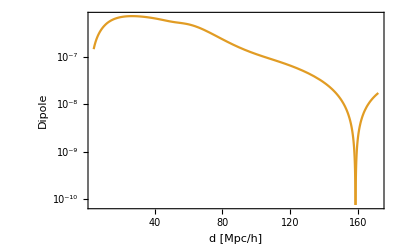

```mathematica
LogPlot[{Abs[varCPQUADHEXABrightLp4z015d[d]],Abs[varCCQUADHEXABrightLp4z015d[d]]},{d,4,172},PlotRange->{{4,172},All},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]",  "Dipole"},RotateLabel->True, ImageSize->{300}]
```

```mathematica
varTOTQUADHEXABrightLp4d4to172zSKA=varCCQUADHEXABrightLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXAFaintLp4d4to172zSKA=varCCQUADHEXAFaintLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA2popLp4d4to172zSKA=varCCQUADHEXA2popLp4d4to172zSKA;
```

```mathematica
Table[varTOTQUADHEXA2popLp4d4to172zSKA[[1,i,j]],{i,1,3},{j,1,3}]
```

{{-7.54331×10^-8,-2.22903×10^-7,-2.02004×10^-7},{-1.23884×10^-8,-1.83802×10^-7,-4.44029×10^-7},{-3.22464×10^-9,-5.34569×10^-8,-2.6884×10^-7}}

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Dipole/Octupole

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA=varCCDIPOCTrel2popLp4d4to172zSKA+varCPDIPOCT2popLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-7.84065×10^-9

## Covariance Matrix

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONOBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=CorrMonoBMonoF;
CorrMonoBMonoBF=Acc Table[varTOTMONOBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=CorrMonoBMonoBF;
CorrMonoBQuadB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONOFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONOFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=CorrMonoFMonoBF;
CorrMonoFQuadB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrMonoBF=Acc Table[varTOTMONO2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=CorrQuadBQuadF;
CorrQuadBF=Acc Table[varTOTQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=CorrQuadBQuadBF;
CorrQuadFQuadBF=Acc Table[varTOTQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=CorrQuadFQuadBF;
CorrQuadBHexa=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

True

```mathematica
InvCovMatrixtabzSKA=ParallelTable[Inverse[CovMatrixtabzSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrixtabzSKA[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
(*Export["CovarianceMatrixzSKA_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]*)
```

```mathematica
(*Export["CovarianceMatrix_P_at_z"<>ToString[zSKA[[1]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA[[1]],"Table","FieldSeparators"->" ",OverwriteTarget->True]*)
```

```mathematica
nBSKA
```

3/10

```mathematica
nFSKA
```

7/10

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

# Covariance + Octupole

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
ldist
```

36

```mathematica
Dimensions[CorrOct]
```

{19,36,36}

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-7.84065×10^-9

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;

CorrDipOct = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrOctDip = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrDipOct[[1,1,11]]
```

-2.58617×10^-8

```mathematica
CorrOctDip[[1,11,1]]
```

-2.58617×10^-8

```mathematica
CovMatrixOCTtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Dimensions[CovMatrixOCTtabzSKA]
```

{19,324,324}

EXPORT

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixOCTtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
nBSKA
```

3/10

```mathematica
nFSKA
```

7/10

# Signal-to-Noise Ratios

## Signals

## Parameters

```mathematica
βBzSKA=5 smodelBzSKA (1/(rH0zSKA HzSKA)-1) + fevolBzSKA;
βFzSKA= 5 smodelFzSKA (1/(rH0zSKA HzSKA)-1)+fevolFzSKA;
GtildezSKA= fzSKA D1zSKA Sigma8z0/D10;
IhatzSKA=OmegaMzSKA D1zSKA Sigma8z0/D10;
dGtildezSKA=-(1+zSKA) H0 HzSKA(Sigma8z0/D10) (dfdzSKA D1zSKA + fzSKA dD1dzSKA);
```

## Hexadecapole

```mathematica
Hexadecapole=(8 GtildezSKA^2/35)/Sigma8z0^2
```

{0.0723187,0.0761278,0.0779996,0.0782448,0.0772142,0.0752437,0.0726254,0.0695971,0.0663425,0.0629982,0.0596618,0.0564005,0.053258,0.0502613,0.0474248,0.0447544,0.0422501,0.0399079,0.0377213}

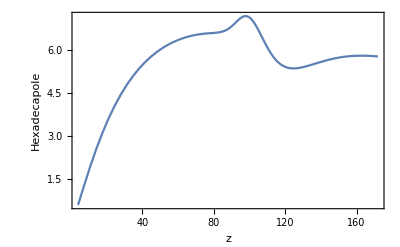

```mathematica
Plot[{d^2Hexadecapole[[1]] mu4z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Hexadecapole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Hexadecapolez1[d_]:=Hexadecapole[[1]] mu4z0[d];
```

## Monopole

```mathematica
mu0z0Lp4=Table[mu0z0[d],{d,4,172,4}];
```

```mathematica
MonopoleBright=(bBtildezSKA^2+2 bBtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{1.52899,1.52053,1.51026,1.50018,1.49199,1.48707,1.48651,1.4912,1.50185,1.51905,1.54334,1.57524,1.61528,1.66406,1.72221,1.79046,1.86967,1.9608,2.06497}

```mathematica
MonopoleFaint=(bFtildezSKA^2+2 bFtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{0.118832,0.148404,0.178472,0.208941,0.23998,0.271924,0.305211,0.340339,0.377844,0.418289,0.462266,0.510401,0.563364,0.621877,0.686732,0.758796,0.839034,0.928521,1.02846}

We take redshift z=0.15

```mathematica
MonopoleBf=Interpolation[Table[{d,MonopoleBright[[1]] mu0z0[d]},{d,4,172,4}]];
```

```mathematica
MonopoleFf=Interpolation[Table[{d,MonopoleFaint[[1]] mu0z0[d]},{d,4,172,4}]];
```

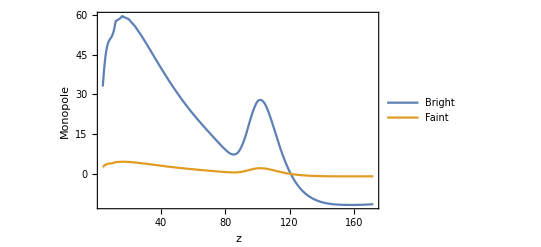

```mathematica
Plot[{d^2MonopoleBf[d],d^2MonopoleFf[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Monopole"},RotateLabel->True, ImageSize->{300},PlotLegends->{Bright, Faint}]
```

## Dipole

```mathematica
g1[z_]:=2/(r[z] HH[z])+1/2(-Omm(1+z)+2/(1+z)^2(1-Omm))/HH[z]^2
```

```mathematica
g1zSKA=Table[g1[i],{i,zSKA}]
```

{15.1422,9.64318,7.20087,5.78564,4.84435,4.16406,3.64492,3.23351,2.89842,2.61978,2.3843,2.18266,2.00812,1.85564,1.72137,1.60229,1.49603,1.40068,1.31468}

```mathematica
DipoleΛCDM=evolzSKA HzSKA(3(smodelBzSKA-smodelFzSKA)fzSKA^2 (1/(rH0zSKA HzSKA)-1)- 5(bBzSKA smodelFzSKA-bFzSKA smodelBzSKA)(1/(rH0zSKA HzSKA)-1) fzSKA+(bBzSKA-bFzSKA) g1zSKA fzSKA)
```

{18.7049,6.93007,4.49096,3.04636,1.98008,1.24304,0.785583,0.534071,0.40313,0.339628,0.312266,0.308562,0.323305,0.353265,0.393344,0.440838,0.494296,0.553599,0.617079}

```mathematica
Dipole=(HzSKA/Sigma8z0^2)(3 (βBzSKA-βFzSKA)GtildezSKA^2/5-(bBtildezSKA βFzSKA-bFtildezSKA βBzSKA)GtildezSKA -(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA  HzSKA))GtildezSKA+(3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA-(bBtildezSKA-bFtildezSKA)dGtildezSKA /(H0 HzSKA))
```

{11.5414,3.50493,1.85355,0.984379,0.852553,0.987359,1.2183,1.39332,1.5194,1.62369,1.72923,1.85608,1.99125,2.11863,2.24638,2.37682,2.5206,2.68547,2.85305}

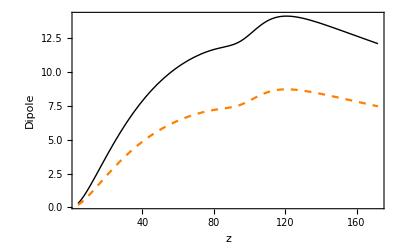

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d],d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipolez1[d_]:=Dipole[[1]] nu1z0[d]
```

```mathematica
WideAnglezSKA=-(2/5)(bBtildezSKA-bFtildezSKA)GtildezSKA/(rH0zSKA /H0)
```

{-0.000326314,-0.000195502,-0.000137739,-0.000104698,-0.0000831478,-0.0000679548,-0.0000566876,-0.0000480322,-0.000041209,-0.0000357222,-0.0000312393,-0.0000275284,-0.0000244224,-0.0000217975,-0.0000195605,-0.0000176397,-0.0000159792,-0.0000145349,-0.0000132716}

```mathematica
WideAnglez1[d_]:=WideAnglezSKA[[1]]d mu2z0[d]
```

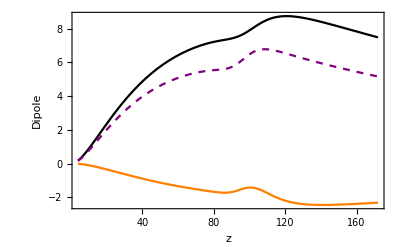

```mathematica
Plot[{d^2Dipole[[1]] nu1z0[d],  d^2(d WideAnglezSKA[[1]] mu2z0[d]),d^2Dipole[[1]] nu1z0[d]+  d^2 (d WideAnglezSKA[[1]] mu2z0[d])},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black},{Orange},{Purple,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Table[Dipolez1[d],{d,4,172,4}]
```

{0.0108583,0.00944902,0.00801662,0.00682552,0.00585653,0.00506596,0.00441512,0.00387389,0.0034196,0.00303495,0.00270665,0.00242443,0.00218025,0.00196771,0.00178171,0.00161807,0.00147336,0.00134467,0.00122958,0.00112614,0.0010332,0.000951157,0.000882384,0.00082907,0.00078894,0.000755211,0.000721511,0.000685123,0.000646313,0.000606511,0.000567137,0.000529204,0.000493317,0.000459758,0.000428608,0.000399824,0.000373296,0.000348873,0.000326391,0.000305682,0.000286587,0.000268968,0.0002527}

```mathematica
Table[WideAnglez1[d],{d,4,172,4}]
```

{-0.00100205,-0.00105958,-0.00101393,-0.000942135,-0.000866128,-0.000792953,-0.000725492,-0.000663493,-0.000608018,-0.000557686,-0.000512673,-0.000471974,-0.000435399,-0.000402326,-0.000372495,-0.000345525,-0.000321224,-0.000299381,-0.000279742,-0.000261742,-0.000243733,-0.000222207,-0.000194018,-0.000163536,-0.000142413,-0.000136579,-0.000141033,-0.000147771,-0.000152039,-0.000152599,-0.000149984,-0.000145158,-0.000139013,-0.00013221,-0.000125188,-0.000118211,-0.000111452,-0.000105017,-0.0000989589,-0.0000933033,-0.0000880097,-0.0000830487,-0.0000783809}

```mathematica
Abs[(Table[Dipolez1[d],{d,4,172,4}]-(Table[Dipolez1[d],{d,4,172,4}]+Table[WideAnglez1[d],{d,4,172,4}]))/(Table[Dipolez1[d],{d,4,172,4}])]
```

{0.0922844,0.112137,0.126478,0.138031,0.147891,0.156526,0.16432,0.171273,0.177804,0.183755,0.189412,0.194674,0.199701,0.204464,0.209066,0.213541,0.218021,0.222643,0.227511,0.232425,0.2359,0.233617,0.219879,0.197252,0.180512,0.180849,0.195469,0.215686,0.235241,0.251601,0.264458,0.274296,0.281792,0.287565,0.292081,0.295658,0.298563,0.301017,0.303191,0.30523,0.307096,0.308768,0.310174}

```mathematica
rH0zSKA/H0
```

{433.566,704.263,960.18,1201.58,1428.95,1642.94,1844.3,2033.82,2212.29,2380.49,2539.19,2689.08,2830.84,2965.07,3092.35,3213.19,3328.07,3437.42,3541.64}

## Quadrupole

```mathematica
QuadrupoleBright=-(4 bBtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.958985,-0.981859,-0.990866,-0.989223,-0.979907,-0.965463,-0.94794,-0.92892,-0.909575,-0.890749,-0.873026,-0.856796,-0.842311,-0.829717,-0.819095,-0.810474,-0.803855,-0.79922,-0.796541}

```mathematica
QuadrupoleFaint=-(4 bFtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.266056,-0.307512,-0.343117,-0.373072,-0.397985,-0.418648,-0.435884,-0.450464,-0.463065,-0.474261,-0.484523,-0.494233,-0.5037,-0.513169,-0.522839,-0.53287,-0.543392,-0.554515,-0.566331}

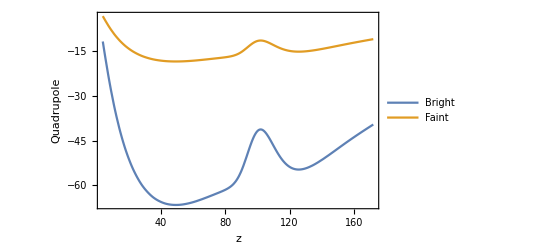

```mathematica
Plot[{d^2 QuadrupoleBright[[1]] mu2z0[d],d^2QuadrupoleFaint [[1]]mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Quadrupole"},RotateLabel->True, ImageSize->{300},PlotLegends-> {Bright,Faint}]
```

```mathematica
QuadrupoleBz1[d_]:=QuadrupoleBright[[1]] mu2z0[d]
QuadrupoleFz1[d_]:=QuadrupoleFaint[[1]] mu2z0[d]
```

## Octupole

```mathematica
Octupole=(HzSKA/Sigma8z0^2)2 (βBzSKA-βFzSKA)GtildezSKA^2/5
```

{2.11151,0.483304,0.253246,0.109003,0.104839,0.145488,0.196973,0.226399,0.239656,0.24456,0.248143,0.254043,0.259531,0.261676,0.262342,0.262151,0.262817,0.265374,0.26735}

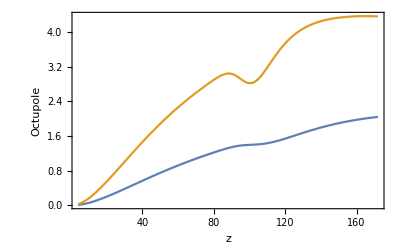

```mathematica
Plot[{d^2 Octupole[[1]] nu3z0[d], d^2 Octupole[[1]] nu3z0[d] - d^2 WideAnglezSKA[[1]]d mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Octupole"},RotateLabel->True, ImageSize->{300}]
```

```mathematica
Octupolez1[d_]:=Octupole[[1]] nu3z0[d]
OctupoleWAz1[d_]:=Octupole[[1]] nu3z0[d] -WideAnglezSKA[[1]] d mu2z0[d]
```

## Joint plot

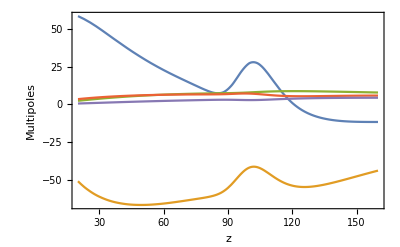

```mathematica
Plot[{d^2 MonopoleBf[d],d^2QuadrupoleBz1[d],d^2Dipolez1[d],d^2Hexadecapolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

## Signal-to-noise Ratios

```mathematica
{dmin,dmax}
```

{20,160}

```mathematica
{maxsep,ktot,indist,ldist}
```

{40,19,5,36}

## Monopole

```mathematica
ξ0BSKAmatrix=Table[MonopoleBright[[k]]mu0z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ0BSKAmatrix]
```

{36,19}

```mathematica
Dimensions[varTOTMONOBrightLp4d4to172zSKA]
```

{19,43,43}

```mathematica
varξ0BTOT=Table[ varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ0BTOT=Table[Inverse[varξ0BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ0BTOT]
```

{19,36,36}

```mathematica
SNrSKAMonopole=Table[Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{40.2043,63.8249,85.2751,104.205,120.34,133.508,143.429,149.878,152.541,151.11,145.727,136.488,123.781,108.61,91.454,73.8065,56.8482,41.4435,28.5723}

```mathematica
SNSKAMonopoleTotal= Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

481.483

## Dipole

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{43.7509,24.147,14.6275,7.5912,5.94802,6.07835,6.484,6.31562,5.76945,5.07352,4.38776,3.76538,3.17453,2.6142,2.09394,1.63525,1.24477,0.916213,0.644129}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

55.157

```mathematica
1-54.6434/78.2865
```

0.302007

## Dipole + WA

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d]+d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{37.214,16.0585,7.79631,2.6577,2.32988,3.37489,4.5046,4.8775,4.73112,4.32986,3.85748,3.39005,2.91146,2.43135,1.96907,1.55144,1.18977,0.881312,0.62284}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

43.1539

## Quadrupole

```mathematica
ξ2BSKAmatrix=Table[QuadrupoleBright[[k]]mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ2BSKAmatrix]
```

{36,19}

```mathematica
varξ2BTOT=Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ2BTOT=Table[Inverse[varξ2BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ2BTOT]
```

{19,36,36}

```mathematica
ldist
```

36

```mathematica
SNrSKAQuadrupole=Table[Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{29.4204,47.8043,64.6361,79.1882,90.9614,99.6809,105.104,107.136,105.706,100.851,93.0476,82.8027,70.8661,58.3366,45.8438,34.4223,24.641,16.701,10.7222}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

322.345

## Octupole

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
Octupole[[1;;ktot]]
```

{2.11151,0.483304,0.253246,0.109003,0.104839,0.145488,0.196973,0.226399,0.239656,0.24456,0.248143,0.254043,0.259531,0.261676,0.262342,0.262151,0.262817,0.265374,0.26735}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupole=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{4.67401,3.02234,1.92868,0.817118,0.71069,0.868749,1.01403,0.9887,0.87179,0.726252,0.591986,0.477689,0.376493,0.287179,0.211482,0.150972,0.104764,0.0702834,0.0450561}

```mathematica
SNSKAOctupoleTotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

6.38825

```mathematica
1-4.68151/8.50621
```

0.449636

## Octupole + WA

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d] -d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupoleWA=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{8.739,10.5535,8.68356,5.95113,4.40385,3.52483,2.92202,2.36043,1.85356,1.4229,1.08333,0.820765,0.612942,0.448207,0.318726,0.220867,0.149125,0.097421,0.0610009}

```mathematica
SNSKAOctupoleWATotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

18.7767

## Hexadecapole

```mathematica
ξ4TSKAmatrix=Table[Hexadecapole[[k]]mu4z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ4TSKAmatrix]
```

{36,19}

```mathematica
varξ4TTOT=Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ4TTOT=Table[Inverse[varξ4TTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ4TTOT]
```

{19,36,36}

```mathematica
SNrSKAHexadecapole=Table[Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{6.66027,10.6929,14.1735,16.9181,18.8424,19.9437,20.2513,19.8353,18.7762,17.171,15.176,12.9347,10.6058,8.37031,6.3183,4.56891,3.16054,2.07807,1.29745}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

59.2156

## Plot

```mathematica
SNSKAz015Dipole=Table[ξ1SKAmatrix[[m,2]]/Sqrt[varξ1TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Monopole=Table[ξ0BSKAmatrix[[m,2]]/Sqrt[varξ0BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Quadrupole=Table[Abs[ξ2BSKAmatrix[[m,2]]]/Sqrt[varξ2BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Octupole=Table[Abs[ξ3SKAmatrix[[m,2]]]/Sqrt[varξ3TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Hexadecapole=Table[Abs[ξ4TSKAmatrix[[m,2]]]/Sqrt[varξ4TTOT[[1,m,m]]],{m,1,ldist}];
```

```mathematica
ds=Table[d,{d,dmin,dmax,4}];
```

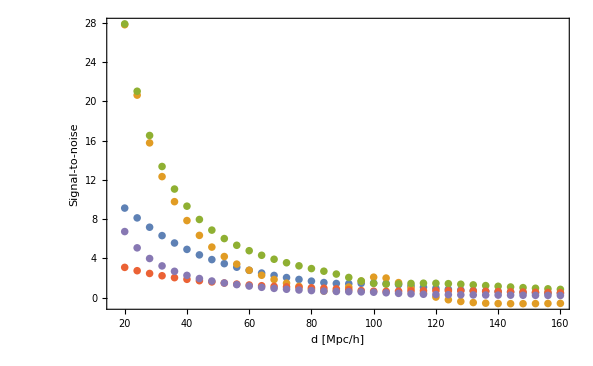

```mathematica
ListPlot[{Table[{ds[[i]], SNSKAz015Dipole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Monopole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Quadrupole[[i]]},{i,1,ldist}], Table[{ds[[i]], SNSKAz015Octupole[[i]]},{i,1,ldist}],
Table[{ds[[i]], SNSKAz015Hexadecapole[[i]]},{i,1,ldist}]},PlotRange->Full,PlotStyle->{•},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Signal-to-noise"},RotateLabel->True]
```

# Multi-SPLIT Covariance

## Covariance Blocks

## Parameters

### Galaxy bias

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bT[m_,dbz_]:=bmeanzSKA ;
```

#### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA50=bB[2, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA50=bF[2,dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bTzSKA50 = bT[2,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

#### Bright

```mathematica
nBSKA50 = 1/2;
```

```mathematica
smodelBzSKA50 = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA50 = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

#### Faint

```mathematica
nFSKA50 = 1/2;
```

```mathematica
smodelzSKA50 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA50);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA50 = (m/(m-1)) smodelzSKA50 -(1/(m-1)) smodelBzSKA50
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA50 = List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

#### Splitting with 30% Bright (m=10/3)

```mathematica
m=10/3;
```

```mathematica
db=1.2;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA30=bB[10/3, dbz]
```

{1.39304,1.44379,1.49867,1.55801,1.62219,1.6916,1.76666,1.84784,1.93563,2.03056,2.13323,2.24426,2.36434,2.49419,2.63462,2.78649,2.95073,3.12834,3.32042}

```mathematica
bFzSKA30=bF[10/3,dbz]
```

{0.293042,0.343787,0.398665,0.458013,0.522194,0.591603,0.666665,0.74784,0.835627,0.930564,1.03323,1.14426,1.26434,1.39419,1.53462,1.68649,1.85073,2.02834,2.22042}

```mathematica
bTzSKA30 = bT[10/3,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

#### Bright

```mathematica
nBSKA30 = 3/10;
```

```mathematica
smodelBzSKA30 = List[0.63665525,0.42367658,0.50881959,0.60522562,0.67778459,0.73405886,0.78698648,0.85067709,0.92313678,1.00034598,1.07877756,1.15621473,1.23564294,1.31904933,1.40610202,1.49646092,1.58855833,1.68141612,1.77443344];
```

```mathematica
fevolBzSKA30 = List[-2.35710791,0.50267603,0.00895782,-0.59492009,-0.49505863,-0.16404253,0.19264397,0.36952203,0.43853907,0.45440814,0.4833308,0.54007682,0.59932034,0.6323595,0.65280044,0.66681915,0.69110994,0.7429895,0.81482988];
```

#### Faint

```mathematica
nFSKA30 = 7/10;
```

```mathematica
smodelzSKA30 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA30);]
m
```

10/3

```mathematica
smodelFzSKA30 = (m/(m-1)) smodelzSKA30 -(1/(m-1)) smodelBzSKA30
```

{-0.128184,0.0583469,0.133246,0.226934,0.34323,0.467545,0.587359,0.69865,0.803523,0.904826,1.00684,1.11062,1.21737,1.32493,1.43485,1.54726,1.6627,1.78189,1.90084}

```mathematica
fevolFzSKA30 = List[4.22894971,3.22955823,2.61765473,1.95918753,0.94948372,0.01885715,-0.72267224,-1.22839524,-1.57209693,-1.82896117,-2.03473879,-2.22488036,-2.39749383,-2.54686948,-2.68379003,-2.81081826,-2.93482756,-3.05441667,-3.14524578];
```

#### Splitting with 10% Bright (m=10)

```mathematica
m=10;
```

```mathematica
db=1.1;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA10=bB[10, dbz]
```

{1.61304,1.66379,1.71867,1.77801,1.84219,1.9116,1.98666,2.06784,2.15563,2.25056,2.35323,2.46426,2.58434,2.71419,2.85462,3.00649,3.17073,3.34834,3.54042}

```mathematica
bFzSKA10=bF[10,dbz]
```

{0.513042,0.563787,0.618665,0.678013,0.742194,0.811603,0.886665,0.96784,1.05563,1.15056,1.25323,1.36426,1.48434,1.61419,1.75462,1.90649,2.07073,2.24834,2.44042}

```mathematica
bTzSKA10 = bT[10,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

#### Bright

```mathematica
nBSKA10 = 1/10;
```

```mathematica
smodelBzSKA10 = List[1.03913831,0.71999785,0.70016622,0.80291617,0.80509085,0.86385634,0.93133131,0.99350429,1.04896737,1.0983242,1.14410701,1.18703114,1.23676623,1.29877001,1.36750798,1.44075302,1.51593195,1.59199958,1.66844103];
```

```mathematica
fevolBzSKA10 =List[-24.023626,1.236314,-1.688862,-1.231461,-0.256573,-0.015632,0.066406,0.271551,0.571797,0.941879,1.356481,1.796966,2.166868,2.409665,2.598081,2.759553,2.921841,3.102200,3.295148];
```

#### Faint

```mathematica
nFSKA10 = 9/10;
```

```mathematica
smodelzSKA10 =List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA10);]
m
```

10

```mathematica
smodelFzSKA10 = (m/(m-1)) smodelzSKA10 -(1/(m-1)) smodelBzSKA10
```

{-0.00294009,0.106607,0.195446,0.289033,0.403431,0.512349,0.615682,0.716564,0.816123,0.915166,1.01556,1.11733,1.2213,1.32587,1.43275,1.54216,1.6543,1.7695,1.88453}

```mathematica
fevolFzSKA10 = List[5.17277222,2.54206913,2.22659099,1.46233479,0.60197595,-0.03827728,-0.50524214,-0.86241689,-1.14009535,-1.37570916,-1.57218441,-1.75009982,-1.90570711,-2.03785252,-2.15846779,-2.27053596,-2.37692272,-2.47268313,-2.54081985];
```

### Survey

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.199814},{0.25,0.116988},{0.35,0.0696126},{0.45,0.0422187},{0.55,0.026008},{0.65,0.0164685},{0.75,0.0105386},{0.85,0.00680012},{0.95,0.00438301},{1.05,0.00280384},{1.15,0.00179188},{1.25,0.00113765},{1.35,0.000715463},{1.45,0.00044797},{1.55,0.00027555},{1.65,0.000167586},{1.75,0.000100552},{1.85,0.0000589773},{1.95,0.0000338394}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.199814,0.116988,0.0696126,0.0422187,0.026008,0.0164685,0.0105386,0.00680012,0.00438301,0.00280384,0.00179188,0.00113765,0.000715463,0.00044797,0.00027555,0.000167586,0.000100552,0.0000589773,0.0000338394}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.21381×10^8

```mathematica
nBzSKA50=Table[nBSKA50, {i,Length[zSKA]}];
nFzSKA50=Table[nFSKA50, {i,Length[zSKA]}];
nBzSKA30=Table[nBSKA30, {i,Length[zSKA]}];
nFzSKA30=Table[nFSKA30, {i,Length[zSKA]}];
nBzSKA10=Table[nBSKA10, {i,Length[zSKA]}];
nFzSKA10=Table[nFSKA10, {i,Length[zSKA]}];
```

```mathematica
nBzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nBzSKA30
```

{3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10}

```mathematica
nFzSKA30
```

{7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10}

```mathematica
nBzSKA10
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

```mathematica
nFzSKA10
```

{9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10}

```mathematica
NbarBzSKA50=NbarzSKA*nBzSKA50
```

{0.0999069,0.0584939,0.0348063,0.0211094,0.013004,0.00823427,0.00526929,0.00340006,0.00219151,0.00140192,0.00089594,0.000568825,0.000357731,0.000223985,0.000137775,0.0000837929,0.0000502758,0.0000294887,0.0000169197}

```mathematica
NbarFzSKA50=NbarzSKA*nFzSKA50
```

{0.0999069,0.0584939,0.0348063,0.0211094,0.013004,0.00823427,0.00526929,0.00340006,0.00219151,0.00140192,0.00089594,0.000568825,0.000357731,0.000223985,0.000137775,0.0000837929,0.0000502758,0.0000294887,0.0000169197}

```mathematica
NbarBzSKA30=NbarzSKA*nBzSKA30
```

{0.0599442,0.0350963,0.0208838,0.0126656,0.00780241,0.00494056,0.00316157,0.00204004,0.0013149,0.000841152,0.000537564,0.000341295,0.000214639,0.000134391,0.0000826649,0.0000502758,0.0000301655,0.0000176932,0.0000101518}

```mathematica
NbarFzSKA30=NbarzSKA*nFzSKA30
```

{0.13987,0.0818915,0.0487288,0.0295531,0.0182056,0.011528,0.007377,0.00476008,0.00306811,0.00196269,0.00125432,0.000796355,0.000500824,0.000313579,0.000192885,0.00011731,0.0000703861,0.0000412841,0.0000236876}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.71785×10^-9,5.46605×10^-9,4.73476×10^-9,4.77832×10^-9,5.26888×10^-9,6.06247×10^-9,7.25896×10^-9,8.95265×10^-9,1.13845×10^-8,1.49341×10^-8,1.99891×10^-8,2.73628×10^-8,3.8321×10^-8,5.45185×10^-8,7.97218×10^-8,1.18897×10^-7,1.81065×10^-7,2.83887×10^-7,4.57598×10^-7}

```mathematica
coeffBSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.71785×10^-9,5.46605×10^-9,4.73476×10^-9,4.77832×10^-9,5.26888×10^-9,6.06247×10^-9,7.25896×10^-9,8.95265×10^-9,1.13845×10^-8,1.49341×10^-8,1.99891×10^-8,2.73628×10^-8,3.8321×10^-8,5.45185×10^-8,7.97218×10^-8,1.18897×10^-7,1.81065×10^-7,2.83887×10^-7,4.57598×10^-7}

```mathematica
coeffBSKA50/nBzSKA50
```

{1.74357×10^-8,1.09321×10^-8,9.46952×10^-9,9.55664×10^-9,1.05378×10^-8,1.21249×10^-8,1.45179×10^-8,1.79053×10^-8,2.2769×10^-8,2.98681×10^-8,3.99783×10^-8,5.47256×10^-8,7.6642×10^-8,1.09037×10^-7,1.59444×10^-7,2.37795×10^-7,3.6213×10^-7,5.67774×10^-7,9.15197×10^-7}

```mathematica
coeffFSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.71785×10^-9,5.46605×10^-9,4.73476×10^-9,4.77832×10^-9,5.26888×10^-9,6.06247×10^-9,7.25896×10^-9,8.95265×10^-9,1.13845×10^-8,1.49341×10^-8,1.99891×10^-8,2.73628×10^-8,3.8321×10^-8,5.45185×10^-8,7.97218×10^-8,1.18897×10^-7,1.81065×10^-7,2.83887×10^-7,4.57598×10^-7}

```mathematica
coeffFSKA50/nFzSKA50
```

{1.74357×10^-8,1.09321×10^-8,9.46952×10^-9,9.55664×10^-9,1.05378×10^-8,1.21249×10^-8,1.45179×10^-8,1.79053×10^-8,2.2769×10^-8,2.98681×10^-8,3.99783×10^-8,5.47256×10^-8,7.6642×10^-8,1.09037×10^-7,1.59444×10^-7,2.37795×10^-7,3.6213×10^-7,5.67774×10^-7,9.15197×10^-7}

```mathematica
coeffBSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.71785×10^-9,5.46605×10^-9,4.73476×10^-9,4.77832×10^-9,5.26888×10^-9,6.06247×10^-9,7.25896×10^-9,8.95265×10^-9,1.13845×10^-8,1.49341×10^-8,1.99891×10^-8,2.73628×10^-8,3.8321×10^-8,5.45185×10^-8,7.97218×10^-8,1.18897×10^-7,1.81065×10^-7,2.83887×10^-7,4.57598×10^-7}

```mathematica
coeffBSKA30/nBzSKA30
```

{2.90595×10^-8,1.82202×10^-8,1.57825×10^-8,1.59277×10^-8,1.75629×10^-8,2.02082×10^-8,2.41965×10^-8,2.98422×10^-8,3.79484×10^-8,4.97802×10^-8,6.66305×10^-8,9.12094×10^-8,1.27737×10^-7,1.81728×10^-7,2.65739×10^-7,3.96324×10^-7,6.0355×10^-7,9.4629×10^-7,1.52533×10^-6}

```mathematica
coeffFSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.71785×10^-9,5.46605×10^-9,4.73476×10^-9,4.77832×10^-9,5.26888×10^-9,6.06247×10^-9,7.25896×10^-9,8.95265×10^-9,1.13845×10^-8,1.49341×10^-8,1.99891×10^-8,2.73628×10^-8,3.8321×10^-8,5.45185×10^-8,7.97218×10^-8,1.18897×10^-7,1.81065×10^-7,2.83887×10^-7,4.57598×10^-7}

```mathematica
coeffFSKA30/nFzSKA30
```

{1.24541×10^-8,7.80864×10^-9,6.76394×10^-9,6.82617×10^-9,7.52698×10^-9,8.66067×10^-9,1.03699×10^-8,1.27895×10^-8,1.62636×10^-8,2.13344×10^-8,2.85559×10^-8,3.90897×10^-8,5.47443×10^-8,7.78836×10^-8,1.13888×10^-7,1.69853×10^-7,2.58664×10^-7,4.05553×10^-7,6.53712×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA50=(5smodelBzSKA50 +(2-5smodelBzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA50)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA50=(5smodelFzSKA50 +(2-5smodelFzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA50)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
cBzSKA30=(5smodelBzSKA30 +(2-5smodelBzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA30)fzSKA
```

{-1.70391,0.895284,0.592824,0.630427,0.480152,0.279389,0.0786685,0.00333885,0.0248213,0.116481,0.226818,0.340321,0.472092,0.646354,0.851276,1.08106,1.31899,1.54657,1.7686}

```mathematica
cFzSKA30=(5smodelFzSKA30 +(2-5smodelFzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA30)fzSKA
```

{9.13213,3.51792,2.0517,1.29866,1.16499,1.29248,1.54051,1.79292,2.04051,2.30254,2.58099,2.8947,3.23377,3.58883,3.964,4.35837,4.77599,5.21419,5.6457}

```mathematica
cBzSKA10=(5smodelBzSKA10 +(2-5smodelBzSKA10)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA10)fzSKA
```

{3.67453,-3.17161,0.108577,-0.235995,-0.390502,-0.404636,-0.326334,-0.320991,-0.377903,-0.489366,-0.644756,-0.830882,-0.966863,-0.992326,-0.961212,-0.894509,-0.817281,-0.746799,-0.679258}

```mathematica
cFzSKA10=(5smodelFzSKA10 +(2-5smodelFzSKA10)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA10)fzSKA
```

{6.12652,3.38699,1.78131,1.24643,1.10954,1.14335,1.26066,1.43127,1.63733,1.88406,2.15468,2.4572,2.77995,3.11702,3.47367,3.84958,4.24514,4.65398,5.05611}

### Elements

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[1,1,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[1,1,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[1,1,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[1,1,3,3]),f,Simplify]
```

```mathematica
coeffvarCCrelSKAz[bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2coeffcovCCrel[bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

20

```mathematica
4 i /. i -> 43
```

20

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
```

#### Monopole

Monopole 50  - Monopole 50

```mathematica
coeffvarCCpop50pop30BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{7.32164×10^-9,2.9183×10^-9,1.6269×10^-9,1.07485×10^-9,7.87973×10^-10,6.20498×10^-10,5.15334×10^-10,4.46324×10^-10,4.00113×10^-10,3.69333×10^-10,3.49704×10^-10,3.38664×10^-10,3.34681×10^-10,3.36886×10^-10,3.44872×10^-10,3.5858×10^-10,3.78248×10^-10,4.04385×10^-10,4.37778×10^-10}

```mathematica
a =coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA50,bBzSKA50,fzSKA]
```

{5.14716×10^-9,2.0861×10^-9,1.18089×10^-9,7.91299×10^-10,5.87812×10^-10,4.68678×10^-10,3.93883×10^-10,3.45035×10^-10,3.12722×10^-10,2.91753×10^-10,2.79124×10^-10,2.73059×10^-10,2.72527×10^-10,2.76985×10^-10,2.86237×10^-10,3.00367×10^-10,3.19696×10^-10,3.44781×10^-10,3.76425×10^-10}

```mathematica
b =coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA30,bBzSKA30,fzSKA]
```

{1.04359×10^-8,4.09052×10^-9,2.24553×10^-9,1.46253×10^-9,1.05796×10^-9,8.22666×10^-10,6.75088×10^-10,5.77994×10^-10,5.12425×10^-10,4.67937×10^-10,4.38448×10^-10,4.20288×10^-10,4.11223×10^-10,4.09921×10^-10,4.15668×10^-10,4.28203×10^-10,4.47633×10^-10,4.74387×10^-10,5.09211×10^-10}

```mathematica
coeffvarCCpop50pop30BzSKA
```

{7.32164×10^-9,2.9183×10^-9,1.6269×10^-9,1.07485×10^-9,7.87973×10^-10,6.20498×10^-10,5.15334×10^-10,4.46324×10^-10,4.00113×10^-10,3.69333×10^-10,3.49704×10^-10,3.38664×10^-10,3.34681×10^-10,3.36886×10^-10,3.44872×10^-10,3.5858×10^-10,3.78248×10^-10,4.04385×10^-10,4.37778×10^-10}

```mathematica
Sqrt[a * b]- coeffvarCCpop50pop30BzSKA
```

{7.43398×10^-12,2.86516×10^-12,1.51051×10^-12,9.26709×10^-13,6.2124×10^-13,4.41415×10^-13,3.26882×10^-13,2.49714×10^-13,1.95479×10^-13,1.56083×10^-13,1.26697×10^-13,1.0429×10^-13,8.68842×10^-14,7.31477×10^-14,6.21561×10^-14,5.32534×10^-14,4.59646×10^-14,3.99395×10^-14,3.49158×10^-14}

```mathematica
coeffvarCCpop30pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{7.32164×10^-9,2.9183×10^-9,1.6269×10^-9,1.07485×10^-9,7.87973×10^-10,6.20498×10^-10,5.15334×10^-10,4.46324×10^-10,4.00113×10^-10,3.69333×10^-10,3.49704×10^-10,3.38664×10^-10,3.34681×10^-10,3.36886×10^-10,3.44872×10^-10,3.5858×10^-10,3.78248×10^-10,4.04385×10^-10,4.37778×10^-10}

```mathematica
coeffvarCCpop50pop30FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.00607×10^-10,5.59237×10^-11,4.12803×10^-11,3.47515×10^-11,3.15421×10^-11,3.00889×10^-11,2.97684×10^-11,3.03112×10^-11,3.16105×10^-11,3.3649×10^-11,3.64694×10^-11,4.01631×10^-11,4.48683×10^-11,5.07739×10^-11,5.81276×10^-11,6.72481×10^-11,7.8542×10^-11,9.25253×10^-11,1.09853×10^-10}

```mathematica
coeffvarCCpop30pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.00607×10^-10,5.59237×10^-11,4.12803×10^-11,3.47515×10^-11,3.15421×10^-11,3.00889×10^-11,2.97684×10^-11,3.03112×10^-11,3.16105×10^-11,3.3649×10^-11,3.64694×10^-11,4.01631×10^-11,4.48683×10^-11,5.07739×10^-11,5.81276×10^-11,6.72481×10^-11,7.8542×10^-11,9.25253×10^-11,1.09853×10^-10}

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCCpop50pop30BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCCpop30pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCCpop50pop30FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCCpop30pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

```mathematica
varCCMONOBrightLp4d4to172zSKA[[1,1+4,1+4]]
```

0.0000230961

```mathematica
a[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]]
```

0.0000113914

```mathematica
b[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]]
```

0.0000230961

```mathematica
Sqrt[b[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]] a[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]]]
```

0.0000162202

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA[[1,1+4,1+4]]
```

0.0000162038

```mathematica
coeffvarCCpop50pop10BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{9.38055×10^-9,3.70121×10^-9,2.04397×10^-9,1.33852×10^-9,9.73107×10^-10,7.60208×10^-10,6.26552×10^-10,5.38642×10^-10,4.79398×10^-10,4.39403×10^-10,4.13172×10^-10,3.97405×10^-10,3.90099×10^-10,3.90076×10^-10,3.96727×10^-10,4.09859×10^-10,4.29627×10^-10,4.5649×10^-10,4.91216×10^-10}

```mathematica
coeffvarCCpop10pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bBzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{9.38055×10^-9,3.70121×10^-9,2.04397×10^-9,1.33852×10^-9,9.73107×10^-10,7.60208×10^-10,6.26552×10^-10,5.38642×10^-10,4.79398×10^-10,4.39403×10^-10,4.13172×10^-10,3.97405×10^-10,3.90099×10^-10,3.90076×10^-10,3.96727×10^-10,4.09859×10^-10,4.29627×10^-10,4.5649×10^-10,4.91216×10^-10}

```mathematica
coeffvarCCpop50pop10FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{1.72352×10^-10,9.16345×10^-11,6.51665×10^-11,5.31363×10^-11,4.68993×10^-11,4.36344×10^-11,4.21989×10^-11,4.20755×10^-11,4.30267×10^-11,4.49628×10^-11,4.78857×10^-11,5.18652×10^-11,5.70304×10^-11,6.35701×10^-11,7.17394×10^-11,8.18706×10^-11,9.43898×10^-11,1.0984×10^-10,1.28907×10^-10}

```mathematica
coeffvarCCpop10pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{1.72352×10^-10,9.16345×10^-11,6.51665×10^-11,5.31363×10^-11,4.68993×10^-11,4.36344×10^-11,4.21989×10^-11,4.20755×10^-11,4.30267×10^-11,4.49628×10^-11,4.78857×10^-11,5.18652×10^-11,5.70304×10^-11,6.35701×10^-11,7.17394×10^-11,8.18706×10^-11,9.43898×10^-11,1.0984×10^-10,1.28907×10^-10}

```mathematica
varCCMONO50Bx10BLp4d4to172zSKA=Table[coeffvarCCpop50pop10BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10Bx50BLp4d4to172zSKA=Table[coeffvarCCpop10pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx10FLp4d4to172zSKA=Table[coeffvarCCpop50pop10FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO10Fx50FLp4d4to172zSKA=Table[coeffvarCCpop10pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

```mathematica
coeffvarCCpop50BFpop30BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{7.62753×10^-10,3.66663×10^-10,2.39178×10^-10,1.80826×10^-10,1.49185×10^-10,1.30535×10^-10,1.19277×10^-10,1.12771×10^-10,1.09659×10^-10,1.0922×10^-10,1.11082×10^-10,1.15093×10^-10,1.21257×10^-10,1.29699×10^-10,1.40658×10^-10,1.54489×10^-10,1.71671×10^-10,1.92831×10^-10,2.18771×10^-10}

```mathematica
coeffvarCCpop30BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{7.62753×10^-10,3.66663×10^-10,2.39178×10^-10,1.80826×10^-10,1.49185×10^-10,1.30535×10^-10,1.19277×10^-10,1.12771×10^-10,1.09659×10^-10,1.0922×10^-10,1.11082×10^-10,1.15093×10^-10,1.21257×10^-10,1.29699×10^-10,1.40658×10^-10,1.54489×10^-10,1.71671×10^-10,1.92831×10^-10,2.18771×10^-10}

```mathematica
varCCMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50BFpop10BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{1.15269×10^-9,5.37634×10^-10,3.41711×10^-10,2.52544×10^-10,2.04189×10^-10,1.75435×10^-10,1.57648×10^-10,1.46758×10^-10,1.40655×10^-10,1.38188×10^-10,1.38734×10^-10,1.41981×10^-10,1.47834×10^-10,1.56358×10^-10,1.67758×10^-10,1.82371×10^-10,2.00677×10^-10,2.23314×10^-10,2.51106×10^-10}

```mathematica
coeffvarCCpop10BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{1.15269×10^-9,5.37634×10^-10,3.41711×10^-10,2.52544×10^-10,2.04189×10^-10,1.75435×10^-10,1.57648×10^-10,1.46758×10^-10,1.40655×10^-10,1.38188×10^-10,1.38734×10^-10,1.41981×10^-10,1.47834×10^-10,1.56358×10^-10,1.67758×10^-10,1.82371×10^-10,2.00677×10^-10,2.23314×10^-10,2.51106×10^-10}

```mathematica
varCCMONO50BFx10BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop10BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop10BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole 1 pop - Monopole 2 pop

```mathematica
coeffvarCC50B30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.49662×10^-9,1.07868×10^-9,6.44438×10^-10,4.52302×10^-10,3.49877×10^-10,2.89188×10^-10,2.51048×10^-10,2.26513×10^-10,2.10966×10^-10,2.01854×10^-10,1.97721×10^-10,1.97743×10^-10,2.01495×10^-10,2.08829×10^-10,2.19813×10^-10,2.34699×10^-10,2.5392×10^-10,2.78094×10^-10,3.08052×10^-10}

```mathematica
coeffvarCC30BF50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.49662×10^-9,1.07868×10^-9,6.44438×10^-10,4.52302×10^-10,3.49877×10^-10,2.89188×10^-10,2.51048×10^-10,2.26513×10^-10,2.10966×10^-10,2.01854×10^-10,1.97721×10^-10,1.97743×10^-10,2.01495×10^-10,2.08829×10^-10,2.19813×10^-10,2.34699×10^-10,2.5392×10^-10,2.78094×10^-10,3.08052×10^-10}

```mathematica
coeffvarCC50F30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.54924×10^-10,1.33718×10^-10,9.38781×10^-11,7.56134×10^-11,6.5956×10^-11,6.06676×10^-11,5.80196×10^-11,5.72149×10^-11,5.78697×10^-11,5.98142×10^-11,6.30067×10^-11,6.74959×10^-11,7.34046×10^-11,8.09267×10^-11,9.03317×10^-11,1.01975×10^-10,1.16313×10^-10,1.3393×10^-10,1.55561×10^-10}

```mathematica
coeffvarCC30B50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.0724×10^-9,9.33509×10^-10,5.75043×10^-10,4.13103×10^-10,3.25432×10^-10,2.72939×10^-10,2.39782×10^-10,2.18492×10^-10,2.0518×10^-10,1.97685×10^-10,1.94777×10^-10,1.95766×10^-10,2.00318×10^-10,2.08342×10^-10,2.19948×10^-10,2.35419×10^-10,2.55211×10^-10,2.79963×10^-10,3.10525×10^-10}

```mathematica
coeffvarCC50BF30B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.0724×10^-9,9.33509×10^-10,5.75043×10^-10,4.13103×10^-10,3.25432×10^-10,2.72939×10^-10,2.39782×10^-10,2.18492×10^-10,2.0518×10^-10,1.97685×10^-10,1.94777×10^-10,1.95766×10^-10,2.00318×10^-10,2.08342×10^-10,2.19948×10^-10,2.35419×10^-10,2.55211×10^-10,2.79963×10^-10,3.10525×10^-10}

```mathematica
coeffvarCC30F50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.90093×10^-10,1.48361×10^-10,1.02145×10^-10,8.10098×10^-11,6.97806×10^-11,6.3519×10^-11,6.02133×10^-11,5.89318×10^-11,5.92195×10^-11,6.08649×10^-11,6.38002×10^-11,6.80563×10^-11,7.37432×10^-11,8.10448×10^-11,9.02218×10^-11,1.01621×10^-10,1.15693×10^-10,1.33012×10^-10,1.54305×10^-10}

```mathematica
coeffvarCC50BF30F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.90093×10^-10,1.48361×10^-10,1.02145×10^-10,8.10098×10^-11,6.97806×10^-11,6.3519×10^-11,6.02133×10^-11,5.89318×10^-11,5.92195×10^-11,6.08649×10^-11,6.38002×10^-11,6.80563×10^-11,7.37432×10^-11,8.10448×10^-11,9.02218×10^-11,1.01621×10^-10,1.15693×10^-10,1.33012×10^-10,1.54305×10^-10}

```mathematica
varCCMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50B30BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BF50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30B50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BF30B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx30BFLp4d4to172zSKA= Table[coeffvarCC50F30BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BFLp4d4to172zSKA= Table[coeffvarCC30F50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{8.94359×10^-10,4.15562×10^-10,2.64293×10^-10,1.95945×10^-10,1.59168×10^-10,1.37525×10^-10,1.24359×10^-10,1.1655×10^-10,1.12497×10^-10,1.1134×10^-10,1.12627×10^-10,1.16157×10^-10,1.21896×10^-10,1.29947×10^-10,1.40531×10^-10,1.53986×10^-10,1.7078×10^-10,1.91526×10^-10,2.17016×10^-10}

```mathematica
coeffvarCCpop30Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{8.94359×10^-10,4.15562×10^-10,2.64293×10^-10,1.95945×10^-10,1.59168×10^-10,1.37525×10^-10,1.24359×10^-10,1.1655×10^-10,1.12497×10^-10,1.1134×10^-10,1.12627×10^-10,1.16157×10^-10,1.21896×10^-10,1.29947×10^-10,1.40531×10^-10,1.53986×10^-10,1.7078×10^-10,1.91526×10^-10,2.17016×10^-10}

```mathematica
coeffvarCCpop50Fpop30BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{6.5971×10^-10,3.2634×10^-10,2.17653×10^-10,1.67478×10^-10,1.40161×10^-10,1.24096×10^-10,1.14522×10^-10,1.09189×10^-10,1.06942×10^-10,1.07172×10^-10,1.09579×10^-10,1.14054×10^-10,1.2063×10^-10,1.29457×10^-10,1.4079×10^-10,1.54996×10^-10,1.72568×10^-10,1.94145×10^-10,2.2054×10^-10}

```mathematica
coeffvarCCpop30Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{6.5971×10^-10,3.2634×10^-10,2.17653×10^-10,1.67478×10^-10,1.40161×10^-10,1.24096×10^-10,1.14522×10^-10,1.09189×10^-10,1.06942×10^-10,1.07172×10^-10,1.09579×10^-10,1.14054×10^-10,1.2063×10^-10,1.29457×10^-10,1.4079×10^-10,1.54996×10^-10,1.72568×10^-10,1.94145×10^-10,2.2054×10^-10}

```mathematica
varCCMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop30FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCCpop30Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCCpop30Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop30BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCC50B10BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{3.91099×10^-9,1.62629×10^-9,9.41052×10^-10,6.42731×10^-10,4.85533×10^-10,3.92968×10^-10,3.34746×10^-10,2.96862×10^-10,2.72116×10^-10,2.56531×10^-10,2.47812×10^-10,2.44618×10^-10,2.46195×10^-10,2.52184×10^-10,2.62512×10^-10,2.77345×10^-10,2.97061×10^-10,3.22254×10^-10,3.53752×10^-10}

```mathematica
coeffvarCC10BF50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{3.91099×10^-9,1.62629×10^-9,9.41052×10^-10,6.42731×10^-10,4.85533×10^-10,3.92968×10^-10,3.34746×10^-10,2.96862×10^-10,2.72116×10^-10,2.56531×10^-10,2.47812×10^-10,2.44618×10^-10,2.46195×10^-10,2.52184×10^-10,2.62512×10^-10,2.77345×10^-10,2.97061×10^-10,3.22254×10^-10,3.53752×10^-10}

```mathematica
coeffvarCC50F10BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{3.76763×10^-10,1.92394×10^-10,1.32×10^-10,1.04199×10^-10,8.92715×10^-11,8.07831×10^-11,7.61005×10^-11,7.39933×10^-11,7.38485×10^-11,7.53665×10^-11,7.84299×10^-11,8.3043×10^-11,8.93045×10^-11,9.73984×10^-11,1.07594×10^-10,1.20256×10^-10,1.35858×10^-10,1.55006×10^-10,1.7847×10^-10}

```mathematica
coeffvarCC10B50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bBzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{2.62973×10^-9,1.17419×10^-9,7.17343×10^-10,5.11312×10^-10,3.99804×10^-10,3.32916×10^-10,2.90441×10^-10,2.62856×10^-10,2.45192×10^-10,2.34676×10^-10,2.29711×10^-10,2.29381×10^-10,2.33204×10^-10,2.40999×10^-10,2.52818×10^-10,2.68913×10^-10,2.89729×10^-10,3.15909×10^-10,3.48318×10^-10}

```mathematica
coeffvarCC50BF10B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{2.62973×10^-9,1.17419×10^-9,7.17343×10^-10,5.11312×10^-10,3.99804×10^-10,3.32916×10^-10,2.90441×10^-10,2.62856×10^-10,2.45192×10^-10,2.34676×10^-10,2.29711×10^-10,2.29381×10^-10,2.33204×10^-10,2.40999×10^-10,2.52818×10^-10,2.68913×10^-10,2.89729×10^-10,3.15909×10^-10,3.48318×10^-10}

```mathematica
coeffvarCC10F50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{5.12636×10^-10,2.49623×10^-10,1.64912×10^-10,1.26235×10^-10,1.05416×10^-10,9.3341×10^-11,8.62964×10^-11,8.25426×10^-11,8.11986×10^-11,8.18113×10^-11,8.41694×10^-11,8.82166×10^-11,9.40106×10^-11,1.01706×10^-10,1.1155×10^-10,1.23891×10^-10,1.39187×10^-10,1.58032×10^-10,1.81183×10^-10}

```mathematica
coeffvarCC50BF10F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{5.12636×10^-10,2.49623×10^-10,1.64912×10^-10,1.26235×10^-10,1.05416×10^-10,9.3341×10^-11,8.62964×10^-11,8.25426×10^-11,8.11986×10^-11,8.18113×10^-11,8.41694×10^-11,8.82166×10^-11,9.40106×10^-11,1.01706×10^-10,1.1155×10^-10,1.23891×10^-10,1.39187×10^-10,1.58032×10^-10,1.81183×10^-10}

```mathematica
varCCMONO50Bx10BFLp4d4to172zSKA=Table[coeffvarCC50B10BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10BFx50BLp4d4to172zSKA=Table[coeffvarCC10BF50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Bx50BFLp4d4to172zSKA=Table[coeffvarCC10B50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx10BLp4d4to172zSKA=Table[coeffvarCC50BF10B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx10BFLp4d4to172zSKA= Table[coeffvarCC50F10BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Fx50BFLp4d4to172zSKA= Table[coeffvarCC10F50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop10FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{1.66417×10^-9,7.27869×10^-10,4.40444×10^-10,3.13136×10^-10,2.45347×10^-10,2.05376×10^-10,1.80538×10^-10,1.64929×10^-10,1.55511×10^-10,1.50624×10^-10,1.49341×10^-10,1.51165×10^-10,1.55879×10^-10,1.63467×10^-10,1.74075×10^-10,1.87998×10^-10,2.05683×10^-10,2.27742×10^-10,2.54978×10^-10}

```mathematica
coeffvarCCpop10Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{1.66417×10^-9,7.27869×10^-10,4.40444×10^-10,3.13136×10^-10,2.45347×10^-10,2.05376×10^-10,1.80538×10^-10,1.64929×10^-10,1.55511×10^-10,1.50624×10^-10,1.49341×10^-10,1.51165×10^-10,1.55879×10^-10,1.63467×10^-10,1.74075×10^-10,1.87998×10^-10,2.05683×10^-10,2.27742×10^-10,2.54978×10^-10}

```mathematica
coeffvarCCpop50Fpop10BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{8.31643×10^-10,4.07981×10^-10,2.7001×10^-10,2.06263×10^-10,1.71435×10^-10,1.50782×10^-10,1.38254×10^-10,1.30982×10^-10,1.27483×10^-10,1.26963×10^-10,1.29009×10^-10,1.33446×10^-10,1.40268×10^-10,1.49604×10^-10,1.61703×10^-10,1.76936×10^-10,1.9581×10^-10,2.18984×10^-10,2.47302×10^-10}

```mathematica
coeffvarCCpop10Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bBzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{8.31643×10^-10,4.07981×10^-10,2.7001×10^-10,2.06263×10^-10,1.71435×10^-10,1.50782×10^-10,1.38254×10^-10,1.30982×10^-10,1.27483×10^-10,1.26963×10^-10,1.29009×10^-10,1.33446×10^-10,1.40268×10^-10,1.49604×10^-10,1.61703×10^-10,1.76936×10^-10,1.9581×10^-10,2.18984×10^-10,2.47302×10^-10}

```mathematica
varCCMONO50Bx10FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop10FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Fx50BLp4d4to172zSKA=Table[coeffvarCCpop10Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Bx50FLp4d4to172zSKA=Table[coeffvarCCpop10Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx10BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop10BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffcovCCrel[bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
coeffvarCC50BF30BFrelzSKA=coeffvarCCrelSKAz[bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{2.80491×10^-8,1.09807×10^-9,1.22331×10^-10,2.31425×10^-11,1.76311×10^-11,2.09377×10^-11,2.68378×10^-11,3.35734×10^-11,3.96162×10^-11,4.38457×10^-11,4.59709×10^-11,4.64395×10^-11,4.6618×10^-11,4.66745×10^-11,4.75756×10^-11,4.9553×10^-11,5.30834×10^-11,5.86519×10^-11,6.49017×10^-11}

```mathematica
coeffvarCC30BF50BFrelzSKA=coeffvarCCrelSKAz[bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{2.80491×10^-8,1.09807×10^-9,1.22331×10^-10,2.31425×10^-11,1.76311×10^-11,2.09377×10^-11,2.68378×10^-11,3.35734×10^-11,3.96162×10^-11,4.38457×10^-11,4.59709×10^-11,4.64395×10^-11,4.6618×10^-11,4.66745×10^-11,4.75756×10^-11,4.9553×10^-11,5.30834×10^-11,5.86519×10^-11,6.49017×10^-11}

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCC50BF30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC30BF50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF10BFrelzSKA=coeffvarCCrelSKAz[bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,cBzSKA50,cFzSKA50,cBzSKA10,cFzSKA10,fzSKA]
```

{1.41383×10^-8,1.92397×10^-9,1.31356×10^-10,3.50304×10^-11,2.76648×10^-11,2.73905×10^-11,2.8351×10^-11,3.30922×10^-11,3.96099×10^-11,4.64645×10^-11,5.20326×10^-11,5.57721×10^-11,5.82991×10^-11,5.96903×10^-11,6.17941×10^-11,6.51723×10^-11,7.05035×10^-11,7.83792×10^-11,8.72435×10^-11}

```mathematica
coeffvarCC10BF50BFrelzSKA=coeffvarCCrelSKAz[bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,cBzSKA10,cFzSKA10,cBzSKA50,cFzSKA50,fzSKA]
```

{1.41383×10^-8,1.92397×10^-9,1.31356×10^-10,3.50304×10^-11,2.76648×10^-11,2.73905×10^-11,2.8351×10^-11,3.30922×10^-11,3.96099×10^-11,4.64645×10^-11,5.20326×10^-11,5.57721×10^-11,5.82991×10^-11,5.96903×10^-11,6.17941×10^-11,6.51723×10^-11,7.05035×10^-11,7.83792×10^-11,8.72435×10^-11}

```mathematica
varCCDIP50BFx10BFrelLp4d4to172zSKA=Table[coeffvarCC50BF10BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP10BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC10BF50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCCpop50pop3022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.05882×10^-9,8.29638×10^-10,4.65576×10^-10,3.08489×10^-10,2.26099×10^-10,1.77534×10^-10,1.46702×10^-10,1.26191×10^-10,1.1219×10^-10,1.02584×10^-10,9.61266×10^-11,9.2063×10^-11,8.99269×10^-11,8.94384×10^-11,9.0444×10^-11,9.28842×10^-11,9.67752×10^-11,1.022×10^-10,1.09308×10^-10}

```mathematica
coeffvarCCpop50pop3022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.85408×10^-11,2.61586×10^-11,1.87232×10^-11,1.52774×10^-11,1.34308×10^-11,1.24×10^-11,1.18653×10^-11,1.16791×10^-11,1.17706×10^-11,1.21086×10^-11,1.26858×10^-11,1.35117×10^-11,1.46099×10^-11,1.60177×10^-11,1.77866×10^-11,1.99849×10^-11,2.27007×10^-11,2.60462×10^-11,3.0164×10^-11}

```mathematica
coeffvarCCpop30pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.05882×10^-9,8.29638×10^-10,4.65576×10^-10,3.08489×10^-10,2.26099×10^-10,1.77534×10^-10,1.46702×10^-10,1.26191×10^-10,1.1219×10^-10,1.02584×10^-10,9.61266×10^-11,9.2063×10^-11,8.99269×10^-11,8.94384×10^-11,9.0444×10^-11,9.28842×10^-11,9.67752×10^-11,1.022×10^-10,1.09308×10^-10}

```mathematica
coeffvarCCpop30pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{4.85408×10^-11,2.61586×10^-11,1.87232×10^-11,1.52774×10^-11,1.34308×10^-11,1.24×10^-11,1.18653×10^-11,1.16791×10^-11,1.17706×10^-11,1.21086×10^-11,1.26858×10^-11,1.35117×10^-11,1.46099×10^-11,1.60177×10^-11,1.77866×10^-11,1.99849×10^-11,2.27007×10^-11,2.60462×10^-11,3.0164×10^-11}

```mathematica
varCCQUAD50Bx30BLp4d4to172zSKA= Table[coeffvarCCpop50pop3022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50BLp4d4to172zSKA= Table[coeffvarCCpop30pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCCpop50pop3022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCCpop30pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50pop1022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{2.58917×10^-9,1.03295×10^-9,5.74417×10^-10,3.77438×10^-10,2.74495×10^-10,2.13972×10^-10,1.75595×10^-10,1.50047×10^-10,1.32548×10^-10,1.20446×10^-10,1.12179×10^-10,1.06795×10^-10,1.03704×10^-10,1.02543×10^-10,1.03104×10^-10,1.05289×10^-10,1.09091×10^-10,1.14577×10^-10,1.21889×10^-10}

```mathematica
coeffvarCCpop50pop1022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{7.84677×10^-11,4.05309×10^-11,2.80157×10^-11,2.21978×10^-11,1.90273×10^-11,1.7181×10^-11,1.61165×10^-11,1.55796×10^-11,1.54425×10^-11,1.56416×10^-11,1.61503×10^-11,1.69665×10^-11,1.81071×10^-11,1.9606×10^-11,2.15138×10^-11,2.38999×10^-11,2.68549×10^-11,3.04956×10^-11,3.49705×10^-11}

```mathematica
coeffvarCCpop10pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bBzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{2.58917×10^-9,1.03295×10^-9,5.74417×10^-10,3.77438×10^-10,2.74495×10^-10,2.13972×10^-10,1.75595×10^-10,1.50047×10^-10,1.32548×10^-10,1.20446×10^-10,1.12179×10^-10,1.06795×10^-10,1.03704×10^-10,1.02543×10^-10,1.03104×10^-10,1.05289×10^-10,1.09091×10^-10,1.14577×10^-10,1.21889×10^-10}

```mathematica
coeffvarCCpop10pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{7.84677×10^-11,4.05309×10^-11,2.80157×10^-11,2.21978×10^-11,1.90273×10^-11,1.7181×10^-11,1.61165×10^-11,1.55796×10^-11,1.54425×10^-11,1.56416×10^-11,1.61503×10^-11,1.69665×10^-11,1.81071×10^-11,1.9606×10^-11,2.15138×10^-11,2.38999×10^-11,2.68549×10^-11,3.04956×10^-11,3.49705×10^-11}

```mathematica
varCCQUAD50Bx10BLp4d4to172zSKA= Table[coeffvarCCpop50pop1022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Bx50BLp4d4to172zSKA= Table[coeffvarCCpop10pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx10FLp4d4to172zSKA= Table[coeffvarCCpop50pop1022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Fx50FLp4d4to172zSKA= Table[coeffvarCCpop10pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.29542×10^-10,1.51552×10^-10,9.51591×10^-11,6.94985×10^-11,5.55075×10^-11,4.70811×10^-11,4.17415×10^-11,3.83189×10^-11,3.62038×10^-11,3.50585×10^-11,3.46921×10^-11,3.5001×10^-11,3.59382×10^-11,3.74985×10^-11,3.97106×10^-11,4.26342×10^-11,4.63603×10^-11,5.10144×10^-11,5.67616×10^-11}

```mathematica
coeffvarCCpop30Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.70854×10^-10,1.29962×10^-10,8.42514×10^-11,6.30758×10^-11,5.13819×10^-11,4.42884×10^-11,3.97934×10^-11,3.69441×10^-11,3.52414×10^-11,3.44088×10^-11,3.42918×10^-11,3.48097×10^-11,3.59309×10^-11,3.76608×10^-11,4.00363×10^-11,4.31235×10^-11,4.70191×10^-11,5.18536×10^-11,5.77971×10^-11}

```mathematica
coeffvarCCpop50Fpop30B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.70854×10^-10,1.29962×10^-10,8.42514×10^-11,6.30758×10^-11,5.13819×10^-11,4.42884×10^-11,3.97934×10^-11,3.69441×10^-11,3.52414×10^-11,3.44088×10^-11,3.42918×10^-11,3.48097×10^-11,3.59309×10^-11,3.76608×10^-11,4.00363×10^-11,4.31235×10^-11,4.70191×10^-11,5.18536×10^-11,5.77971×10^-11}

```mathematica
coeffvarCCpop30Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{3.29542×10^-10,1.51552×10^-10,9.51591×10^-11,6.94985×10^-11,5.55075×10^-11,4.70811×10^-11,4.17415×10^-11,3.83189×10^-11,3.62038×10^-11,3.50585×10^-11,3.46921×10^-11,3.5001×10^-11,3.59382×10^-11,3.74985×10^-11,3.97106×10^-11,4.26342×10^-11,4.63603×10^-11,5.10144×10^-11,5.67616×10^-11}

```mathematica
varCCQUAD50Bx30FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50FLp4d4to172zSKA= Table[coeffvarCCpop30Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BLp4d4to172zSKA= Table[coeffvarCCpop30Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop10F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{5.52394×10^-10,2.42037×10^-10,1.46071×10^-10,1.03196×10^-10,8.01067×10^-11,6.62735×10^-11,5.74668×10^-11,5.17057×10^-11,4.79607×10^-11,4.56588×10^-11,4.4469×10^-11,4.42002×10^-11,4.47495×10^-11,4.60751×10^-11,4.81819×10^-11,5.11143×10^-11,5.49548×10^-11,5.9825×10^-11,6.58898×10^-11}

```mathematica
coeffvarCCpop10Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bBzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{3.3712×10^-10,1.60305×10^-10,1.03077×10^-10,7.65945×10^-11,6.19627×10^-11,5.30612×10^-11,4.73807×10^-11,4.37259×10^-11,4.14689×10^-11,4.02594×10^-11,3.98982×10^-11,4.02766×10^-11,4.13456×10^-11,4.30999×10^-11,4.55703×10^-11,4.88203×10^-11,5.29469×10^-11,5.80831×10^-11,6.44038×10^-11}

```mathematica
coeffvarCCpop50Fpop10B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{3.3712×10^-10,1.60305×10^-10,1.03077×10^-10,7.65945×10^-11,6.19627×10^-11,5.30612×10^-11,4.73807×10^-11,4.37259×10^-11,4.14689×10^-11,4.02594×10^-11,3.98982×10^-11,4.02766×10^-11,4.13456×10^-11,4.30999×10^-11,4.55703×10^-11,4.88203×10^-11,5.29469×10^-11,5.80831×10^-11,6.44038×10^-11}

```mathematica
coeffvarCCpop10Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{5.52394×10^-10,2.42037×10^-10,1.46071×10^-10,1.03196×10^-10,8.01067×10^-11,6.62735×10^-11,5.74668×10^-11,5.17057×10^-11,4.79607×10^-11,4.56588×10^-11,4.4469×10^-11,4.42002×10^-11,4.47495×10^-11,4.60751×10^-11,4.81819×10^-11,5.11143×10^-11,5.49548×10^-11,5.9825×10^-11,6.58898×10^-11}

```mathematica
varCCQUAD50Bx10FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop10F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Bx50FLp4d4to172zSKA= Table[coeffvarCCpop10Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx10BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop10B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Fx50BLp4d4to172zSKA= Table[coeffvarCCpop10Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCCpop50BFpop30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.97759×10^-10,1.40039×10^-10,8.94104×10^-11,6.61446×10^-11,5.33689×10^-11,4.56422×10^-11,4.07427×10^-11,3.76168×10^-11,3.57138×10^-11,3.47285×10^-11,3.4489×10^-11,3.49036×10^-11,3.59334×10^-11,3.75789×10^-11,3.98727×10^-11,4.28778×10^-11,4.66883×10^-11,5.14322×10^-11,5.72769×10^-11}

```mathematica
coeffvarCCpop30BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.97759×10^-10,1.40039×10^-10,8.94104×10^-11,6.61446×10^-11,5.33689×10^-11,4.56422×10^-11,4.07427×10^-11,3.76168×10^-11,3.57138×10^-11,3.47285×10^-11,3.4489×10^-11,3.49036×10^-11,3.59334×10^-11,3.75789×10^-11,3.98727×10^-11,4.28778×10^-11,4.66883×10^-11,5.14322×10^-11,5.72769×10^-11}

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50BFpop10BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{4.26891×10^-10,1.95523×10^-10,1.22069×10^-10,8.85766×10^-11,7.02646×10^-11,5.91853×10^-11,5.21068×10^-11,4.74998×10^-11,4.45635×10^-11,4.28511×10^-11,4.21053×10^-11,4.21812×10^-11,4.30055×10^-11,4.45567×10^-11,4.68535×10^-11,4.99509×10^-11,5.39392×10^-11,5.89459×10^-11,6.51414×10^-11}

```mathematica
coeffvarCCpop10BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{4.26891×10^-10,1.95523×10^-10,1.22069×10^-10,8.85766×10^-11,7.02646×10^-11,5.91853×10^-11,5.21068×10^-11,4.74998×10^-11,4.45635×10^-11,4.28511×10^-11,4.21053×10^-11,4.21812×10^-11,4.30055×10^-11,4.45567×10^-11,4.68535×10^-11,4.99509×10^-11,5.39392×10^-11,5.89459×10^-11,6.51414×10^-11}

```mathematica
varCCQUAD50BFx10BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop10BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop10BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.09797×10^-10,3.49555×10^-10,2.07957×10^-10,1.4493×10^-10,1.11056×10^-10,9.07507×10^-11,7.77631×10^-11,6.91686×10^-11,6.34459×10^-11,5.9744×10^-11,5.75656×10^-11,5.66158×10^-11,5.6725×10^-11,5.78079×10^-11,5.98415×10^-11,6.28533×10^-11,6.69163×10^-11,7.21492×10^-11,7.87191×10^-11}

```mathematica
coeffvarCC30BF50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{8.09797×10^-10,3.49555×10^-10,2.07957×10^-10,1.4493×10^-10,1.11056×10^-10,9.07507×10^-11,7.77631×10^-11,6.91686×10^-11,6.34459×10^-11,5.9744×10^-11,5.75656×10^-11,5.66158×10^-11,5.6725×10^-11,5.78079×10^-11,5.98415×10^-11,6.28533×10^-11,6.69163×10^-11,7.21492×10^-11,7.87191×10^-11}

```mathematica
coeffvarCC50F30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.14273×10^-10,5.80965×10^-11,3.95711×10^-11,3.09288×10^-11,2.6176×10^-11,2.33545×10^-11,2.16594×10^-11,2.071×10^-11,2.03114×10^-11,2.03617×10^-11,2.08115×10^-11,2.16456×10^-11,2.28735×10^-11,2.45258×10^-11,2.6653×10^-11,2.93269×10^-11,3.26429×10^-11,3.67248×10^-11,4.17302×10^-11}

```mathematica
coeffvarCC30BF50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.14273×10^-10,5.80965×10^-11,3.95711×10^-11,3.09288×10^-11,2.6176×10^-11,2.33545×10^-11,2.16594×10^-11,2.071×10^-11,2.03114×10^-11,2.03617×10^-11,2.08115×10^-11,2.16456×10^-11,2.28735×10^-11,2.45258×10^-11,2.6653×10^-11,2.93269×10^-11,3.26429×10^-11,3.67248×10^-11,4.17302×10^-11}

```mathematica
varCCQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50B30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCC50F30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BF50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCC30BF50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B10BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{1.1864×10^-9,4.96456×10^-10,2.87833×10^-10,1.96253×10^-10,1.47554×10^-10,1.18566×10^-10,1.00072×10^-10,8.779×10^-11,7.95033×10^-11,7.39752×10^-11,7.048×10^-11,6.85815×10^-11,6.80194×10^-11,6.86488×10^-11,7.04071×10^-11,7.32958×10^-11,7.73714×10^-11,8.2743×10^-11,8.95736×10^-11}

```mathematica
coeffvarCC10BF50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{1.1864×10^-9,4.96456×10^-10,2.87833×10^-10,1.96253×10^-10,1.47554×10^-10,1.18566×10^-10,1.00072×10^-10,8.779×10^-11,7.95033×10^-11,7.39752×10^-11,7.048×10^-11,6.85815×10^-11,6.80194×10^-11,6.86488×10^-11,7.04071×10^-11,7.32958×10^-11,7.73714×10^-11,8.2743×10^-11,8.95736×10^-11}

```mathematica
coeffvarCC50F10BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{1.6237×10^-10,8.04542×10^-11,5.363×10^-11,4.11483×10^-11,3.42647×10^-11,3.01314×10^-11,2.75786×10^-11,2.60511×10^-11,2.52611×10^-11,2.50534×10^-11,2.53469×10^-11,2.61064×10^-11,2.73295×10^-11,2.90395×10^-11,3.12836×10^-11,3.41328×10^-11,3.76839×10^-11,4.20642×10^-11,4.74368×10^-11}

```mathematica
coeffvarCC10BF50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{1.6237×10^-10,8.04542×10^-11,5.363×10^-11,4.11483×10^-11,3.42647×10^-11,3.01314×10^-11,2.75786×10^-11,2.60511×10^-11,2.52611×10^-11,2.50534×10^-11,2.53469×10^-11,2.61064×10^-11,2.73295×10^-11,2.90395×10^-11,3.12836×10^-11,3.41328×10^-11,3.76839×10^-11,4.20642×10^-11,4.74368×10^-11}

```mathematica
varCCQUAD50Bx10BFLp4d4to172zSKA=Table[coeffvarCC50B10BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx10BFLp4d4to172zSKA=Table[coeffvarCC50F10BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFx50BLp4d4to172zSKA=Table[coeffvarCC10BF50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFx50FLp4d4to172zSKA=Table[coeffvarCC10BF50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC30B50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{7.20541×10^-10,3.19381×10^-10,1.93755×10^-10,1.37058×10^-10,1.06259×10^-10,8.76497×10^-11,7.56858×10^-11,6.77532×10^-11,6.24833×10^-11,5.91072×10^-11,5.71745×10^-11,5.64186×10^-11,5.66881×10^-11,5.791×10^-11,6.00695×10^-11,6.32004×10^-11,6.73809×10^-11,7.27335×10^-11,7.94291×10^-11}

```mathematica
coeffvarCC50BF30B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{7.20541×10^-10,3.19381×10^-10,1.93755×10^-10,1.37058×10^-10,1.06259×10^-10,8.76497×10^-11,7.56858×10^-11,6.77532×10^-11,6.24833×10^-11,5.91072×10^-11,5.71745×10^-11,5.64186×10^-11,5.66881×10^-11,5.791×10^-11,6.00695×10^-11,6.32004×10^-11,6.73809×10^-11,7.27335×10^-11,7.94291×10^-11}

```mathematica
coeffvarCC30F50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.2486×10^-10,6.22752×10^-11,4.18103×10^-11,3.23152×10^-11,2.71064×10^-11,2.4009×10^-11,2.21316×10^-11,2.10531×10^-11,2.05574×10^-11,2.05302×10^-11,2.09148×10^-11,2.1691×10^-11,2.28649×10^-11,2.44642×10^-11,2.65376×10^-11,2.91547×10^-11,3.24093×10^-11,3.64232×10^-11,4.13523×10^-11}

```mathematica
coeffvarCC50BF30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.2486×10^-10,6.22752×10^-11,4.18103×10^-11,3.23152×10^-11,2.71064×10^-11,2.4009×10^-11,2.21316×10^-11,2.10531×10^-11,2.05574×10^-11,2.05302×10^-11,2.09148×10^-11,2.1691×10^-11,2.28649×10^-11,2.44642×10^-11,2.65376×10^-11,2.91547×10^-11,3.24093×10^-11,3.64232×10^-11,4.13523×10^-11}

```mathematica
varCCQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30B50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCC30F50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BF30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCC50BF30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC10B50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bBzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{8.99648×10^-10,3.95181×10^-10,2.37762×10^-10,1.66907×10^-10,1.2848×10^-10,1.05268×10^-10,9.03164×10^-11,8.03507×10^-11,7.36556×10^-11,6.92659×10^-11,6.66131×10^-11,6.53567×10^-11,6.52975×10^-11,6.63311×10^-11,6.84227×10^-11,7.15935×10^-11,7.59145×10^-11,8.15057×10^-11,8.85391×10^-11}

```mathematica
coeffvarCC50BF10B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{8.99648×10^-10,3.95181×10^-10,2.37762×10^-10,1.66907×10^-10,1.2848×10^-10,1.05268×10^-10,9.03164×10^-11,8.03507×10^-11,7.36556×10^-11,6.92659×10^-11,6.66131×10^-11,6.53567×10^-11,6.52975×10^-11,6.63311×10^-11,6.84227×10^-11,7.15935×10^-11,7.59145×10^-11,8.15057×10^-11,8.85391×10^-11}

```mathematica
coeffvarCC10F50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{2.04015×10^-10,9.74438×10^-11,6.31201×10^-11,4.73304×10^-11,3.86765×10^-11,3.34772×10^-11,3.02293×10^-11,2.82215×10^-11,2.70845×10^-11,2.66167×10^-11,2.67089×10^-11,2.73082×10^-11,2.83998×10^-11,2.99988×10^-11,3.21461×10^-11,3.49079×10^-11,3.83774×10^-11,4.26785×10^-11,4.79712×10^-11}

```mathematica
coeffvarCC50BF10F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{2.04015×10^-10,9.74438×10^-11,6.31201×10^-11,4.73304×10^-11,3.86765×10^-11,3.34772×10^-11,3.02293×10^-11,2.82215×10^-11,2.70845×10^-11,2.66167×10^-11,2.67089×10^-11,2.73082×10^-11,2.83998×10^-11,2.99988×10^-11,3.21461×10^-11,3.49079×10^-11,3.83774×10^-11,4.26785×10^-11,4.79712×10^-11}

```mathematica
varCCQUAD10Bx50BFLp4d4to172zSKA=Table[coeffvarCC10B50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Fx50BFLp4d4to172zSKA=Table[coeffvarCC10F50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx10BLp4d4to172zSKA=Table[coeffvarCC50BF10B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx10FLp4d4to172zSKA=Table[coeffvarCC50BF10F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

Hexadecapole - 1 Population

```mathematica
coeffvarCC1pop44BzSKA=coeffCCSKA coeffvarCC[4,4,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.52239×10^-9,6.02693×10^-10,3.33×10^-10,2.17633×10^-10,1.57564×10^-10,1.22359×10^-10,1.00092×10^-10,8.52967×10^-11,7.51741×10^-11,6.81731×10^-11,6.33835×10^-11,6.02502×10^-11,5.84286×10^-11,5.77067×10^-11,5.79616×10^-11,5.91351×10^-11,6.12194×10^-11,6.42501×10^-11,6.83038×10^-11}

```mathematica
coeffvarCC1pop44FzSKA=coeffCCSKA coeffvarCC[4,4,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.94218×10^-11,2.01902×10^-11,1.38932×10^-11,1.09872×10^-11,9.41666×10^-12,8.51257×10^-12,8.00175×10^-12,7.75681×10^-12,7.71433×10^-12,7.84331×10^-12,8.13155×10^-12,8.57945×10^-12,9.19723×10^-12,1.00039×10^-11,1.10277×10^-11,1.23065×10^-11,1.38901×10^-11,1.58422×10^-11,1.82438×10^-11}

```mathematica
varCCHEXABrightLp4d4to172zSKA= Table[coeffvarCC1pop44BzSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop44FzSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffCCSKA coeffvarCC[4,4,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.31742×10^-10,1.05142×10^-10,6.52515×10^-11,4.7174×10^-11,3.73419×10^-11,3.14218×10^-11,2.7658×10^-11,2.52224×10^-11,2.36832×10^-11,2.28001×10^-11,2.24355×10^-11,2.25124×10^-11,2.29926×10^-11,2.38657×10^-11,2.51432×10^-11,2.68563×10^-11,2.90554×10^-11,3.18114×10^-11,3.52188×10^-11}

Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop44=coeffvarCC[4,4,bB,bF,bB,bF,f]
```

(bB^2 bF^2)/9+26/231 bB bF (bB+bF) f+(643 (bB^2+4 bB bF+bF^2) f^2)/15015+(218 (bB+bF) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC2pop44zSKA=coeffCCSKA coeffvarCC[4,4,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.31742×10^-10,1.05142×10^-10,6.52515×10^-11,4.7174×10^-11,3.73419×10^-11,3.14218×10^-11,2.7658×10^-11,2.52224×10^-11,2.36832×10^-11,2.28001×10^-11,2.24355×10^-11,2.25124×10^-11,2.29926×10^-11,2.38657×10^-11,2.51432×10^-11,2.68563×10^-11,2.90554×10^-11,3.18114×10^-11,3.52188×10^-11}

```mathematica
varCCHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
bTzSKA=(bBzSKA+bFzSKA)/2
```

{0.843042,0.893787,0.948665,1.00801,1.07219,1.1416,1.21666,1.29784,1.38563,1.48056,1.58323,1.69426,1.81434,1.94419,2.08462,2.23649,2.40073,2.57834,2.77042}

```mathematica
bTzSKA50
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
bTzSKA30
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC[4,4,bT,bT,bQ,bQ,f]
```

(bQ^2 bT^2)/9+26/231 bQ bT (bQ+bT) f+(643 (bQ^2+4 bQ bT+bT^2) f^2)/15015+(218 (bQ+bT) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC50T30T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC30T50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA30,bTzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50T30TLp4d4to172zSKA=Table[coeffvarCC50T30T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA30T50TLp4d4to172zSKA=Table[coeffvarCC30T50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50T10T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC10T50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA10,bTzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50T10TLp4d4to172zSKA=Table[coeffvarCC50T10T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA10T50TLp4d4to172zSKA=Table[coeffvarCC10T50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC50B30B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-8.61703×10^-9,-3.54621×10^-9,-2.01459×10^-9,-1.34189×10^-9,-9.83047×10^-10,-7.67852×10^-10,-6.28584×10^-10,-5.3371×10^-10,-4.66829×10^-10,-4.18692×10^-10,-3.8375×10^-10,-3.58523×10^-10,-3.40753×10^-10,-3.28945×10^-10,-3.22102×10^-10,-3.19572×10^-10,-3.20943×10^-10,-3.25993×10^-10,-3.34643×10^-10}

```mathematica
coeffvarCC30B50B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-8.61703×10^-9,-3.54621×10^-9,-2.01459×10^-9,-1.34189×10^-9,-9.83047×10^-10,-7.67852×10^-10,-6.28584×10^-10,-5.3371×10^-10,-4.66829×10^-10,-4.18692×10^-10,-3.8375×10^-10,-3.58523×10^-10,-3.40753×10^-10,-3.28945×10^-10,-3.22102×10^-10,-3.19572×10^-10,-3.20943×10^-10,-3.25993×10^-10,-3.34643×10^-10}

```mathematica
coeffvarCC50F30F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-3.10845×10^-10,-1.66931×10^-10,-1.18847×10^-10,-9.6264×10^-11,-8.38208×10^-11,-7.64587×10^-11,-7.20864×10^-11,-6.97081×10^-11,-6.88061×10^-11,-6.91×10^-11,-7.0441×10^-11,-7.2761×10^-11,-7.60474×10^-11,-8.03294×10^-11,-8.56721×10^-11,-9.21734×10^-11,-9.99649×10^-11,-1.09213×10^-10,-1.20125×10^-10}

```mathematica
coeffvarCC30F50F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-3.10845×10^-10,-1.66931×10^-10,-1.18847×10^-10,-9.6264×10^-11,-8.38208×10^-11,-7.64587×10^-11,-7.20864×10^-11,-6.97081×10^-11,-6.88061×10^-11,-6.91×10^-11,-7.0441×10^-11,-7.2761×10^-11,-7.60474×10^-11,-8.03294×10^-11,-8.56721×10^-11,-9.21734×10^-11,-9.99649×10^-11,-1.09213×10^-10,-1.20125×10^-10}

```mathematica
varCCMONO50BxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50B30B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30B50B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50F30F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30F50F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B10B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{-1.04383×10^-8,-4.26126×10^-9,-2.4027×10^-9,-1.58916×10^-9,-1.15645×10^-9,-8.97558×10^-10,-7.30274×10^-10,-6.16383×10^-10,-5.3604×10^-10,-4.78064×10^-10,-4.35757×10^-10,-4.04916×10^-10,-3.8281×10^-10,-3.67627×10^-10,-3.58149×10^-10,-3.53565×10^-10,-3.53354×10^-10,-3.57208×10^-10,-3.6499×10^-10}

```mathematica
coeffvarCC10B50B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA10,bBzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{-1.04383×10^-8,-4.26126×10^-9,-2.4027×10^-9,-1.58916×10^-9,-1.15645×10^-9,-8.97558×10^-10,-7.30274×10^-10,-6.16383×10^-10,-5.3604×10^-10,-4.78064×10^-10,-4.35757×10^-10,-4.04916×10^-10,-3.8281×10^-10,-3.67627×10^-10,-3.58149×10^-10,-3.53565×10^-10,-3.53354×10^-10,-3.57208×10^-10,-3.6499×10^-10}

```mathematica
coeffvarCC50F10F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{-5.01459×10^-10,-2.57058×10^-10,-1.761×10^-10,-1.38062×10^-10,-1.16873×10^-10,-1.03992×10^-10,-9.58913×10^-11,-9.08808×10^-11,-8.80695×10^-11,-8.6959×10^-11,-8.72652×10^-11,-8.88321×10^-11,-9.1588×10^-11,-9.55214×10^-11,-1.00669×10^-10,-1.07109×10^-10,-1.14958×10^-10,-1.24376×10^-10,-1.35561×10^-10}

```mathematica
coeffvarCC10F50F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{-5.01459×10^-10,-2.57058×10^-10,-1.761×10^-10,-1.38062×10^-10,-1.16873×10^-10,-1.03992×10^-10,-9.58913×10^-11,-9.08808×10^-11,-8.80695×10^-11,-8.6959×10^-11,-8.72652×10^-11,-8.88321×10^-11,-9.1588×10^-11,-9.55214×10^-11,-1.00669×10^-10,-1.07109×10^-10,-1.14958×10^-10,-1.24376×10^-10,-1.35561×10^-10}

```mathematica
varCCMONO50BxQUAD10BLp4d4to172zSKA=Table[coeffvarCC50B10B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC10B50B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD10FLp4d4to172zSKA=Table[coeffvarCC50F10F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC10F50F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250B30F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.93642×10^-9,-8.82607×10^-10,-5.48218×10^-10,-3.95272×10^-10,-3.11×10^-10,-2.59283×10^-10,-2.25428×10^-10,-2.02456×10^-10,-1.86678×10^-10,-1.75988×10^-10,-1.6912×10^-10,-1.65288×10^-10,-1.64×10^-10,-1.64958×10^-10,-1.67997×10^-10,-1.73053×10^-10,-1.80141×10^-10,-1.89347×10^-10,-2.0082×10^-10}

```mathematica
coeffvarCC0230F50B=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-1.93642×10^-9,-8.82607×10^-10,-5.48218×10^-10,-3.95272×10^-10,-3.11×10^-10,-2.59283×10^-10,-2.25428×10^-10,-2.02456×10^-10,-1.86678×10^-10,-1.75988×10^-10,-1.6912×10^-10,-1.65288×10^-10,-1.64×10^-10,-1.64958×10^-10,-1.67997×10^-10,-1.73053×10^-10,-1.80141×10^-10,-1.89347×10^-10,-2.0082×10^-10}

```mathematica
coeffvarCC0230B50F=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.71254×10^-9,-8.07914×10^-10,-5.14588×10^-10,-3.78109×10^-10,-3.01874×10^-10,-2.54587×10^-10,-2.23389×10^-10,-2.02118×10^-10,-1.8749×10^-10,-1.77618×10^-10,-1.71362×10^-10,-1.68009×10^-10,-1.67118×10^-10,-1.68421×10^-10,-1.71774×10^-10,-1.77128×10^-10,-1.84509×10^-10,-1.94013×10^-10,-2.05794×10^-10}

```mathematica
coeffvarCC0250F30B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.71254×10^-9,-8.07914×10^-10,-5.14588×10^-10,-3.78109×10^-10,-3.01874×10^-10,-2.54587×10^-10,-2.23389×10^-10,-2.02118×10^-10,-1.8749×10^-10,-1.77618×10^-10,-1.71362×10^-10,-1.68009×10^-10,-1.67118×10^-10,-1.68421×10^-10,-1.71774×10^-10,-1.77128×10^-10,-1.84509×10^-10,-1.94013×10^-10,-2.05794×10^-10}

```mathematica
varCCMONO50BxQUAD30FLp4d4to172zSKA=Table[coeffvarCC0250B30F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0230F50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0230B50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BLp4d4to172zSKA=Table[coeffvarCC0250F30B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250B10F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{-2.94913×10^-9,-1.29377×10^-9,-7.78264×10^-10,-5.4596×10^-10,-4.19413×10^-10,-3.42336×10^-10,-2.9202×10^-10,-2.57758×10^-10,-2.33921×10^-10,-2.17308×10^-10,-2.05992×10^-10,-1.98771×10^-10,-1.9488×10^-10,-1.93833×10^-10,-1.95335×10^-10,-1.9923×10^-10,-2.05468×10^-10,-2.14085×10^-10,-2.25197×10^-10}

```mathematica
coeffvarCC0210F50B=coeffCCSKA coeffvarCC[0,2,bFzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{-2.94913×10^-9,-1.29377×10^-9,-7.78264×10^-10,-5.4596×10^-10,-4.19413×10^-10,-3.42336×10^-10,-2.9202×10^-10,-2.57758×10^-10,-2.33921×10^-10,-2.17308×10^-10,-2.05992×10^-10,-1.98771×10^-10,-1.9488×10^-10,-1.93833×10^-10,-1.95335×10^-10,-1.9923×10^-10,-2.05468×10^-10,-2.14085×10^-10,-2.25197×10^-10}

```mathematica
coeffvarCC0210B50F=coeffCCSKA coeffvarCC[0,2,bBzSKA10,bBzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{-2.12746×10^-9,-9.93216×10^-10,-6.26577×10^-10,-4.56333×10^-10,-3.61322×10^-10,-3.0235×10^-10,-2.63332×10^-10,-2.36564×10^-10,-2.17937×10^-10,-2.05089×10^-10,-1.96585×10^-10,-1.91527×10^-10,-1.89343×10^-10,-1.89679×10^-10,-1.9233×10^-10,-1.97202×10^-10,-2.04291×10^-10,-2.13669×10^-10,-2.25475×10^-10}

```mathematica
coeffvarCC0250F10B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{-2.12746×10^-9,-9.93216×10^-10,-6.26577×10^-10,-4.56333×10^-10,-3.61322×10^-10,-3.0235×10^-10,-2.63332×10^-10,-2.36564×10^-10,-2.17937×10^-10,-2.05089×10^-10,-1.96585×10^-10,-1.91527×10^-10,-1.89343×10^-10,-1.89679×10^-10,-1.9233×10^-10,-1.97202×10^-10,-2.04291×10^-10,-2.13669×10^-10,-2.25475×10^-10}

```mathematica
varCCMONO50BxQUAD10FLp4d4to172zSKA=Table[coeffvarCC0250B10F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0210F50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0210B50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD10BLp4d4to172zSKA=Table[coeffvarCC0250F10B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC50BF30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.83242×10^-9,-8.47943×10^-10,-5.32652×10^-10,-3.87371×10^-10,-3.06842×10^-10,-2.5719×10^-10,-2.24575×10^-10,-2.02397×10^-10,-1.87158×10^-10,-1.76852×10^-10,-1.70272×10^-10,-1.66668×10^-10,-1.65569×10^-10,-1.66693×10^-10,-1.69884×10^-10,-1.75084×10^-10,-1.82316×10^-10,-1.91668×10^-10,-2.03294×10^-10}

```mathematica
coeffvarCC30BF50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.83242×10^-9,-8.47943×10^-10,-5.32652×10^-10,-3.87371×10^-10,-3.06842×10^-10,-2.5719×10^-10,-2.24575×10^-10,-2.02397×10^-10,-1.87158×10^-10,-1.76852×10^-10,-1.70272×10^-10,-1.66668×10^-10,-1.65569×10^-10,-1.66693×10^-10,-1.69884×10^-10,-1.75084×10^-10,-1.82316×10^-10,-1.91668×10^-10,-2.03294×10^-10}

```mathematica
varCCMONO50BFxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50BF30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30BF50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF10BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{-2.55952×10^-9,-1.15092×10^-9,-7.06018×10^-10,-5.03194×10^-10,-3.9165×10^-10,-3.23199×10^-10,-2.78273×10^-10,-2.47592×10^-10,-2.26248×10^-10,-2.11439×10^-10,-2.01473×10^-10,-1.95292×10^-10,-1.92223×10^-10,-1.91844×10^-10,-1.93902×10^-10,-1.98271×10^-10,-2.04923×10^-10,-2.1391×10^-10,-2.25362×10^-10}

```mathematica
coeffvarCC10BF50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{-2.55952×10^-9,-1.15092×10^-9,-7.06018×10^-10,-5.03194×10^-10,-3.9165×10^-10,-3.23199×10^-10,-2.78273×10^-10,-2.47592×10^-10,-2.26248×10^-10,-2.11439×10^-10,-2.01473×10^-10,-1.95292×10^-10,-1.92223×10^-10,-1.91844×10^-10,-1.93902×10^-10,-1.98271×10^-10,-2.04923×10^-10,-2.1391×10^-10,-2.25362×10^-10}

```mathematica
varCCMONO50BFxQUAD10BFLp4d4to172zSKA=Table[coeffvarCC50BF10BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC10BF50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]
```

-5 (2/15 bL (2 bN bP+bL (bN+bP)) f+4/35 (bL^2+bN bP+2 bL (bN+bP)) f^2+2/21 (2 bL+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]-coeffvarCC[0,2,bN,bP,bL,bL,f]
```

0

```mathematica
coeffvarCC[0,2,bN,bN,bL,bM,f]
```

-5 (2/15 bN (bM bN+bL (2 bM+bN)) f+4/35 (bN (2 bM+bN)+bL (bM+2 bN)) f^2+2/21 (bL+bM+2 bN) f^3+(8 f^4)/99)

```mathematica
Collect[coeffvarCC[0,2,bL,bL,bN,bP,f] - coeffvarCC[0,2,bN,bN,bL,bM,f],f]
```

(2/3 bN (bM bN+bL (2 bM+bN))-2/3 bL (2 bN bP+bL (bN+bP))) f+(4/7 (bN (2 bM+bN)+bL (bM+2 bN))-4/7 (bL^2+bN bP+2 bL (bN+bP))) f^2+(10/21 (bL+bM+2 bN)-10/21 (2 bL+bN+bP)) f^3

```mathematica
coeffvarCC50B30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-4.26607×10^-9,-1.83455×10^-9,-1.08382×10^-9,-7.47845×10^-10,-5.65784×10^-10,-4.55251×10^-10,-3.83134×10^-10,-3.33869×10^-10,-2.99295×10^-10,-2.74774×10^-10,-2.57517×10^-10,-2.45769×10^-10,-2.38405×10^-10,-2.34692×10^-10,-2.34164×10^-10,-2.36542×10^-10,-2.41688×10^-10,-2.49574×10^-10,-2.60269×10^-10}

```mathematica
coeffvarCC30BF50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-4.26607×10^-9,-1.83455×10^-9,-1.08382×10^-9,-7.47845×10^-10,-5.65784×10^-10,-4.55251×10^-10,-3.83134×10^-10,-3.33869×10^-10,-2.99295×10^-10,-2.74774×10^-10,-2.57517×10^-10,-2.45769×10^-10,-2.38405×10^-10,-2.34692×10^-10,-2.34164×10^-10,-2.36542×10^-10,-2.41688×10^-10,-2.49574×10^-10,-2.60269×10^-10}

```mathematica
coeffvarCC30B50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-4.16658×10^-9,-1.80492×10^-9,-1.07247×10^-9,-7.43437×10^-10,-5.64555×10^-10,-4.55653×10^-10,-3.8444×10^-10,-3.35706×10^-10,-3.01459×10^-10,-2.77152×10^-10,-2.60042×10^-10,-2.48407×10^-10,-2.41136×10^-10,-2.37507×10^-10,-2.37063×10^-10,-2.39528×10^-10,-2.44769×10^-10,-2.52759×10^-10,-2.6357×10^-10}

```mathematica
coeffvarCC50BF30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.16658×10^-9,-1.80492×10^-9,-1.07247×10^-9,-7.43437×10^-10,-5.64555×10^-10,-4.55653×10^-10,-3.8444×10^-10,-3.35706×10^-10,-3.01459×10^-10,-2.77152×10^-10,-2.60042×10^-10,-2.48407×10^-10,-2.41136×10^-10,-2.37507×10^-10,-2.37063×10^-10,-2.39528×10^-10,-2.44769×10^-10,-2.52759×10^-10,-2.6357×10^-10}

```mathematica
coeffvarCC50BF30F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-7.89306×10^-10,-3.89794×10^-10,-2.58839×10^-10,-1.97572×10^-10,-1.63364×10^-10,-1.42332×10^-10,-1.28755×10^-10,-1.19894×10^-10,-1.14295×10^-10,-1.11132×10^-10,-1.0992×10^-10,-1.10372×10^-10,-1.1233×10^-10,-1.1572×10^-10,-1.20539×10^-10,-1.26834×10^-10,-1.34703×10^-10,-1.4429×10^-10,-1.55785×10^-10}

```mathematica
coeffvarCC30F50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-7.89306×10^-10,-3.89794×10^-10,-2.58839×10^-10,-1.97572×10^-10,-1.63364×10^-10,-1.42332×10^-10,-1.28755×10^-10,-1.19894×10^-10,-1.14295×10^-10,-1.11132×10^-10,-1.0992×10^-10,-1.10372×10^-10,-1.1233×10^-10,-1.1572×10^-10,-1.20539×10^-10,-1.26834×10^-10,-1.34703×10^-10,-1.4429×10^-10,-1.55785×10^-10}

```mathematica
coeffvarCC50F30BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-7.313×10^-10,-3.68454×10^-10,-2.48297×10^-10,-1.91653×10^-10,-1.59852×10^-10,-1.40235×10^-10,-1.27564×10^-10,-1.19322×10^-10,-1.14169×10^-10,-1.11345×10^-10,-1.10402×10^-10,-1.11077×10^-10,-1.13228×10^-10,-1.16793×10^-10,-1.21774×10^-10,-1.28227×10^-10,-1.36252×10^-10,-1.45996×10^-10,-1.57654×10^-10}

```mathematica
coeffvarCC30BF50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-7.313×10^-10,-3.68454×10^-10,-2.48297×10^-10,-1.91653×10^-10,-1.59852×10^-10,-1.40235×10^-10,-1.27564×10^-10,-1.19322×10^-10,-1.14169×10^-10,-1.11345×10^-10,-1.10402×10^-10,-1.11077×10^-10,-1.13228×10^-10,-1.16793×10^-10,-1.21774×10^-10,-1.28227×10^-10,-1.36252×10^-10,-1.45996×10^-10,-1.57654×10^-10}

```mathematica
varCCMONO50BxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50B30BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50F30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50BF30B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50BF30F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30B50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30F50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30BF50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30BF50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B10BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{-5.68305×10^-9,-2.39766×10^-9,-1.3929×10^-9,-9.46826×10^-10,-7.06693×10^-10,-5.6163×10^-10,-4.67275×10^-10,-4.02857×10^-10,-3.57522×10^-10,-3.2512×10^-10,-3.01956×10^-10,-2.85707×10^-10,-2.74873×10^-10,-2.6847×10^-10,-2.65856×10^-10,-2.66628×10^-10,-2.70557×10^-10,-2.77551×10^-10,-2.87631×10^-10}

```mathematica
coeffvarCC10BF50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{-5.68305×10^-9,-2.39766×10^-9,-1.3929×10^-9,-9.46826×10^-10,-7.06693×10^-10,-5.6163×10^-10,-4.67275×10^-10,-4.02857×10^-10,-3.57522×10^-10,-3.2512×10^-10,-3.01956×10^-10,-2.85707×10^-10,-2.74873×10^-10,-2.6847×10^-10,-2.65856×10^-10,-2.66628×10^-10,-2.70557×10^-10,-2.77551×10^-10,-2.87631×10^-10}

```mathematica
coeffvarCC10B50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA10,bBzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{-5.15189×10^-9,-2.20766×10^-9,-1.29904×10^-9,-8.92514×10^-10,-6.72209×10^-10,-5.38383×10^-10,-4.50948×10^-10,-3.91061×10^-10,-3.48837×10^-10,-3.18655×10^-10,-2.97127×10^-10,-2.8212×10^-10,-2.72255×10^-10,-2.66627×10^-10,-2.64648×10^-10,-2.65954×10^-10,-2.70343×10^-10,-2.77744×10^-10,-2.88192×10^-10}

```mathematica
coeffvarCC50BF10B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{-5.15189×10^-9,-2.20766×10^-9,-1.29904×10^-9,-8.92514×10^-10,-6.72209×10^-10,-5.38383×10^-10,-4.50948×10^-10,-3.91061×10^-10,-3.48837×10^-10,-3.18655×10^-10,-2.97127×10^-10,-2.8212×10^-10,-2.72255×10^-10,-2.66627×10^-10,-2.64648×10^-10,-2.65954×10^-10,-2.70343×10^-10,-2.77744×10^-10,-2.88192×10^-10}

```mathematica
coeffvarCC50BF10F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{-1.25819×10^-9,-5.93007×10^-10,-3.79005×10^-10,-2.80142×10^-10,-2.25325×10^-10,-1.91619×10^-10,-1.69645×10^-10,-1.54928×10^-10,-1.45098×10^-10,-1.38803×10^-10,-1.35238×10^-10,-1.33908×10^-10,-1.34519×10^-10,-1.36903×10^-10,-1.4099×10^-10,-1.46782×10^-10,-1.54342×10^-10,-1.6379×10^-10,-1.75299×10^-10}

```mathematica
coeffvarCC10F50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.25819×10^-9,-5.93007×10^-10,-3.79005×10^-10,-2.80142×10^-10,-2.25325×10^-10,-1.91619×10^-10,-1.69645×10^-10,-1.54928×10^-10,-1.45098×10^-10,-1.38803×10^-10,-1.35238×10^-10,-1.33908×10^-10,-1.34519×10^-10,-1.36903×10^-10,-1.4099×10^-10,-1.46782×10^-10,-1.54342×10^-10,-1.6379×10^-10,-1.75299×10^-10}

```mathematica
coeffvarCC50F10BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{-1.03407×10^-9,-5.06168×10^-10,-3.32919×10^-10,-2.51665×10^-10,-2.06102×10^-10,-1.77884×10^-10,-1.59438×10^-10,-1.47131×10^-10,-1.39024×10^-10,-1.3401×10^-10,-1.31426×10^-10,-1.30872×10^-10,-1.3211×10^-10,-1.35018×10^-10,-1.39551×10^-10,-1.45732×10^-10,-1.53639×10^-10,-1.63405×10^-10,-1.75213×10^-10}

```mathematica
coeffvarCC10BF50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.03407×10^-9,-5.06168×10^-10,-3.32919×10^-10,-2.51665×10^-10,-2.06102×10^-10,-1.77884×10^-10,-1.59438×10^-10,-1.47131×10^-10,-1.39024×10^-10,-1.3401×10^-10,-1.31426×10^-10,-1.30872×10^-10,-1.3211×10^-10,-1.35018×10^-10,-1.39551×10^-10,-1.45732×10^-10,-1.53639×10^-10,-1.63405×10^-10,-1.75213×10^-10}

```mathematica
varCCMONO50BxQUAD10BFLp4d4to172zSKA=Table[coeffvarCC50B10BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD10BFLp4d4to172zSKA=Table[coeffvarCC50F10BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD10BLp4d4to172zSKA=Table[coeffvarCC50BF10B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD10FLp4d4to172zSKA=Table[coeffvarCC50BF10F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC10B50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC10F50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC10BF50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC10BF50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC50BT04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC30BT04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.22098×10^-9,5.29148×10^-10,3.12014×10^-10,2.13169×10^-10,1.58614×10^-10,1.24808×10^-10,1.02215×10^-10,8.63112×10^-11,7.46958×10^-11,6.59846×10^-11,5.93273×10^-11,5.41754×10^-11,5.01604×10^-11,4.70276×10^-11,4.45965×10^-11,4.27364×10^-11,4.13522×10^-11,4.03735×10^-11,3.97484×10^-11}

```mathematica
coeffvarCC50FT04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC30FT04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{4.11904×10^-10,1.92929×10^-10,1.21758×10^-10,8.83565×10^-11,6.94111×10^-11,5.73872×10^-11,4.91904×10^-11,4.33339×10^-11,3.90187×10^-11,3.57785×10^-11,3.33229×10^-11,3.14627×10^-11,3.00695×10^-11,2.9054×10^-11,2.83529×10^-11,2.79207×10^-11,2.77251×10^-11,2.7743×10^-11,2.79586×10^-11}

```mathematica
varCCMONO50BxHEXALp4d4to172zSKA=Table[coeffvarCC50BT04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXALp4d4to172zSKA=Table[coeffvarCC50FT04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxHEXALp4d4to172zSKA=Table[coeffvarCC30BT04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxHEXALp4d4to172zSKA=Table[coeffvarCC30FT04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BT04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC10BT04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA10,bBzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{1.41938×10^-9,6.10528×10^-10,3.57531×10^-10,2.42716×10^-10,1.79527×10^-10,1.40473×10^-10,1.14433×10^-10,9.61371×10^-11,8.27925×10^-11,7.27918×10^-11,6.51488×10^-11,5.92278×10^-11,5.46026×10^-11,5.09788×10^-11,4.81477×10^-11,4.59585×10^-11,4.4301×10^-11,4.30936×10^-11,4.2276×10^-11}

```mathematica
coeffvarCC50FT04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC10FT04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{5.49331×10^-10,2.50748×10^-10,1.54832×10^-10,1.10263×10^-10,8.52032×10^-11,6.94169×10^-11,5.87197×10^-11,5.11091×10^-11,4.55133×10^-11,4.1309×10^-11,3.81101×10^-11,3.56654×10^-11,3.3805×10^-11,3.24111×10^-11,3.13999×10^-11,3.07112×10^-11,3.03016×10^-11,3.01397×10^-11,3.02034×10^-11}

```mathematica
varCCMONO50BxHEXALp4d4to172zSKA=Table[coeffvarCC50BT04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXALp4d4to172zSKA=Table[coeffvarCC50FT04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxHEXALp4d4to172zSKA=Table[coeffvarCC10BT04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxHEXALp4d4to172zSKA=Table[coeffvarCC10FT04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC50BF04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC30BF04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{7.40228×10^-10,3.31586×10^-10,2.01332×10^-10,1.41213×10^-10,1.07611×10^-10,8.65525×10^-11,7.23414×10^-11,6.22592×10^-11,5.48545×10^-11,4.92856×10^-11,4.50323×10^-11,4.17568×10^-11,3.92316×10^-11,3.72982×10^-11,3.58444×10^-11,3.47891×10^-11,3.40733×10^-11,3.3654×10^-11,3.35001×10^-11}

```mathematica
varCCMONO50BFHEXALp4d4to172zSKA=Table[coeffvarCC50BF04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFHEXALp4d4to172zSKA=Table[coeffvarCC30BF04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC10BF04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{9.0814×10^-10,4.01186×10^-10,2.40628×10^-10,1.6694×10^-10,1.25964×10^-10,1.004×10^-10,8.32152×10^-11,7.10597×10^-11,6.21501×10^-11,5.54545×10^-11,5.03366×10^-11,4.63844×10^-11,4.33204×10^-11,4.09523×10^-11,3.91435×10^-11,3.77954×10^-11,3.68359×10^-11,3.62124×10^-11,3.58863×10^-11}

```mathematica
varCCMONO50BFHEXALp4d4to172zSKA=Table[coeffvarCC50BF04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFHEXALp4d4to172zSKA=Table[coeffvarCC10BF04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50B24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50F24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC30B24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.37722×10^-8,-5.89041×10^-9,-3.45965×10^-9,-2.37227×10^-9,-1.78283×10^-9,-1.42454×10^-9,-1.19022×10^-9,-1.02949×10^-9,-9.15929×10^-10,-8.34507×10^-10,-7.76155×10^-10,-7.35159×10^-10,-7.07815×10^-10,-6.91687×10^-10,-6.85187×10^-10,-6.87317×10^-10,-6.97515×10^-10,-7.15562×10^-10,-7.41522×10^-10}

```mathematica
coeffvarCC30F24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-3.10299×10^-9,-1.47632×10^-9,-9.50451×10^-10,-7.0636×10^-10,-5.70373×10^-10,-4.8637×10^-10,-4.31361×10^-10,-3.94364×10^-10,-3.69553×10^-10,-3.53597×10^-10,-3.44507×10^-10,-3.41064×10^-10,-3.42538×10^-10,-3.48519×10^-10,-3.58836×10^-10,-3.73499×10^-10,-3.92676×10^-10,-4.16674×10^-10,-4.45942×10^-10}

```mathematica
varCCQUAD50BxHEXALp4d4to172zSKA=Table[coeffvarCC50B24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXALp4d4to172zSKA=Table[coeffvarCC50F24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BxHEXALp4d4to172zSKA=Table[coeffvarCC30B24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30FxHEXALp4d4to172zSKA=Table[coeffvarCC30F24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50F24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC10B24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA10,bBzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.67503×10^-8,-7.09943×10^-9,-4.13534×10^-9,-2.81401×10^-9,-2.09982×10^-9,-1.66661×10^-9,-1.38361×10^-9,-1.18947×10^-9,-1.05203×10^-9,-9.53024×10^-10,-8.81446×10^-10,-8.30343×10^-10,-7.952×10^-10,-7.73029×10^-10,-7.61857×10^-10,-7.60411×10^-10,-7.67931×10^-10,-7.84055×10^-10,-8.08738×10^-10}

```mathematica
coeffvarCC10F24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{-4.67398×10^-9,-2.14167×10^-9,-1.33638×10^-9,-9.67166×10^-10,-7.63206×10^-10,-6.37719×10^-10,-5.55385×10^-10,-4.99422×10^-10,-4.60947×10^-10,-4.34889×10^-10,-4.18196×10^-10,-4.08974×10^-10,-4.0604×10^-10,-4.0868×10^-10,-4.16506×10^-10,-4.29376×10^-10,-4.47345×10^-10,-4.70642×10^-10,-4.99658×10^-10}

```mathematica
varCCQUAD50BxHEXALp4d4to172zSKA=Table[coeffvarCC50B24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXALp4d4to172zSKA=Table[coeffvarCC50F24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BxHEXALp4d4to172zSKA=Table[coeffvarCC10B24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10FxHEXALp4d4to172zSKA=Table[coeffvarCC10F24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50BF24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC30BF24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-6.67868×10^-9,-3.00377×10^-9,-1.84284×10^-9,-1.31314×10^-9,-1.02142×10^-9,-8.42063×10^-10,-7.2408×10^-10,-6.43278×10^-10,-5.86862×10^-10,-5.4752×10^-10,-5.20829×10^-10,-5.04018×10^-10,-4.95323×10^-10,-4.93627×10^-10,-4.98263×10^-10,-5.08887×10^-10,-5.25412×10^-10,-5.47963×10^-10,-5.76857×10^-10}

```mathematica
varCCQUAD50BFxHEXALp4d4to172zSKA=Table[coeffvarCC50BF24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFxHEXALp4d4to172zSKA=Table[coeffvarCC50BF24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC10BF24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{-8.95323×10^-9,-3.94096×10^-9,-2.37366×10^-9,-1.66442×10^-9,-1.27632×10^-9,-1.03877×10^-9,-8.82789×10^-10,-7.75795×10^-10,-7.00608×10^-10,-6.47424×10^-10,-6.10319×10^-10,-5.85565×10^-10,-5.70767×10^-10,-5.64379×10^-10,-5.65433×10^-10,-5.73372×10^-10,-5.87954×10^-10,-6.09193×10^-10,-6.37323×10^-10}

```mathematica
varCCQUAD50BFxHEXALp4d4to172zSKA=Table[coeffvarCC50BF24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFxHEXALp4d4to172zSKA=Table[coeffvarCC50BF24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
Integrate[LegendreP[1,x]LegendreP[1,x],{x,-1,1}]
```

2/3

```mathematica
Integrate[LegendreP[3,x]LegendreP[3,x],{x,-1,1}]
```

2/7

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC50BF30BF13=coeffvarCC[1,3,bB,bF,bB,bF,f]
```

0

```mathematica
coeffvarCC50BF30BF13= coeffvarCCrelSKAz [1,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

coeffvarCCrelSKAz[1,3,{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042},{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042},{1.39304,1.44379,1.49867,1.55801,1.62219,1.6916,1.76666,1.84784,1.93563,2.03056,2.13323,2.24426,2.36434,2.49419,2.63462,2.78649,2.95073,3.12834,3.32042},{0.293042,0.343787,0.398665,0.458013,0.522194,0.591603,0.666665,0.74784,0.835627,0.930564,1.03323,1.14426,1.26434,1.39419,1.53462,1.68649,1.85073,2.02834,2.22042},{0.608806,0.658532,0.702429,0.740773,0.774015,0.802688,0.827348,0.848527,0.866717,0.882353,0.895817,0.907437,0.91749,0.926212,0.933804,0.940431,0.946234,0.951333,0.955826}]

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCP001pop=coeffvarCPgeneral[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(4 nL nM)+(f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(12 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(20 nL nM)

```mathematica
coeffvarCP50B30B00zSKA= coeffBSKA50 coeffvarCPgeneral[0,0,1,1,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30F00zSKA=coeffFSKA50 coeffvarCPgeneral[0,0,1,1,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50B00zSKA= 0* coeffBSKA50 coeffvarCPgeneral[0,0,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50F00zSKA=0*coeffFSKA50 coeffvarCPgeneral[0,0,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCP50B30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCP30B50B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCP50F30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCP30F50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop00=coeffvarCPgeneral[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(4 nL nM)+(f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(12 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(20 nL nM)

```mathematica
coeffvarCP50BF30BF00zSKA= coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA50,nFzSKA50,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF00zSKA= 0*coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,0,nL,nM,bL,bL,bN,bP,f]
```

(f^2 (nL+nM) (bL,bN+bL,bP))/(20 nL nM)+(bL (nL+nM) (bP bL,bN+bN bL,bP))/(4 nL nM)+(f (nL+nM) ((bL+bP) bL,bN+(bL+bN) bL,bP))/(12 nL nM)

```mathematica
coeffvarCP50Bx30BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA30,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30Bx50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50F30BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA50,nFzSKA50,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50F30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30F50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Bx30F00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA50,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA30,nFzSKA50,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nL,nM,bL,bM,bN ,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(12 nL nM)+(f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(20 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(28 nL nM)

```mathematica
coeffvarCP50BF30BF11zSKA=coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA50,nFzSKA50,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF11zSKA=0* coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCP50B30B22BzSKA=0*coeffBSKA50 coeffvarCPgeneral[2,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30F22FzSKA=0*coeffFSKA50 coeffvarCPgeneral[2,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCPgeneral[2,2,nN,nN,bN,bN,bL,bL,f]
```

(bL bN bL,bN)/(5 nN)+(11 (bL+bN) f bL,bN)/(105 nN)+(3 f^2 bL,bN)/(35 nN)

```mathematica
coeffvarCP30B50B22BzSKA=0*coeffBSKA30 coeffvarCPgeneral[2,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50F22FzSKA=0*coeffBSKA30 coeffvarCPgeneral[2,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50B30B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarCP50F30F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30B50B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarCP30F50F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Quadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[2,2,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(20 nL nM)+(11 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(420 nL nM)+(3 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(140 nL nM)

```mathematica
coeffvarCP50BF30BF22zSKA= 0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF22zSKA= 0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50BFx30BFLp4d4to172zSKA= Table[coeffvarCP50BF30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BFLp4d4to172zSKA= Table[coeffvarCP30BF50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bP,f]
```

(3 f^2 (bL,bN+bL,bP))/(70 nL)+(bL (bP bL,bN+bN bL,bP))/(10 nL)+(11 f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(210 nL)

```mathematica
coeffvarCPgeneral[2,2,nN,nP,bN,bP,bL,bL,f]
```

(3 f^2 (nP bL,bN+nN bL,bP))/(70 nN nP)+(bL (bP nP bL,bN+bN nN bL,bP))/(10 nN nP)+(11 f ((bL+bP) nP bL,bN+(bL+bN) nN bL,bP))/(210 nN nP)

```mathematica
coeffvarCP50B30BF22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50BF22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30BF2pop22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nFzSKA50,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50BF2pop22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nFzSKA30,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30BFLp4d4to172zSKA= Table[coeffvarCP50B30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD30Bx50BFLp4d4to172zSKA= Table[coeffvarCP30B50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30BFLp4d4to172zSKA= Table[coeffvarCP50F30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BFLp4d4to172zSKA= Table[coeffvarCP30F50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCP50B30F22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nFzSKA50,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50F22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50B30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30B50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(28 nL nM)+(23 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(1260 nL nM)+(13 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(924 nL nM)

```mathematica
coeffvarCP50BF30BF33zSKA= 0*coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF33zSKA= 0*coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(36 nL nM)+(13 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(924 nL nM)+(643 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(60060 nL nM)

Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[4,4,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(9 nL)+(13 (bL+bN) f bL,bN)/(231 nL)+(643 f^2 bL,bN)/(15015 nL)

```mathematica
coeffvarCP1pop44BzSKA=coeff2popSKA coeffvarCPgeneral[4,4,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{5.70056×10^-9,3.90493×10^-9,3.68527×10^-9,4.04354×10^-9,4.84073×10^-9,6.04268×10^-9,7.84864×10^-9,1.05051×10^-8,1.45105×10^-8,2.07026×10^-8,3.01871×10^-8,4.51004×10^-8,6.90797×10^-8,1.07726×10^-7,1.73076×10^-7,2.84295×10^-7,4.78021×10^-7,8.29587×10^-7,1.48387×10^-6}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneral[4,4,nFzSKA50,nFzSKA50,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{7.93225×10^-10,6.25153×10^-10,6.65782×10^-10,8.12272×10^-10,1.06903×10^-9,1.45413×10^-9,2.04378×10^-9,2.94356×10^-9,4.35509×10^-9,6.62994×10^-9,1.0281×10^-8,1.62872×10^-8,2.63825×10^-8,4.34028×10^-8,7.33936×10^-8,1.26606×10^-7,2.23082×10^-7,4.04866×10^-7,7.55779×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneral[4,4,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.62345×10^-9,1.13252×10^-9,1.08776×10^-9,1.21395×10^-9,1.47744×10^-9,1.8742×10^-9,2.4731×10^-9,3.36216×10^-9,4.71639×10^-9,6.83313×10^-9,1.0117×10^-8,1.53469×10^-8,2.38656×10^-8,3.77822×10^-8,6.16173×10^-8,1.02725×10^-7,1.75276×10^-7,3.08613×10^-7,5.59912×10^-7}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
coeffvarCPgeneral[4,4,nL,nQ,bT,bT,bQ,bQ,f]
```

(bQ bT (nL+nQ) bQ,bT)/(18 nL nQ)+(13 (bQ+bT) f (nL+nQ) bQ,bT)/(462 nL nQ)+(643 f^2 (nL+nQ) bQ,bT)/(30030 nL nQ)

```mathematica
coeffvarCP50T30T44zSKA=0*coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30T50T44zSKA=0*coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPHEXA50T30TLp4d4to172zSKA=Table[coeffvarCP50T30T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPHEXA30T50TLp4d4to172zSKA=Table[coeffvarCP30T50T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole x Cuadrupole - 1 Population

```mathematica
coeffvarCP1pop02=coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bN,f]
```

-10 ((2 (bL+bN) f bL,bN)/(15 nL)+(4 f^2 bL,bN)/(35 nL))

```mathematica
coeffvarCP50B30B02BzSKA=0*coeffBSKA50 coeffvarCPgeneral[0,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50B02BzSKA=0*coeffBSKA30 coeffvarCPgeneral[0,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30F02FzSKA=0*coeffFSKA50 coeffvarCPgeneral[0,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50F02FzSKA=0*coeffFSKA30 coeffvarCPgeneral[0,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50B30B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30B50B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCP50F30F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCP30F50F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nL,nM,bL,bM,bN,bP,f]
```

-10 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(30 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM))

```mathematica
coeffvarCP50BF30BF02zSKA= 0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF02zSKA= 0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bP,f]
```

-10 ((2 f^2 (bL,bN+bL,bP))/(35 nL)+(f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(15 nL))

```mathematica
coeffvarCP50B30BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA30,nFzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50B30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30B50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50F30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30F50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCP50B30F02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50B02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30B02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA30,bFzSKA,bFzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50B30F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30F50B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP50F30B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bT,bT,f]
```

16/35 f^2 bL,bT

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP50BT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50FT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30FT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50BT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30BT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50FT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30FT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCP50BFT04zSKA=coeff2popSKA coeffvarCPgeneral[0,4,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BFT04zSKA=coeff2popSKA coeffvarCPgeneral[0,4,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFT04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFT04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop24=coeffvarCPgeneral[2,4,nL,nL,bL,bL,bT,bT,f]
```

-90 ((4 (bL+bT) f bL,bT)/(105 nL)+(136 f^2 bL,bT)/(3465 nL))

```mathematica
coeffvarCP50BT24BzSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BT24BzSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA30,nBzSKA30,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50FT24FzSKA=coeff2popSKA coeffvarCPgeneral[2,4,nFzSKA50,nFzSKA50,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30FT24FzSKA=coeff2popSKA coeffvarCPgeneral[2,4,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50BT24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30BT24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50FT24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];varCPQUADHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30FT24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,nL,nM,bL,bM,bT,bT,f]
```

-90 ((68 f^2 (nM bL,bT+nL bM,bT))/(3465 nL nM)+(2 f ((bM+bT) nM bL,bT+(bL+bT) nL bM,bT))/(105 nL nM))

```mathematica
coeffvarCP50BFT24zSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BFT24zSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFT24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFT24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

### Poisson Noise

#### Definitions

```mathematica
coeffvarP1pop[l_,m_]:=(2l+1)(2 m +1)/(2 Pi)Integrate[LegendreP[l,x] LegendreP[m,x],{x,-1,1}]
```

```mathematica
coeffvarP2pop[l_,m_]:=(2l+1)(2 m +1)/(8 Pi)Integrate[LegendreP[l,x] LegendreP[m,x],{x,-1,1}]
```

```mathematica
coeffvarP1pop[0,2]
```

0

```mathematica
coeffvarP2popDIP=coeffvarP2pop[1,1]
```

3/(4 π)

```mathematica
coeffvarP2pop[2,4]
```

0

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

#### Monopole

1 POPULATION

```mathematica
coeffpoisson[0,0,nL,nM,bL,bL,bM,bM,f]
```

(bL,bM)^2/(2 nL nM π)

```mathematica
coeffvarP50B30B00zSKA=coeffvarP[0,0,nBzSKA50,nBzSKA30,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30B50B00zSKA=0*coeffvarP[0,0,nBzSKA50,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50F30F00zSKA=0*coeffvarP[0,0,nFzSKA50,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30F50F00zSKA=0*coeffvarP[0,0,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarP50B30B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarP30B50B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarP50F30F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarP30F50F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bL,bP bM,bN+bL,bN bM,bP)/(4 nL nM π)

```mathematica
coeffvarP50BF30BF00zSKA=0*coeffvarP[0,0,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BF00zSKA=0*coeffvarP[0,0,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BF30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BF50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BF30BFzSKA=0*coeffvarP[1,1,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BFzSKA=0*coeffvarP[1,1,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPDIP50BF30BFLp4d4to172zSKA=Table[coeffvarP50BF30BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPDIP30BF50BFLp4d4to172zSKA=Table[coeffvarP30BF50BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Quadrupole

1 POPULATION

```mathematica
coeffpoisson[2,2,nL,nL, bL,bL,bM,bM,f]
```

(5 (bL,bM)^2)/(2 nL^2 π)

```mathematica
coeffvarP50B30B22zSKA=0*coeffvarP[2,2,nBzSKA50,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30B50B22zSKA=0*coeffvarP[2,2,nBzSKA30,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarP50B30B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarP30B50B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50F30F22zSKA=0*coeffvarP[2,2,nFzSKA50,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30F50F22zSKA=0*coeffvarP[2,2,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarP50F30F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarP30F50F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[2,2,nL,nM,bL,bL,bN,bP,f]
```

(5 bL,bN bL,bP)/(2 nL nM π)

```mathematica
coeffvarP50B30BF22zSKA=0*coeffvarP[2,2,nBzSKA50,nFzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30B50BF22zSKA=0*coeffvarP[2,2,nBzSKA30,nFzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarP50B30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarP30B50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[2,2,nL,nM,bL,bM,bN,bP,f]
```

(5 (bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BF30BF22zSKA=0*coeffvarP[2,2,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BF22zSKA=0*coeffvarP[2,2,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BF30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BF50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffpoisson[3,3,nL,nM,bL,bM,bN,bP,f]
```

(7 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BF30BF33zSKA=0*coeffvarP[3,3,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BF33zSKA=0*coeffvarP[3,3,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BF30BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BF50BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,nT,nQ,bT,bT,bQ,bQ,f]
```

(9 (bQ,bT)^2)/(2 nQ nT π)

```mathematica
coeffvarP50T30T44zSKA=0*coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30T50T44zSKA=0*coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPHEXA50T30TLp4d4to172zSKA=Table[coeffvarP50T30T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPHEXA30T50TLp4d4to172zSKA=Table[coeffvarP30T50T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONO50Bx30BLp4d4to172zSKA=varCCMONO50Bx30BLp4d4to172zSKA+varCPMONO50Bx30BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
varTOTMONO30Bx50BLp4d4to172zSKA=varCCMONO30Bx50BLp4d4to172zSKA+varCPMONO30Bx50BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30FLp4d4to172zSKA=varCCMONO50Fx30FLp4d4to172zSKA+varCPMONO50Fx30FLp4d4to172zSKA+varPMONO50Fx30FLp4d4to172zSKA;
varTOTMONO30Fx50FLp4d4to172zSKA = varCCMONO30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx30BFLp4d4to172zSKA=varCCMONO50BFx30BFLp4d4to172zSKA+varCPMONO50BFx30BFLp4d4to172zSKA+varPMONO50BFx30BFLp4d4to172zSKA;
varTOTMONO30BFx50BFLp4d4to172zSKA=varCCMONO30BFx50BFLp4d4to172zSKA+varCPMONO30BFx50BFLp4d4to172zSKA+varPMONO30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30BFLp4d4to172zSKA=varCCMONO50Bx30BFLp4d4to172zSKA+varCPMONO50Bx30BFLp4d4to172zSKA;
varTOTMONO30Bx50BFLp4d4to172zSKA=varCCMONO30Bx50BFLp4d4to172zSKA+varCPMONO30Bx50BFLp4d4to172zSKA;
varTOTMONO30BFx50BLp4d4to172zSKA = varCCMONO30BFx50BLp4d4to172zSKA;
varTOTMONO50BFx30BLp4d4to172zSKA = varCCMONO50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30BFLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA+varCPMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO30Fx50BFLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA+varCPMONO30Fx50BFLp4d4to172zSKA;
varTOTMONO30BFx50FLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO50BFx30FLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30FLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO30Bx50FLp4d4to172zSKA = varCCMONO30Bx50FLp4d4to172zSKA;
varTOTMONO30Fx50BLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO50Fx30BLp4d4to172zSKA = varCCMONO50Fx30BLp4d4to172zSKA;
```

50 x 10 splits

```mathematica
varTOTMONO50Bx10BLp4d4to172zSKA=varCCMONO50Bx10BLp4d4to172zSKA;
varTOTMONO10Bx50BLp4d4to172zSKA=varCCMONO10Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx10FLp4d4to172zSKA=varCCMONO50Fx10FLp4d4to172zSKA;
varTOTMONO10Fx50FLp4d4to172zSKA = varCCMONO10Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx10BFLp4d4to172zSKA=varCCMONO50BFx10BFLp4d4to172zSKA;
varTOTMONO10BFx50BFLp4d4to172zSKA=varCCMONO10BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx10BFLp4d4to172zSKA=varCCMONO50Bx10BFLp4d4to172zSKA;
varTOTMONO10Bx50BFLp4d4to172zSKA=varCCMONO10Bx50BFLp4d4to172zSKA;
varTOTMONO10BFx50BLp4d4to172zSKA = varCCMONO10BFx50BLp4d4to172zSKA;
varTOTMONO50BFx10BLp4d4to172zSKA = varCCMONO50BFx10BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx10BFLp4d4to172zSKA=varCCMONO50Fx10BFLp4d4to172zSKA;
varTOTMONO10Fx50BFLp4d4to172zSKA=varCCMONO10Fx50BFLp4d4to172zSKA;
varTOTMONO10BFx50FLp4d4to172zSKA=varCCMONO50Fx10BFLp4d4to172zSKA;
varTOTMONO50BFx10FLp4d4to172zSKA=varCCMONO10Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx10FLp4d4to172zSKA=varCCMONO50Bx10FLp4d4to172zSKA;
varTOTMONO10Bx50FLp4d4to172zSKA = varCCMONO10Bx50FLp4d4to172zSKA;
varTOTMONO10Fx50BLp4d4to172zSKA=varCCMONO50Bx10FLp4d4to172zSKA;
varTOTMONO50Fx10BLp4d4to172zSKA = varCCMONO50Fx10BLp4d4to172zSKA;
```

#### Dipole

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA=varCCDIP50BFx30BFrelLp4d4to172zSKA+ varCPDIP50BFx30BFLp4d4to172zSKA+varPDIP50BF30BFLp4d4to172zSKA;
varTOTDIP30BFx50BFLp4d4to172zSKA=varCCDIP30BFx50BFrelLp4d4to172zSKA+ varCPDIP30BFx50BFLp4d4to172zSKA+varPDIP30BF50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIP50BFx10BFLp4d4to172zSKA=varCCDIP50BFx10BFrelLp4d4to172zSKA;
varTOTDIP10BFx50BFLp4d4to172zSKA=varCCDIP10BFx50BFrelLp4d4to172zSKA;
```

#### Quadrupole

```mathematica
varTOTQUAD50Bx30BLp4d4to172zSKA=varCCQUAD50Bx30BLp4d4to172zSKA+varCPQUAD50Bx30BLp4d4to172zSKA+varPQUAD50Bx30BLp4d4to172zSKA;
varTOTQUAD30Bx50BLp4d4to172zSKA=varCCQUAD30Bx50BLp4d4to172zSKA+varCPQUAD30Bx50BLp4d4to172zSKA+varPQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30FLp4d4to172zSKA=varCCQUAD50Fx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA+varPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Fx50FLp4d4to172zSKA=varCCQUAD30Fx50FLp4d4to172zSKA+varCPQUAD30Fx50FLp4d4to172zSKA+varPQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx30BFLp4d4to172zSKA=varCCQUAD50BFx30BFLp4d4to172zSKA+varCPQUAD50BFx30BFLp4d4to172zSKA+varPQUAD50BFx30BFLp4d4to172zSKA;
varTOTQUAD30BFx50BFLp4d4to172zSKA=varCCQUAD30BFx50BFLp4d4to172zSKA+varCPQUAD30BFx50BFLp4d4to172zSKA+varPQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30BFLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD30Bx50BFLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50BLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30BLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30BFLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD30Fx50BFLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50FLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30FLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30FLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Bx50FLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA;
varTOTQUAD30Fx50BLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD50Fx30BLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA;
```

50 x 10 splits

```mathematica
varTOTQUAD50Bx10BLp4d4to172zSKA=varCCQUAD50Bx10BLp4d4to172zSKA;
varTOTQUAD10Bx50BLp4d4to172zSKA=varCCQUAD10Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx10FLp4d4to172zSKA=varCCQUAD50Fx10FLp4d4to172zSKA;
varTOTQUAD10Fx50FLp4d4to172zSKA=varCCQUAD10Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx10BFLp4d4to172zSKA=varCCQUAD50BFx10BFLp4d4to172zSKA;
varTOTQUAD10BFx50BFLp4d4to172zSKA=varCCQUAD10BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx10BFLp4d4to172zSKA=varCCQUAD50Bx10BFLp4d4to172zSKA;
varTOTQUAD10Bx50BFLp4d4to172zSKA=varCCQUAD10Bx50BFLp4d4to172zSKA;
varTOTQUAD10BFx50BLp4d4to172zSKA=varCCQUAD50Bx10BFLp4d4to172zSKA;
varTOTQUAD50BFx10BLp4d4to172zSKA=varCCQUAD10Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx10BFLp4d4to172zSKA=varCCQUAD50Fx10BFLp4d4to172zSKA;
varTOTQUAD10Fx50BFLp4d4to172zSKA=varCCQUAD10Fx50BFLp4d4to172zSKA;
varTOTQUAD10BFx50FLp4d4to172zSKA=varCCQUAD50Fx10BFLp4d4to172zSKA;
varTOTQUAD50BFx10FLp4d4to172zSKA=varCCQUAD10Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx10FLp4d4to172zSKA=varCCQUAD50Bx10FLp4d4to172zSKA;
varTOTQUAD10Bx50FLp4d4to172zSKA=varCCQUAD10Bx50FLp4d4to172zSKA;
varTOTQUAD10Fx50BLp4d4to172zSKA=varCCQUAD50Bx10FLp4d4to172zSKA;
varTOTQUAD50Fx10BLp4d4to172zSKA=varCCQUAD10Bx50FLp4d4to172zSKA;
```

#### Octupole

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA= varCPOCT50BFx30BFLp4d4to172zSKA+varPOCT50BFx30BFLp4d4to172zSKA;
varTOTOCT30BFx50BFLp4d4to172zSKA= varCPOCT30BFx50BFLp4d4to172zSKA+varPOCT30BFx50BFLp4d4to172zSKA;
```

#### Hexadecapole

```mathematica
(*varTOTHEXABrightLp4d4to172zSKA=varCCHEXABrightLp4d4to172zSKA+varCPHEXABrightLp4d4to172zSKA+varPHEXA50T30TLp4d4to172zSKA;*)
```

```mathematica
(*varTOTHEXAFaintLp4d4to172zSKA=varCCHEXAFaintLp4d4to172zSKA+varCPHEXAFaintLp4d4to172zSKA+varPHEXA1popLp4d4to172zSKA;*)
```

```mathematica
(*varTOTHEXA2popLp4d4to172zSKA=varCCHEXA2popLp4d4to172zSKA+varCPHEXA2popLp4d4to172zSKA+varPHEXA2popLp4d4to172zSKA;*)
```

```mathematica
varTOTHEXA50Tx30TLp4d4to172zSKA=varCCHEXA50T30TLp4d4to172zSKA+varCPHEXA50T30TLp4d4to172zSKA+varPHEXA50T30TLp4d4to172zSKA;
varTOTHEXA30Tx50TLp4d4to172zSKA=varCCHEXA30T50TLp4d4to172zSKA+varCPHEXA30T50TLp4d4to172zSKA+varPHEXA30T50TLp4d4to172zSKA;
```

```mathematica
varTOTHEXA50Tx10TLp4d4to172zSKA=varCCHEXA50T10TLp4d4to172zSKA;
varTOTHEXA10Tx50TLp4d4to172zSKA=varCCHEXA10T50TLp4d4to172zSKA;
```

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUAD50Bx30BLp4d4to172zSKA=varCCMONO50BxQUAD30BLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BLp4d4to172zSKA=varCCMONO30BxQUAD50BLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30FLp4d4to172zSKA=varCCMONO50FxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Fx30FLp4d4to172zSKA;
varTOTMONOQUAD30Fx50FLp4d4to172zSKA=varCCMONO30FxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BFp4d4to172zSKA=varCCMONO50BFxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50BFx30BFLp4d4to172zSKA;
varTOTMONOQUAD30BFx50BFp4d4to172zSKA=varCCMONO30BFxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30BFLp4d4to172zSKA=varCCMONO50BxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BFLp4d4to172zSKA=varCCMONO30BxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BFLp4d4to172zSKA=varCCMONO50FxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Fx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BFLp4d4to172zSKA=varCCMONO30FxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30FLp4d4to172zSKA=varCCMONO50BxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Bx30FLp4d4to172zSKA;
varTOTMONOQUAD30Bx50FLp4d4to172zSKA=varCCMONO30BxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Bx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BLp4d4to172zSKA = varCCMONO30BxQUAD50FLp4d4to172zSKA + varCPMONOQUAD50Fx30BLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BLp4d4to172zSKA = varCCMONO30FxQUAD50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BLp4d4to172zSKA=varCCMONO50BFxQUAD30BLp4d4to172zSKA;
varTOTMONOQUAD50BFx30FLp4d4to172zSKA=varCCMONO50BFxQUAD30FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD30BFx50BLp4d4to172zSKA=varCCMONO30BFxQUAD50BLp4d4to172zSKA;
varTOTMONOQUAD30BFx50FLp4d4to172zSKA=varCCMONO30BFxQUAD50FLp4d4to172zSKA;
```

50 x 10 splits

```mathematica
varTOTMONOQUAD50Bx10BLp4d4to172zSKA=varCCMONO50BxQUAD10BLp4d4to172zSKA;
varTOTMONOQUAD10Bx50BLp4d4to172zSKA=varCCMONO10BxQUAD50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx10FLp4d4to172zSKA=varCCMONO50FxQUAD10FLp4d4to172zSKA;
varTOTMONOQUAD10Fx50FLp4d4to172zSKA=varCCMONO10FxQUAD50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx10BFp4d4to172zSKA=varCCMONO50BFxQUAD10BFLp4d4to172zSKA;
varTOTMONOQUAD10BFx50BFp4d4to172zSKA=varCCMONO10BFxQUAD50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx10BFLp4d4to172zSKA=varCCMONO50BxQUAD10BFLp4d4to172zSKA;
varTOTMONOQUAD10Bx50BFLp4d4to172zSKA=varCCMONO10BxQUAD50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx10BFLp4d4to172zSKA=varCCMONO50FxQUAD10BFLp4d4to172zSKA;
varTOTMONOQUAD10Fx50BFLp4d4to172zSKA=varCCMONO10FxQUAD50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx10FLp4d4to172zSKA=varCCMONO50BxQUAD10FLp4d4to172zSKA;
varTOTMONOQUAD10Bx50FLp4d4to172zSKA=varCCMONO10BxQUAD50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx10BLp4d4to172zSKA = varCCMONO10BxQUAD50FLp4d4to172zSKA;
varTOTMONOQUAD10Fx50BLp4d4to172zSKA = varCCMONO10FxQUAD50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx10BLp4d4to172zSKA=varCCMONO50BFxQUAD10BLp4d4to172zSKA;
varTOTMONOQUAD50BFx10FLp4d4to172zSKA=varCCMONO50BFxQUAD10FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD10BFx50BLp4d4to172zSKA=varCCMONO10BFxQUAD50BLp4d4to172zSKA;
varTOTMONOQUAD10BFx50FLp4d4to172zSKA=varCCMONO10BFxQUAD50FLp4d4to172zSKA;
```

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXA50BxTLp4d4to172zSKA=varCCMONO50BxHEXALp4d4to172zSKA+varCPMONOHEXA50BxTLp4d4to172zSKA;
varTOTMONOHEXA30BxTLp4d4to172zSKA=varCCMONO30BxHEXALp4d4to172zSKA+varCPMONOHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50FxTLp4d4to172zSKA=varCCMONO50FxHEXALp4d4to172zSKA+varCPMONOHEXA50FxTLp4d4to172zSKA;
varTOTMONOHEXA30FxTLp4d4to172zSKA=varCCMONO30FxHEXALp4d4to172zSKA+varCPMONOHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50BFxTLp4d4to172zSKA=varCCMONO50BFHEXALp4d4to172zSKA+varCPMONOHEXA50BFxTLp4d4to172zSKA;
varTOTMONOHEXA30BFxTLp4d4to172zSKA=varCCMONO30BFHEXALp4d4to172zSKA+varCPMONOHEXA30BFxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA10BxTLp4d4to172zSKA=varCCMONO10BxHEXALp4d4to172zSKA;
varTOTMONOHEXA10BFxTLp4d4to172zSKA=varCCMONO10BFHEXALp4d4to172zSKA;
varTOTMONOHEXA10FxTLp4d4to172zSKA=varCCMONO10FxHEXALp4d4to172zSKA;
```

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXA50BxTLp4d4to172zSKA=varCCQUAD50BxHEXALp4d4to172zSKA+varCPQUADHEXA50BxTLp4d4to172zSKA;
varTOTQUADHEXA30BxTLp4d4to172zSKA=varCCQUAD30BxHEXALp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50FxTLp4d4to172zSKA=varCCQUAD50FxHEXALp4d4to172zSKA+varCPQUADHEXA50FxTLp4d4to172zSKA;
varTOTQUADHEXA30FxTLp4d4to172zSKA=varCCQUAD30FxHEXALp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50BFxTLp4d4to172zSKA=varCCQUAD50BFxHEXALp4d4to172zSKA+varCPQUADHEXA50BFxTLp4d4to172zSKA;
varTOTQUADHEXA30BFxTLp4d4to172zSKA=varCCQUAD30BFxHEXALp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA10BxTLp4d4to172zSKA=varCCQUAD10BxHEXALp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
varTOTQUADHEXA10FxTLp4d4to172zSKA=varCCQUAD10FxHEXALp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
varTOTQUADHEXA10BFxTLp4d4to172zSKA=varCCQUAD10BFxHEXALp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

## Covariance Matrix

### Cross - Covariance 50% x 30%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx30TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrix50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
(*InvCovMatrix50x30tabzSKA=ParallelTable[Inverse[CovMatrix50x30tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
(*Table[SymmetricMatrixQ[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
(*Table[SymmetricMatrixQ[InvCovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
CovMatrix50x30tabzSKA[[1]] == Transpose[CovMatrix50x30tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x30tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},{1,58},{1,59},{1,60},{1,61},{1,62},{1,63},{1,64},{1,65},{1,66},{1,67},{1,68},{1,69},{1,70},{1,71},{1,72},{1,73},{1,74},43988,{288,179},{288,180},{288,217},{288,218},{288,219},{288,220},{288,221},{288,222},{288,223},{288,224},{288,225},{288,226},{288,227},{288,228},{288,229},{288,230},{288,231},{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},{1,58},{1,59},{1,60},{1,61},{1,62},{1,63},{1,64},{1,65},{1,66},{1,67},{1,68},{1,69},{1,70},{1,71},{1,72},{1,73},{1,74},{1,75},{1,76},{1,77},43982,{288,176},{288,177},{288,178},{288,179},{288,180},{288,217},{288,218},{288,219},{288,220},{288,221},{288,222},{288,223},{288,224},{288,225},{288,226},{288,227},{288,228},{288,229},{288,230},{288,231},{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross-Covariance 30% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA30Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrix30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix30x50tabzSKA]
```

{19,288,288}

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
InvCovMatrix30x50tabzSKA=ParallelTable[Inverse[CovMatrix30x50tabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.60055×10^-6,3.1285×10^-6,2.6403×10^-6,2.19789×10^-6,1.81796×10^-6,1.49961×10^-6,1.23602×10^-6,1.01904×10^-6,8.40982×10^-7,6.95167×10^-7,«278»},{3.1285×10^-6,2.86882×10^-6,2.51592×10^-6,2.14349×10^-6,1.79954×10^-6,1.49953×10^-6,1.2451×10^-6,1.03208×10^-6,8.55522×10^-7,7.09915×10^-7,«278»},«7»,{6.95167×10^-7,7.09915×10^-7,7.26623×10^-7,7.44685×10^-7,7.63072×10^-7,7.80026×10^-7,7.92704×10^-7,7.96856×10^-7,7.86409×10^-7,7.53014×10^-7,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.74389×10^-6,1.51526×10^-6,1.27881×10^-6,1.06453×10^-6,8.80512×10^-7,7.26324×10^-7,5.98654×10^-7,4.93561×10^-7,4.07322×10^-7,3.36698×10^-7,«278»},{1.51526×10^-6,1.38948×10^-6,1.21856×10^-6,1.03818×10^-6,8.71592×10^-7,7.26283×10^-7,6.03051×10^-7,4.99876×10^-7,4.14364×10^-7,3.43841×10^-7,«278»},«7»,{3.36698×10^-7,3.43841×10^-7,3.51933×10^-7,3.60681×10^-7,3.69587×10^-7,3.77798×10^-7,3.83939×10^-7,3.8595×10^-7,3.8089×10^-7,3.64715×10^-7,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.1405×10^-6,9.90978×10^-7,8.36339×10^-7,6.96199×10^-7,5.75855×10^-7,4.75015×10^-7,3.91519×10^-7,3.22789×10^-7,2.66388×10^-7,2.202×10^-7,«278»},{9.90978×10^-7,9.08722×10^-7,7.96939×10^-7,6.7897×10^-7,5.7002×10^-7,4.74989×10^-7,3.94395×10^-7,3.26919×10^-7,2.70994×10^-7,2.24871×10^-7,«278»},«7»,{2.202×10^-7,2.24871×10^-7,2.30164×10^-7,2.35885×10^-7,2.41709×10^-7,2.4708×10^-7,2.51096×10^-7,2.52411×10^-7,2.49102×10^-7,2.38523×10^-7,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.87776×10^-7,8.58274×10^-7,7.24343×10^-7,6.0297×10^-7,4.98741×10^-7,4.11405×10^-7,3.3909×10^-7,2.79563×10^-7,2.30715×10^-7,1.90713×10^-7,«278»},{8.58274×10^-7,7.87033×10^-7,6.90219×10^-7,5.88047×10^-7,4.93688×10^-7,4.11382×10^-7,3.41581×10^-7,2.8314×10^-7,2.34704×10^-7,1.94758×10^-7,«278»},«7»,{1.90713×10^-7,1.94758×10^-7,1.99342×10^-7,2.04297×10^-7,2.09342×10^-7,2.13993×10^-7,2.17471×10^-7,2.1861×10^-7,2.15744×10^-7,2.06582×10^-7,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.85504×10^-7,7.6941×10^-7,6.49346×10^-7,5.40539×10^-7,4.47102×10^-7,3.68809×10^-7,3.03981×10^-7,2.50618×10^-7,2.06828×10^-7,1.70966×10^-7,«278»},{7.6941×10^-7,7.05545×10^-7,6.18755×10^-7,5.27162×10^-7,4.42572×10^-7,3.68788×10^-7,3.06214×10^-7,2.53825×10^-7,2.10404×10^-7,1.74593×10^-7,«278»},«7»,{1.70966×10^-7,1.74593×10^-7,1.78703×10^-7,1.83145×10^-7,1.87667×10^-7,1.91836×10^-7,1.94954×10^-7,1.95975×10^-7,1.93406×10^-7,1.85193×10^-7,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.17384×10^-7,7.10221×10^-7,5.99393×10^-7,4.98957×10^-7,4.12707×10^-7,3.40437×10^-7,2.80597×10^-7,2.31338×10^-7,1.90917×10^-7,1.57814×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.73942×10^-7,6.72474×10^-7,5.67537×10^-7,4.72439×10^-7,3.90773×10^-7,3.22344×10^-7,2.65684×10^-7,2.19043×10^-7,1.8077×10^-7,1.49427×10^-7,«278»},{6.72474×10^-7,6.16656×10^-7,5.408×10^-7,4.60747×10^-7,3.86814×10^-7,3.22326×10^-7,2.67635×10^-7,2.21846×10^-7,1.83896×10^-7,1.52597×10^-7,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000162038,0.0000140794,0.0000118823,9.8913×10^-6,8.18149×10^-6,6.74881×10^-6,5.56253×10^-6,4.58604×10^-6,3.78472×10^-6,3.1285×10^-6,«278»},{0.0000140794,0.0000129107,0.0000113226,9.6465×10^-6,8.0986×10^-6,6.74843×10^-6,5.60339×10^-6,4.64472×10^-6,3.85016×10^-6,3.19487×10^-6,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.3788×10^-6,2.06692×10^-6,1.74439×10^-6,1.45209×10^-6,1.20108×10^-6,9.90759×10^-7,8.16607×10^-7,6.73254×10^-7,5.55616×10^-7,4.5928×10^-7,«278»},{2.06692×10^-6,1.89536×10^-6,1.66221×10^-6,1.41615×10^-6,1.18891×10^-6,9.90703×10^-7,8.22606×10^-7,6.81868×10^-7,5.65223×10^-7,4.69024×10^-7,«278»},«7»,{4.5928×10^-7,4.69024×10^-7,4.80063×10^-7,4.91995×10^-7,5.04143×10^-7,5.15344×10^-7,5.2372×10^-7,5.26464×10^-7,5.19562×10^-7,4.97498×10^-7,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.37325×10^-6,1.19321×10^-6,1.00701×10^-6,8.38273×10^-7,6.93369×10^-7,5.71952×10^-7,4.71416×10^-7,3.8866×10^-7,3.2075×10^-7,2.65136×10^-7,«278»},{1.19321×10^-6,1.09417×10^-6,9.59571×10^-7,8.17527×10^-7,6.86345×10^-7,5.7192×10^-7,4.74879×10^-7,3.93633×10^-7,3.26296×10^-7,2.70761×10^-7,«278»},«7»,{2.65136×10^-7,2.70761×10^-7,2.77134×10^-7,2.84022×10^-7,2.91035×10^-7,2.97501×10^-7,3.02337×10^-7,3.0392×10^-7,2.99936×10^-7,2.87199×10^-7,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.4586×10^-6,5.61185×10^-6,4.73613×10^-6,3.94253×10^-6,3.26103×10^-6,2.68998×10^-6,2.21715×10^-6,1.82793×10^-6,1.50854×10^-6,1.24698×10^-6,«278»},{5.61185×10^-6,5.14604×10^-6,4.51302×10^-6,3.84496×10^-6,3.22799×10^-6,2.68983×10^-6,2.23343×10^-6,1.85132×10^-6,1.53462×10^-6,1.27343×10^-6,«278»},«7»,{1.24698×10^-6,1.27343×10^-6,1.3034×10^-6,1.3358×10^-6,1.36879×10^-6,1.3992×10^-6,1.42194×10^-6,1.42939×10^-6,1.41065×10^-6,1.35074×10^-6,«278»},«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.40694×10^-7,6.43585×10^-7,5.43156×10^-7,4.52143×10^-7,3.73986×10^-7,3.08496×10^-7,2.5427×10^-7,2.09633×10^-7,1.73004×10^-7,1.43008×10^-7,«278»},{6.43585×10^-7,5.90165×10^-7,5.17568×10^-7,4.40953×10^-7,3.70197×10^-7,3.08479×10^-7,2.56138×10^-7,2.12316×10^-7,1.75996×10^-7,1.46042×10^-7,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.45575×10^-7,6.47827×10^-7,5.46735×10^-7,4.55123×10^-7,3.7645×10^-7,3.10529×10^-7,2.55946×10^-7,2.11015×10^-7,1.74144×10^-7,1.4395×10^-7,«278»},{6.47827×10^-7,5.94054×10^-7,5.20979×10^-7,4.43859×10^-7,3.72636×10^-7,3.10512×10^-7,2.57826×10^-7,2.13715×10^-7,1.77155×10^-7,1.47004×10^-7,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.37114×10^-7,7.27365×10^-7,6.13861×10^-7,5.11001×10^-7,4.22669×10^-7,3.48655×10^-7,2.8737×10^-7,2.36923×10^-7,1.95525×10^-7,1.61624×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.49509×10^-7,6.51244×10^-7,5.4962×10^-7,4.57524×10^-7,3.78436×10^-7,3.12167×10^-7,2.57296×10^-7,2.12128×10^-7,1.75063×10^-7,1.4471×10^-7,«278»},{6.51244×10^-7,5.97188×10^-7,5.23727×10^-7,4.46201×10^-7,3.74602×10^-7,3.1215×10^-7,2.59186×10^-7,2.14842×10^-7,1.7809×10^-7,1.4778×10^-7,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.63249×10^-7,6.63183×10^-7,5.59695×10^-7,4.65911×10^-7,3.85374×10^-7,3.1789×10^-7,2.62013×10^-7,2.16017×10^-7,1.78272×10^-7,1.47362×10^-7,«278»},{6.63183×10^-7,6.08136×10^-7,5.33328×10^-7,4.54381×10^-7,3.8147×10^-7,3.17872×10^-7,2.63937×10^-7,2.18781×10^-7,1.81355×10^-7,1.50489×10^-7,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.93587×10^-7,6.89544×10^-7,5.81943×10^-7,4.84431×10^-7,4.00692×10^-7,3.30526×10^-7,2.72427×10^-7,2.24603×10^-7,1.85359×10^-7,1.5322×10^-7,«278»},{6.89544×10^-7,6.32308×10^-7,5.54528×10^-7,4.72442×10^-7,3.96633×10^-7,3.30507×10^-7,2.74429×10^-7,2.27477×10^-7,1.88563×10^-7,1.5647×10^-7,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.94959×10^-7,7.77625×10^-7,6.56279×10^-7,5.46311×10^-7,4.51876×10^-7,3.72747×10^-7,3.07227×10^-7,2.53294×10^-7,2.09036×10^-7,1.72792×10^-7,«278»},{7.77625×10^-7,7.13078×10^-7,6.25362×10^-7,5.32791×10^-7,4.47298×10^-7,3.72726×10^-7,3.09484×10^-7,2.56535×10^-7,2.1265×10^-7,1.76458×10^-7,«278»},«8»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.68862×10^-7,8.41839×10^-7,7.10473×10^-7,5.91424×10^-7,4.8919×10^-7,4.03527×10^-7,3.32597×10^-7,2.7421×10^-7,2.26298×10^-7,1.87061×10^-7,«278»},{8.41839×10^-7,7.71963×10^-7,6.77003×10^-7,5.76787×10^-7,4.84234×10^-7,4.03505×10^-7,3.3504×10^-7,2.77719×10^-7,2.3021×10^-7,1.91029×10^-7,«278»},«7»,{1.87061×10^-7,1.91029×10^-7,1.95525×10^-7,2.00385×10^-7,2.05333×10^-7,2.09895×10^-7,2.13307×10^-7,2.14424×10^-7,2.11613×10^-7,2.02626×10^-7,«278»},«278»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix30x50tabzSKA[[1]] == Transpose[CovMatrix30x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix30x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},{1,58},{1,59},{1,60},{1,61},{1,62},{1,63},{1,64},{1,65},{1,66},{1,67},{1,68},{1,69},{1,70},{1,71},{1,72},{1,73},{1,74},43988,{288,179},{288,180},{288,217},{288,218},{288,219},{288,220},{288,221},{288,222},{288,223},{288,224},{288,225},{288,226},{288,227},{288,228},{288,229},{288,230},{288,231},{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},{1,58},{1,59},{1,60},{1,61},{1,62},{1,63},{1,64},{1,65},{1,66},{1,67},{1,68},{1,69},{1,70},{1,71},{1,72},{1,73},{1,74},{1,75},{1,76},{1,77},43982,{288,176},{288,177},{288,178},{288,179},{288,180},{288,217},{288,218},{288,219},{288,220},{288,221},{288,222},{288,223},{288,224},{288,225},{288,226},{288,227},{288,228},{288,229},{288,230},{288,231},{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[CovMatrix30x50tabzSKA[[k]] == Transpose[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Cross - Covariance 50% x 10%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx10BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx10BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx10TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrix50x10tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
InvCovMatrix50x10tabzSKA=ParallelTable[Inverse[CovMatrix50x10tabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000188274,0.000016359,0.0000138062,0.0000114928,9.50618×10^-6,7.84153×10^-6,6.46318×10^-6,5.32858×10^-6,4.39752×10^-6,3.63505×10^-6,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.1331×10^-6,3.59123×10^-6,3.03083×10^-6,2.52297×10^-6,2.08685×10^-6,1.72142×10^-6,1.41883×10^-6,1.16976×10^-6,9.65369×10^-7,7.97987×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.98071×10^-6,1.72103×10^-6,1.45247×10^-6,1.20909×10^-6,1.00008×10^-6,8.24957×10^-7,6.7995×10^-7,5.60586×10^-7,4.62635×10^-7,3.82421×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.07372×10^-7,7.88411×10^-7,6.65382×10^-7,5.53888×10^-7,4.58143×10^-7,3.77917×10^-7,3.11488×10^-7,2.56807×10^-7,2.11935×10^-7,1.75189×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.28301×10^-6,1.1148×10^-6,9.40837×10^-7,7.83188×10^-7,6.47806×10^-7,5.34367×10^-7,4.40438×10^-7,3.6312×10^-7,2.99672×10^-7,2.47713×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.10616×10^-6,9.61133×10^-7,8.11151×10^-7,6.75232×10^-7,5.58512×10^-7,4.60709×10^-7,3.79728×10^-7,3.13067×10^-7,2.58365×10^-7,2.13568×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.8725×10^-7,8.57817×10^-7,7.23957×10^-7,6.02649×10^-7,4.98475×10^-7,4.11186×10^-7,3.38909×10^-7,2.79414×10^-7,2.30593×10^-7,1.90611×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.55512×10^-7,7.4335×10^-7,6.27353×10^-7,5.22232×10^-7,4.31959×10^-7,3.56317×10^-7,2.93686×10^-7,2.4213×10^-7,1.99822×10^-7,1.65176×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.45728×10^-6,6.4796×10^-6,5.46847×10^-6,4.55216×10^-6,3.76528×10^-6,3.10593×10^-6,2.55998×10^-6,2.11058×10^-6,1.7418×10^-6,1.4398×10^-6,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.71577×10^-6,2.35972×10^-6,1.99149×10^-6,1.65779×10^-6,1.37123×10^-6,1.13111×10^-6,9.32288×10^-7,7.68626×10^-7,6.34325×10^-7,5.24341×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.55211×10^-6,1.34862×10^-6,1.13817×10^-6,9.47456×10^-7,7.83679×10^-7,6.46447×10^-7,5.32818×10^-7,4.39283×10^-7,3.62527×10^-7,2.9967×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.25059×10^-7,7.16889×10^-7,6.05021×10^-7,5.03642×10^-7,4.16582×10^-7,3.43634×10^-7,2.83231×10^-7,2.33511×10^-7,1.92709×10^-7,1.59296×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.59724×10^-7,7.4701×10^-7,6.30441×10^-7,5.24803×10^-7,4.34086×10^-7,3.58072×10^-7,2.95131×10^-7,2.43322×10^-7,2.00806×10^-7,1.65989×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.03424×10^-7,7.84981×10^-7,6.62487×10^-7,5.51479×10^-7,4.5615×10^-7,3.76273×10^-7,3.10133×10^-7,2.5569×10^-7,2.11013×10^-7,1.74426×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.12021×10^-7,7.05561×10^-7,5.9546×10^-7,4.95683×10^-7,4.09999×10^-7,3.38203×10^-7,2.78755×10^-7,2.2982×10^-7,1.89664×10^-7,1.56779×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.30083×10^-7,7.21255×10^-7,6.08705×10^-7,5.06709×10^-7,4.19119×10^-7,3.45726×10^-7,2.84956×10^-7,2.34932×10^-7,1.93883×10^-7,1.60266×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.6225×10^-7,8.36094×10^-7,7.05624×10^-7,5.87388×10^-7,4.85852×10^-7,4.00773×10^-7,3.30327×10^-7,2.72339×10^-7,2.24753×10^-7,1.85784×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.03792×10^-6,9.01842×10^-7,7.61112×10^-7,6.33578×10^-7,5.24058×10^-7,4.32289×10^-7,3.56303×10^-7,2.93755×10^-7,2.42427×10^-7,2.00394×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.14083×10^-7,7.07352×10^-7,5.96972×10^-7,4.96942×10^-7,4.1104×10^-7,3.39062×10^-7,2.79463×10^-7,2.30404×10^-7,1.90146×10^-7,1.57177×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrix50x10tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix50x10tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix50x10tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix50x10tabzSKA[[1]] == Transpose[CovMatrix50x10tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x10tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},44028,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x10tabzSKA]
```

{19,288,288}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

```mathematica
CovMatrix10x50tabzSKA = Table[CovMatrix50x10tabzSKA[[i]],{i,ktot}];
```

```mathematica
Table[SymmetricMatrixQ[CovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Cross-Covariance 10% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD10BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD10BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA10Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrix10x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix10x50tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
InvCovMatrix10x50tabzSKA=ParallelTable[Inverse[CovMatrix10x50tabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000188274,0.000016359,0.0000138062,0.0000114928,9.50618×10^-6,7.84153×10^-6,6.46318×10^-6,5.32858×10^-6,4.39752×10^-6,3.63505×10^-6,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.98071×10^-6,1.72103×10^-6,1.45247×10^-6,1.20909×10^-6,1.00008×10^-6,8.24957×10^-7,6.7995×10^-7,5.60586×10^-7,4.62635×10^-7,3.82421×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.28301×10^-6,1.1148×10^-6,9.40837×10^-7,7.83188×10^-7,6.47806×10^-7,5.34367×10^-7,4.40438×10^-7,3.6312×10^-7,2.99672×10^-7,2.47713×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.10616×10^-6,9.61133×10^-7,8.11151×10^-7,6.75232×10^-7,5.58512×10^-7,4.60709×10^-7,3.79728×10^-7,3.13067×10^-7,2.58365×10^-7,2.13568×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.1331×10^-6,3.59123×10^-6,3.03083×10^-6,2.52297×10^-6,2.08685×10^-6,1.72142×10^-6,1.41883×10^-6,1.16976×10^-6,9.65369×10^-7,7.97987×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.8725×10^-7,8.57817×10^-7,7.23957×10^-7,6.02649×10^-7,4.98475×10^-7,4.11186×10^-7,3.38909×10^-7,2.79414×10^-7,2.30593×10^-7,1.90611×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.07372×10^-7,7.88411×10^-7,6.65382×10^-7,5.53888×10^-7,4.58143×10^-7,3.77917×10^-7,3.11488×10^-7,2.56807×10^-7,2.11935×10^-7,1.75189×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.55512×10^-7,7.4335×10^-7,6.27353×10^-7,5.22232×10^-7,4.31959×10^-7,3.56317×10^-7,2.93686×10^-7,2.4213×10^-7,1.99822×10^-7,1.65176×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.45728×10^-6,6.4796×10^-6,5.46847×10^-6,4.55216×10^-6,3.76528×10^-6,3.10593×10^-6,2.55998×10^-6,2.11058×10^-6,1.7418×10^-6,1.4398×10^-6,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.55211×10^-6,1.34862×10^-6,1.13817×10^-6,9.47456×10^-7,7.83679×10^-7,6.46447×10^-7,5.32818×10^-7,4.39283×10^-7,3.62527×10^-7,2.9967×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.71577×10^-6,2.35972×10^-6,1.99149×10^-6,1.65779×10^-6,1.37123×10^-6,1.13111×10^-6,9.32288×10^-7,7.68626×10^-7,6.34325×10^-7,5.24341×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.25059×10^-7,7.16889×10^-7,6.05021×10^-7,5.03642×10^-7,4.16582×10^-7,3.43634×10^-7,2.83231×10^-7,2.33511×10^-7,1.92709×10^-7,1.59296×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.12021×10^-7,7.05561×10^-7,5.9546×10^-7,4.95683×10^-7,4.09999×10^-7,3.38203×10^-7,2.78755×10^-7,2.2982×10^-7,1.89664×10^-7,1.56779×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.14083×10^-7,7.07352×10^-7,5.96972×10^-7,4.96942×10^-7,4.1104×10^-7,3.39062×10^-7,2.79463×10^-7,2.30404×10^-7,1.90146×10^-7,1.57177×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.30083×10^-7,7.21255×10^-7,6.08705×10^-7,5.06709×10^-7,4.19119×10^-7,3.45726×10^-7,2.84956×10^-7,2.34932×10^-7,1.93883×10^-7,1.60266×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.59724×10^-7,7.4701×10^-7,6.30441×10^-7,5.24803×10^-7,4.34086×10^-7,3.58072×10^-7,2.95131×10^-7,2.43322×10^-7,2.00806×10^-7,1.65989×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.03424×10^-7,7.84981×10^-7,6.62487×10^-7,5.51479×10^-7,4.5615×10^-7,3.76273×10^-7,3.10133×10^-7,2.5569×10^-7,2.11013×10^-7,1.74426×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.6225×10^-7,8.36094×10^-7,7.05624×10^-7,5.87388×10^-7,4.85852×10^-7,4.00773×10^-7,3.30327×10^-7,2.72339×10^-7,2.24753×10^-7,1.85784×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.03792×10^-6,9.01842×10^-7,7.61112×10^-7,6.33578×10^-7,5.24058×10^-7,4.32289×10^-7,3.56303×10^-7,2.93755×10^-7,2.42427×10^-7,2.00394×10^-7,«278»},«9»,«278»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrix50x10tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix10x50tabzSKA[[1]] == Transpose[CovMatrix10x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix10x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},44028,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},44022,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

```mathematica
Table[SymmetricMatrixQ[CovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[CovMatrix10x50tabzSKA[[k]] ==CovMatrix50x10tabzSKA[[k]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

## Covariance Full

## 50-50 and 30-70 splits

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix30Bx70FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-30B_70F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrix50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrix30Bx70FzSKA[[1,1,1]]
```

0.0000231328

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix30x50tabzSKA[[i]], CovMatrix30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix30Bx70FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x30tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x30tabzSKA[[i]] ==CovMatrix30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

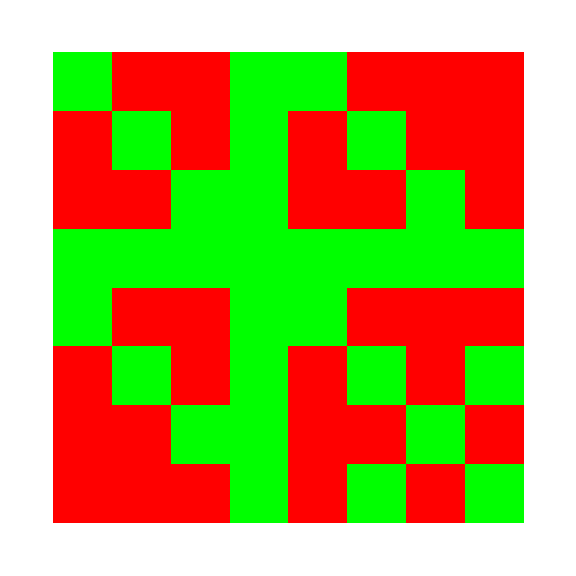

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x30tabzSKA[[1]],CovMatrix30x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_multi_50x30_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Table[MultiSplitCovMatrixzSKA[[i]] == Transpose[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[i]] ], {i,ktot}]
```

{False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[1,1,500]]
```

-5.39858×10^-7

```mathematica
MultiSplitCovMatrixzSKA[[1,500,1]]
```

-5.39858×10^-7

```mathematica
InvMultiSplitCovMatrixzSKA=ParallelTable[Inverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.62361×10^-6,2.27759×10^-6,1.92102×10^-6,1.59849×10^-6,1.32181×10^-6,1.09012×10^-6,8.98368×10^-7,7.40569×10^-7,6.11106×10^-7,5.05103×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
Table[InvMultiSplitCovMatrixzSKA[[i]] == Transpose[InvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvMultiSplitCovMatrixzSKA[[1,1,501]]
```

6.64852×10^6

```mathematica
InvMultiSplitCovMatrixzSKA[[1,501,1]]
```

6.64852×10^6

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=MultiSplitCovMatrixzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{True,True,True,True},{{},{},{},{}}}

```mathematica
MultiSplitCovMatrixzSKA[[1,1;;36,325;;360]] == Transpose[MultiSplitCovMatrixzSKA[[1,325;;360,1;;36]]]
```

True

```mathematica
lambdas=Table[Eigenvalues[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}];
```

```mathematica
Dimensions[lambdas[[2]]]
```

{576}

```mathematica
tolerance=1e-20;(*Adjust the tolerance as needed*)
zerolambdas=Select[lambdas[[2]],Abs[#]<tolerance&];
```

```mathematica
zerolambdas
```

{}

```mathematica
Table[PositiveDefiniteMatrixQ[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
PseudoInvMultiSplitCovMatrixzSKA=ParallelTable[PseudoInverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
Table[PseudoInvMultiSplitCovMatrixzSKA[[i]] == Transpose[PseudoInvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
RandomReal[]*10^(-10)
```

8.91164×10^-11

```mathematica
Dimensions[MultiSplitCovMatrixzSKA[[1]]]
```

{576,576}

```mathematica
matrix=MultiSplitCovMatrixzSKA[[1]];
{minValue,{a,b}}=MinimalBy[Flatten[Table[{matrix[[i,j]],{i,j}},{i,Length[matrix]},{j,Length[matrix]}],1],First][[1]]
```

{-4.72568×10^-6,{1,438}}

```mathematica
RandomReal[]*minValue*10^(-2)
```

-2.86948×10^-8

```mathematica
minValue+RandomReal[]*minValue*10^(-2)
```

-4.77093×10^-6

```mathematica
minValue(1+RandomReal[]*10^(-3))
```

-4.73025×10^-6

```mathematica
sizes=Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
nMatrices=sizes[[1]];(*Number of matrices in your array*)
matrixSize=sizes[[2]];(*Size of each matrix*)
scalingFactor=1*^-4;(*Adjust this factor for the desired scaling*)
RandMultiSplitCovMatrixzSKA=ConstantArray[{},nMatrices]; (*Define a new array*)
(*Loop through each matrix in your array*)
Do[
(*Extract the current matrix from your array*)
currentMatrix=MultiSplitCovMatrixzSKA[[i]];
(*Find the minimum value in the current matrix*)
minVal=Min[Select[Abs[Flatten[currentMatrix]],#!=0&]];
(*Generate a random symmetric matrix with the same dimensions as the current matrix*)randomSymmetricMatrix=Table[RandomReal[{-1,1}]*minVal*scalingFactor,{j,matrixSize},{k,matrixSize}];
  randomSymmetricMatrix=0.5*(randomSymmetricMatrix+Transpose[randomSymmetricMatrix]);
(*Subtract the diagonal elements to ensure they remain zero*)
randomMatrix=randomSymmetricMatrix-DiagonalMatrix[Diagonal[randomSymmetricMatrix]];
(*Add the random matrix to the current matrix*)
modifiedMatrix=currentMatrix+randomMatrix;
(*Replace the current matrix in your array with the modified matrix*)
RandMultiSplitCovMatrixzSKA[[i]]=modifiedMatrix,{i,nMatrices}]
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
differences=MapThread[Not@*Equal,{RandMultiSplitCovMatrixzSKA[[1]],Transpose[RandMultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
Min[Abs[MultiSplitCovMatrixzSKA[[1]]]]
```

0.

```mathematica
Table[Min[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{-4.72568×10^-6,-1.95049×10^-6,-1.11108×10^-6,-7.41954×10^-7,-5.44847×10^-7,-4.26545×10^-7,-3.49942×10^-7,-2.97747×10^-7,-2.66296×10^-7,-2.62055×10^-7,-2.728×10^-7,-3.01784×10^-7,-3.58175×10^-7,-4.57202×10^-7,-6.24219×10^-7,-9.0173×10^-7,-1.36911×10^-6,-2.18576×10^-6,-3.64406×10^-6}

```mathematica
findMin[matrix_List]:=Module[{min=Infinity},Do[If[NumericQ[matrix[[i,j]]]&&matrix[[i,j]]<min,min=matrix[[i,j]]],{i,Length[matrix]},{j,Length[matrix[[1]]]}];
min]

minValue=findMin[MultiSplitCovMatrixzSKA[[1]]]
```

-4.72568×10^-6

```mathematica
Table[Min[Select[Abs[Flatten[MultiSplitCovMatrixzSKA[[i]]]],#!=0&]],{i,ktot}]
```

{5.62015×10^-14,2.7107×10^-14,1.75201×10^-14,4.74771×10^-16,1.03629×10^-14,8.69507×10^-15,7.5508×10^-15,6.7297×10^-15,6.1236×10^-15,5.66908×10^-15,5.32651×10^-15,5.06994×10^-15,4.88171×10^-15,4.74955×10^-15,4.66475×10^-15,4.62111×10^-15,4.61424×10^-15,4.64109×10^-15,4.69968×10^-15}

```mathematica
5.6201481107886695*^-14 * (1+scalingFactor)
```

5.62071×10^-14

```mathematica
minVal
```

4.69968×10^-15

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]
```

3.07546×10^-7

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]*(1+minVal*scalingFactor)
```

3.07546×10^-7

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
RandMultiSplitCovMatrixzSKAsym = Table[(RandMultiSplitCovMatrixzSKA[[i]]+Transpose[RandMultiSplitCovMatrixzSKA[[i]]])/2,{i,ktot}];
```

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[Diagonal[RandMultiSplitCovMatrixzSKAsym[[i]]]==Diagonal[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[RandMultiSplitCovMatrixzSKAsym[[i,1,All]]==MultiSplitCovMatrixzSKA[[i,1,All]],{i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvRandMultiSplitCovMatrixzSKA=Table[Inverse[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000114219,9.91834×10^-6,8.36709×10^-6,6.96316×10^-6,5.75841×10^-6,4.74937×10^-6,3.91412×10^-6,3.22673×10^-6,2.66273×10^-6,2.20091×10^-6,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.77379×10^-6,1.5367×10^-6,1.29431×10^-6,1.07602×10^-6,8.8921×10^-7,7.33006×10^-7,6.0385×10^-7,4.97641×10^-7,4.10547×10^-7,3.39263×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
InvRandMultiSplitCovMatrixzSKAsym=Table[Inverse[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000114219,9.91834×10^-6,8.36709×10^-6,6.96316×10^-6,5.75841×10^-6,4.74937×10^-6,3.91412×10^-6,3.22673×10^-6,2.66273×10^-6,2.20091×10^-6,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.77379×10^-6,1.5367×10^-6,1.29431×10^-6,1.07602×10^-6,8.8921×10^-7,7.33006×10^-7,6.0385×10^-7,4.97641×10^-7,4.10547×10^-7,3.39263×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_multi_50x30_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",RandMultiSplitCovMatrixzSKAsym[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

## 50-50 and 10-90 splits

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix10Bx90FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-10B_90F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x10tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix10x50tabzSKA[[i]], CovMatrix10Bx90FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix10Bx90FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x10tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix10x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x10tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix10x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x10tabzSKA[[i]] ==CovMatrix10x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x10tabzSKA[[1]],CovMatrix10x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x10tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x10tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_multi_50x10_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Table[MultiSplitCovMatrixzSKA[[i]] == Transpose[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[i]] ], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False}

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[1,1,500]]
```

-7.01589×10^-7

```mathematica
MultiSplitCovMatrixzSKA[[1,500,1]]
```

-7.01589×10^-7

```mathematica
InvMultiSplitCovMatrixzSKA=ParallelTable[Inverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.62361×10^-6,2.27759×10^-6,1.92102×10^-6,1.59849×10^-6,1.32181×10^-6,1.09012×10^-6,8.98368×10^-7,7.40569×10^-7,6.11106×10^-7,5.05103×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.62742×10^-6,4.01861×10^-6,3.3903×10^-6,2.82155×10^-6,2.33343×10^-6,1.92459×10^-6,1.58615×10^-6,1.3076×10^-6,1.07906×10^-6,8.9192×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
Table[InvMultiSplitCovMatrixzSKA[[i]] == Transpose[InvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvMultiSplitCovMatrixzSKA[[1,1,501]]
```

-32158.6

```mathematica
InvMultiSplitCovMatrixzSKA[[1,501,1]]
```

-32158.6

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=MultiSplitCovMatrixzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{True,True,True,True},{{},{},{},{}}}

```mathematica
MultiSplitCovMatrixzSKA[[1,1;;36,325;;360]] == Transpose[MultiSplitCovMatrixzSKA[[1,325;;360,1;;36]]]
```

True

```mathematica
lambdas=Table[Eigenvalues[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}];
```

```mathematica
Dimensions[lambdas[[2]]]
```

{576}

```mathematica
tolerance=1e-20;(*Adjust the tolerance as needed*)
zerolambdas=Select[lambdas[[2]],Abs[#]<tolerance&];
```

```mathematica
zerolambdas
```

{}

```mathematica
Table[PositiveDefiniteMatrixQ[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
PseudoInvMultiSplitCovMatrixzSKA=ParallelTable[PseudoInverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
Table[PseudoInvMultiSplitCovMatrixzSKA[[i]] == Transpose[PseudoInvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
RandomReal[]*10^(-10)
```

7.65871×10^-11

```mathematica
Dimensions[MultiSplitCovMatrixzSKA[[1]]]
```

{576,576}

```mathematica
matrix=MultiSplitCovMatrixzSKA[[1]];
{minValue,{a,b}}=MinimalBy[Flatten[Table[{matrix[[i,j]],{i,j}},{i,Length[matrix]},{j,Length[matrix]}],1],First][[1]]
```

{-8.19465×10^-6,{289,438}}

```mathematica
RandomReal[]*minValue*10^(-2)
```

-6.86525×10^-9

```mathematica
minValue+RandomReal[]*minValue*10^(-2)
```

-8.27262×10^-6

```mathematica
minValue(1+RandomReal[]*10^(-3))
```

-8.20237×10^-6

```mathematica
sizes=Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
nMatrices=sizes[[1]];(*Number of matrices in your array*)
matrixSize=sizes[[2]];(*Size of each matrix*)
scalingFactor=1*^-4;(*Adjust this factor for the desired scaling*)
RandMultiSplitCovMatrixzSKA=ConstantArray[{},nMatrices]; (*Define a new array*)
(*Loop through each matrix in your array*)
Do[
(*Extract the current matrix from your array*)
currentMatrix=MultiSplitCovMatrixzSKA[[i]];
(*Find the minimum value in the current matrix*)
minVal=Min[Select[Abs[Flatten[currentMatrix]],#!=0&]];
(*Generate a random symmetric matrix with the same dimensions as the current matrix*)randomSymmetricMatrix=Table[RandomReal[{-1,1}]*minVal*scalingFactor,{j,matrixSize},{k,matrixSize}];
  randomSymmetricMatrix=0.5*(randomSymmetricMatrix+Transpose[randomSymmetricMatrix]);
(*Subtract the diagonal elements to ensure they remain zero*)
randomMatrix=randomSymmetricMatrix-DiagonalMatrix[Diagonal[randomSymmetricMatrix]];
(*Add the random matrix to the current matrix*)
modifiedMatrix=currentMatrix+randomMatrix;
(*Replace the current matrix in your array with the modified matrix*)
RandMultiSplitCovMatrixzSKA[[i]]=modifiedMatrix,{i,nMatrices}]
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
differences=MapThread[Not@*Equal,{RandMultiSplitCovMatrixzSKA[[1]],Transpose[RandMultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
Min[Abs[MultiSplitCovMatrixzSKA[[1]]]]
```

0.

```mathematica
Table[Min[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{-8.19465×10^-6,-3.30686×10^-6,-1.84679×10^-6,-1.21278×10^-6,-8.79101×10^-7,-6.82425×10^-7,-5.58678×10^-7,-4.78517×10^-7,-4.27677×10^-7,-3.99466×10^-7,-3.93821×10^-7,-4.11378×10^-7,-4.58075×10^-7,-5.48451×10^-7,-7.12743×10^-7,-9.89034×10^-7,-1.45573×10^-6,-2.27026×10^-6,-3.71997×10^-6}

```mathematica
findMin[matrix_List]:=Module[{min=Infinity},Do[If[NumericQ[matrix[[i,j]]]&&matrix[[i,j]]<min,min=matrix[[i,j]]],{i,Length[matrix]},{j,Length[matrix[[1]]]}];
min]

minValue=findMin[MultiSplitCovMatrixzSKA[[1]]]
```

-8.19465×10^-6

```mathematica
Table[Min[Select[Abs[Flatten[MultiSplitCovMatrixzSKA[[i]]]],#!=0&]],{i,ktot}]
```

{5.62015×10^-14,2.7107×10^-14,1.75201×10^-14,1.29694×10^-14,1.03629×10^-14,8.69507×10^-15,7.5508×10^-15,6.7297×10^-15,6.1236×10^-15,5.66908×10^-15,5.32651×10^-15,5.06994×10^-15,4.88171×10^-15,4.74955×10^-15,4.66475×10^-15,4.62111×10^-15,4.61424×10^-15,4.64109×10^-15,4.69968×10^-15}

```mathematica
5.6201481107886695*^-14 * (1+scalingFactor)
```

5.62071×10^-14

```mathematica
minVal
```

4.69968×10^-15

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]
```

3.07546×10^-7

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]*(1+minVal*scalingFactor)
```

3.07546×10^-7

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False}

```mathematica
RandMultiSplitCovMatrixzSKAsym = Table[(RandMultiSplitCovMatrixzSKA[[i]]+Transpose[RandMultiSplitCovMatrixzSKA[[i]]])/2,{i,ktot}];
```

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[Diagonal[RandMultiSplitCovMatrixzSKAsym[[i]]]==Diagonal[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[RandMultiSplitCovMatrixzSKAsym[[i,1,All]]==MultiSplitCovMatrixzSKA[[i,1,All]],{i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvRandMultiSplitCovMatrixzSKA=Table[Inverse[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.62742×10^-6,4.01861×10^-6,3.3903×10^-6,2.82155×10^-6,2.33343×10^-6,1.92459×10^-6,1.58615×10^-6,1.3076×10^-6,1.07906×10^-6,8.9192×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.62361×10^-6,2.27759×10^-6,1.92102×10^-6,1.59849×10^-6,1.32181×10^-6,1.09012×10^-6,8.98368×10^-7,7.40569×10^-7,6.11106×10^-7,5.05103×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
InvRandMultiSplitCovMatrixzSKAsym=Table[Inverse[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.62742×10^-6,4.01861×10^-6,3.3903×10^-6,2.82155×10^-6,2.33343×10^-6,1.92459×10^-6,1.58615×10^-6,1.3076×10^-6,1.07906×10^-6,8.9192×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.62361×10^-6,2.27759×10^-6,1.92102×10^-6,1.59849×10^-6,1.32181×10^-6,1.09012×10^-6,8.98368×10^-7,7.40569×10^-7,6.11106×10^-7,5.05103×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_multi_50x10_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",RandMultiSplitCovMatrixzSKAsym[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

# Multi-SPLIT Covariance + Octupole

## Covariance Blocks

## Parameters

### Galaxy bias

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_,dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_,dbz_]:=bmeanzSKA-dbz/m;
bT[m_,dbz_]:=bmeanzSKA ;
```

#### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA50=bB[2, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA50=bF[2, dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bTzSKA50 = bT[2,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

#### Bright

```mathematica
nBSKA50 = 1/2;
```

```mathematica
smodelBzSKA50 = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA50 = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

#### Faint

```mathematica
nFSKA50 = 1/2;
```

```mathematica
smodelzSKA50 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA50);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA50 = (m/(m-1)) smodelzSKA50 -(1/(m-1)) smodelBzSKA50
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA50 = List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

#### Splitting with 30% Bright (m=10/3)

```mathematica
m=10/3;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA30=bB[10/3,dbz]
```

{1.32304,1.37379,1.42867,1.48801,1.55219,1.6216,1.69666,1.77784,1.86563,1.96056,2.06323,2.17426,2.29434,2.42419,2.56462,2.71649,2.88073,3.05834,3.25042}

```mathematica
bFzSKA30=bF[10/3,dbz]
```

{0.323042,0.373787,0.428665,0.488013,0.552194,0.621603,0.696665,0.77784,0.865627,0.960564,1.06323,1.17426,1.29434,1.42419,1.56462,1.71649,1.88073,2.05834,2.25042}

```mathematica
bTzSKA30 = bT[10/3,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

#### Bright

```mathematica
nBSKA30 = 3/10;
```

```mathematica
smodelBzSKA30 = List[0.63665525,0.42367658,0.50881959,0.60522562,0.67778459,0.73405886,0.78698648,0.85067709,0.92313678,1.00034598,1.07877756,1.15621473,1.23564294,1.31904933,1.40610202,1.49646092,1.58855833,1.68141612,1.77443344];
```

```mathematica
fevolBzSKA30 = List[-2.35710791,0.50267603,0.00895782,-0.59492009,-0.49505863,-0.16404253,0.19264397,0.36952203,0.43853907,0.45440814,0.4833308,0.54007682,0.59932034,0.6323595,0.65280044,0.66681915,0.69110994,0.7429895,0.81482988];
```

#### Faint

```mathematica
nFSKA30 = 7/10;
```

```mathematica
smodelzSKA30 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA30);]
m
```

10/3

```mathematica
smodelFzSKA30 = (m/(m-1)) smodelzSKA30 -(1/(m-1)) smodelBzSKA30
```

{-0.128184,0.0583469,0.133246,0.226934,0.34323,0.467545,0.587359,0.69865,0.803523,0.904826,1.00684,1.11062,1.21737,1.32493,1.43485,1.54726,1.6627,1.78189,1.90084}

```mathematica
fevolFzSKA30 = List[4.22894971,3.22955823,2.61765473,1.95918753,0.94948372,0.01885715,-0.72267224,-1.22839524,-1.57209693,-1.82896117,-2.03473879,-2.22488036,-2.39749383,-2.54686948,-2.68379003,-2.81081826,-2.93482756,-3.05441667,-3.14524578];
```

#### Splitting with 10% Bright (m=10)

```mathematica
m=10;
```

```mathematica
bBzSKA10=bB[10, dbz]
```

{1.52304,1.57379,1.62867,1.68801,1.75219,1.8216,1.89666,1.97784,2.06563,2.16056,2.26323,2.37426,2.49434,2.62419,2.76462,2.91649,3.08073,3.25834,3.45042}

```mathematica
bFzSKA10=bF[10,dbz]
```

{0.523042,0.573787,0.628665,0.688013,0.752194,0.821603,0.896665,0.97784,1.06563,1.16056,1.26323,1.37426,1.49434,1.62419,1.76462,1.91649,2.08073,2.25834,2.45042}

```mathematica
bTzSKA10 = bT[10,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

#### Bright

```mathematica
nBSKA10 = 1/10;
```

```mathematica
smodelBzSKA10 = List[1.03913831,0.71999785,0.70016622,0.80291617,0.80509085,0.86385634,0.93133131,0.99350429,1.04896737,1.0983242,1.14410701,1.18703114,1.23676623,1.29877001,1.36750798,1.44075302,1.51593195,1.59199958,1.66844103];
```

```mathematica
fevolBzSKA10 =List[-24.023626,1.236314,-1.688862,-1.231461,-0.256573,-0.015632,0.066406,0.271551,0.571797,0.941879,1.356481,1.796966,2.166868,2.409665,2.598081,2.759553,2.921841,3.102200,3.295148];
```

#### Faint

```mathematica
nFSKA10 = 9/10;
```

```mathematica
smodelzSKA10 =List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA10);]
m
```

10

```mathematica
smodelFzSKA10 = (m/(m-1)) smodelzSKA10 -(1/(m-1)) smodelBzSKA10
```

{-0.00294009,0.106607,0.195446,0.289033,0.403431,0.512349,0.615682,0.716564,0.816123,0.915166,1.01556,1.11733,1.2213,1.32587,1.43275,1.54216,1.6543,1.7695,1.88453}

```mathematica
fevolFzSKA10 = List[5.17277222,2.54206913,2.22659099,1.46233479,0.60197595,-0.03827728,-0.50524214,-0.86241689,-1.14009535,-1.37570916,-1.57218441,-1.75009982,-1.90570711,-2.03785252,-2.15846779,-2.27053596,-2.37692272,-2.47268313,-2.54081985];
```

### Survey

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
nBzSKA50=Table[nBSKA50, {i,Length[zSKA]}];
nFzSKA50=Table[nFSKA50, {i,Length[zSKA]}];
nBzSKA30=Table[nBSKA30, {i,Length[zSKA]}];
nFzSKA30=Table[nFSKA30, {i,Length[zSKA]}];
nBzSKA10=Table[nBSKA10, {i,Length[zSKA]}];
nFzSKA10=Table[nFSKA10, {i,Length[zSKA]}];
```

```mathematica
nBzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nBzSKA30
```

{3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10}

```mathematica
nFzSKA30
```

{7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10}

```mathematica
nBzSKA10
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

```mathematica
nFzSKA10
```

{9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10}

```mathematica
NbarBzSKA50=NbarzSKA*nBzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarFzSKA50=NbarzSKA*nFzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarBzSKA30=NbarzSKA*nBzSKA30
```

{0.0600505,0.0351586,0.0209208,0.0126881,0.00781626,0.00494933,0.00316718,0.00204366,0.00131724,0.000842645,0.000538518,0.000341901,0.00021502,0.000134629,0.0000828116,0.000050365,0.000030219,0.0000177246,0.0000101699}

```mathematica
NbarFzSKA30=NbarzSKA*nFzSKA30
```

{0.140118,0.0820368,0.0488153,0.0296056,0.0182379,0.0115484,0.00739009,0.00476853,0.00307355,0.00196617,0.00125654,0.000797768,0.000501713,0.000314135,0.000193227,0.000117518,0.000070511,0.0000413574,0.0000237297}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50/nBzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffFSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA50/nFzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffBSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA30/nBzSKA30
```

{2.9008×10^-8,1.81879×10^-8,1.57546×10^-8,1.58995×10^-8,1.75318×10^-8,2.01724×10^-8,2.41537×10^-8,2.97893×10^-8,3.78812×10^-8,4.9692×10^-8,6.65124×10^-8,9.10478×10^-8,1.2751×10^-7,1.81406×10^-7,2.65268×10^-7,3.95622×10^-7,6.0248×10^-7,9.44614×10^-7,1.52263×10^-6}

```mathematica
coeffFSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA30/nFzSKA30
```

{1.2432×10^-8,7.79481×10^-9,6.75196×10^-9,6.81408×10^-9,7.51364×10^-9,8.64533×10^-9,1.03516×10^-8,1.27668×10^-8,1.62348×10^-8,2.12966×10^-8,2.85053×10^-8,3.90205×10^-8,5.46473×10^-8,7.77456×10^-8,1.13686×10^-7,1.69552×10^-7,2.58206×10^-7,4.04834×10^-7,6.52554×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA50=(5smodelBzSKA50 +(2-5smodelBzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA50)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA50=(5smodelFzSKA50 +(2-5smodelFzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA50)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
cBzSKA30=(5smodelBzSKA30 +(2-5smodelBzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA30)fzSKA
```

{-1.70391,0.895284,0.592824,0.630427,0.480152,0.279389,0.0786685,0.00333885,0.0248213,0.116481,0.226818,0.340321,0.472092,0.646354,0.851276,1.08106,1.31899,1.54657,1.7686}

```mathematica
cFzSKA30=(5smodelFzSKA30 +(2-5smodelFzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA30)fzSKA
```

{9.13213,3.51792,2.0517,1.29866,1.16499,1.29248,1.54051,1.79292,2.04051,2.30254,2.58099,2.8947,3.23377,3.58883,3.964,4.35837,4.77599,5.21419,5.6457}

```mathematica
cBzSKA10=(5smodelBzSKA10 +(2-5smodelBzSKA10)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA10)fzSKA
```

{3.67453,-3.17161,0.108577,-0.235995,-0.390502,-0.404636,-0.326334,-0.320991,-0.377903,-0.489366,-0.644756,-0.830882,-0.966863,-0.992326,-0.961212,-0.894509,-0.817281,-0.746799,-0.679258}

```mathematica
cFzSKA10=(5smodelFzSKA10 +(2-5smodelFzSKA10)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA10)fzSKA
```

{6.12652,3.38699,1.78131,1.24643,1.10954,1.14335,1.26066,1.43127,1.63733,1.88406,2.15468,2.4572,2.77995,3.11702,3.47367,3.84958,4.24514,4.65398,5.05611}

### Elements

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
G[1,3,3,3]
```

24/385

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2corrCC[n,m]coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

80

```mathematica
4 i /. i -> 43
```

80

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

Monopole 50  - Monopole 50

```mathematica
coeffvarCCpop50pop30BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{6.72059×10^-9,2.68893×10^-9,1.5043×10^-9,9.97102×10^-10,7.33217×10^-10,5.79059×10^-10,4.82255×10^-10,4.18793×10^-10,3.76407×10^-10,3.48329×10^-10,3.30631×10^-10,3.20969×10^-10,3.17947×10^-10,3.20787×10^-10,3.29141×10^-10,3.42989×10^-10,3.62591×10^-10,3.88472×10^-10,4.21424×10^-10}

```mathematica
coeffvarCCpop30pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{6.72059×10^-9,2.68893×10^-9,1.5043×10^-9,9.97102×10^-10,7.33217×10^-10,5.79059×10^-10,4.82255×10^-10,4.18793×10^-10,3.76407×10^-10,3.48329×10^-10,3.30631×10^-10,3.20969×10^-10,3.17947×10^-10,3.20787×10^-10,3.29141×10^-10,3.42989×10^-10,3.62591×10^-10,3.88472×10^-10,4.21424×10^-10}

```mathematica
coeffvarCCpop50pop30FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.09211×10^-10,6.02524×10^-11,4.42022×10^-11,3.70183×10^-11,3.34488×10^-11,3.17813×10^-11,3.13304×10^-11,3.17973×10^-11,3.30598×10^-11,3.5092×10^-11,3.79318×10^-11,4.16683×10^-11,4.64387×10^-11,5.24323×10^-11,5.98978×10^-11,6.91559×10^-11,8.0616×10^-11,9.47977×10^-11,1.1236×10^-10}

```mathematica
coeffvarCCpop30pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.09211×10^-10,6.02524×10^-11,4.42022×10^-11,3.70183×10^-11,3.34488×10^-11,3.17813×10^-11,3.13304×10^-11,3.17973×10^-11,3.30598×10^-11,3.5092×10^-11,3.79318×10^-11,4.16683×10^-11,4.64387×10^-11,5.24323×10^-11,5.98978×10^-11,6.91559×10^-11,8.0616×10^-11,9.47977×10^-11,1.1236×10^-10}

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCCpop50pop30BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCCpop30pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCCpop50pop30FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCCpop30pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

```mathematica
varCCMONOBrightLp4d4to172zSKA[[1,1+4,1+4]]
```

0.0000194438

```mathematica
a[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]]
```

0.0000113914

```mathematica
b[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]]
```

0.0000194438

```mathematica
Sqrt[b[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]] a[[1]] varcosmicMONOzbaretab[[1,5+4,2+4]]]
```

0.0000148826

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA[[1,1+4,1+4]]
```

0.0000148736

```mathematica
coeffvarCCpop50pop10BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{8.50711×10^-9,3.36956×10^-9,1.86753×10^-9,1.22712×10^-9,8.94978×10^-10,7.01317×10^-10,5.79723×10^-10,4.99814×10^-10,4.46087×10^-10,4.09994×10^-10,3.86561×10^-10,3.72801×10^-10,3.6691×10^-10,3.67841×10^-10,3.75071×10^-10,3.88464×10^-10,4.0821×10^-10,4.3479×10^-10,4.68981×10^-10}

```mathematica
coeffvarCCpop10pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bBzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{8.50711×10^-9,3.36956×10^-9,1.86753×10^-9,1.22712×10^-9,8.94978×10^-10,7.01317×10^-10,5.79723×10^-10,4.99814×10^-10,4.46087×10^-10,4.09994×10^-10,3.86561×10^-10,3.72801×10^-10,3.6691×10^-10,3.67841×10^-10,3.75071×10^-10,3.88464×10^-10,4.0821×10^-10,4.3479×10^-10,4.68981×10^-10}

```mathematica
coeffvarCCpop50pop10FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{1.7609×10^-10,9.3476×10^-11,6.63875×10^-11,5.4069×10^-11,4.7673×10^-11,4.43125×10^-11,4.28177×10^-11,4.26579×10^-11,4.3589×10^-11,4.55173×10^-11,4.84427×10^-11,5.24337×10^-11,5.76187×10^-11,6.41867×10^-11,7.23928×10^-11,8.257×10^-11,9.51453×10^-11,1.10662×10^-10,1.2981×10^-10}

```mathematica
coeffvarCCpop10pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{1.7609×10^-10,9.3476×10^-11,6.63875×10^-11,5.4069×10^-11,4.7673×10^-11,4.43125×10^-11,4.28177×10^-11,4.26579×10^-11,4.3589×10^-11,4.55173×10^-11,4.84427×10^-11,5.24337×10^-11,5.76187×10^-11,6.41867×10^-11,7.23928×10^-11,8.257×10^-11,9.51453×10^-11,1.10662×10^-10,1.2981×10^-10}

```mathematica
varCCMONO50Bx10BLp4d4to172zSKA=Table[coeffvarCCpop50pop10BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10Bx50BLp4d4to172zSKA=Table[coeffvarCCpop10pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx10FLp4d4to172zSKA=Table[coeffvarCCpop50pop10FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO10Fx50FLp4d4to172zSKA=Table[coeffvarCCpop10pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

```mathematica
coeffvarCCpop50BFpop30BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{7.66939×10^-10,3.67626×10^-10,2.39273×10^-10,1.80579×10^-10,1.48771×10^-10,1.30024×10^-10,1.18698×10^-10,1.12138×10^-10,1.08976×10^-10,1.08486×10^-10,1.10292×10^-10,1.14242×10^-10,1.20335×10^-10,1.28695×10^-10,1.39561×10^-10,1.53283×10^-10,1.70339×10^-10,1.91353×10^-10,2.17123×10^-10}

```mathematica
coeffvarCCpop30BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{7.66939×10^-10,3.67626×10^-10,2.39273×10^-10,1.80579×10^-10,1.48771×10^-10,1.30024×10^-10,1.18698×10^-10,1.12138×10^-10,1.08976×10^-10,1.08486×10^-10,1.10292×10^-10,1.14242×10^-10,1.20335×10^-10,1.28695×10^-10,1.39561×10^-10,1.53283×10^-10,1.70339×10^-10,1.91353×10^-10,2.17123×10^-10}

```mathematica
varCCMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50BFpop10BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{1.11313×10^-9,5.19598×10^-10,3.30513×10^-10,2.44463×10^-10,1.97814×10^-10,1.70094×10^-10,1.52972×10^-10,1.42521×10^-10,1.36707×10^-10,1.34423×10^-10,1.35069×10^-10,1.38352×10^-10,1.44183×10^-10,1.52633×10^-10,1.63911×10^-10,1.78352×10^-10,1.96435×10^-10,2.18794×10^-10,2.46249×10^-10}

```mathematica
coeffvarCCpop10BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{1.11313×10^-9,5.19598×10^-10,3.30513×10^-10,2.44463×10^-10,1.97814×10^-10,1.70094×10^-10,1.52972×10^-10,1.42521×10^-10,1.36707×10^-10,1.34423×10^-10,1.35069×10^-10,1.38352×10^-10,1.44183×10^-10,1.52633×10^-10,1.63911×10^-10,1.78352×10^-10,1.96435×10^-10,2.18794×10^-10,2.46249×10^-10}

```mathematica
varCCMONO50BFx10BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop10BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop10BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole 1 pop - Monopole 2 pop

```mathematica
coeffvarCC50B30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.52066×10^-9,1.08461×10^-9,6.45996×10^-10,4.52332×10^-10,3.4926×10^-10,2.8826×10^-10,2.49955×10^-10,2.2532×10^-10,2.09701×10^-10,2.00528×10^-10,1.96335×10^-10,1.96292×10^-10,1.99969×10^-10,2.07217×10^-10,2.18099×10^-10,2.32867×10^-10,2.51948×10^-10,2.7596×10^-10,3.05729×10^-10}

```mathematica
coeffvarCC30BF50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.52066×10^-9,1.08461×10^-9,6.45996×10^-10,4.52332×10^-10,3.4926×10^-10,2.8826×10^-10,2.49955×10^-10,2.2532×10^-10,2.09701×10^-10,2.00528×10^-10,1.96335×10^-10,1.96292×10^-10,1.99969×10^-10,2.07217×10^-10,2.18099×10^-10,2.32867×10^-10,2.51948×10^-10,2.7596×10^-10,3.05729×10^-10}

```mathematica
coeffvarCC50F30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.55708×10^-10,1.33822×10^-10,9.37831×10^-11,7.543×10^-11,6.57208×10^-11,6.03945×10^-11,5.77138×10^-11,5.68768×10^-11,5.74974×10^-11,5.94039×10^-11,6.25534×10^-11,6.69929×10^-11,7.28441×10^-11,8.02996×10^-11,8.96268×10^-11,1.01179×10^-10,1.15412×10^-10,1.32905×10^-10,1.54391×10^-10}

```mathematica
coeffvarCC30B50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.9091×10^-9,8.62776×10^-10,5.33102×10^-10,3.84077×10^-10,3.03392×10^-10,2.5512×10^-10,2.24694×10^-10,2.05247×10^-10,1.93205×10^-10,1.86589×10^-10,1.84272×10^-10,1.85635×10^-10,1.90383×10^-10,1.98454×10^-10,2.09973×10^-10,2.25232×10^-10,2.4469×10^-10,2.68984×10^-10,2.98957×10^-10}

```mathematica
coeffvarCC50BF30B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.9091×10^-9,8.62776×10^-10,5.33102×10^-10,3.84077×10^-10,3.03392×10^-10,2.5512×10^-10,2.24694×10^-10,2.05247×10^-10,1.93205×10^-10,1.86589×10^-10,1.84272×10^-10,1.85635×10^-10,1.90383×10^-10,1.98454×10^-10,2.09973×10^-10,2.25232×10^-10,2.4469×10^-10,2.68984×10^-10,2.98957×10^-10}

```mathematica
coeffvarCC30F50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{3.16497×10^-10,1.60527×10^-10,1.09768×10^-10,8.65529×10^-11,7.41838×10^-11,6.72305×10^-11,6.34806×10^-11,6.1907×10^-11,6.20043×10^-11,6.35323×10^-11,6.64063×10^-11,7.0647×10^-11,7.63584×10^-11,8.3721×10^-11,9.29943×10^-11,1.04526×10^-10,1.18767×10^-10,1.36295×10^-10,1.57842×10^-10}

```mathematica
coeffvarCC50BF30F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.16497×10^-10,1.60527×10^-10,1.09768×10^-10,8.65529×10^-11,7.41838×10^-11,6.72305×10^-11,6.34806×10^-11,6.1907×10^-11,6.20043×10^-11,6.35323×10^-11,6.64063×10^-11,7.0647×10^-11,7.63584×10^-11,8.3721×10^-11,9.29943×10^-11,1.04526×10^-10,1.18767×10^-10,1.36295×10^-10,1.57842×10^-10}

```mathematica
varCCMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50B30BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BF50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30B50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BF30B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx30BFLp4d4to172zSKA= Table[coeffvarCC50F30BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BFLp4d4to172zSKA= Table[coeffvarCC30F50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{9.84152×10^-10,4.52607×10^-10,2.85476×10^-10,2.102×10^-10,1.69754×10^-10,1.45931×10^-10,1.31371×10^-10,1.2263×10^-10,1.17935×10^-10,1.16334×10^-10,1.17319×10^-10,1.20651×10^-10,1.26278×10^-10,1.34287×10^-10,1.4489×10^-10,1.58421×10^-10,1.75345×10^-10,1.96278×10^-10,2.22011×10^-10}

```mathematica
coeffvarCCpop30Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{9.84152×10^-10,4.52607×10^-10,2.85476×10^-10,2.102×10^-10,1.69754×10^-10,1.45931×10^-10,1.31371×10^-10,1.2263×10^-10,1.17935×10^-10,1.16334×10^-10,1.17319×10^-10,1.20651×10^-10,1.26278×10^-10,1.34287×10^-10,1.4489×10^-10,1.58421×10^-10,1.75345×10^-10,1.96278×10^-10,2.22011×10^-10}

```mathematica
coeffvarCCpop50Fpop30BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{6.09206×10^-10,3.02289×10^-10,2.02188×10^-10,1.55992×10^-10,1.30878×10^-10,1.16157×10^-10,1.07446×10^-10,1.02676×10^-10,1.00789×10^-10,1.01231×10^-10,1.03732×10^-10,1.08206×10^-10,1.14695×10^-10,1.23355×10^-10,1.34442×10^-10,1.48322×10^-10,1.65483×10^-10,1.86557×10^-10,2.12348×10^-10}

```mathematica
coeffvarCCpop30Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{6.09206×10^-10,3.02289×10^-10,2.02188×10^-10,1.55992×10^-10,1.30878×10^-10,1.16157×10^-10,1.07446×10^-10,1.02676×10^-10,1.00789×10^-10,1.01231×10^-10,1.03732×10^-10,1.08206×10^-10,1.14695×10^-10,1.23355×10^-10,1.34442×10^-10,1.48322×10^-10,1.65483×10^-10,1.86557×10^-10,2.12348×10^-10}

```mathematica
varCCMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop30FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCCpop30Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCCpop30Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop30BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCC50B10BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{3.77448×10^-9,1.57077×10^-9,9.09672×10^-10,6.21817×10^-10,4.7013×10^-10,3.80825×10^-10,3.2468×10^-10,2.88184×10^-10,2.64393×10^-10,2.49472×10^-10,2.41209×10^-10,2.38317×10^-10,2.40074×10^-10,2.46142×10^-10,2.56463×10^-10,2.71207×10^-10,2.90759×10^-10,3.15712×10^-10,3.46891×10^-10}

```mathematica
coeffvarCC10BF50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{3.77448×10^-9,1.57077×10^-9,9.09672×10^-10,6.21817×10^-10,4.7013×10^-10,3.80825×10^-10,3.2468×10^-10,2.88184×10^-10,2.64393×10^-10,2.49472×10^-10,2.41209×10^-10,2.38317×10^-10,2.40074×10^-10,2.46142×10^-10,2.56463×10^-10,2.71207×10^-10,2.90759×10^-10,3.15712×10^-10,3.46891×10^-10}

```mathematica
coeffvarCC50F10BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{3.63987×10^-10,1.86025×10^-10,1.27733×10^-10,1.00911×10^-10,8.6522×10^-11,7.83556×10^-11,7.38707×10^-11,7.18813×10^-11,7.17973×10^-11,7.33323×10^-11,7.63758×10^-11,8.0936×10^-11,8.71133×10^-11,9.50916×10^-11,1.05139×10^-10,1.17617×10^-10,1.32996×10^-10,1.51878×10^-10,1.75026×10^-10}

```mathematica
coeffvarCC10B50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bBzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{2.39364×10^-9,1.07236×10^-9,6.57207×10^-10,4.69855×10^-10,3.68442×10^-10,3.07651×10^-10,2.69123×10^-10,2.44206×10^-10,2.28387×10^-10,2.19156×10^-10,2.15067×10^-10,2.15304×10^-10,2.19445×10^-10,2.27349×10^-10,2.39092×10^-10,2.5494×10^-10,2.75341×10^-10,3.00939×10^-10,3.32593×10^-10}

```mathematica
coeffvarCC50BF10B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{2.39364×10^-9,1.07236×10^-9,6.57207×10^-10,4.69855×10^-10,3.68442×10^-10,3.07651×10^-10,2.69123×10^-10,2.44206×10^-10,2.28387×10^-10,2.19156×10^-10,2.15067×10^-10,2.15304×10^-10,2.19445×10^-10,2.27349×10^-10,2.39092×10^-10,2.5494×10^-10,2.75341×10^-10,3.00939×10^-10,3.32593×10^-10}

```mathematica
coeffvarCC10F50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{5.24343×10^-10,2.54889×10^-10,1.68143×10^-10,1.28542×10^-10,1.0722×10^-10,9.48398×10^-11,8.75988×10^-11,8.37145×10^-11,8.22834×10^-11,8.28397×10^-11,8.51645×10^-11,8.91969×10^-11,9.49918×10^-11,1.02702×10^-10,1.12575×10^-10,1.24956×10^-10,1.40307×10^-10,1.59221×10^-10,1.82456×10^-10}

```mathematica
coeffvarCC50BF10F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{5.24343×10^-10,2.54889×10^-10,1.68143×10^-10,1.28542×10^-10,1.0722×10^-10,9.48398×10^-11,8.75988×10^-11,8.37145×10^-11,8.22834×10^-11,8.28397×10^-11,8.51645×10^-11,8.91969×10^-11,9.49918×10^-11,1.02702×10^-10,1.12575×10^-10,1.24956×10^-10,1.40307×10^-10,1.59221×10^-10,1.82456×10^-10}

```mathematica
varCCMONO50Bx10BFLp4d4to172zSKA=Table[coeffvarCC50B10BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10BFx50BLp4d4to172zSKA=Table[coeffvarCC10BF50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Bx50BFLp4d4to172zSKA=Table[coeffvarCC10B50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx10BLp4d4to172zSKA=Table[coeffvarCC50BF10B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx10BFLp4d4to172zSKA= Table[coeffvarCC50F10BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Fx50BFLp4d4to172zSKA= Table[coeffvarCC10F50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop10FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{1.70529×10^-9,7.44301×10^-10,4.49595×10^-10,3.19158×10^-10,2.49735×10^-10,2.08801×10^-10,1.83353×10^-10,1.67337×10^-10,1.57639×10^-10,1.52556×10^-10,1.51136×10^-10,1.52869×10^-10,1.57526×10^-10,1.65084×10^-10,1.75687×10^-10,1.89626×10^-10,2.07348×10^-10,2.29464×10^-10,2.56777×10^-10}

```mathematica
coeffvarCCpop10Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{1.70529×10^-9,7.44301×10^-10,4.49595×10^-10,3.19158×10^-10,2.49735×10^-10,2.08801×10^-10,1.83353×10^-10,1.67337×10^-10,1.57639×10^-10,1.52556×10^-10,1.51136×10^-10,1.52869×10^-10,1.57526×10^-10,1.65084×10^-10,1.75687×10^-10,1.89626×10^-10,2.07348×10^-10,2.29464×10^-10,2.56777×10^-10}

```mathematica
coeffvarCCpop50Fpop10BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{7.58885×10^-10,3.73472×10^-10,2.47903×10^-10,1.89903×10^-10,1.58256×10^-10,1.39547×10^-10,1.28272×10^-10,1.21824×10^-10,1.1886×10^-10,1.18662×10^-10,1.20866×10^-10,1.25327×10^-10,1.32054×10^-10,1.41184×10^-10,1.52971×10^-10,1.67784×10^-10,1.86123×10^-10,2.0864×10^-10,2.36168×10^-10}

```mathematica
coeffvarCCpop10Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA10,bBzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{7.58885×10^-10,3.73472×10^-10,2.47903×10^-10,1.89903×10^-10,1.58256×10^-10,1.39547×10^-10,1.28272×10^-10,1.21824×10^-10,1.1886×10^-10,1.18662×10^-10,1.20866×10^-10,1.25327×10^-10,1.32054×10^-10,1.41184×10^-10,1.52971×10^-10,1.67784×10^-10,1.86123×10^-10,2.0864×10^-10,2.36168×10^-10}

```mathematica
varCCMONO50Bx10FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop10FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Fx50BLp4d4to172zSKA=Table[coeffvarCCpop10Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO10Bx50FLp4d4to172zSKA=Table[coeffvarCCpop10Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx10BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop10BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
coeffvarCC50BF30BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{2.71337×10^-8,1.04827×10^-9,1.16807×10^-10,2.19256×10^-11,1.67946×10^-11,2.01453×10^-11,2.60048×10^-11,3.26189×10^-11,3.85232×10^-11,4.26373×10^-11,4.47052×10^-11,4.51715×10^-11,4.53569×10^-11,4.54151×10^-11,4.62936×10^-11,4.82208×10^-11,5.16678×10^-11,5.7115×10^-11,6.32392×10^-11}

```mathematica
coeffvarCC30BF50BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{2.71337×10^-8,1.04827×10^-9,1.16807×10^-10,2.19256×10^-11,1.67946×10^-11,2.01453×10^-11,2.60048×10^-11,3.26189×10^-11,3.85232×10^-11,4.26373×10^-11,4.47052×10^-11,4.51715×10^-11,4.53569×10^-11,4.54151×10^-11,4.62936×10^-11,4.82208×10^-11,5.16678×10^-11,5.7115×10^-11,6.32392×10^-11}

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCC50BF30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC30BF50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF10BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,cBzSKA50,cFzSKA50,cBzSKA10,cFzSKA10,fzSKA]
```

{1.32229×10^-8,1.87417×10^-9,1.25832×10^-10,3.38135×10^-11,2.68282×10^-11,2.65981×10^-11,2.75179×10^-11,3.21378×10^-11,3.85169×10^-11,4.52561×10^-11,5.07669×10^-11,5.45041×10^-11,5.7038×10^-11,5.8431×10^-11,6.05122×10^-11,6.38402×10^-11,6.90878×10^-11,7.68423×10^-11,8.55809×10^-11}

```mathematica
coeffvarCC10BF50BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,cBzSKA10,cFzSKA10,cBzSKA50,cFzSKA50,fzSKA]
```

{1.32229×10^-8,1.87417×10^-9,1.25832×10^-10,3.38135×10^-11,2.68282×10^-11,2.65981×10^-11,2.75179×10^-11,3.21378×10^-11,3.85169×10^-11,4.52561×10^-11,5.07669×10^-11,5.45041×10^-11,5.7038×10^-11,5.8431×10^-11,6.05122×10^-11,6.38402×10^-11,6.90878×10^-11,7.68423×10^-11,8.55809×10^-11}

```mathematica
varCCDIP50BFx10BFrelLp4d4to172zSKA=Table[coeffvarCC50BF10BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP10BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC10BF50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCCpop50pop3022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.90296×10^-9,7.69679×10^-10,4.33375×10^-10,2.88029×10^-10,2.11698×10^-10,1.66663×10^-10,1.38062×10^-10,1.1904×10^-10,1.06074×10^-10,9.72048×10^-11,9.12824×10^-11,8.76075×10^-11,8.57515×10^-11,8.54585×10^-11,8.65915×10^-11,8.91018×10^-11,9.30126×10^-11,9.84116×10^-11,1.0545×10^-10}

```mathematica
coeffvarCCpop50pop3022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{5.21938×10^-11,2.79304×10^-11,1.98781×10^-11,1.61434×10^-11,1.41353×10^-11,1.3005×10^-11,1.24057×10^-11,1.2177×10^-11,1.22412×10^-11,1.25631×10^-11,1.3133×10^-11,1.39591×10^-11,1.50642×10^-11,1.64852×10^-11,1.82736×10^-11,2.04978×10^-11,2.32463×10^-11,2.6632×10^-11,3.07982×10^-11}

```mathematica
coeffvarCCpop30pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.90296×10^-9,7.69679×10^-10,4.33375×10^-10,2.88029×10^-10,2.11698×10^-10,1.66663×10^-10,1.38062×10^-10,1.1904×10^-10,1.06074×10^-10,9.72048×10^-11,9.12824×10^-11,8.76075×10^-11,8.57515×10^-11,8.54585×10^-11,8.65915×10^-11,8.91018×10^-11,9.30126×10^-11,9.84116×10^-11,1.0545×10^-10}

```mathematica
coeffvarCCpop30pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{5.21938×10^-11,2.79304×10^-11,1.98781×10^-11,1.61434×10^-11,1.41353×10^-11,1.3005×10^-11,1.24057×10^-11,1.2177×10^-11,1.22412×10^-11,1.25631×10^-11,1.3133×10^-11,1.39591×10^-11,1.50642×10^-11,1.64852×10^-11,1.82736×10^-11,2.04978×10^-11,2.32463×10^-11,2.6632×10^-11,3.07982×10^-11}

```mathematica
varCCQUAD50Bx30BLp4d4to172zSKA= Table[coeffvarCCpop50pop3022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50BLp4d4to172zSKA= Table[coeffvarCCpop30pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCCpop50pop3022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCCpop30pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50pop1022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{2.36478×10^-9,9.47052×10^-10,5.28491×10^-10,3.48379×10^-10,2.54121×10^-10,1.98648×10^-10,1.63457×10^-10,1.40035×10^-10,1.24012×10^-10,1.12963×10^-10,1.0546×10^-10,1.00635×10^-10,9.7948×10^-11,9.70728×10^-11,9.78236×10^-11,1.00119×10^-10,1.03963×10^-10,1.09428×10^-10,1.16659×10^-10}

```mathematica
coeffvarCCpop50pop1022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{8.00006×10^-11,4.12601×10^-11,2.84834×10^-11,2.25437×10^-11,1.93054×10^-11,1.74173×10^-11,1.63256×10^-11,1.57706×10^-11,1.56215×10^-11,1.58132×10^-11,1.63179×10^-11,1.71331×10^-11,1.82752×10^-11,1.97779×10^-11,2.16918×10^-11,2.40863×10^-11,2.70522×10^-11,3.07064×10^-11,3.51975×10^-11}

```mathematica
coeffvarCCpop10pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bBzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{2.36478×10^-9,9.47052×10^-10,5.28491×10^-10,3.48379×10^-10,2.54121×10^-10,1.98648×10^-10,1.63457×10^-10,1.40035×10^-10,1.24012×10^-10,1.12963×10^-10,1.0546×10^-10,1.00635×10^-10,9.7948×10^-11,9.70728×10^-11,9.78236×10^-11,1.00119×10^-10,1.03963×10^-10,1.09428×10^-10,1.16659×10^-10}

```mathematica
coeffvarCCpop10pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{8.00006×10^-11,4.12601×10^-11,2.84834×10^-11,2.25437×10^-11,1.93054×10^-11,1.74173×10^-11,1.63256×10^-11,1.57706×10^-11,1.56215×10^-11,1.58132×10^-11,1.63179×10^-11,1.71331×10^-11,1.82752×10^-11,1.97779×10^-11,2.16918×10^-11,2.40863×10^-11,2.70522×10^-11,3.07064×10^-11,3.51975×10^-11}

```mathematica
varCCQUAD50Bx10BLp4d4to172zSKA= Table[coeffvarCCpop50pop1022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Bx50BLp4d4to172zSKA= Table[coeffvarCCpop10pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx10FLp4d4to172zSKA= Table[coeffvarCCpop50pop1022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Fx50FLp4d4to172zSKA= Table[coeffvarCCpop10pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.56309×10^-10,1.62562×10^-10,1.01419×10^-10,7.36785×10^-11,5.85817×10^-11,4.94952×10^-11,4.37308×10^-11,4.00211×10^-11,3.77057×10^-11,3.64184×10^-11,3.59514×10^-11,3.61903×10^-11,3.70813×10^-11,3.86148×10^-11,4.08165×10^-11,4.37443×10^-11,4.74885×10^-11,5.21739×10^-11,5.79657×10^-11}

```mathematica
coeffvarCCpop30Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.51293×10^-10,1.20977×10^-10,7.86613×10^-11,5.90512×10^-11,4.82243×10^-11,4.16645×10^-11,3.75192×10^-11,3.49071×10^-11,3.33671×10^-11,3.26444×10^-11,3.25978×10^-11,3.31546×10^-11,3.42884×10^-11,3.60078×10^-11,3.83513×10^-11,4.13856×10^-11,4.52073×10^-11,4.99461×10^-11,5.57704×10^-11}

```mathematica
coeffvarCCpop50Fpop30B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.51293×10^-10,1.20977×10^-10,7.86613×10^-11,5.90512×10^-11,4.82243×10^-11,4.16645×10^-11,3.75192×10^-11,3.49071×10^-11,3.33671×10^-11,3.26444×10^-11,3.25978×10^-11,3.31546×10^-11,3.42884×10^-11,3.60078×10^-11,3.83513×10^-11,4.13856×10^-11,4.52073×10^-11,4.99461×10^-11,5.57704×10^-11}

```mathematica
coeffvarCCpop30Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{3.56309×10^-10,1.62562×10^-10,1.01419×10^-10,7.36785×10^-11,5.85817×10^-11,4.94952×10^-11,4.37308×10^-11,4.00211×10^-11,3.77057×10^-11,3.64184×10^-11,3.59514×10^-11,3.61903×10^-11,3.70813×10^-11,3.86148×10^-11,4.08165×10^-11,4.37443×10^-11,4.74885×10^-11,5.21739×10^-11,5.79657×10^-11}

```mathematica
varCCQUAD50Bx30FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50FLp4d4to172zSKA= Table[coeffvarCCpop30Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BLp4d4to172zSKA= Table[coeffvarCCpop30Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop10F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{5.63985×10^-10,2.46686×10^-10,1.48661×10^-10,1.04895×10^-10,8.1338×10^-11,6.72278×10^-11,5.82442×10^-11,5.23639×10^-11,4.8536×10^-11,4.61752×10^-11,4.49433×10^-11,4.46446×10^-11,4.51736×10^-11,4.64865×10^-11,4.85868×10^-11,5.15184×10^-11,5.53632×10^-11,6.02424×10^-11,6.63212×10^-11}

```mathematica
coeffvarCCpop10Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bBzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{3.09133×10^-10,1.47506×10^-10,9.5145×10^-11,7.09046×10^-11,5.75137×10^-11,4.93759×10^-11,4.41962×10^-11,4.08819×10^-11,3.88595×10^-11,3.78099×10^-11,3.75529×10^-11,3.79915×10^-11,3.90841×10^-11,4.08301×10^-11,4.32627×10^-11,4.64467×10^-11,5.0479×10^-11,5.54916×10^-11,6.16575×10^-11}

```mathematica
coeffvarCCpop50Fpop10B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{3.09133×10^-10,1.47506×10^-10,9.5145×10^-11,7.09046×10^-11,5.75137×10^-11,4.93759×10^-11,4.41962×10^-11,4.08819×10^-11,3.88595×10^-11,3.78099×10^-11,3.75529×10^-11,3.79915×10^-11,3.90841×10^-11,4.08301×10^-11,4.32627×10^-11,4.64467×10^-11,5.0479×10^-11,5.54916×10^-11,6.16575×10^-11}

```mathematica
coeffvarCCpop10Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{5.63985×10^-10,2.46686×10^-10,1.48661×10^-10,1.04895×10^-10,8.1338×10^-11,6.72278×10^-11,5.82442×10^-11,5.23639×10^-11,4.8536×10^-11,4.61752×10^-11,4.49433×10^-11,4.46446×10^-11,4.51736×10^-11,4.64865×10^-11,4.85868×10^-11,5.15184×10^-11,5.53632×10^-11,6.02424×10^-11,6.63212×10^-11}

```mathematica
varCCQUAD50Bx10FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop10F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Bx50FLp4d4to172zSKA= Table[coeffvarCCpop10Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx10BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop10B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Fx50BLp4d4to172zSKA= Table[coeffvarCCpop10Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCCpop50BFpop30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.97853×10^-10,1.39805×10^-10,8.91285×10^-11,6.58615×10^-11,5.30939×10^-11,4.53758×10^-11,4.0483×10^-11,3.73611×10^-11,3.54593×10^-11,3.44721×10^-11,3.4228×10^-11,3.46351×10^-11,3.56545×10^-11,3.72863×10^-11,3.9563×10^-11,4.25473×10^-11,4.63329×10^-11,5.10471×10^-11,5.68568×10^-11}

```mathematica
coeffvarCCpop30BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.97853×10^-10,1.39805×10^-10,8.91285×10^-11,6.58615×10^-11,5.30939×10^-11,4.53758×10^-11,4.0483×10^-11,3.73611×10^-11,3.54593×10^-11,3.44721×10^-11,3.4228×10^-11,3.46351×10^-11,3.56545×10^-11,3.72863×10^-11,3.9563×10^-11,4.25473×10^-11,4.63329×10^-11,5.10471×10^-11,5.68568×10^-11}

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50BFpop10BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{4.12767×10^-10,1.89238×10^-10,1.18255×10^-10,8.58864×10^-11,6.81895×10^-11,5.74857×10^-11,5.0652×10^-11,4.6211×10^-11,4.33893×10^-11,4.17554×10^-11,4.10617×10^-11,4.11688×10^-11,4.20075×10^-11,4.35581×10^-11,4.58411×10^-11,4.8912×10^-11,5.28609×10^-11,5.78154×10^-11,6.39446×10^-11}

```mathematica
coeffvarCCpop10BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{4.12767×10^-10,1.89238×10^-10,1.18255×10^-10,8.58864×10^-11,6.81895×10^-11,5.74857×10^-11,5.0652×10^-11,4.6211×10^-11,4.33893×10^-11,4.17554×10^-11,4.10617×10^-11,4.11688×10^-11,4.20075×10^-11,4.35581×10^-11,4.58411×10^-11,4.8912×10^-11,5.28609×10^-11,5.78154×10^-11,6.39446×10^-11}

```mathematica
varCCQUAD50BFx10BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop10BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop10BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.11965×10^-10,3.49559×10^-10,2.07554×10^-10,1.44437×10^-10,1.10556×10^-10,9.02637×10^-11,7.72939×10^-11,6.87152×10^-11,6.30043×10^-11,5.93099×10^-11,5.71345×10^-11,5.61831×10^-11,5.62862×10^-11,5.73585×10^-11,5.93769×10^-11,6.23686×10^-11,6.64064×10^-11,7.16084×10^-11,7.81411×10^-11}

```mathematica
coeffvarCC30BF50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{8.11965×10^-10,3.49559×10^-10,2.07554×10^-10,1.44437×10^-10,1.10556×10^-10,9.02637×10^-11,7.72939×10^-11,6.87152×10^-11,6.30043×10^-11,5.93099×10^-11,5.71345×10^-11,5.61831×10^-11,5.62862×10^-11,5.73585×10^-11,5.93769×10^-11,6.23686×10^-11,6.64064×10^-11,7.16084×10^-11,7.81411×10^-11}

```mathematica
coeffvarCC50F30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.14203×10^-10,5.79547×10^-11,3.94216×10^-11,3.07809×10^-11,2.60308×10^-11,2.3211×10^-11,2.15162×10^-11,2.05655×10^-11,2.0164×10^-11,2.02095×10^-11,2.06528×10^-11,2.14783×10^-11,2.26955×10^-11,2.43346×10^-11,2.64459×10^-11,2.91009×10^-11,3.23946×10^-11,3.64501×10^-11,4.14245×10^-11}

```mathematica
coeffvarCC30BF50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.14203×10^-10,5.79547×10^-11,3.94216×10^-11,3.07809×10^-11,2.60308×10^-11,2.3211×10^-11,2.15162×10^-11,2.05655×10^-11,2.0164×10^-11,2.02095×10^-11,2.06528×10^-11,2.14783×10^-11,2.26955×10^-11,2.43346×10^-11,2.64459×10^-11,2.91009×10^-11,3.23946×10^-11,3.64501×10^-11,4.14245×10^-11}

```mathematica
varCCQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50B30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCC50F30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BF50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCC30BF50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B10BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{1.14671×10^-9,4.80307×10^-10,2.78732×10^-10,1.90221×10^-10,1.43146×10^-10,1.15123×10^-10,9.72482×10^-11,8.53841×10^-11,7.73888×10^-11,7.20673×10^-11,6.87193×10^-11,6.69238×10^-11,6.64306×10^-11,6.71015×10^-11,6.88781×10^-11,7.17645×10^-11,7.58188×10^-11,8.11507×10^-11,8.79232×10^-11}

```mathematica
coeffvarCC10BF50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{1.14671×10^-9,4.80307×10^-10,2.78732×10^-10,1.90221×10^-10,1.43146×10^-10,1.15123×10^-10,9.72482×10^-11,8.53841×10^-11,7.73888×10^-11,7.20673×10^-11,6.87193×10^-11,6.69238×10^-11,6.64306×10^-11,6.71015×10^-11,6.88781×10^-11,7.17645×10^-11,7.58188×10^-11,8.11507×10^-11,8.79232×10^-11}

```mathematica
coeffvarCC50F10BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{1.57026×10^-10,7.7884×10^-11,5.19661×10^-11,3.99078×10^-11,3.32605×10^-11,2.92728×10^-11,2.68146×10^-11,2.53497×10^-11,2.46004×10^-11,2.44173×10^-11,2.47227×10^-11,2.54837×10^-11,2.66988×10^-11,2.83921×10^-11,3.06108×10^-11,3.34257×10^-11,3.69334×10^-11,4.126×10^-11,4.65677×10^-11}

```mathematica
coeffvarCC10BF50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{1.57026×10^-10,7.7884×10^-11,5.19661×10^-11,3.99078×10^-11,3.32605×10^-11,2.92728×10^-11,2.68146×10^-11,2.53497×10^-11,2.46004×10^-11,2.44173×10^-11,2.47227×10^-11,2.54837×10^-11,2.66988×10^-11,2.83921×10^-11,3.06108×10^-11,3.34257×10^-11,3.69334×10^-11,4.126×10^-11,4.65677×10^-11}

```mathematica
varCCQUAD50Bx10BFLp4d4to172zSKA=Table[coeffvarCC50B10BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx10BFLp4d4to172zSKA=Table[coeffvarCC50F10BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFx50BLp4d4to172zSKA=Table[coeffvarCC10BF50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFx50FLp4d4to172zSKA=Table[coeffvarCC10BF50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC30B50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{6.67744×10^-10,2.96967×10^-10,1.80704×10^-10,1.28183×10^-10,9.96354×10^-11,8.23858×10^-11,7.13047×10^-11,6.39726×10^-11,5.91233×10^-11,5.60457×10^-11,5.43241×10^-11,5.3714×10^-11,5.40778×10^-11,5.53516×10^-11,5.75268×10^-11,6.06406×10^-11,6.47733×10^-11,7.00479×10^-11,7.66349×10^-11}

```mathematica
coeffvarCC50BF30B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{6.67744×10^-10,2.96967×10^-10,1.80704×10^-10,1.28183×10^-10,9.96354×10^-11,8.23858×10^-11,7.13047×10^-11,6.39726×10^-11,5.91233×10^-11,5.60457×10^-11,5.43241×10^-11,5.3714×10^-11,5.40778×10^-11,5.53516×10^-11,5.75268×10^-11,6.06406×10^-11,6.47733×10^-11,7.00479×10^-11,7.66349×10^-11}

```mathematica
coeffvarCC30F50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.34476×10^-10,6.65924×10^-11,4.44488×10^-11,3.41881×10^-11,2.85587×10^-11,2.52041×10^-11,2.31589×10^-11,2.19667×10^-11,2.13927×10^-11,2.13122×10^-11,2.1662×10^-11,2.24179×10^-11,2.35834×10^-11,2.5185×10^-11,2.72701×10^-11,2.99081×10^-11,3.31929×10^-11,3.72466×10^-11,4.22255×10^-11}

```mathematica
coeffvarCC50BF30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.34476×10^-10,6.65924×10^-11,4.44488×10^-11,3.41881×10^-11,2.85587×10^-11,2.52041×10^-11,2.31589×10^-11,2.19667×10^-11,2.13927×10^-11,2.13122×10^-11,2.1662×10^-11,2.24179×10^-11,2.35834×10^-11,2.5185×10^-11,2.72701×10^-11,2.99081×10^-11,3.31929×10^-11,3.72466×10^-11,4.22255×10^-11}

```mathematica
varCCQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30B50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCC30F50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BF30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCC50BF30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC10B50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA10,bBzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{8.23961×10^-10,3.6319×10^-10,2.19211×10^-10,1.54338×10^-10,1.19132×10^-10,9.78633×10^-11,8.41732×10^-11,7.50659×10^-11,6.89728×10^-11,6.50116×10^-11,6.26637×10^-11,6.16199×10^-11,6.17012×10^-11,6.28163×10^-11,6.49391×10^-11,6.80961×10^-11,7.23614×10^-11,7.78563×10^-11,8.4752×10^-11}

```mathematica
coeffvarCC50BF10B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{8.23961×10^-10,3.6319×10^-10,2.19211×10^-10,1.54338×10^-10,1.19132×10^-10,9.78633×10^-11,8.41732×10^-11,7.50659×10^-11,6.89728×10^-11,6.50116×10^-11,6.26637×10^-11,6.16199×10^-11,6.17012×10^-11,6.28163×10^-11,6.49391×10^-11,6.80961×10^-11,7.23614×10^-11,7.78563×10^-11,8.4752×10^-11}

```mathematica
coeffvarCC10F50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{2.08088×10^-10,9.92355×10^-11,6.41966×10^-11,4.80833×10^-11,3.9253×10^-11,3.39463×10^-11,3.06284×10^-11,2.85732×10^-11,2.74032×10^-11,2.69127×10^-11,2.69896×10^-11,2.75793×10^-11,2.86659×10^-11,3.0264×10^-11,3.24141×10^-11,3.5182×10^-11,3.86609×10^-11,4.29748×10^-11,4.82839×10^-11}

```mathematica
coeffvarCC50BF10F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{2.08088×10^-10,9.92355×10^-11,6.41966×10^-11,4.80833×10^-11,3.9253×10^-11,3.39463×10^-11,3.06284×10^-11,2.85732×10^-11,2.74032×10^-11,2.69127×10^-11,2.69896×10^-11,2.75793×10^-11,2.86659×10^-11,3.0264×10^-11,3.24141×10^-11,3.5182×10^-11,3.86609×10^-11,4.29748×10^-11,4.82839×10^-11}

```mathematica
varCCQUAD10Bx50BFLp4d4to172zSKA=Table[coeffvarCC10B50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10Fx50BFLp4d4to172zSKA=Table[coeffvarCC10F50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx10BLp4d4to172zSKA=Table[coeffvarCC50BF10B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx10FLp4d4to172zSKA=Table[coeffvarCC50BF10F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.79715×10^-26,-4.79219×10^-28,3.95441×10^-28,3.31559×10^-27,-3.70285×10^-27,6.52607×10^-28,1.21659×10^-27,1.35102×10^-27,5.60206×10^-28,3.84436×10^-27,-7.93247×10^-28,2.45964×10^-27,1.797×10^-27,-1.85156×10^-27,2.51618×10^-27,-3.13367×10^-27,-1.49965×10^-28,8.85298×10^-28,-5.0415×10^-27}

```mathematica
coeffvarCCOCT50BF30BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{1.03171×10^-8,3.94906×10^-10,4.35977×10^-11,8.12605×10^-12,6.30347×10^-12,7.62663×10^-12,9.88535×10^-12,1.24205×10^-11,1.46694×10^-11,1.62175×10^-11,1.69746×10^-11,1.7115×10^-11,1.71469×10^-11,1.713×10^-11,1.74247×10^-11,1.8116×10^-11,1.93797×10^-11,2.13944×10^-11,2.36593×10^-11}

```mathematica
coeffvarCCOCT50BF10BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,cBzSKA50,cFzSKA50,cBzSKA10,cFzSKA10,fzSKA]
```

{4.96299×10^-9,7.11284×10^-10,4.70188×10^-11,1.26091×10^-11,1.01323×10^-11,1.01021×10^-11,1.04667×10^-11,1.22356×10^-11,1.4667×10^-11,1.72221×10^-11,1.92949×10^-11,2.06781×10^-11,2.15946×10^-11,2.20727×10^-11,2.28107×10^-11,2.40192×10^-11,2.59503×10^-11,2.88222×10^-11,3.20578×10^-11}

```mathematica
varCCOCT50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCCOCT50BF30BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCOCT50BF10BFrelLp4d4to172zSKA=Table[coeffvarCCOCT50BF10BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

46/315 (bM cL-bL cM) (bP cN-bN cP)-26/231 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+14/143 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[3,3,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
a= Table[coeffvarCCOCT50BF30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
a[[1,1,1]]
```

1.31818×10^-10

```mathematica
varCCOCT50BFx30BFrelLp4d4to172zSKA[[1,1,1]]
```

4.781×10^-9

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1,1]]
```

3.46675×10^-10

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

5.27832×10^-7

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

Hexadecapole - 1 Population

```mathematica
coeffvarCC1pop44BzSKA=coeffCCSKA coeffvarCC[4,4,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.29717×10^-9,5.17379×10^-10,2.87805×10^-10,1.89267×10^-10,1.37817×10^-10,1.07601×10^-10,8.84694×10^-11,7.57599×10^-11,6.70828×10^-11,6.11125×10^-11,5.70712×10^-11,5.44855×10^-11,5.3063×10^-11,5.26262×10^-11,5.30753×10^-11,5.43676×10^-11,5.65056×10^-11,5.95317×10^-11,6.35263×10^-11}

```mathematica
coeffvarCC1pop44FzSKA=coeffCCSKA coeffvarCC[4,4,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.58233×10^-11,2.3126×10^-11,1.57254×10^-11,1.23141×10^-11,1.04657×10^-11,9.39205×10^-12,8.77144×10^-12,8.45336×10^-12,8.36219×10^-12,8.45998×10^-12,8.73042×10^-12,9.17137×10^-12,9.79155×10^-12,1.06092×10^-11,1.1652×10^-11,1.29579×10^-11,1.45771×10^-11,1.65738×10^-11,1.90299×10^-11}

```mathematica
varCCHEXABrightLp4d4to172zSKA= Table[coeffvarCC1pop44BzSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop44FzSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffCCSKA coeffvarCC[4,4,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.32727×10^-10,1.05071×10^-10,6.49709×10^-11,4.68422×10^-11,3.70009×10^-11,3.10834×10^-11,2.73245×10^-11,2.48928×10^-11,2.3355×10^-11,2.24703×10^-11,2.21008×10^-11,2.21695×10^-11,2.26379×10^-11,2.34955×10^-11,2.47535×10^-11,2.64427×10^-11,2.8613×10^-11,3.13348×10^-11,3.47017×10^-11}

Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop44=coeffvarCC[4,4,bB,bF,bB,bF,f]
```

(bB^2 bF^2)/9+26/231 bB bF (bB+bF) f+(643 (bB^2+4 bB bF+bF^2) f^2)/15015+(218 (bB+bF) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC2pop44zSKA=coeffCCSKA coeffvarCC[4,4,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.32727×10^-10,1.05071×10^-10,6.49709×10^-11,4.68422×10^-11,3.70009×10^-11,3.10834×10^-11,2.73245×10^-11,2.48928×10^-11,2.3355×10^-11,2.24703×10^-11,2.21008×10^-11,2.21695×10^-11,2.26379×10^-11,2.34955×10^-11,2.47535×10^-11,2.64427×10^-11,2.8613×10^-11,3.13348×10^-11,3.47017×10^-11}

```mathematica
varCCHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
bTzSKA=(bBzSKA+bFzSKA)/2
```

{0.823042,0.873787,0.928665,0.988013,1.05219,1.1216,1.19666,1.27784,1.36563,1.46056,1.56323,1.67426,1.79434,1.92419,2.06462,2.21649,2.38073,2.55834,2.75042}

```mathematica
bTzSKA50
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
bTzSKA30
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC[4,4,bT,bT,bQ,bQ,f]
```

(bQ^2 bT^2)/9+26/231 bQ bT (bQ+bT) f+(643 (bQ^2+4 bQ bT+bT^2) f^2)/15015+(218 (bQ+bT) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC50T30T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC30T50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA30,bTzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50T30TLp4d4to172zSKA=Table[coeffvarCC50T30T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA30T50TLp4d4to172zSKA=Table[coeffvarCC30T50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50T10T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC10T50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA10,bTzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50T10TLp4d4to172zSKA=Table[coeffvarCC50T10T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA10T50TLp4d4to172zSKA=Table[coeffvarCC10T50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC50B30B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-8.07146×10^-9,-3.33143×10^-9,-1.89772×10^-9,-1.26726×10^-9,-9.30599×10^-10,-7.28539×10^-10,-5.977×10^-10,-5.08553×10^-10,-4.45729×10^-10,-4.00558×10^-10,-3.67837×10^-10,-3.44303×10^-10,-3.2784×10^-10,-3.17048×10^-10,-3.10998×10^-10,-3.09083×10^-10,-3.10928×10^-10,-3.16332×10^-10,-3.25238×10^-10}

```mathematica
coeffvarCC30B50B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-8.07146×10^-9,-3.33143×10^-9,-1.89772×10^-9,-1.26726×10^-9,-9.30599×10^-10,-7.28539×10^-10,-5.977×10^-10,-5.08553×10^-10,-4.45729×10^-10,-4.00558×10^-10,-3.67837×10^-10,-3.44303×10^-10,-3.2784×10^-10,-3.17048×10^-10,-3.10998×10^-10,-3.09083×10^-10,-3.10928×10^-10,-3.16332×10^-10,-3.25238×10^-10}

```mathematica
coeffvarCC50F30F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-3.34197×10^-10,-1.781×10^-10,-1.26009×10^-10,-1.01535×10^-10,-8.80171×10^-11,-7.9975×10^-11,-7.51425×10^-11,-7.2439×10^-11,-7.13012×10^-11,-7.14221×10^-11,-7.26362×10^-11,-7.48648×10^-11,-7.80879×10^-11,-8.23296×10^-11,-8.76516×10^-11,-9.41495×10^-11,-1.01953×10^-10,-1.11228×10^-10,-1.2218×10^-10}

```mathematica
coeffvarCC30F50F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-3.34197×10^-10,-1.781×10^-10,-1.26009×10^-10,-1.01535×10^-10,-8.80171×10^-11,-7.9975×10^-11,-7.51425×10^-11,-7.2439×10^-11,-7.13012×10^-11,-7.14221×10^-11,-7.26362×10^-11,-7.48648×10^-11,-7.80879×10^-11,-8.23296×10^-11,-8.76516×10^-11,-9.41495×10^-11,-1.01953×10^-10,-1.11228×10^-10,-1.2218×10^-10}

```mathematica
varCCMONO50BxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50B30B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30B50B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50F30F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30F50F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B10B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{-9.67367×10^-9,-3.96139×10^-9,-2.24011×10^-9,-1.48567×10^-9,-1.08394×10^-9,-8.43369×10^-10,-6.87825×10^-10,-5.81901×10^-10,-5.07195×10^-10,-4.53339×10^-10,-4.14116×10^-10,-3.85625×10^-10,-3.65335×10^-10,-3.51565×10^-10,-3.43192×10^-10,-3.3947×10^-10,-3.39924×10^-10,-3.44282×10^-10,-3.52431×10^-10}

```mathematica
coeffvarCC10B50B02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA10,bBzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{-9.67367×10^-9,-3.96139×10^-9,-2.24011×10^-9,-1.48567×10^-9,-1.08394×10^-9,-8.43369×10^-10,-6.87825×10^-10,-5.81901×10^-10,-5.07195×10^-10,-4.53339×10^-10,-4.14116×10^-10,-3.85625×10^-10,-3.65335×10^-10,-3.51565×10^-10,-3.43192×10^-10,-3.3947×10^-10,-3.39924×10^-10,-3.44282×10^-10,-3.52431×10^-10}

```mathematica
coeffvarCC50F10F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{-5.11189×10^-10,-2.61607×10^-10,-1.78963×10^-10,-1.40135×10^-10,-1.18501×10^-10,-1.0534×10^-10,-9.70501×10^-11,-9.19063×10^-11,-8.89983×10^-11,-8.78165×10^-11,-8.80698×10^-11,-8.9598×10^-11,-9.23261×10^-11,-9.62408×10^-11,-1.01377×10^-10,-1.07812×10^-10,-1.15663×10^-10,-1.25086×10^-10,-1.36283×10^-10}

```mathematica
coeffvarCC10F50F02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{-5.11189×10^-10,-2.61607×10^-10,-1.78963×10^-10,-1.40135×10^-10,-1.18501×10^-10,-1.0534×10^-10,-9.70501×10^-11,-9.19063×10^-11,-8.89983×10^-11,-8.78165×10^-11,-8.80698×10^-11,-8.9598×10^-11,-9.23261×10^-11,-9.62408×10^-11,-1.01377×10^-10,-1.07812×10^-10,-1.15663×10^-10,-1.25086×10^-10,-1.36283×10^-10}

```mathematica
varCCMONO50BxQUAD10BLp4d4to172zSKA=Table[coeffvarCC50B10B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC10B50B02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD10FLp4d4to172zSKA=Table[coeffvarCC50F10F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC10F50F02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250B30F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.065×10^-9,-9.35096×10^-10,-5.77726×10^-10,-4.14683×10^-10,-3.25019×10^-10,-2.70059×10^-10,-2.34095×10^-10,-2.09675×10^-10,-1.92861×10^-10,-1.8141×10^-10,-1.7397×10^-10,-1.69702×10^-10,-1.68079×10^-10,-1.6878×10^-10,-1.71623×10^-10,-1.76531×10^-10,-1.83511×10^-10,-1.92644×10^-10,-2.04074×10^-10}

```mathematica
coeffvarCC0230F50B=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-2.065×10^-9,-9.35096×10^-10,-5.77726×10^-10,-4.14683×10^-10,-3.25019×10^-10,-2.70059×10^-10,-2.34095×10^-10,-2.09675×10^-10,-1.92861×10^-10,-1.8141×10^-10,-1.7397×10^-10,-1.69702×10^-10,-1.68079×10^-10,-1.6878×10^-10,-1.71623×10^-10,-1.76531×10^-10,-1.83511×10^-10,-1.92644×10^-10,-2.04074×10^-10}

```mathematica
coeffvarCC0230B50F=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.58992×10^-9,-7.52947×10^-10,-4.8125×10^-10,-3.54747×10^-10,-2.84065×10^-10,-2.40238×10^-10,-2.11356×10^-10,-1.91715×10^-10,-1.78272×10^-10,-1.69281×10^-10,-1.63688×10^-10,-1.60839×10^-10,-1.60327×10^-10,-1.61912×10^-10,-1.65467×10^-10,-1.70956×10^-10,-1.78416×10^-10,-1.87947×10^-10,-1.99711×10^-10}

```mathematica
coeffvarCC0250F30B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.58992×10^-9,-7.52947×10^-10,-4.8125×10^-10,-3.54747×10^-10,-2.84065×10^-10,-2.40238×10^-10,-2.11356×10^-10,-1.91715×10^-10,-1.78272×10^-10,-1.69281×10^-10,-1.63688×10^-10,-1.60839×10^-10,-1.60327×10^-10,-1.61912×10^-10,-1.65467×10^-10,-1.70956×10^-10,-1.78416×10^-10,-1.87947×10^-10,-1.99711×10^-10}

```mathematica
varCCMONO50BxQUAD30FLp4d4to172zSKA=Table[coeffvarCC0250B30F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0230F50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0230B50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BLp4d4to172zSKA=Table[coeffvarCC0250F30B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250B10F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{-2.99901×10^-9,-1.31391×10^-9,-7.89471×10^-10,-5.53268×10^-10,-4.2465×10^-10,-3.46333×10^-10,-2.95214×10^-10,-2.60402×10^-10,-2.36173×10^-10,-2.19272×10^-10,-2.0774×10^-10,-2.00355×10^-10,-1.96337×10^-10,-1.95192×10^-10,-1.96619×10^-10,-2.00457×10^-10,-2.06653×10^-10,-2.15241×10^-10,-2.26333×10^-10}

```mathematica
coeffvarCC0210F50B=coeffCCSKA coeffvarCC[0,2,bFzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{-2.99901×10^-9,-1.31391×10^-9,-7.89471×10^-10,-5.53268×10^-10,-4.2465×10^-10,-3.46333×10^-10,-2.95214×10^-10,-2.60402×10^-10,-2.36173×10^-10,-2.19272×10^-10,-2.0774×10^-10,-2.00355×10^-10,-1.96337×10^-10,-1.95192×10^-10,-1.96619×10^-10,-2.00457×10^-10,-2.06653×10^-10,-2.15241×10^-10,-2.26333×10^-10}

```mathematica
coeffvarCC0210B50F=coeffCCSKA coeffvarCC[0,2,bBzSKA10,bBzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.9523×10^-9,-9.1511×10^-10,-5.7944×10^-10,-4.23452×10^-10,-3.36364×10^-10,-2.82322×10^-10,-2.46602×10^-10,-2.22151×10^-10,-2.05211×10^-10,-1.93619×10^-10,-1.86064×10^-10,-1.81726×10^-10,-1.8009×10^-10,-1.80836×10^-10,-1.83786×10^-10,-1.88866×10^-10,-1.96083×10^-10,-2.05519×10^-10,-2.17321×10^-10}

```mathematica
coeffvarCC0250F10B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{-1.9523×10^-9,-9.1511×10^-10,-5.7944×10^-10,-4.23452×10^-10,-3.36364×10^-10,-2.82322×10^-10,-2.46602×10^-10,-2.22151×10^-10,-2.05211×10^-10,-1.93619×10^-10,-1.86064×10^-10,-1.81726×10^-10,-1.8009×10^-10,-1.80836×10^-10,-1.83786×10^-10,-1.88866×10^-10,-1.96083×10^-10,-2.05519×10^-10,-2.17321×10^-10}

```mathematica
varCCMONO50BxQUAD10FLp4d4to172zSKA=Table[coeffvarCC0250B10F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0210F50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0210B50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD10BLp4d4to172zSKA=Table[coeffvarCC0250F10B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC50BF30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.82746×10^-9,-8.44021×10^-10,-5.29488×10^-10,-3.84715×10^-10,-3.04542×10^-10,-2.55149×10^-10,-2.22726×10^-10,-2.00695×10^-10,-1.85566×10^-10,-1.75345×10^-10,-1.68829×10^-10,-1.6527×10^-10,-1.64203×10^-10,-1.65346×10^-10,-1.68545×10^-10,-1.73743×10^-10,-1.80964×10^-10,-1.90295×10^-10,-2.01892×10^-10}

```mathematica
coeffvarCC30BF50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.82746×10^-9,-8.44021×10^-10,-5.29488×10^-10,-3.84715×10^-10,-3.04542×10^-10,-2.55149×10^-10,-2.22726×10^-10,-2.00695×10^-10,-1.85566×10^-10,-1.75345×10^-10,-1.68829×10^-10,-1.6527×10^-10,-1.64203×10^-10,-1.65346×10^-10,-1.68545×10^-10,-1.73743×10^-10,-1.80964×10^-10,-1.90295×10^-10,-2.01892×10^-10}

```mathematica
varCCMONO50BFxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50BF30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30BF50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF10BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{-2.47565×10^-9,-1.11451×10^-9,-6.84456×10^-10,-4.8836×10^-10,-3.80507×10^-10,-3.14327×10^-10,-2.70908×10^-10,-2.41277×10^-10,-2.20692×10^-10,-2.06445×10^-10,-1.96902×10^-10,-1.9104×10^-10,-1.88213×10^-10,-1.88014×10^-10,-1.90203×10^-10,-1.94662×10^-10,-2.01368×10^-10,-2.1038×10^-10,-2.21827×10^-10}

```mathematica
coeffvarCC10BF50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{-2.47565×10^-9,-1.11451×10^-9,-6.84456×10^-10,-4.8836×10^-10,-3.80507×10^-10,-3.14327×10^-10,-2.70908×10^-10,-2.41277×10^-10,-2.20692×10^-10,-2.06445×10^-10,-1.96902×10^-10,-1.9104×10^-10,-1.88213×10^-10,-1.88014×10^-10,-1.90203×10^-10,-1.94662×10^-10,-2.01368×10^-10,-2.1038×10^-10,-2.21827×10^-10}

```mathematica
varCCMONO50BFxQUAD10BFLp4d4to172zSKA=Table[coeffvarCC50BF10BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC10BF50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]
```

-5 (2/15 bL (2 bN bP+bL (bN+bP)) f+4/35 (bL^2+bN bP+2 bL (bN+bP)) f^2+2/21 (2 bL+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]-coeffvarCC[0,2,bN,bP,bL,bL,f]
```

0

```mathematica
coeffvarCC[0,2,bN,bN,bL,bM,f]
```

-5 (2/15 bN (bM bN+bL (2 bM+bN)) f+4/35 (bN (2 bM+bN)+bL (bM+2 bN)) f^2+2/21 (bL+bM+2 bN) f^3+(8 f^4)/99)

```mathematica
Collect[coeffvarCC[0,2,bL,bL,bN,bP,f] - coeffvarCC[0,2,bN,bN,bL,bM,f],f]
```

(2/3 bN (bM bN+bL (2 bM+bN))-2/3 bL (2 bN bP+bL (bN+bP))) f+(4/7 (bN (2 bM+bN)+bL (bM+2 bN))-4/7 (bL^2+bN bP+2 bL (bN+bP))) f^2+(10/21 (bL+bM+2 bN)-10/21 (2 bL+bN+bP)) f^3

```mathematica
coeffvarCC50B30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-4.23298×10^-9,-1.81934×10^-9,-1.07443×10^-9,-7.41191×10^-10,-5.60669×10^-10,-4.51103×10^-10,-3.7964×10^-10,-3.30838×10^-10,-2.96602×10^-10,-2.72335×10^-10,-2.55268×10^-10,-2.43667×10^-10,-2.36413×10^-10,-2.32782×10^-10,-2.32314×10^-10,-2.34733×10^-10,-2.39902×10^-10,-2.47798×10^-10,-2.58489×10^-10}

```mathematica
coeffvarCC30BF50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-4.23298×10^-9,-1.81934×10^-9,-1.07443×10^-9,-7.41191×10^-10,-5.60669×10^-10,-4.51103×10^-10,-3.7964×10^-10,-3.30838×10^-10,-2.96602×10^-10,-2.72335×10^-10,-2.55268×10^-10,-2.43667×10^-10,-2.36413×10^-10,-2.32782×10^-10,-2.32314×10^-10,-2.34733×10^-10,-2.39902×10^-10,-2.47798×10^-10,-2.58489×10^-10}

```mathematica
coeffvarCC30B50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-3.87474×10^-9,-1.68514×10^-9,-1.00484×10^-9,-6.98792×10^-10,-5.32218×10^-10,-4.30733×10^-10,-3.64353×10^-10,-3.18945×10^-10,-2.87079×10^-10,-2.64526×10^-10,-2.48736×10^-10,-2.38107×10^-10,-2.31608×10^-10,-2.28575×10^-10,-2.28585×10^-10,-2.31392×10^-10,-2.3688×10^-10,-2.45039×10^-10,-2.55951×10^-10}

```mathematica
coeffvarCC50BF30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-3.87474×10^-9,-1.68514×10^-9,-1.00484×10^-9,-6.98792×10^-10,-5.32218×10^-10,-4.30733×10^-10,-3.64353×10^-10,-3.18945×10^-10,-2.87079×10^-10,-2.64526×10^-10,-2.48736×10^-10,-2.38107×10^-10,-2.31608×10^-10,-2.28575×10^-10,-2.28585×10^-10,-2.31392×10^-10,-2.3688×10^-10,-2.45039×10^-10,-2.55951×10^-10}

```mathematica
coeffvarCC50BF30F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-8.47164×10^-10,-4.15155×10^-10,-2.73972×10^-10,-2.08048×10^-10,-1.71275×10^-10,-1.48659×10^-10,-1.34029×10^-10,-1.24432×10^-10,-1.183×10^-10,-1.14743×10^-10,-1.13234×10^-10,-1.13462×10^-10,-1.1525×10^-10,-1.18515×10^-10,-1.23244×10^-10,-1.29478×10^-10,-1.37311×10^-10,-1.46884×10^-10,-1.58386×10^-10}

```mathematica
coeffvarCC30F50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-8.47164×10^-10,-4.15155×10^-10,-2.73972×10^-10,-2.08048×10^-10,-1.71275×10^-10,-1.48659×10^-10,-1.34029×10^-10,-1.24432×10^-10,-1.183×10^-10,-1.14743×10^-10,-1.13234×10^-10,-1.13462×10^-10,-1.1525×10^-10,-1.18515×10^-10,-1.23244×10^-10,-1.29478×10^-10,-1.37311×10^-10,-1.46884×10^-10,-1.58386×10^-10}

```mathematica
coeffvarCC50F30BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-7.30332×10^-10,-3.67202×10^-10,-2.47084×10^-10,-1.9051×10^-10,-1.58773×10^-10,-1.39207×10^-10,-1.26577×10^-10,-1.18365×10^-10,-1.13233×10^-10,-1.10422×10^-10,-1.09485×10^-10,-1.10159×10^-10,-1.12303×10^-10,-1.15854×10^-10,-1.20816×10^-10,-1.27244×10^-10,-1.35238×10^-10,-1.44945×10^-10,-1.56561×10^-10}

```mathematica
coeffvarCC30BF50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-7.30332×10^-10,-3.67202×10^-10,-2.47084×10^-10,-1.9051×10^-10,-1.58773×10^-10,-1.39207×10^-10,-1.26577×10^-10,-1.18365×10^-10,-1.13233×10^-10,-1.10422×10^-10,-1.09485×10^-10,-1.10159×10^-10,-1.12303×10^-10,-1.15854×10^-10,-1.20816×10^-10,-1.27244×10^-10,-1.35238×10^-10,-1.44945×10^-10,-1.56561×10^-10}

```mathematica
varCCMONO50BxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50B30BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50F30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50BF30B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50BF30F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30B50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30F50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30BF50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30BF50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B10BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{-5.50109×10^-9,-2.32372×10^-9,-1.35149×10^-9,-9.19688×10^-10,-6.87156×10^-10,-5.46655×10^-10,-4.55261×10^-10,-3.92875×10^-10,-3.48991×10^-10,-3.17656×10^-10,-2.95293×10^-10,-2.79654×10^-10,-2.69289×10^-10,-2.63246×10^-10,-2.60909×10^-10,-2.61889×10^-10,-2.65971×10^-10,-2.73071×10^-10,-2.83215×10^-10}

```mathematica
coeffvarCC10BF50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA10,bFzSKA10,bBzSKA50,bBzSKA50,fzSKA]
```

{-5.50109×10^-9,-2.32372×10^-9,-1.35149×10^-9,-9.19688×10^-10,-6.87156×10^-10,-5.46655×10^-10,-4.55261×10^-10,-3.92875×10^-10,-3.48991×10^-10,-3.17656×10^-10,-2.95293×10^-10,-2.79654×10^-10,-2.69289×10^-10,-2.63246×10^-10,-2.60909×10^-10,-2.61889×10^-10,-2.65971×10^-10,-2.73071×10^-10,-2.83215×10^-10}

```mathematica
coeffvarCC10B50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA10,bBzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{-4.73632×10^-9,-2.03808×10^-9,-1.20378×10^-9,-8.2992×10^-10,-6.27064×10^-10,-5.03731×10^-10,-4.23121×10^-10,-3.67924×10^-10,-3.29054×10^-10,-3.01342×10^-10,-2.81671×10^-10,-2.68083×10^-10,-2.59309×10^-10,-2.54522×10^-10,-2.53191×10^-10,-2.54987×10^-10,-2.59737×10^-10,-2.6739×10^-10,-2.77996×10^-10}

```mathematica
coeffvarCC50BF10B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA10,bBzSKA10,fzSKA]
```

{-4.73632×10^-9,-2.03808×10^-9,-1.20378×10^-9,-8.2992×10^-10,-6.27064×10^-10,-5.03731×10^-10,-4.23121×10^-10,-3.67924×10^-10,-3.29054×10^-10,-3.01342×10^-10,-2.81671×10^-10,-2.68083×10^-10,-2.59309×10^-10,-2.54522×10^-10,-2.53191×10^-10,-2.54987×10^-10,-2.59737×10^-10,-2.6739×10^-10,-2.77996×10^-10}

```mathematica
coeffvarCC50BF10F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA10,bFzSKA10,fzSKA]
```

{-1.28196×10^-9,-6.03192×10^-10,-3.84972×10^-10,-2.84211×10^-10,-2.28358×10^-10,-1.94019×10^-10,-1.71625×10^-10,-1.56617×10^-10,-1.46576×10^-10,-1.40127×10^-10,-1.36444×10^-10,-1.35026×10^-10,-1.3557×10^-10,-1.37904×10^-10,-1.41954×10^-10,-1.4772×10^-10,-1.55263×10^-10,-1.64702×10^-10,-1.7621×10^-10}

```mathematica
coeffvarCC10F50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA10,bFzSKA10,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.28196×10^-9,-6.03192×10^-10,-3.84972×10^-10,-2.84211×10^-10,-2.28358×10^-10,-1.94019×10^-10,-1.71625×10^-10,-1.56617×10^-10,-1.46576×10^-10,-1.40127×10^-10,-1.36444×10^-10,-1.35026×10^-10,-1.3557×10^-10,-1.37904×10^-10,-1.41954×10^-10,-1.4772×10^-10,-1.55263×10^-10,-1.64702×10^-10,-1.7621×10^-10}

```mathematica
coeffvarCC50F10BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA10,bFzSKA10,fzSKA]
```

{-1.00002×10^-9,-4.90037×10^-10,-3.22656×10^-10,-2.44163×10^-10,-2.00164×10^-10,-1.72932×10^-10,-1.55153×10^-10,-1.43317×10^-10,-1.35552×10^-10,-1.30788×10^-10,-1.28389×10^-10,-1.27969×10^-10,-1.29303×10^-10,-1.32272×10^-10,-1.36839×10^-10,-1.4303×10^-10,-1.50926×10^-10,-1.60661×10^-10,-1.72417×10^-10}

```mathematica
coeffvarCC10BF50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA10,bFzSKA10,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.00002×10^-9,-4.90037×10^-10,-3.22656×10^-10,-2.44163×10^-10,-2.00164×10^-10,-1.72932×10^-10,-1.55153×10^-10,-1.43317×10^-10,-1.35552×10^-10,-1.30788×10^-10,-1.28389×10^-10,-1.27969×10^-10,-1.29303×10^-10,-1.32272×10^-10,-1.36839×10^-10,-1.4303×10^-10,-1.50926×10^-10,-1.60661×10^-10,-1.72417×10^-10}

```mathematica
varCCMONO50BxQUAD10BFLp4d4to172zSKA=Table[coeffvarCC50B10BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD10BFLp4d4to172zSKA=Table[coeffvarCC50F10BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD10BLp4d4to172zSKA=Table[coeffvarCC50BF10B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD10FLp4d4to172zSKA=Table[coeffvarCC50BF10F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC10B50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC10F50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC10BF50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC10BF50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC50B30T04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC30B50T04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.16041×10^-9,5.04242×10^-10,2.98053×10^-10,2.04089×10^-10,1.52174×10^-10,1.19976×10^-10,9.84401×10^-11,8.32708×10^-11,7.21867×10^-11,6.38722×10^-11,5.75184×10^-11,5.26034×10^-11,4.87766×10^-11,4.57954×10^-11,4.34877×10^-11,4.17293×10^-11,4.04296×10^-11,3.95215×10^-11,3.8956×10^-11}

```mathematica
coeffvarCC50F30T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC30F50T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{4.29926×10^-10,2.00536×10^-10,1.26122×10^-10,9.12538×10^-11,7.15043×10^-11,5.89848×10^-11,5.04582×10^-11,4.437×10^-11,3.98855×10^-11,3.65176×10^-11,3.39636×10^-11,3.20258×10^-11,3.05706×10^-11,2.95048×10^-11,2.87624×10^-11,2.82962×10^-11,2.8072×10^-11,2.8066×10^-11,2.82614×10^-11}

```mathematica
varCCMONO50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50B30T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50F30T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30B50T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30F50T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BT04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC10BT04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA10,bBzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{1.33674×10^-9,5.76666×10^-10,3.3861×10^-10,2.30444×10^-10,1.70848×10^-10,1.33977×10^-10,1.0937×10^-10,9.20678×10^-11,7.94415×10^-11,6.99762×10^-11,6.27423×10^-11,5.71403×10^-11,5.27683×10^-11,4.93481×10^-11,4.66827×10^-11,4.463×10^-11,4.30857×10^-11,4.1973×10^-11,4.12351×10^-11}

```mathematica
coeffvarCC50FT04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC10FT04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{5.55867×10^-10,2.53488×10^-10,1.56395×10^-10,1.11295×10^-10,8.59453×10^-11,6.9981×10^-11,5.91656×10^-11,5.14722×10^-11,4.58161×10^-11,4.15664×10^-11,3.83326×10^-11,3.58604×10^-11,3.39782×10^-11,3.25665×10^-11,3.15408×10^-11,3.08401×10^-11,3.04205×10^-11,3.02502×10^-11,3.03068×10^-11}

```mathematica
varCCMONO50BxHEXALp4d4to172zSKA=Table[coeffvarCC50BT04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXALp4d4to172zSKA=Table[coeffvarCC50FT04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BxHEXALp4d4to172zSKA=Table[coeffvarCC10BT04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10FxHEXALp4d4to172zSKA=Table[coeffvarCC10FT04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC50BF30T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC30BF50T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{7.32181×10^-10,3.28049×10^-10,1.99233×10^-10,1.39779×10^-10,1.06549×10^-10,8.5724×10^-11,7.16712×10^-11,6.17019×10^-11,5.43809×10^-11,4.88759×10^-11,4.46725×10^-11,4.14368×10^-11,3.89435×10^-11,3.70363×10^-11,3.56042×10^-11,3.45669×10^-11,3.38662×10^-11,3.34597×10^-11,3.33166×10^-11}

```mathematica
varCCMONO50BFHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BF30T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BF50T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC10BF04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{8.83318×10^-10,3.90737×10^-10,2.34648×10^-10,1.62977×10^-10,1.23106×10^-10,9.82227×10^-11,8.14898×10^-11,6.96515×10^-11,6.09736×10^-11,5.44524×10^-11,4.9469×10^-11,4.56225×10^-11,4.26431×10^-11,4.03435×10^-11,3.85909×10^-11,3.72892×10^-11,3.63685×10^-11,3.57775×10^-11,3.54789×10^-11}

```mathematica
varCCMONO50BFHEXALp4d4to172zSKA=Table[coeffvarCC50BF04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO10BFHEXALp4d4to172zSKA=Table[coeffvarCC10BF04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50B30T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50F30T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC30B50T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.28836×10^-8,-5.52852×10^-9,-3.2568×10^-9,-2.2393×10^-9,-1.68718×10^-9,-1.35133×10^-9,-1.1316×10^-9,-9.80893×10^-10,-8.74501×10^-10,-7.98358×10^-10,-7.43979×10^-10,-7.06018×10^-10,-6.81012×10^-10,-6.66694×10^-10,-6.61589×10^-10,-6.64782×10^-10,-6.75771×10^-10,-6.94379×10^-10,-7.20702×10^-10}

```mathematica
coeffvarCC30F50T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-3.30064×10^-9,-1.56065×10^-9,-9.99665×10^-10,-7.39793×10^-10,-5.95206×10^-10,-5.0594×10^-10,-4.47456×10^-10,-4.08044×10^-10,-3.81489×10^-10,-3.64244×10^-10,-3.54183×10^-10,-3.50004×10^-10,-3.50916×10^-10,-3.56473×10^-10,-3.66476×10^-10,-3.80916×10^-10,-3.99945×10^-10,-4.23862×10^-10,-4.53108×10^-10}

```mathematica
varCCQUAD50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50B30T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50F30T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30B50T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30F50T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50B24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50F24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA10,bTzSKA10,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC10B24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA10,bBzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.54979×10^-8,-6.59169×10^-9,-3.85192×10^-9,-2.62893×10^-9,-1.96714×10^-9,-1.56539×10^-9,-1.30282×10^-9,-1.1227×10^-9,-9.9527×10^-10,-9.0364×10^-10,-8.37608×10^-10,-7.90745×10^-10,-7.58874×10^-10,-7.39241×10^-10,-7.30033×10^-10,-7.30092×10^-10,-7.38744×10^-10,-7.55684×10^-10,-7.80914×10^-10}

```mathematica
coeffvarCC10F24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{-4.75207×10^-9,-2.1745×10^-9,-1.3553×10^-9,-9.7988×10^-10,-7.72561×10^-10,-6.45029×10^-10,-5.61352×10^-10,-5.04458×10^-10,-4.65314×10^-10,-4.38761×10^-10,-4.21696×10^-10,-4.1219×10^-10,-4.0904×10^-10,-4.11516×10^-10,-4.19218×10^-10,-4.31998×10^-10,-4.49905×10^-10,-4.73164×10^-10,-5.02164×10^-10}

```mathematica
varCCQUAD50BxHEXALp4d4to172zSKA=Table[coeffvarCC50B24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXALp4d4to172zSKA=Table[coeffvarCC50F24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BxHEXALp4d4to172zSKA=Table[coeffvarCC10B24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10FxHEXALp4d4to172zSKA=Table[coeffvarCC10F24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50BF30T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC30BF50T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-6.63849×10^-9,-2.98294×10^-9,-1.82889×10^-9,-1.30263×10^-9,-1.01294×10^-9,-8.3492×10^-10,-7.17865×10^-10,-6.37733×10^-10,-5.81814×10^-10,-5.42845×10^-10,-5.16435×10^-10,-4.99834×10^-10,-4.91292×10^-10,-4.89703×10^-10,-4.94406×10^-10,-5.05063×10^-10,-5.2159×10^-10,-5.44116×10^-10,-5.72959×10^-10}

```mathematica
varCCQUAD50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BF30T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BF50T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50BF24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC10BF24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA10,bFzSKA10,bTzSKA50,bTzSKA50,fzSKA]
```

{-8.67137×10^-9,-3.82144×10^-9,-2.30427×10^-9,-1.61748×10^-9,-1.2416×10^-9,-1.0115×10^-9,-8.60425×10^-10,-7.56841×10^-10,-6.84111×10^-10,-6.32744×10^-10,-5.97005×10^-10,-5.73291×10^-10,-5.59285×10^-10,-5.53497×10^-10,-5.54998×10^-10,-5.63259×10^-10,-5.78057×10^-10,-5.99419×10^-10,-6.27593×10^-10}

```mathematica
varCCQUAD50BFxHEXALp4d4to172zSKA=Table[coeffvarCC50BF24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD10BFxHEXALp4d4to172zSKA=Table[coeffvarCC50BF24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
Integrate[LegendreP[1,x]LegendreP[1,x],{x,-1,1}]
```

2/3

```mathematica
Integrate[LegendreP[3,x]LegendreP[3,x],{x,-1,1}]
```

2/7

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCC50BF30BF13=coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2

```mathematica
coeffvarCC50BF30BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{-2.04871×10^-7,-7.57111×10^-9,-8.05843×10^-10,-1.45423×10^-10,-1.19049×10^-10,-1.49001×10^-10,-1.96053×10^-10,-2.47797×10^-10,-2.92703×10^-10,-3.2229×10^-10,-3.35233×10^-10,-3.35356×10^-10,-3.33162×10^-10,-3.29927×10^-10,-3.32813×10^-10,-3.43379×10^-10,-3.64878×10^-10,-4.00547×10^-10,-4.40615×10^-10}

```mathematica
coeffvarCC30BF50B13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{-2.04871×10^-7,-7.57111×10^-9,-8.05843×10^-10,-1.45423×10^-10,-1.19049×10^-10,-1.49001×10^-10,-1.96053×10^-10,-2.47797×10^-10,-2.92703×10^-10,-3.2229×10^-10,-3.35233×10^-10,-3.35356×10^-10,-3.33162×10^-10,-3.29927×10^-10,-3.32813×10^-10,-3.43379×10^-10,-3.64878×10^-10,-4.00547×10^-10,-4.40615×10^-10}

```mathematica
varCCDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCC50BF30BF13zSKA[[k]]  varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCC30BF50B13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCP001pop=coeffvarCPgeneral[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(4 nL nM)+(f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(12 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(20 nL nM)

```mathematica
coeffvarCP50B30B00zSKA= coeffBSKA50 coeffvarCPgeneral[0,0,1,1,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30F00zSKA=coeffFSKA50 coeffvarCPgeneral[0,0,1,1,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50B00zSKA= 0* coeffBSKA50 coeffvarCPgeneral[0,0,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50F00zSKA=0*coeffFSKA50 coeffvarCPgeneral[0,0,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCP50B30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCP30B50B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCP50F30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCP30F50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop00=coeffvarCPgeneral[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(4 nL nM)+(f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(12 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(20 nL nM)

```mathematica
coeffvarCP50BF30BF00zSKA= coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA50,nFzSKA50,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF00zSKA= 0*coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,0,nL,nM,bL,bL,bN,bP,f]
```

(f^2 (nL+nM) (bL,bN+bL,bP))/(20 nL nM)+(bL (nL+nM) (bP bL,bN+bN bL,bP))/(4 nL nM)+(f (nL+nM) ((bL+bP) bL,bN+(bL+bN) bL,bP))/(12 nL nM)

```mathematica
coeffvarCP50Bx30BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA30,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30Bx50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50F30BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA50,nFzSKA50,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50BF00zSKA=0*coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50F30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30F50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Bx30F00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA50,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA30,nFzSKA50,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nL,nM,bL,bM,bN ,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(12 nL nM)+(f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(20 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(28 nL nM)

```mathematica
coeffvarCP50BF30BF11zSKA=coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA50,nFzSKA50,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF11zSKA=coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA30,nFzSKA30,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCP50B30B22BzSKA=0*coeffBSKA50 coeffvarCPgeneral[2,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30F22FzSKA=0*coeffFSKA50 coeffvarCPgeneral[2,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCPgeneral[2,2,nN,nN,bN,bN,bL,bL,f]
```

(bL bN bL,bN)/(5 nN)+(11 (bL+bN) f bL,bN)/(105 nN)+(3 f^2 bL,bN)/(35 nN)

```mathematica
coeffvarCP30B50B22BzSKA=0*coeffBSKA30 coeffvarCPgeneral[2,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50F22FzSKA=0*coeffBSKA30 coeffvarCPgeneral[2,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50B30B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarCP50F30F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30B50B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarCP30F50F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Quadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[2,2,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(20 nL nM)+(11 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(420 nL nM)+(3 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(140 nL nM)

```mathematica
coeffvarCP50BF30BF22zSKA= 0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF22zSKA= 0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50BFx30BFLp4d4to172zSKA= Table[coeffvarCP50BF30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BFLp4d4to172zSKA= Table[coeffvarCP30BF50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bP,f]
```

(3 f^2 (bL,bN+bL,bP))/(70 nL)+(bL (bP bL,bN+bN bL,bP))/(10 nL)+(11 f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(210 nL)

```mathematica
coeffvarCPgeneral[2,2,nN,nP,bN,bP,bL,bL,f]
```

(3 f^2 (nP bL,bN+nN bL,bP))/(70 nN nP)+(bL (bP nP bL,bN+bN nN bL,bP))/(10 nN nP)+(11 f ((bL+bP) nP bL,bN+(bL+bN) nN bL,bP))/(210 nN nP)

```mathematica
coeffvarCP50B30BF22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50BF22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30BF2pop22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nFzSKA50,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50BF2pop22zSKA=0*coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nFzSKA30,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30BFLp4d4to172zSKA= Table[coeffvarCP50B30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD30Bx50BFLp4d4to172zSKA= Table[coeffvarCP30B50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30BFLp4d4to172zSKA= Table[coeffvarCP50F30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BFLp4d4to172zSKA= Table[coeffvarCP30F50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCP50B30F22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA50,nFzSKA50,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50F22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA30,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50B30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30B50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(28 nL nM)+(23 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(1260 nL nM)+(13 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(924 nL nM)

```mathematica
coeffvarCP50BF30BF33zSKA= coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA50,nFzSKA50,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF33zSKA= coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA30,nFzSKA30,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(36 nL nM)+(13 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(924 nL nM)+(643 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(60060 nL nM)

Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[4,4,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(9 nL)+(13 (bL+bN) f bL,bN)/(231 nL)+(643 f^2 bL,bN)/(15015 nL)

```mathematica
coeffvarCP1pop44BzSKA=coeff2popSKA coeffvarCPgeneral[4,4,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{5.23929×10^-9,3.60225×10^-9,3.4112×10^-9,3.7547×10^-9,4.50829×10^-9,5.64353×10^-9,7.34989×10^-9,9.86294×10^-9,1.36576×10^-8,1.95331×10^-8,2.85494×10^-8,4.27526×10^-8,6.56321×10^-8,1.02577×10^-7,1.65162×10^-7,2.71873×10^-7,4.58083×10^-7,7.96597×10^-7,1.42767×10^-6}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneral[4,4,nFzSKA50,nFzSKA50,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{8.63342×10^-10,6.74414×10^-10,7.13092×10^-10,8.64778×10^-10,1.1323×10^-9,1.53331×10^-9,2.1465×10^-9,3.08046×10^-9,4.54279×10^-9,6.89497×10^-9,1.06623×10^-8,1.68479×10^-8,2.72253×10^-8,4.46888×10^-8,7.54097×10^-8,1.29828×10^-7,2.28338×10^-7,4.1369×10^-7,7.71004×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneral[4,4,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.52566×10^-9,1.06917×10^-9,1.03107×10^-9,1.15487×10^-9,1.41015×10^-9,1.79421×10^-9,2.3741×10^-9,3.23585×10^-9,4.55009×10^-9,6.60702×10^-9,9.80293×10^-9,1.49001×10^-8,2.32144×10^-8,3.68165×10^-8,6.01429×10^-8,1.00425×10^-7,1.71605×10^-7,3.02572×10^-7,5.49669×10^-7}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
coeffvarCPgeneral[4,4,nL,nQ,bT,bT,bQ,bQ,f]
```

(bQ bT (nL+nQ) bQ,bT)/(18 nL nQ)+(13 (bQ+bT) f (nL+nQ) bQ,bT)/(462 nL nQ)+(643 f^2 (nL+nQ) bQ,bT)/(30030 nL nQ)

```mathematica
coeffvarCP50T30T44zSKA=0*coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30T50T44zSKA=0*coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPHEXA50T30TLp4d4to172zSKA=Table[coeffvarCP50T30T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPHEXA30T50TLp4d4to172zSKA=Table[coeffvarCP30T50T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole x Cuadrupole - 1 Population

```mathematica
coeffvarCP1pop02=coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bN,f]
```

-10 ((2 (bL+bN) f bL,bN)/(15 nL)+(4 f^2 bL,bN)/(35 nL))

```mathematica
coeffvarCP50B30B02BzSKA=0*coeffBSKA50 coeffvarCPgeneral[0,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50B02BzSKA=0*coeffBSKA30 coeffvarCPgeneral[0,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30F02FzSKA=0*coeffFSKA50 coeffvarCPgeneral[0,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50F02FzSKA=0*coeffFSKA30 coeffvarCPgeneral[0,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50B30B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30B50B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCP50F30F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCP30F50F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nL,nM,bL,bM,bN,bP,f]
```

-10 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(30 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM))

```mathematica
coeffvarCP50BF30BF02zSKA= 0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BF50BF02zSKA= 0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BF30BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BF50BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bP,f]
```

-10 ((2 f^2 (bL,bN+bL,bP))/(35 nL)+(f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(15 nL))

```mathematica
coeffvarCP50B30BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30B50BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA30,nFzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50BF02zSKA=0*coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA50,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50B30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30B50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50F30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30F50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCP50B30F02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30F50B02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA30,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50F30B02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA50,nFzSKA30,bFzSKA,bFzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50B30F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30F50B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP50F30B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bT,bT,f]
```

16/35 f^2 bL,bT

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP50BT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50FT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30FT04BzSKA=coeff2popSKA coeffvarCPgeneral[0,4,1,1,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50BT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30BT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50FT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30FT04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCP50BFT04zSKA=coeff2popSKA coeffvarCPgeneral[0,4,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BFT04zSKA=coeff2popSKA coeffvarCPgeneral[0,4,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFT04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFT04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop24=coeffvarCPgeneral[2,4,nL,nL,bL,bL,bT,bT,f]
```

-90 ((4 (bL+bT) f bL,bT)/(105 nL)+(136 f^2 bL,bT)/(3465 nL))

```mathematica
coeffvarCP50BT24BzSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA50,nBzSKA50,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BT24BzSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA30,nBzSKA30,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50FT24FzSKA=coeff2popSKA coeffvarCPgeneral[2,4,nFzSKA50,nFzSKA50,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30FT24FzSKA=coeff2popSKA coeffvarCPgeneral[2,4,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50BT24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30BT24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50FT24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];varCPQUADHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30FT24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,nL,nM,bL,bM,bT,bT,f]
```

-90 ((68 f^2 (nM bL,bT+nL bM,bT))/(3465 nL nM)+(2 f ((bM+bT) nM bL,bT+(bL+bT) nL bM,bT))/(105 nL nM))

```mathematica
coeffvarCP50BFT24zSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30BFT24zSKA= coeff2popSKA coeffvarCPgeneral[2,4,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFT24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFT24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

Dipole/Octupole - 2 populations

```mathematica
coeffvarCC50BF30BF13=coeffvarCPgeneral[1,3,nL,nM,bL,bM,bN,bP,f]
```

-42 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(70 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(63 nL nM))

```mathematica
coeffvarCC50BF30BF13zSKA= coeffvarCPgeneral [1,3,nBzSKA50, nBzSKA30,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coeffvarCC30BF50B13zSKA= coeffvarCPgeneral [1,3,nBzSKA50, nBzSKA30,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
varCPDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCC50BF30BF13zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCC30BF50B13zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Poisson Noise

#### Definitions

```mathematica
coeffvarP1pop[l_,m_]:=(2l+1)(2 m +1)/(2 Pi)Integrate[LegendreP[l,x] LegendreP[m,x],{x,-1,1}]
```

```mathematica
coeffvarP2pop[l_,m_]:=(2l+1)(2 m +1)/(8 Pi)Integrate[LegendreP[l,x] LegendreP[m,x],{x,-1,1}]
```

```mathematica
coeffvarP1pop[0,2]
```

0

```mathematica
coeffvarP2popDIP=coeffvarP2pop[1,1]
```

3/(4 π)

```mathematica
coeffvarP2pop[2,4]
```

0

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

#### Monopole

1 POPULATION

```mathematica
coeffpoisson[0,0,nL,nM,bL,bL,bM,bM,f]
```

(bL,bM)^2/(2 nL nM π)

```mathematica
coeffvarP50B30B00zSKA=coeffvarP[0,0,nBzSKA50,nBzSKA30,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30B50B00zSKA=0*coeffvarP[0,0,nBzSKA50,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50F30F00zSKA=0*coeffvarP[0,0,nFzSKA50,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30F50F00zSKA=0*coeffvarP[0,0,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarP50B30B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarP30B50B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarP50F30F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarP30F50F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bL,bP bM,bN+bL,bN bM,bP)/(4 nL nM π)

```mathematica
coeffvarP50BF30BF00zSKA=0*coeffvarP[0,0,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BF00zSKA=0*coeffvarP[0,0,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BF30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BF50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BF30BFzSKA=0*coeffvarP[1,1,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BFzSKA=0*coeffvarP[1,1,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPDIP50BF30BFLp4d4to172zSKA=Table[coeffvarP50BF30BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPDIP30BF50BFLp4d4to172zSKA=Table[coeffvarP30BF50BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Quadrupole

1 POPULATION

```mathematica
coeffpoisson[2,2,nL,nL, bL,bL,bM,bM,f]
```

(5 (bL,bM)^2)/(2 nL^2 π)

```mathematica
coeffvarP50B30B22zSKA=0*coeffvarP[2,2,nBzSKA50,nBzSKA30,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30B50B22zSKA=0*coeffvarP[2,2,nBzSKA30,nBzSKA50,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarP50B30B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarP30B50B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50F30F22zSKA=0*coeffvarP[2,2,nFzSKA50,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30F50F22zSKA=0*coeffvarP[2,2,nFzSKA30,nFzSKA30,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarP50F30F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarP30F50F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[2,2,nL,nM,bL,bL,bN,bP,f]
```

(5 bL,bN bL,bP)/(2 nL nM π)

```mathematica
coeffvarP50B30BF22zSKA=0*coeffvarP[2,2,nBzSKA50,nFzSKA50,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30B50BF22zSKA=0*coeffvarP[2,2,nBzSKA30,nFzSKA30,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarP50B30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarP30B50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[2,2,nL,nM,bL,bM,bN,bP,f]
```

(5 (bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BF30BF22zSKA=0*coeffvarP[2,2,nBzSKA50,nFzSKA50,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BF22zSKA=0*coeffvarP[2,2,nBzSKA30,nFzSKA30,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BF30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BF50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffpoisson[3,3,nL,nM,bL,bM,bN,bP,f]
```

(7 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BF30BF33zSKA=coeffvarP[3,3,nBzSKA50,nFzSKA30,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BF50BF33zSKA=coeffvarP[3,3,nBzSKA30,nFzSKA30,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BF30BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BF50BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,nT,nQ,bT,bT,bQ,bQ,f]
```

(9 (bQ,bT)^2)/(2 nQ nT π)

```mathematica
coeffvarP50T30T44zSKA=0*coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCC50T30T44zSKA
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarP30T50T44zSKA=0*coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCC30T50T44zSKA
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varPHEXA50T30TLp4d4to172zSKA=Table[coeffvarP50T30T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPHEXA30T50TLp4d4to172zSKA=Table[coeffvarP30T50T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONO50Bx30BLp4d4to172zSKA=varCCMONO50Bx30BLp4d4to172zSKA+varCPMONO50Bx30BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
varTOTMONO30Bx50BLp4d4to172zSKA=varCCMONO30Bx50BLp4d4to172zSKA+varCPMONO30Bx50BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30FLp4d4to172zSKA=varCCMONO50Fx30FLp4d4to172zSKA+varCPMONO50Fx30FLp4d4to172zSKA+varPMONO50Fx30FLp4d4to172zSKA;
varTOTMONO30Fx50FLp4d4to172zSKA = varCCMONO30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx30BFLp4d4to172zSKA=varCCMONO50BFx30BFLp4d4to172zSKA+varCPMONO50BFx30BFLp4d4to172zSKA+varPMONO50BFx30BFLp4d4to172zSKA;
varTOTMONO30BFx50BFLp4d4to172zSKA=varCCMONO30BFx50BFLp4d4to172zSKA+varCPMONO30BFx50BFLp4d4to172zSKA+varPMONO30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30BFLp4d4to172zSKA=varCCMONO50Bx30BFLp4d4to172zSKA+varCPMONO50Bx30BFLp4d4to172zSKA;
varTOTMONO30Bx50BFLp4d4to172zSKA=varCCMONO30Bx50BFLp4d4to172zSKA+varCPMONO30Bx50BFLp4d4to172zSKA;
varTOTMONO30BFx50BLp4d4to172zSKA = varCCMONO30BFx50BLp4d4to172zSKA;
varTOTMONO50BFx30BLp4d4to172zSKA = varCCMONO50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30BFLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA+varCPMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO30Fx50BFLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA+varCPMONO30Fx50BFLp4d4to172zSKA;
varTOTMONO30BFx50FLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO50BFx30FLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30FLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO30Bx50FLp4d4to172zSKA = varCCMONO30Bx50FLp4d4to172zSKA;
varTOTMONO30Fx50BLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO50Fx30BLp4d4to172zSKA = varCCMONO50Fx30BLp4d4to172zSKA;
```

50 x 10 splits

```mathematica
varTOTMONO50Bx10BLp4d4to172zSKA=varCCMONO50Bx10BLp4d4to172zSKA;
varTOTMONO10Bx50BLp4d4to172zSKA=varCCMONO10Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx10FLp4d4to172zSKA=varCCMONO50Fx10FLp4d4to172zSKA;
varTOTMONO10Fx50FLp4d4to172zSKA = varCCMONO10Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx10BFLp4d4to172zSKA=varCCMONO50BFx10BFLp4d4to172zSKA;
varTOTMONO10BFx50BFLp4d4to172zSKA=varCCMONO10BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx10BFLp4d4to172zSKA=varCCMONO50Bx10BFLp4d4to172zSKA;
varTOTMONO10Bx50BFLp4d4to172zSKA=varCCMONO10Bx50BFLp4d4to172zSKA;
varTOTMONO10BFx50BLp4d4to172zSKA = varCCMONO10BFx50BLp4d4to172zSKA;
varTOTMONO50BFx10BLp4d4to172zSKA = varCCMONO50BFx10BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx10BFLp4d4to172zSKA=varCCMONO50Fx10BFLp4d4to172zSKA;
varTOTMONO10Fx50BFLp4d4to172zSKA=varCCMONO10Fx50BFLp4d4to172zSKA;
varTOTMONO10BFx50FLp4d4to172zSKA=varCCMONO50Fx10BFLp4d4to172zSKA;
varTOTMONO50BFx10FLp4d4to172zSKA=varCCMONO10Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx10FLp4d4to172zSKA=varCCMONO50Bx10FLp4d4to172zSKA;
varTOTMONO10Bx50FLp4d4to172zSKA = varCCMONO10Bx50FLp4d4to172zSKA;
varTOTMONO10Fx50BLp4d4to172zSKA=varCCMONO50Bx10FLp4d4to172zSKA;
varTOTMONO50Fx10BLp4d4to172zSKA = varCCMONO50Fx10BLp4d4to172zSKA;
```

#### Dipole

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA=varCCDIP50BFx30BFrelLp4d4to172zSKA+ varCPDIP50BFx30BFLp4d4to172zSKA+varPDIP50BF30BFLp4d4to172zSKA;
varTOTDIP30BFx50BFLp4d4to172zSKA=varCCDIP30BFx50BFrelLp4d4to172zSKA+ varCPDIP30BFx50BFLp4d4to172zSKA+varPDIP30BF50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIP50BFx10BFLp4d4to172zSKA=varCCDIP50BFx10BFrelLp4d4to172zSKA;
varTOTDIP10BFx50BFLp4d4to172zSKA=varCCDIP10BFx50BFrelLp4d4to172zSKA;
```

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

3.46675×10^-10

```mathematica
varTOTDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.34682×10^-8

#### Quadrupole

```mathematica
varTOTQUAD50Bx30BLp4d4to172zSKA=varCCQUAD50Bx30BLp4d4to172zSKA+varCPQUAD50Bx30BLp4d4to172zSKA+varPQUAD50Bx30BLp4d4to172zSKA;
varTOTQUAD30Bx50BLp4d4to172zSKA=varCCQUAD30Bx50BLp4d4to172zSKA+varCPQUAD30Bx50BLp4d4to172zSKA+varPQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30FLp4d4to172zSKA=varCCQUAD50Fx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA+varPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Fx50FLp4d4to172zSKA=varCCQUAD30Fx50FLp4d4to172zSKA+varCPQUAD30Fx50FLp4d4to172zSKA+varPQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx30BFLp4d4to172zSKA=varCCQUAD50BFx30BFLp4d4to172zSKA+varCPQUAD50BFx30BFLp4d4to172zSKA+varPQUAD50BFx30BFLp4d4to172zSKA;
varTOTQUAD30BFx50BFLp4d4to172zSKA=varCCQUAD30BFx50BFLp4d4to172zSKA+varCPQUAD30BFx50BFLp4d4to172zSKA+varPQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30BFLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD30Bx50BFLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50BLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30BLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30BFLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD30Fx50BFLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50FLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30FLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30FLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Bx50FLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA;
varTOTQUAD30Fx50BLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD50Fx30BLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA;
```

50 x 10 splits

```mathematica
varTOTQUAD50Bx10BLp4d4to172zSKA=varCCQUAD50Bx10BLp4d4to172zSKA;
varTOTQUAD10Bx50BLp4d4to172zSKA=varCCQUAD10Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx10FLp4d4to172zSKA=varCCQUAD50Fx10FLp4d4to172zSKA;
varTOTQUAD10Fx50FLp4d4to172zSKA=varCCQUAD10Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx10BFLp4d4to172zSKA=varCCQUAD50BFx10BFLp4d4to172zSKA;
varTOTQUAD10BFx50BFLp4d4to172zSKA=varCCQUAD10BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx10BFLp4d4to172zSKA=varCCQUAD50Bx10BFLp4d4to172zSKA;
varTOTQUAD10Bx50BFLp4d4to172zSKA=varCCQUAD10Bx50BFLp4d4to172zSKA;
varTOTQUAD10BFx50BLp4d4to172zSKA=varCCQUAD50Bx10BFLp4d4to172zSKA;
varTOTQUAD50BFx10BLp4d4to172zSKA=varCCQUAD10Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx10BFLp4d4to172zSKA=varCCQUAD50Fx10BFLp4d4to172zSKA;
varTOTQUAD10Fx50BFLp4d4to172zSKA=varCCQUAD10Fx50BFLp4d4to172zSKA;
varTOTQUAD10BFx50FLp4d4to172zSKA=varCCQUAD50Fx10BFLp4d4to172zSKA;
varTOTQUAD50BFx10FLp4d4to172zSKA=varCCQUAD10Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx10FLp4d4to172zSKA=varCCQUAD50Bx10FLp4d4to172zSKA;
varTOTQUAD10Bx50FLp4d4to172zSKA=varCCQUAD10Bx50FLp4d4to172zSKA;
varTOTQUAD10Fx50BLp4d4to172zSKA=varCCQUAD50Bx10FLp4d4to172zSKA;
varTOTQUAD50Fx10BLp4d4to172zSKA=varCCQUAD10Bx50FLp4d4to172zSKA;
```

#### Octupole

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA= varCCOCT50BFx30BFrelLp4d4to172zSKA;
varTOTOCT30BFx50BFLp4d4to172zSKA= varCCOCT50BFx30BFrelLp4d4to172zSKA;
```

```mathematica
varTOTOCT50BFx10BFLp4d4to172zSKA= varCCOCT50BF10BFrelLp4d4to172zSKA;
varTOTOCT10BFx50BFLp4d4to172zSKA= varCCOCT50BF10BFrelLp4d4to172zSKA;
```

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

4.781×10^-9

```mathematica
varTOTOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

4.781×10^-9

#### Hexadecapole

```mathematica
(*varTOTHEXABrightLp4d4to172zSKA=varCCHEXABrightLp4d4to172zSKA+varCPHEXABrightLp4d4to172zSKA+varPHEXA50T30TLp4d4to172zSKA;*)
```

```mathematica
(*varTOTHEXAFaintLp4d4to172zSKA=varCCHEXAFaintLp4d4to172zSKA+varCPHEXAFaintLp4d4to172zSKA+varPHEXA1popLp4d4to172zSKA;*)
```

```mathematica
(*varTOTHEXA2popLp4d4to172zSKA=varCCHEXA2popLp4d4to172zSKA+varCPHEXA2popLp4d4to172zSKA+varPHEXA2popLp4d4to172zSKA;*)
```

```mathematica
varTOTHEXA50Tx30TLp4d4to172zSKA=varCCHEXA50T30TLp4d4to172zSKA+varCPHEXA50T30TLp4d4to172zSKA+varPHEXA50T30TLp4d4to172zSKA;
varTOTHEXA30Tx50TLp4d4to172zSKA=varCCHEXA30T50TLp4d4to172zSKA+varCPHEXA30T50TLp4d4to172zSKA+varPHEXA30T50TLp4d4to172zSKA;
```

```mathematica
varTOTHEXA50Tx10TLp4d4to172zSKA=varCCHEXA50T10TLp4d4to172zSKA;
varTOTHEXA10Tx50TLp4d4to172zSKA=varCCHEXA10T50TLp4d4to172zSKA;
```

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUAD50Bx30BLp4d4to172zSKA=varCCMONO50BxQUAD30BLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BLp4d4to172zSKA=varCCMONO30BxQUAD50BLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30FLp4d4to172zSKA=varCCMONO50FxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Fx30FLp4d4to172zSKA;
varTOTMONOQUAD30Fx50FLp4d4to172zSKA=varCCMONO30FxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BFp4d4to172zSKA=varCCMONO50BFxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50BFx30BFLp4d4to172zSKA;
varTOTMONOQUAD30BFx50BFp4d4to172zSKA=varCCMONO30BFxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30BFLp4d4to172zSKA=varCCMONO50BxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BFLp4d4to172zSKA=varCCMONO30BxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BFLp4d4to172zSKA=varCCMONO50FxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Fx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BFLp4d4to172zSKA=varCCMONO30FxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30FLp4d4to172zSKA=varCCMONO50BxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Bx30FLp4d4to172zSKA;
varTOTMONOQUAD30Bx50FLp4d4to172zSKA=varCCMONO30BxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Bx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BLp4d4to172zSKA = varCCMONO30BxQUAD50FLp4d4to172zSKA + varCPMONOQUAD50Fx30BLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BLp4d4to172zSKA = varCCMONO30FxQUAD50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BLp4d4to172zSKA=varCCMONO50BFxQUAD30BLp4d4to172zSKA;
varTOTMONOQUAD50BFx30FLp4d4to172zSKA=varCCMONO50BFxQUAD30FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD30BFx50BLp4d4to172zSKA=varCCMONO30BFxQUAD50BLp4d4to172zSKA;
varTOTMONOQUAD30BFx50FLp4d4to172zSKA=varCCMONO30BFxQUAD50FLp4d4to172zSKA;
```

50 x 10 splits

```mathematica
varTOTMONOQUAD50Bx10BLp4d4to172zSKA=varCCMONO50BxQUAD10BLp4d4to172zSKA;
varTOTMONOQUAD10Bx50BLp4d4to172zSKA=varCCMONO10BxQUAD50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx10FLp4d4to172zSKA=varCCMONO50FxQUAD10FLp4d4to172zSKA;
varTOTMONOQUAD10Fx50FLp4d4to172zSKA=varCCMONO10FxQUAD50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx10BFp4d4to172zSKA=varCCMONO50BFxQUAD10BFLp4d4to172zSKA;
varTOTMONOQUAD10BFx50BFp4d4to172zSKA=varCCMONO10BFxQUAD50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx10BFLp4d4to172zSKA=varCCMONO50BxQUAD10BFLp4d4to172zSKA;
varTOTMONOQUAD10Bx50BFLp4d4to172zSKA=varCCMONO10BxQUAD50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx10BFLp4d4to172zSKA=varCCMONO50FxQUAD10BFLp4d4to172zSKA;
varTOTMONOQUAD10Fx50BFLp4d4to172zSKA=varCCMONO10FxQUAD50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx10FLp4d4to172zSKA=varCCMONO50BxQUAD10FLp4d4to172zSKA;
varTOTMONOQUAD10Bx50FLp4d4to172zSKA=varCCMONO10BxQUAD50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx10BLp4d4to172zSKA = varCCMONO10BxQUAD50FLp4d4to172zSKA;
varTOTMONOQUAD10Fx50BLp4d4to172zSKA = varCCMONO10FxQUAD50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx10BLp4d4to172zSKA=varCCMONO50BFxQUAD10BLp4d4to172zSKA;
varTOTMONOQUAD50BFx10FLp4d4to172zSKA=varCCMONO50BFxQUAD10FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD10BFx50BLp4d4to172zSKA=varCCMONO10BFxQUAD50BLp4d4to172zSKA;
varTOTMONOQUAD10BFx50FLp4d4to172zSKA=varCCMONO10BFxQUAD50FLp4d4to172zSKA;
```

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXA50BxTLp4d4to172zSKA=varCCMONO50BxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BxTLp4d4to172zSKA;
varTOTMONOHEXA30BxTLp4d4to172zSKA=varCCMONO30BxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50FxTLp4d4to172zSKA=varCCMONO50FxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50FxTLp4d4to172zSKA;
varTOTMONOHEXA30FxTLp4d4to172zSKA=varCCMONO30FxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50BFxTLp4d4to172zSKA=varCCMONO50BFHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BFxTLp4d4to172zSKA;
varTOTMONOHEXA30BFxTLp4d4to172zSKA=varCCMONO30BFHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BFxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA10BxTLp4d4to172zSKA=varCCMONO10BxHEXALp4d4to172zSKA;
varTOTMONOHEXA10BFxTLp4d4to172zSKA=varCCMONO10BFHEXALp4d4to172zSKA;
varTOTMONOHEXA10FxTLp4d4to172zSKA=varCCMONO10FxHEXALp4d4to172zSKA;
```

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXA50BxTLp4d4to172zSKA=varCCQUAD50BxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BxTLp4d4to172zSKA;
varTOTQUADHEXA30BxTLp4d4to172zSKA=varCCQUAD30BxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50FxTLp4d4to172zSKA=varCCQUAD50FxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50FxTLp4d4to172zSKA;
varTOTQUADHEXA30FxTLp4d4to172zSKA=varCCQUAD30FxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50BFxTLp4d4to172zSKA=varCCQUAD50BFxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BFxTLp4d4to172zSKA;
varTOTQUADHEXA30BFxTLp4d4to172zSKA=varCCQUAD30BFxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA10BxTLp4d4to172zSKA=varCCQUAD10BxHEXALp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
varTOTQUADHEXA10FxTLp4d4to172zSKA=varCCQUAD10FxHEXALp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
varTOTQUADHEXA10BFxTLp4d4to172zSKA=varCCQUAD10BFxHEXALp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

#### Dipole/Octupole

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA=varCCDIP50BFxOCT30BFLp4d4to172zSKA;
varTOTDIPOCT30BFx50BFLp4d4to172zSKA=varCCDIP30BFxOCT50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

-3.74551×10^-9

```mathematica
varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

-3.74551×10^-9

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

## Covariance Matrix

### Cross - Covariance 50% x 30%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx30TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

```mathematica
CorrOct = Acc Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrix50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,324,324}

```mathematica
Sample0B2B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
InvCovMatrix50x30tabzSKA=ParallelTable[Inverse[CovMatrix50x30tabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.32921×10^-6,2.89274×10^-6,2.44133×10^-6,2.03226×10^-6,1.68096×10^-6,1.3866×10^-6,1.14287×10^-6,9.42244×10^-7,7.77606×10^-7,6.4278×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.06729×10^-6,9.27367×10^-7,7.82654×10^-7,6.5151×10^-7,5.38891×10^-7,4.44524×10^-7,3.66388×10^-7,3.02069×10^-7,2.49289×10^-7,2.06065×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000148736,0.0000129236,0.0000109069,9.07931×10^-6,7.50986×10^-6,6.19479×10^-6,5.1059×10^-6,4.20957×10^-6,3.47403×10^-6,2.87168×10^-6,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.20672×10^-6,1.91741×10^-6,1.6182×10^-6,1.34705×10^-6,1.1142×10^-6,9.19091×10^-7,7.57537×10^-7,6.24553×10^-7,5.15425×10^-7,4.26058×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.62271×10^-6,1.40996×10^-6,1.18994×10^-6,9.90553×10^-7,8.19326×10^-7,6.75852×10^-7,5.57054×10^-7,4.59264×10^-7,3.79017×10^-7,3.13301×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.26846×10^-7,8.05332×10^-7,6.79662×10^-7,5.65776×10^-7,4.67976×10^-7,3.86028×10^-7,3.18173×10^-7,2.62319×10^-7,2.16484×10^-7,1.78949×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.33039×10^-7,7.23824×10^-7,6.10873×10^-7,5.08513×10^-7,4.20612×10^-7,3.46957×10^-7,2.85971×10^-7,2.35769×10^-7,1.94573×10^-7,1.60837×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.709×10^-7,6.69831×10^-7,5.65306×10^-7,4.70582×10^-7,3.89237×10^-7,3.21077×10^-7,2.64639×10^-7,2.18182×10^-7,1.80059×10^-7,1.4884×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.31732×10^-7,6.35799×10^-7,5.36584×10^-7,4.46673×10^-7,3.69461×10^-7,3.04764×10^-7,2.51194×10^-7,2.07097×10^-7,1.70911×10^-7,1.41277×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{5.95098×10^-6,5.17077×10^-6,4.36389×10^-6,3.63266×10^-6,3.00472×10^-6,2.47856×10^-6,2.04289×10^-6,1.68426×10^-6,1.38997×10^-6,1.14897×10^-6,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.28154×10^-6,1.11352×10^-6,9.39758×10^-7,7.8229×10^-7,6.47063×10^-7,5.33754×10^-7,4.39933×10^-7,3.62704×10^-7,2.99329×10^-7,2.47429×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.10347×10^-7,6.17217×10^-7,5.20902×10^-7,4.33618×10^-7,3.58663×10^-7,2.95857×10^-7,2.43852×10^-7,2.01045×10^-7,1.65916×10^-7,1.37149×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.09946×10^-7,6.16868×10^-7,5.20608×10^-7,4.33373×10^-7,3.58461×10^-7,2.9569×10^-7,2.43715×10^-7,2.00931×10^-7,1.65822×10^-7,1.37071×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.28433×10^-7,6.32932×10^-7,5.34165×10^-7,4.44659×10^-7,3.67795×10^-7,3.0339×10^-7,2.50061×10^-7,2.06163×10^-7,1.70141×10^-7,1.40641×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.5908×10^-7,6.59561×10^-7,5.56638×10^-7,4.63367×10^-7,3.83269×10^-7,3.16154×10^-7,2.60582×10^-7,2.14837×10^-7,1.77299×10^-7,1.46558×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.02464×10^-7,6.97257×10^-7,5.88452×10^-7,4.89849×10^-7,4.05174×10^-7,3.34223×10^-7,2.75475×10^-7,2.27116×10^-7,1.87432×10^-7,1.54934×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.0366×10^-7,6.11406×10^-7,5.15998×10^-7,4.29536×10^-7,3.55287×10^-7,2.93071×10^-7,2.41557×10^-7,1.99152×10^-7,1.64354×10^-7,1.35857×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.59742×10^-7,7.47026×10^-7,6.30454×10^-7,5.24814×10^-7,4.34094×10^-7,3.58079×10^-7,2.95138×10^-7,2.43327×10^-7,2.0081×10^-7,1.65993×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.32668×10^-7,8.10391×10^-7,6.83932×10^-7,5.6933×10^-7,4.70916×10^-7,3.88453×10^-7,3.20172×10^-7,2.63967×10^-7,2.17844×10^-7,1.80073×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,324,324}

```mathematica
Table[SymmetricMatrixQ[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix50x30tabzSKA[[1]] == Transpose[CovMatrix50x30tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x30tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,324,324}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross-Covariance 30% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA30Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CorrOct = Acc Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrix30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix30x50tabzSKA]
```

{19,324,324}

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
InvCovMatrix30x50tabzSKA=ParallelTable[Inverse[CovMatrix30x50tabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000148736,0.0000129236,0.0000109069,9.07931×10^-6,7.50986×10^-6,6.19479×10^-6,5.1059×10^-6,4.20957×10^-6,3.47403×10^-6,2.87168×10^-6,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.32921×10^-6,2.89274×10^-6,2.44133×10^-6,2.03226×10^-6,1.68096×10^-6,1.3866×10^-6,1.14287×10^-6,9.42244×10^-7,7.77606×10^-7,6.4278×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.62271×10^-6,1.40996×10^-6,1.18994×10^-6,9.90553×10^-7,8.19326×10^-7,6.75852×10^-7,5.57054×10^-7,4.59264×10^-7,3.79017×10^-7,3.13301×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.33039×10^-7,7.23824×10^-7,6.10873×10^-7,5.08513×10^-7,4.20612×10^-7,3.46957×10^-7,2.85971×10^-7,2.35769×10^-7,1.94573×10^-7,1.60837×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.31732×10^-7,6.35799×10^-7,5.36584×10^-7,4.46673×10^-7,3.69461×10^-7,3.04764×10^-7,2.51194×10^-7,2.07097×10^-7,1.70911×10^-7,1.41277×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.06729×10^-6,9.27367×10^-7,7.82654×10^-7,6.5151×10^-7,5.38891×10^-7,4.44524×10^-7,3.66388×10^-7,3.02069×10^-7,2.49289×10^-7,2.06065×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.26846×10^-7,8.05332×10^-7,6.79662×10^-7,5.65776×10^-7,4.67976×10^-7,3.86028×10^-7,3.18173×10^-7,2.62319×10^-7,2.16484×10^-7,1.78949×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.709×10^-7,6.69831×10^-7,5.65306×10^-7,4.70582×10^-7,3.89237×10^-7,3.21077×10^-7,2.64639×10^-7,2.18182×10^-7,1.80059×10^-7,1.4884×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{5.95098×10^-6,5.17077×10^-6,4.36389×10^-6,3.63266×10^-6,3.00472×10^-6,2.47856×10^-6,2.04289×10^-6,1.68426×10^-6,1.38997×10^-6,1.14897×10^-6,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.20672×10^-6,1.91741×10^-6,1.6182×10^-6,1.34705×10^-6,1.1142×10^-6,9.19091×10^-7,7.57537×10^-7,6.24553×10^-7,5.15425×10^-7,4.26058×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.28154×10^-6,1.11352×10^-6,9.39758×10^-7,7.8229×10^-7,6.47063×10^-7,5.33754×10^-7,4.39933×10^-7,3.62704×10^-7,2.99329×10^-7,2.47429×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.10347×10^-7,6.17217×10^-7,5.20902×10^-7,4.33618×10^-7,3.58663×10^-7,2.95857×10^-7,2.43852×10^-7,2.01045×10^-7,1.65916×10^-7,1.37149×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.0366×10^-7,6.11406×10^-7,5.15998×10^-7,4.29536×10^-7,3.55287×10^-7,2.93071×10^-7,2.41557×10^-7,1.99152×10^-7,1.64354×10^-7,1.35857×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.02464×10^-7,6.97257×10^-7,5.88452×10^-7,4.89849×10^-7,4.05174×10^-7,3.34223×10^-7,2.75475×10^-7,2.27116×10^-7,1.87432×10^-7,1.54934×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.09946×10^-7,6.16868×10^-7,5.20608×10^-7,4.33373×10^-7,3.58461×10^-7,2.9569×10^-7,2.43715×10^-7,2.00931×10^-7,1.65822×10^-7,1.37071×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.28433×10^-7,6.32932×10^-7,5.34165×10^-7,4.44659×10^-7,3.67795×10^-7,3.0339×10^-7,2.50061×10^-7,2.06163×10^-7,1.70141×10^-7,1.40641×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.5908×10^-7,6.59561×10^-7,5.56638×10^-7,4.63367×10^-7,3.83269×10^-7,3.16154×10^-7,2.60582×10^-7,2.14837×10^-7,1.77299×10^-7,1.46558×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.59742×10^-7,7.47026×10^-7,6.30454×10^-7,5.24814×10^-7,4.34094×10^-7,3.58079×10^-7,2.95138×10^-7,2.43327×10^-7,2.0081×10^-7,1.65993×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.32668×10^-7,8.10391×10^-7,6.83932×10^-7,5.6933×10^-7,4.70916×10^-7,3.88453×10^-7,3.20172×10^-7,2.63967×10^-7,2.17844×10^-7,1.80073×10^-7,«314»},«9»,«314»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,324,324}

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix30x50tabzSKA[[1]] == Transpose[CovMatrix30x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix30x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[CovMatrix30x50tabzSKA[[k]] == Transpose[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Cross - Covariance 50% x 10%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx10BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx10BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx10BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx10FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx10TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

```mathematica
CorrOct = Acc Table[varTOTOCT50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}]
```

{{1},17,{{8.6008×10^-11,7.71451×10^-11,5.93604×10^-11,4.37491×10^-11,3.19417×10^-11,2.33841×10^-11,1.72429×10^-11,23,2.93307×10^-13,2.55908×10^-13,2.13991×10^-13,1.7391×10^-13,1.38177×10^-13,1.08001×10^-13},35}}
 |  |  |  |

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT50BFx10BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,5,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,6,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,7,5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
varTOTDIPOCT10BFx50BFLp4d4to172zSKA = varTOTDIPOCT50BFx10BFLp4d4to172zSKA;
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,5,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,5,6⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,5,7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrix50x10tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,5,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,6,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,7,5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,5,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,6,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,7,5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,324,324}

```mathematica
Sample0B2B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
InvCovMatrix50x10tabzSKA=ParallelTable[Inverse[CovMatrix50x10tabzSKA[[k,All,All]]],{k,1,ktot}];
```

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,5,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,6,5⟧ is longer than depth of object.

Part::partd: Part specification varTOTDIPOCT50BFx10BFLp4d4to172zSKA⟦1,7,5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
Dimensions[CovMatrix50x10tabzSKA]
```

{19,324,324}

```mathematica
Table[SymmetricMatrixQ[CovMatrix50x10tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix50x10tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix50x10tabzSKA[[1]] == Transpose[CovMatrix50x10tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x10tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{1}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x10tabzSKA]
```

{19,324,324}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

```mathematica
CovMatrix10x50tabzSKA = Table[CovMatrix50x10tabzSKA[[i]],{i,ktot}];
```

```mathematica
Table[SymmetricMatrixQ[CovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### Cross-Covariance 10% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD10BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD10BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD10Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD10Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD10Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD10Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD10Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD10BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD10Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD10BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA10BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA10FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA10BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA10Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

```mathematica
CorrOct = Acc Table[varTOTOCT10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}]
```

{1}
 |  |  |  |

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT10BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}]
```

{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},33,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{1},{1},14,{1},{1}}
 |  |  |  |

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrix10x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix10x50tabzSKA]
```

{19,324,324}

```mathematica
Sample0B2B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x10tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
InvCovMatrix10x50tabzSKA=ParallelTable[Inverse[CovMatrix10x50tabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000188274,0.000016359,0.0000138062,0.0000114928,9.50618×10^-6,7.84153×10^-6,6.46318×10^-6,5.32858×10^-6,4.39752×10^-6,3.63505×10^-6,«314»},{0.000016359,0.0000150011,0.0000131558,0.0000112084,9.40987×10^-6,7.84109×10^-6,6.51065×10^-6,5.39676×10^-6,4.47355×10^-6,3.71217×10^-6,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.1331×10^-6,3.59123×10^-6,3.03083×10^-6,2.52297×10^-6,2.08685×10^-6,1.72142×10^-6,1.41883×10^-6,1.16976×10^-6,9.65369×10^-7,7.97987×10^-7,«314»},{3.59123×10^-6,3.29314×10^-6,2.88805×10^-6,2.46053×10^-6,2.06571×10^-6,1.72132×10^-6,1.42926×10^-6,1.18473×10^-6,9.82061×10^-7,8.14916×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.98071×10^-6,1.72103×10^-6,1.45247×10^-6,1.20909×10^-6,1.00008×10^-6,8.24957×10^-7,6.7995×10^-7,5.60586×10^-7,4.62635×10^-7,3.82421×10^-7,«314»},{1.72103×10^-6,1.57817×10^-6,1.38404×10^-6,1.17916×10^-6,9.89952×10^-7,8.24911×10^-7,6.84944×10^-7,5.67759×10^-7,4.70634×10^-7,3.90533×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.28301×10^-6,1.1148×10^-6,9.40837×10^-7,7.83188×10^-7,6.47806×10^-7,5.34367×10^-7,4.40438×10^-7,3.6312×10^-7,2.99672×10^-7,2.47713×10^-7,«314»},{1.1148×10^-6,1.02226×10^-6,8.96515×10^-7,7.63805×10^-7,6.41243×10^-7,5.34337×10^-7,4.43673×10^-7,3.67766×10^-7,3.04854×10^-7,2.52968×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.10616×10^-6,9.61133×10^-7,8.11151×10^-7,6.75232×10^-7,5.58512×10^-7,4.60709×10^-7,3.79728×10^-7,3.13067×10^-7,2.58365×10^-7,2.13568×10^-7,«314»},{9.61133×10^-7,8.81355×10^-7,7.72938×10^-7,6.58522×10^-7,5.52853×10^-7,4.60684×10^-7,3.82517×10^-7,3.17073×10^-7,2.62833×10^-7,2.18099×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.8725×10^-7,8.57817×10^-7,7.23957×10^-7,6.02649×10^-7,4.98475×10^-7,4.11186×10^-7,3.38909×10^-7,2.79414×10^-7,2.30593×10^-7,1.90611×10^-7,«314»},{8.57817×10^-7,7.86614×10^-7,6.89852×10^-7,5.87734×10^-7,4.93425×10^-7,4.11163×10^-7,3.41399×10^-7,2.8299×10^-7,2.3458×10^-7,1.94655×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.07372×10^-7,7.88411×10^-7,6.65382×10^-7,5.53888×10^-7,4.58143×10^-7,3.77917×10^-7,3.11488×10^-7,2.56807×10^-7,2.11935×10^-7,1.75189×10^-7,«314»},{7.88411×10^-7,7.22969×10^-7,6.34036×10^-7,5.40181×10^-7,4.53502×10^-7,3.77896×10^-7,3.13776×10^-7,2.60093×10^-7,2.156×10^-7,1.78905×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.55512×10^-7,7.4335×10^-7,6.27353×10^-7,5.22232×10^-7,4.31959×10^-7,3.56317×10^-7,2.93686×10^-7,2.4213×10^-7,1.99822×10^-7,1.65176×10^-7,«314»},{7.4335×10^-7,6.81649×10^-7,5.97799×10^-7,5.09307×10^-7,4.27583×10^-7,3.56298×10^-7,2.95843×10^-7,2.45228×10^-7,2.03277×10^-7,1.6868×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{7.45728×10^-6,6.4796×10^-6,5.46847×10^-6,4.55216×10^-6,3.76528×10^-6,3.10593×10^-6,2.55998×10^-6,2.11058×10^-6,1.7418×10^-6,1.4398×10^-6,«314»},{6.4796×10^-6,5.94176×10^-6,5.21086×10^-6,4.4395×10^-6,3.72713×10^-6,3.10576×10^-6,2.57879×10^-6,2.13759×10^-6,1.77192×10^-6,1.47034×10^-6,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.71577×10^-6,2.35972×10^-6,1.99149×10^-6,1.65779×10^-6,1.37123×10^-6,1.13111×10^-6,9.32288×10^-7,7.68626×10^-7,6.34325×10^-7,5.24341×10^-7,«314»},{2.35972×10^-6,2.16385×10^-6,1.89768×10^-6,1.61677×10^-6,1.35734×10^-6,1.13105×10^-6,9.39135×10^-7,7.78461×10^-7,6.45292×10^-7,5.35465×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.55211×10^-6,1.34862×10^-6,1.13817×10^-6,9.47456×10^-7,7.83679×10^-7,6.46447×10^-7,5.32818×10^-7,4.39283×10^-7,3.62527×10^-7,2.9967×10^-7,«314»},{1.34862×10^-6,1.23668×10^-6,1.08455×10^-6,9.24009×10^-7,7.7574×10^-7,6.46411×10^-7,5.36731×10^-7,4.44903×10^-7,3.68795×10^-7,3.06027×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.12021×10^-7,7.05561×10^-7,5.9546×10^-7,4.95683×10^-7,4.09999×10^-7,3.38203×10^-7,2.78755×10^-7,2.2982×10^-7,1.89664×10^-7,1.56779×10^-7,«314»},{7.05561×10^-7,6.46996×10^-7,5.67408×10^-7,4.83416×10^-7,4.05846×10^-7,3.38184×10^-7,2.80803×10^-7,2.32761×10^-7,1.92943×10^-7,1.60105×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.14083×10^-7,7.07352×10^-7,5.96972×10^-7,4.96942×10^-7,4.1104×10^-7,3.39062×10^-7,2.79463×10^-7,2.30404×10^-7,1.90146×10^-7,1.57177×10^-7,«314»},{7.07352×10^-7,6.48639×10^-7,5.68849×10^-7,4.84643×10^-7,4.06876×10^-7,3.39043×10^-7,2.81516×10^-7,2.33352×10^-7,1.93433×10^-7,1.60511×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.30083×10^-7,7.21255×10^-7,6.08705×10^-7,5.06709×10^-7,4.19119×10^-7,3.45726×10^-7,2.84956×10^-7,2.34932×10^-7,1.93883×10^-7,1.60266×10^-7,«314»},{7.21255×10^-7,6.61387×10^-7,5.80029×10^-7,4.94169×10^-7,4.14873×10^-7,3.45707×10^-7,2.87049×10^-7,2.37938×10^-7,1.97235×10^-7,1.63666×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.59724×10^-7,7.4701×10^-7,6.30441×10^-7,5.24803×10^-7,4.34086×10^-7,3.58072×10^-7,2.95131×10^-7,2.43322×10^-7,2.00806×10^-7,1.65989×10^-7,«314»},{7.4701×10^-7,6.85005×10^-7,6.00742×10^-7,5.11815×10^-7,4.29688×10^-7,3.58052×10^-7,2.97299×10^-7,2.46435×10^-7,2.04278×10^-7,1.69511×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.03424×10^-7,7.84981×10^-7,6.62487×10^-7,5.51479×10^-7,4.5615×10^-7,3.76273×10^-7,3.10133×10^-7,2.5569×10^-7,2.11013×10^-7,1.74426×10^-7,«314»},{7.84981×10^-7,7.19824×10^-7,6.31278×10^-7,5.37831×10^-7,4.51529×10^-7,3.76252×10^-7,3.12411×10^-7,2.58961×10^-7,2.14662×10^-7,1.78127×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{9.6225×10^-7,8.36094×10^-7,7.05624×10^-7,5.87388×10^-7,4.85852×10^-7,4.00773×10^-7,3.30327×10^-7,2.72339×10^-7,2.24753×10^-7,1.85784×10^-7,«314»},{8.36094×10^-7,7.66694×10^-7,6.72383×10^-7,5.72851×10^-7,4.8093×10^-7,4.00751×10^-7,3.32753×10^-7,2.75823×10^-7,2.28639×10^-7,1.89725×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.03792×10^-6,9.01842×10^-7,7.61112×10^-7,6.33578×10^-7,5.24058×10^-7,4.32289×10^-7,3.56303×10^-7,2.93755×10^-7,2.42427×10^-7,2.00394×10^-7,«314»},{9.01842×10^-7,8.26985×10^-7,7.25257×10^-7,6.17898×10^-7,5.18749×10^-7,4.32265×10^-7,3.5892×10^-7,2.97513×10^-7,2.46619×10^-7,2.04645×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.25059×10^-7,7.16889×10^-7,6.05021×10^-7,5.03642×10^-7,4.16582×10^-7,3.43634×10^-7,2.83231×10^-7,2.33511×10^-7,1.92709×10^-7,1.59296×10^-7,«314»},{7.16889×10^-7,6.57384×10^-7,5.76519×10^-7,4.91178×10^-7,4.12362×10^-7,3.43614×10^-7,2.85312×10^-7,2.36498×10^-7,1.96041×10^-7,1.62676×10^-7,«314»},«8»,«314»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrix50x10tabzSKA]
```

{19,324,324}

```mathematica
Table[SymmetricMatrixQ[CovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix10x50tabzSKA[[1]] == Transpose[CovMatrix10x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix10x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{1}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},{1,58},{1,59},{1,60},{1,61},{1,62},{1,63},{1,64},{1,65},{1,66},44004,{288,223},{288,224},{288,225},{288,226},{288,227},{288,228},{288,229},{288,230},{288,231},{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

```mathematica
Table[SymmetricMatrixQ[CovMatrix10x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[CovMatrix10x50tabzSKA[[k]] ==CovMatrix50x10tabzSKA[[k]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

## Covariance Full

## 50-50 and 30-70 splits

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix30Bx70FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-30B_70F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrix50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrix30Bx70FzSKA[[1,1,1]]
```

0.0000194774

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix30x50tabzSKA[[i]], CovMatrix30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,648,648}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix30Bx70FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x30tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix30x50tabzSKA[[All]]
```

False

False

False

```mathematica
SymmetricMatrixQ[CovMatrix50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x30tabzSKA[[i]] ==CovMatrix30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

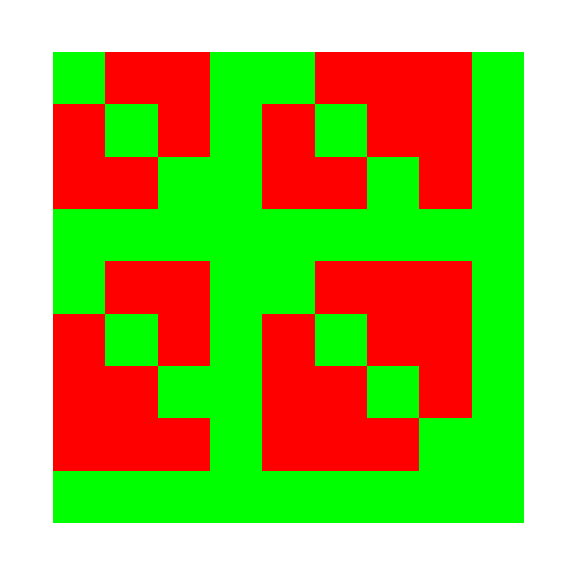

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x30tabzSKA[[1]],CovMatrix30x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_multi_50x30_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

# Test

```mathematica
Table[MultiSplitCovMatrixzSKA[[i]] == Transpose[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[i]] ], {i,ktot}]
```

{False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,648,648}

```mathematica
MultiSplitCovMatrixzSKA[[1,1,500]]
```

-1.0294×10^-6

```mathematica
MultiSplitCovMatrixzSKA[[1,500,1]]
```

-1.0294×10^-6

```mathematica
InvMultiSplitCovMatrixzSKA=ParallelTable[Inverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
Table[InvMultiSplitCovMatrixzSKA[[i]] == Transpose[InvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvMultiSplitCovMatrixzSKA[[1,1,501]]
```

1.5809×10^7

```mathematica
InvMultiSplitCovMatrixzSKA[[1,501,1]]
```

1.5809×10^7

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=MultiSplitCovMatrixzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{True,True,True,True},{{},{},{},{}}}

```mathematica
MultiSplitCovMatrixzSKA[[1,1;;36,325;;360]] == Transpose[MultiSplitCovMatrixzSKA[[1,325;;360,1;;36]]]
```

True

```mathematica
lambdas=Table[Eigenvalues[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}];
```

```mathematica
Dimensions[lambdas[[2]]]
```

{648}

```mathematica
tolerance=1e-20;(*Adjust the tolerance as needed*)
zerolambdas=Select[lambdas[[2]],Abs[#]<tolerance&];
```

```mathematica
zerolambdas
```

{}

```mathematica
Table[PositiveDefiniteMatrixQ[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
PseudoInvMultiSplitCovMatrixzSKA=ParallelTable[PseudoInverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
Table[PseudoInvMultiSplitCovMatrixzSKA[[i]] == Transpose[PseudoInvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
RandomReal[]*10^(-10)
```

1.93837×10^-11

```mathematica
Dimensions[MultiSplitCovMatrixzSKA[[1]]]
```

{648,648}

```mathematica
matrix=MultiSplitCovMatrixzSKA[[1]];
{minValue,{a,b}}=MinimalBy[Flatten[Table[{matrix[[i,j]],{i,j}},{i,Length[matrix]},{j,Length[matrix]}],1],First][[1]]
```

{-7.39551×10^-6,{325,474}}

```mathematica
RandomReal[]*minValue*10^(-2)
```

-5.70757×10^-8

```mathematica
minValue+RandomReal[]*minValue*10^(-2)
```

-7.45534×10^-6

```mathematica
minValue(1+RandomReal[]*10^(-3))
```

-7.39824×10^-6

```mathematica
sizes=Dimensions[MultiSplitCovMatrixzSKA]
```

{19,648,648}

```mathematica
nMatrices=sizes[[1]];(*Number of matrices in your array*)
matrixSize=sizes[[2]];(*Size of each matrix*)
scalingFactor=1*^-4;(*Adjust this factor for the desired scaling*)
RandMultiSplitCovMatrixzSKA=ConstantArray[{},nMatrices]; (*Define a new array*)
(*Loop through each matrix in your array*)
Do[
(*Extract the current matrix from your array*)
currentMatrix=MultiSplitCovMatrixzSKA[[i]];
(*Find the minimum value in the current matrix*)
minVal=Min[Select[Abs[Flatten[currentMatrix]],#!=0&]];
(*Generate a random symmetric matrix with the same dimensions as the current matrix*)randomSymmetricMatrix=Table[RandomReal[{-1,1}]*minVal*scalingFactor,{j,matrixSize},{k,matrixSize}];
  randomSymmetricMatrix=0.5*(randomSymmetricMatrix+Transpose[randomSymmetricMatrix]);
(*Subtract the diagonal elements to ensure they remain zero*)
randomMatrix=randomSymmetricMatrix-DiagonalMatrix[Diagonal[randomSymmetricMatrix]];
(*Add the random matrix to the current matrix*)
modifiedMatrix=currentMatrix+randomMatrix;
(*Replace the current matrix in your array with the modified matrix*)
RandMultiSplitCovMatrixzSKA[[i]]=modifiedMatrix,{i,nMatrices}]
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,648,648}

```mathematica
differences=MapThread[Not@*Equal,{RandMultiSplitCovMatrixzSKA[[1]],Transpose[RandMultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
Min[Abs[MultiSplitCovMatrixzSKA[[1]]]]
```

0.

```mathematica
Table[Min[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{-7.39551×10^-6,-2.99369×10^-6,-1.67555×10^-6,-1.10132×10^-6,-7.97558×10^-7,-6.17037×10^-7,-5.01604×10^-7,-4.24396×10^-7,-3.71795×10^-7,-3.36576×10^-7,-3.14823×10^-7,-3.05136×10^-7,-3.09325×10^-7,-3.30864×10^-7,-3.76578×10^-7,-4.60156×10^-7,-6.12711×10^-7,-8.81144×10^-7,-1.35996×10^-6}

```mathematica
findMin[matrix_List]:=Module[{min=Infinity},Do[If[NumericQ[matrix[[i,j]]]&&matrix[[i,j]]<min,min=matrix[[i,j]]],{i,Length[matrix]},{j,Length[matrix[[1]]]}];
min]

minValue=findMin[MultiSplitCovMatrixzSKA[[1]]]
```

-7.39551×10^-6

```mathematica
Table[Min[Select[Abs[Flatten[MultiSplitCovMatrixzSKA[[i]]]],#!=0&]],{i,ktot}]
```

{5.62015×10^-14,3.26834×10^-15,3.47539×10^-16,6.36504×10^-17,5.16167×10^-17,6.34278×10^-17,8.2403×10^-17,1.03666×10^-16,1.22286×10^-16,1.34664×10^-16,1.40087×10^-16,1.401×10^-16,1.39138×10^-16,1.3779×10^-16,1.39009×10^-16,1.4343×10^-16,1.52375×10^-16,1.67153×10^-16,1.83701×10^-16}

```mathematica
5.6201481107886695*^-14 * (1+scalingFactor)
```

5.62071×10^-14

```mathematica
minVal
```

1.83701×10^-16

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]
```

3.07546×10^-7

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]*(1+minVal*scalingFactor)
```

3.07546×10^-7

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True}

```mathematica
RandMultiSplitCovMatrixzSKAsym = Table[(RandMultiSplitCovMatrixzSKA[[i]]+Transpose[RandMultiSplitCovMatrixzSKA[[i]]])/2,{i,ktot}];
```

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[Diagonal[RandMultiSplitCovMatrixzSKAsym[[i]]]==Diagonal[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[RandMultiSplitCovMatrixzSKAsym[[i,1,All]]==MultiSplitCovMatrixzSKA[[i,1,All]],{i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvRandMultiSplitCovMatrixzSKA=Table[Inverse[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000114066,9.90812×10^-6,8.36022×10^-6,6.9584×10^-6,5.75502×10^-6,4.74691×10^-6,3.91231×10^-6,3.22537×10^-6,2.66171×10^-6,2.20014×10^-6,«638»},{9.90812×10^-6,9.0874×10^-6,7.96747×10^-6,6.7868×10^-6,5.69707×10^-6,4.74686×10^-6,3.94118×10^-6,3.26672×10^-6,2.70778×10^-6,2.24685×10^-6,«638»},«8»,«638»} may contain significant numerical errors.

```mathematica
InvRandMultiSplitCovMatrixzSKAsym=Table[Inverse[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000114066,9.90812×10^-6,8.36022×10^-6,6.9584×10^-6,5.75502×10^-6,4.74691×10^-6,3.91231×10^-6,3.22537×10^-6,2.66171×10^-6,2.20014×10^-6,«638»},{9.90812×10^-6,9.0874×10^-6,7.96747×10^-6,6.7868×10^-6,5.69707×10^-6,4.74686×10^-6,3.94118×10^-6,3.26672×10^-6,2.70778×10^-6,2.24685×10^-6,«638»},«8»,«638»} may contain significant numerical errors.

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_multi_50x30_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",RandMultiSplitCovMatrixzSKAsym[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

## 50-50 and 10-90 splits

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix10Bx90FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-10B_90F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x10tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix10x50tabzSKA[[i]], CovMatrix10Bx90FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix10Bx90FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x10tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix10x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x10tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix10x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x10tabzSKA[[i]] ==CovMatrix10x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x10tabzSKA[[1]],CovMatrix10x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x10tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x10tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_multi_50x10_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Table[MultiSplitCovMatrixzSKA[[i]] == Transpose[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[i]] ], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False}

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[1,1,500]]
```

-7.01589×10^-7

```mathematica
MultiSplitCovMatrixzSKA[[1,500,1]]
```

-7.01589×10^-7

```mathematica
InvMultiSplitCovMatrixzSKA=ParallelTable[Inverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.62361×10^-6,2.27759×10^-6,1.92102×10^-6,1.59849×10^-6,1.32181×10^-6,1.09012×10^-6,8.98368×10^-7,7.40569×10^-7,6.11106×10^-7,5.05103×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.62742×10^-6,4.01861×10^-6,3.3903×10^-6,2.82155×10^-6,2.33343×10^-6,1.92459×10^-6,1.58615×10^-6,1.3076×10^-6,1.07906×10^-6,8.9192×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
Table[InvMultiSplitCovMatrixzSKA[[i]] == Transpose[InvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvMultiSplitCovMatrixzSKA[[1,1,501]]
```

-32158.6

```mathematica
InvMultiSplitCovMatrixzSKA[[1,501,1]]
```

-32158.6

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=MultiSplitCovMatrixzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{True,True,True,True},{{},{},{},{}}}

```mathematica
MultiSplitCovMatrixzSKA[[1,1;;36,325;;360]] == Transpose[MultiSplitCovMatrixzSKA[[1,325;;360,1;;36]]]
```

True

```mathematica
lambdas=Table[Eigenvalues[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}];
```

```mathematica
Dimensions[lambdas[[2]]]
```

{576}

```mathematica
tolerance=1e-20;(*Adjust the tolerance as needed*)
zerolambdas=Select[lambdas[[2]],Abs[#]<tolerance&];
```

```mathematica
zerolambdas
```

{}

```mathematica
Table[PositiveDefiniteMatrixQ[MultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
PseudoInvMultiSplitCovMatrixzSKA=ParallelTable[PseudoInverse[MultiSplitCovMatrixzSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
Table[PseudoInvMultiSplitCovMatrixzSKA[[i]] == Transpose[PseudoInvMultiSplitCovMatrixzSKA[[i]]], {i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
RandomReal[]*10^(-10)
```

7.65871×10^-11

```mathematica
Dimensions[MultiSplitCovMatrixzSKA[[1]]]
```

{576,576}

```mathematica
matrix=MultiSplitCovMatrixzSKA[[1]];
{minValue,{a,b}}=MinimalBy[Flatten[Table[{matrix[[i,j]],{i,j}},{i,Length[matrix]},{j,Length[matrix]}],1],First][[1]]
```

{-8.19465×10^-6,{289,438}}

```mathematica
RandomReal[]*minValue*10^(-2)
```

-6.86525×10^-9

```mathematica
minValue+RandomReal[]*minValue*10^(-2)
```

-8.27262×10^-6

```mathematica
minValue(1+RandomReal[]*10^(-3))
```

-8.20237×10^-6

```mathematica
sizes=Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
nMatrices=sizes[[1]];(*Number of matrices in your array*)
matrixSize=sizes[[2]];(*Size of each matrix*)
scalingFactor=1*^-4;(*Adjust this factor for the desired scaling*)
RandMultiSplitCovMatrixzSKA=ConstantArray[{},nMatrices]; (*Define a new array*)
(*Loop through each matrix in your array*)
Do[
(*Extract the current matrix from your array*)
currentMatrix=MultiSplitCovMatrixzSKA[[i]];
(*Find the minimum value in the current matrix*)
minVal=Min[Select[Abs[Flatten[currentMatrix]],#!=0&]];
(*Generate a random symmetric matrix with the same dimensions as the current matrix*)randomSymmetricMatrix=Table[RandomReal[{-1,1}]*minVal*scalingFactor,{j,matrixSize},{k,matrixSize}];
  randomSymmetricMatrix=0.5*(randomSymmetricMatrix+Transpose[randomSymmetricMatrix]);
(*Subtract the diagonal elements to ensure they remain zero*)
randomMatrix=randomSymmetricMatrix-DiagonalMatrix[Diagonal[randomSymmetricMatrix]];
(*Add the random matrix to the current matrix*)
modifiedMatrix=currentMatrix+randomMatrix;
(*Replace the current matrix in your array with the modified matrix*)
RandMultiSplitCovMatrixzSKA[[i]]=modifiedMatrix,{i,nMatrices}]
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
differences=MapThread[Not@*Equal,{RandMultiSplitCovMatrixzSKA[[1]],Transpose[RandMultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[RandMultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

```mathematica
Min[Abs[MultiSplitCovMatrixzSKA[[1]]]]
```

0.

```mathematica
Table[Min[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{-8.19465×10^-6,-3.30686×10^-6,-1.84679×10^-6,-1.21278×10^-6,-8.79101×10^-7,-6.82425×10^-7,-5.58678×10^-7,-4.78517×10^-7,-4.27677×10^-7,-3.99466×10^-7,-3.93821×10^-7,-4.11378×10^-7,-4.58075×10^-7,-5.48451×10^-7,-7.12743×10^-7,-9.89034×10^-7,-1.45573×10^-6,-2.27026×10^-6,-3.71997×10^-6}

```mathematica
findMin[matrix_List]:=Module[{min=Infinity},Do[If[NumericQ[matrix[[i,j]]]&&matrix[[i,j]]<min,min=matrix[[i,j]]],{i,Length[matrix]},{j,Length[matrix[[1]]]}];
min]

minValue=findMin[MultiSplitCovMatrixzSKA[[1]]]
```

-8.19465×10^-6

```mathematica
Table[Min[Select[Abs[Flatten[MultiSplitCovMatrixzSKA[[i]]]],#!=0&]],{i,ktot}]
```

{5.62015×10^-14,2.7107×10^-14,1.75201×10^-14,1.29694×10^-14,1.03629×10^-14,8.69507×10^-15,7.5508×10^-15,6.7297×10^-15,6.1236×10^-15,5.66908×10^-15,5.32651×10^-15,5.06994×10^-15,4.88171×10^-15,4.74955×10^-15,4.66475×10^-15,4.62111×10^-15,4.61424×10^-15,4.64109×10^-15,4.69968×10^-15}

```mathematica
5.6201481107886695*^-14 * (1+scalingFactor)
```

5.62071×10^-14

```mathematica
minVal
```

4.69968×10^-15

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]
```

3.07546×10^-7

```mathematica
MultiSplitCovMatrixzSKA[[1,1,50]]*(1+minVal*scalingFactor)
```

3.07546×10^-7

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False}

```mathematica
RandMultiSplitCovMatrixzSKAsym = Table[(RandMultiSplitCovMatrixzSKA[[i]]+Transpose[RandMultiSplitCovMatrixzSKA[[i]]])/2,{i,ktot}];
```

```mathematica
Table[SymmetricMatrixQ[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[Diagonal[RandMultiSplitCovMatrixzSKAsym[[i]]]==Diagonal[MultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[RandMultiSplitCovMatrixzSKAsym[[i,1,All]]==MultiSplitCovMatrixzSKA[[i,1,All]],{i,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
InvRandMultiSplitCovMatrixzSKA=Table[Inverse[RandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.62742×10^-6,4.01861×10^-6,3.3903×10^-6,2.82155×10^-6,2.33343×10^-6,1.92459×10^-6,1.58615×10^-6,1.3076×10^-6,1.07906×10^-6,8.9192×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.62361×10^-6,2.27759×10^-6,1.92102×10^-6,1.59849×10^-6,1.32181×10^-6,1.09012×10^-6,8.98368×10^-7,7.40569×10^-7,6.11106×10^-7,5.05103×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
InvRandMultiSplitCovMatrixzSKAsym=Table[Inverse[RandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.62742×10^-6,4.01861×10^-6,3.3903×10^-6,2.82155×10^-6,2.33343×10^-6,1.92459×10^-6,1.58615×10^-6,1.3076×10^-6,1.07906×10^-6,8.9192×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.62361×10^-6,2.27759×10^-6,1.92102×10^-6,1.59849×10^-6,1.32181×10^-6,1.09012×10^-6,8.98368×10^-7,7.40569×10^-7,6.11106×10^-7,5.05103×10^-7,«566»},«9»,«566»} may contain significant numerical errors.

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKA[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[SymmetricMatrixQ[InvRandMultiSplitCovMatrixzSKAsym[[i]]],{i,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_multi_50x10_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",RandMultiSplitCovMatrixzSKAsym[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

# Kill

```mathematica
Exit[]
```